```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/guido/bispectrum_data

## Halo kernels in redshift space

Final output of this section are the halo kernels in redshift space

### Perturbation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m];
Fn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
F4[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]]; 
G2[q1_,q2_]=Simplify[Sum[1/Length[perm12]Gn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
G3[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Gn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
G4[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Gn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
```

### Define C_i Kernels and bare bias coefficients

initialize bare bias c_i values

```mathematica
c4 = Table[0,{i,1,15}];
```

```mathematica
c4[[1]]=Subscript["(ĉ)^(4)","δ,1"];
c4[[2]]=Subscript["(ĉ)^(4)","δ,2"];
c4[[3]]=Subscript["(ĉ)^(4)","δ,3"];
c4[[4]]=Subscript["(ĉ)^(4)","δ,4"];
c4[[5]]=Subscript["(ĉ)^(4)","δ^2,1"];
c4[[6]]=Subscript["(ĉ)^(4)","δ^2,2"];
c4[[7]]=Subscript["(ĉ)^(4)","δ^2,3"];
c4[[8]]=Subscript["(ĉ)^(4)","r^2,2"];
c4[[9]]=Subscript["(ĉ)^(4)","r^2,3"];
c4[[10]]=Subscript["(ĉ)^(4)","δ^3,1"];
c4[[11]]=Subscript["(ĉ)^(4)","δ^3,2"];
c4[[12]]=Subscript["(ĉ)^(4)","r^3,2"];
c4[[13]]=Subscript["(ĉ)^(4)","r^2δ,2"];
c4[[14]]=Subscript["(ĉ)^(4)","δ^4,1"];
c4[[15]]=Subscript["(ĉ)^(4)","δr^3,1"];
```

```mathematica
c3=c4//.{"(ĉ)^(4)"-> "(ĉ)^(3)"};
c2=c4//.{"(ĉ)^(4)"-> "(ĉ)^(2)"};
c1=c4//.{"(ĉ)^(4)"-> "(ĉ)^(1)"};
adelta = c4//.{"(ĉ)^(4)"-> "(c̃)^A"};
```

```mathematica
btheta={1,2,3,4,-1,-3/2,-2,0,0,1,4/3,0,0,-1,0};
```

Expressions for C_i kernels

```mathematica
For[i=1,i<16,i++,c1[[i]][q1_]:=0;]
For[i=1,i<16,i++,c2[[i]][q1_,q2_]:=0;]
For[i=1,i<16,i++,c3[[i]][q1_,q2_,q3_]:=0;]
```

```mathematica
c1[[1]][q1_]:=1;
c2[[1]][q1_,q2_]:=-(mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[2]][q1_,q2_]:=((1+2 F2[q1,q2]) mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)/(2 mag[q1]^2);
c2[[5]][q1_,q2_]:=1;
c3[[1]][q1_,q2_,q3_]:=1/8 (-1/mag[q2+q3]^2 2 G2[q2,q3] (2 mag[q1]^2+mag[q2]^2-mag[q1+q2]^2+mag[q3]^2-mag[q1+q3]^2)+((mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2))/(mag[q2]^2 mag[q3]^2));
c3[[2]][q1_,q2_,q3_]:=-(((mag[q1]^2+(1+2 F2[q1,q2]) mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q2]^2+2 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2))/(4 mag[q2]^2 mag[q3]^2));
c3[[3]][q1_,q2_,q3_]:=1/8 ((2 G2[q2,q3] (mag[q1]^2+mag[q2+q3]^2-mag[q1+q2+q3]^2))/mag[q2+q3]^2+1/(mag[q2]^2 mag[q3]^2)(mag[q1]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)-mag[q1+q2]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)+mag[q2]^2 ((1+4 F2[q1,q2]) mag[q1+q2]^2+(1+4 F2[q1,q2]+8 F3[q1,q2,q3]) mag[q3]^2-(1+4 F2[q1,q2]) mag[q1+q2+q3]^2)));c3[[5]][q1_,q2_,q3_]:=-(mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)/mag[q3]^2;
c3[[6]][q1_,q2_,q3_]:=2 F2[q1,q2]+(mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)/mag[q3]^2;
c3[[8]][q1_,q2_,q3_]:=1/(4 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2)(mag[q1]^4 mag[q1+q2]^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+(-mag[q2]^2 mag[q1+q2]+mag[q1+q2]^3)^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+2 mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2+mag[q1+q2]^4 (-mag[q3]^2+mag[q2+q3]^2)+mag[q2]^2 ((-1+F2[q1,q2]) mag[q1+q2]^4+F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2)^2+mag[q1+q2]^2 ((1+2 F2[q1,q2]) mag[q3]^2-mag[q2+q3]^2-2 F2[q1,q2] mag[q1+q2+q3]^2))));
c3[[10]][q1_,q2_,q3_]:=1;
```

```mathematica
c4[[1]][q1_,q2_,q3_,q4_]:=1/48 (1/(mag[q2]^2 mag[q3+q4]^2)2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (3 mag[q1]^2+2 mag[q2]^2+5 mag[q3+q4]^2-3 mag[q1+q3+q4]^2-2 mag[q2+q3+q4]^2)+1/(mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(-mag[q1]^6 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 mag[q2+q3]^2 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-4 mag[q3]^4+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q1+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)+2 mag[q3]^2 ((-3+G2[q2,q3]) mag[q2+q3]^2+G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q2]^2 (-4 mag[q3]^4 mag[q2+q3]^2+mag[q1+q3]^2 mag[q2+q3]^2 (4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2+q3]^4 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)-mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2 mag[q2+q3]^2+(1+2 G2[q2,q3]) mag[q2+q3]^4+2 G2[q2,q3] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q2+q3+q4]^2)+mag[q2+q3]^2 (-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2-2 G2[q2,q3] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)))))-(8 G3[q2,q3,q4] (mag[q1]^2+mag[q2+q3+q4]^2-mag[q1+q2+q3+q4]^2))/mag[q2+q3+q4]^2);
c4[[2]][q1_,q2_,q3_,q4_]:=-1/(16 mag[q2]^2)(1/(mag[q3]^2 mag[q4]^2)(-mag[q1]^6-mag[q2]^6+mag[q2]^4 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q2]^2 (4 mag[q3]^4-3 mag[q3]^2 mag[q1+q3]^2-mag[q3]^2 mag[q2+q3]^2+6 mag[q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2-4 mag[q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 F2[q1,q2] (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4-4 mag[q3]^4+3 mag[q3]^2 mag[q1+q3]^2+mag[q3]^2 mag[q2+q3]^2-6 mag[q3]^2 mag[q4]^2+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2+mag[q3]^2 mag[q1+q4]^2-mag[q1+q3]^2 mag[q1+q4]^2+mag[q3]^2 mag[q2+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2+4 mag[q3]^2 mag[q3+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2]^2 (-6 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1+q2]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)))+1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q1]^4+mag[q2]^4+mag[q1]^2 (2 mag[q2]^2-mag[q1+q2]^2+2 mag[q3+q4]^2-mag[q1+q3+q4]^2-mag[q2+q3+q4]^2)+mag[q1+q2]^2 (-2 mag[q3+q4]^2+mag[q1+q3+q4]^2+mag[q2+q3+q4]^2)+mag[q2]^2 ((-1+2 F2[q1,q2]) mag[q1+q2]^2+2 (1+F2[q1,q2]) mag[q3+q4]^2-mag[q1+q3+q4]^2-mag[q2+q3+q4]^2-2 F2[q1,q2] mag[q1+q2+q3+q4]^2)));
c4[[3]][q1_,q2_,q3_,q4_]:=1/(16 mag[q2]^2)(-1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q3+q4]^2-mag[q1+q3+q4]^2)+1/(mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(-mag[q1]^6 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1]^4 mag[q2+q3]^2 (-mag[q2]^2+mag[q1+q2]^2-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q3]^4+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q3]^2 (-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (-mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-4 mag[q3]^4+4 mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q1+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2-3 mag[q1+q3]^2 mag[q3+q4]^2-mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)-2 mag[q3]^2 ((3+G2[q2,q3]) mag[q2+q3]^2+G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))-mag[q2]^2 (4 mag[q3]^4 mag[q2+q3]^2-3 mag[q3]^2 mag[q1+q3]^2 mag[q2+q3]^2-mag[q3]^2 mag[q2+q3]^4+2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^4+8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2-2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2+6 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q2+q3]^2 mag[q4]^2-2 mag[q2+q3]^4 mag[q4]^2-2 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q2+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^4 mag[q2+q4]^2-4 mag[q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q2+q3]^4 mag[q3+q4]^2+4 F2[q1,q2] mag[q2+q3]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q2+q3+q4]^2+2 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q2+q3+q4]^2-8 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3+q4]^2)));
c4[[4]][q1_,q2_,q3_,q4_]:=1/48 ((8 G3[q2,q3,q4] (mag[q1]^2+mag[q2+q3+q4]^2-mag[q1+q2+q3+q4]^2))/mag[q2+q3+q4]^2+1/(mag[q2]^2 mag[q3+q4]^2)2 G2[q3,q4] (3 mag[q1]^4+mag[q2]^4+mag[q1]^2 (4 mag[q2]^2-3 mag[q1+q2]^2+4 mag[q3+q4]^2-3 mag[q1+q3+q4]^2-mag[q2+q3+q4]^2)+mag[q1+q2]^2 (-4 mag[q3+q4]^2+3 mag[q1+q3+q4]^2+mag[q2+q3+q4]^2)+mag[q2]^2 ((-1+6 F2[q1,q2]) mag[q1+q2]^2+(4+6 F2[q1,q2]) mag[q3+q4]^2-3 mag[q1+q3+q4]^2-mag[q2+q3+q4]^2-6 F2[q1,q2] mag[q1+q2+q3+q4]^2))+1/(mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2)(mag[q1]^6 mag[q2+q3]^2+mag[q2]^6 mag[q2+q3]^2+mag[q1]^4 mag[q2+q3]^2 (mag[q2]^2-mag[q1+q2]^2+4 mag[q3]^2-mag[q1+q3]^2+4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)-mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^2-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-4 mag[q3]^4+mag[q1+q3]^2 (4 mag[q4]^2-mag[q1+q4]^2-3 mag[q3+q4]^2)+mag[q2+q3]^2 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)+mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q1]^2 (mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (4 mag[q3]^4-4 mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q1+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+3 mag[q1+q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q1+q2]^2 (-4 mag[q3]^2+mag[q1+q3]^2-4 mag[q4]^2+mag[q1+q4]^2+3 mag[q3+q4]^2)-mag[q3]^2 (3 mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2))+mag[q2]^2 (-mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-6 mag[q4]^2+mag[q1+q4]^2+mag[q2+q4]^2+4 mag[q3+q4]^2)+mag[q3]^2 ((6+4 G2[q2,q3]) mag[q2+q3]^2+4 G2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q2]^2 (4 mag[q3]^4 mag[q2+q3]^2-3 mag[q3]^2 mag[q1+q3]^2 mag[q2+q3]^2-mag[q3]^2 mag[q2+q3]^4+4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^4+24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2-4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2+6 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+48 F4[q1,q2,q3,q4] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2+4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q4]^2-4 mag[q1+q3]^2 mag[q2+q3]^2 mag[q4]^2-2 mag[q2+q3]^4 mag[q4]^2-4 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q1+q4]^2+mag[q1+q3]^2 mag[q2+q3]^2 mag[q1+q4]^2-mag[q3]^2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^4 mag[q2+q4]^2-4 mag[q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+3 mag[q1+q3]^2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q2+q3]^4 mag[q3+q4]^2+6 F2[q1,q2] mag[q2+q3]^2 (mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2) (mag[q1+q2]^2+mag[q3]^2+2 mag[q4]^2-mag[q1+q2+q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 (-2 mag[q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-4 G2[q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q2+q3+q4]^2+4 G2[q2,q3] mag[q3]^2 mag[q1+q2+q3]^2 mag[q2+q3+q4]^2-24 F3[q1,q2,q3] mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3+q4]^2)));
c4[[5]][q1_,q2_,q3_,q4_]:=1/4 (1/(mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q2]^2 (3 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2+2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2))-1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2));
c4[[6]][q1_,q2_,q3_,q4_]:=-1/(2 mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4+2 F2[q1,q2] mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+2 F2[q2,q3] mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2+2 F2[q1,q2] mag[q3]^2 mag[q4]^2+2 F2[q2,q3] mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2-2 F2[q1,q2] mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2-mag[q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 F2[q2,q3] mag[q3]^2 mag[q2+q3+q4]^2);
c4[[7]][q1_,q2_,q3_,q4_]:=1/4 (1/mag[q4]^2 4 F2[q1,q2] (mag[q3]^2+(1+F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+1/mag[q3+q4]^2 2 G2[q3,q4] (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2)+1/(mag[q3]^2 mag[q4]^2)(mag[q2]^4+mag[q3]^4-mag[q3]^2 mag[q2+q3]^2+4 F2[q2,q3] mag[q3]^2 mag[q2+q3]^2+3 mag[q3]^2 mag[q4]^2+4 F2[q2,q3] mag[q3]^2 mag[q4]^2+8 F3[q1,q2,q3] mag[q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2-2 mag[q3]^2 mag[q2+q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q1]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)-mag[q3]^2 mag[q3+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+mag[q2]^2 (3 mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2+2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)-4 F2[q2,q3] mag[q3]^2 mag[q2+q3+q4]^2));
c4[[8]][q1_,q2_,q3_,q4_]:=(-mag[q1]^6 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)+mag[q1+q2]^2 (-mag[q2]^8 mag[q2+q3]^2+mag[q2]^6 mag[q2+q3]^2 (2 mag[q1+q2]^2-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^4+mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q1+q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q1+q2]^4 mag[q2+q3]^2 (-mag[q3]^4+mag[q1+q3]^2 (mag[q4]^2-mag[q2+q4]^2)+mag[q2+q3]^2 (2 mag[q4]^2-mag[q2+q4]^2-mag[q3+q4]^2)+mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^4 mag[q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+2 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))-2 F2[q2,q3] mag[q3]^2 (mag[q2+q3]^2-mag[q1+q2+q3]^2)^2 (mag[q2+q3]^2+mag[q4]^2-mag[q2+q3+q4]^2)))+mag[q1]^4 mag[q1+q2]^2 (-3 mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (-mag[q3]^4+mag[q1+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q4]^2-mag[q1+q3]^2 mag[q2+q4]^2-mag[q2+q3]^2 mag[q2+q4]^2+2 mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-mag[q2+q3]^2 mag[q3+q4]^2+mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (2 mag[q1+q2]^2 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-4 mag[q4]^2+3 mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 ((3+2 F2[q2,q3]) mag[q2+q3]^2+2 F2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))-mag[q1]^2 (3 mag[q2]^6 mag[q1+q2]^2 mag[q2+q3]^2-mag[q2]^4 mag[q1+q2]^2 mag[q2+q3]^2 (4 mag[q1+q2]^2-6 mag[q3]^2+2 mag[q1+q3]^2+2 mag[q2+q3]^2-5 mag[q4]^2+3 mag[q2+q4]^2+2 mag[q3+q4]^2)+mag[q1+q2]^4 mag[q2+q3]^2 (-2 mag[q3]^4+2 mag[q1+q3]^2 mag[q4]^2+4 mag[q2+q3]^2 mag[q4]^2-2 mag[q1+q3]^2 mag[q2+q4]^2-2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-2 mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^6 mag[q2+q3]^2+2 F2[q1,q2] mag[q2+q3]^2 (mag[q3]^2-mag[q1+q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)+2 mag[q1+q2]^4 mag[q2+q3]^2 ((-3+F2[q1,q2]) mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-3 mag[q4]^2+F2[q1,q2] mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2-F2[q1,q2] mag[q3+q4]^2)+2 mag[q1+q2]^2 ((1+2 F2[q1,q2]) mag[q3]^4 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+2 F2[q1,q2] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q3+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q3]^2 ((-1+2 F2[q2,q3]) mag[q2+q3]^4+2 F2[q2,q3] mag[q1+q2+q3]^2 (-mag[q4]^2+mag[q2+q3+q4]^2)-mag[q2+q3]^2 (-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2+2 F2[q1,q2] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q3+q4]^2)+2 F2[q2,q3] (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)))))))/(8 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q4]^2);
c4[[9]][q1_,q2_,q3_,q4_]:=1/16 ((2 G2[q3,q4] (mag[q1]^2+mag[q2]^2-mag[q1+q2]^2)^2 (mag[q2]^2+mag[q3+q4]^2-mag[q2+q3+q4]^2))/(mag[q1]^2 mag[q2]^2 mag[q3+q4]^2)+1/mag[q1+q2]^2 4 F2[q1,q2] (((mag[q1+q2]^2+mag[q3]^2-mag[q1+q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(mag[q3]^2 mag[q4]^2)+1/mag[q3+q4]^2 F2[q3,q4] (mag[q1+q2]^2+mag[q3+q4]^2-mag[q1+q2+q3+q4]^2)^2)+(mag[q1]^6 mag[q2+q3]^2 mag[q1+q2+q3]^2 (mag[q2]^2+mag[q4]^2-mag[q2+q4]^2)+mag[q1+q2+q3]^2 (mag[q2]^8 mag[q2+q3]^2-mag[q2]^6 mag[q2+q3]^2 (2 mag[q1+q2]^2-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)+mag[q1+q2]^4 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^4 mag[q2+q3]^2 (mag[q1+q2]^4+mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q1+q2]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (-mag[q1+q2]^4 mag[q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-2 mag[q1+q2]^2 mag[q2+q3]^2 (mag[q3]^4+mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+4 F2[q2,q3] mag[q3]^2 (mag[q2+q3]^2-mag[q1+q2+q3]^2)^2 (mag[q2+q3]^2+mag[q4]^2-mag[q2+q3+q4]^2)))+mag[q1]^4 mag[q1+q2+q3]^2 (3 mag[q2]^4 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q3]^4-mag[q1+q3]^2 mag[q4]^2-2 mag[q2+q3]^2 mag[q4]^2+mag[q1+q3]^2 mag[q2+q4]^2+mag[q2+q3]^2 mag[q2+q4]^2-2 mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)+mag[q2+q3]^2 mag[q3+q4]^2-mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))-mag[q2]^2 (2 mag[q1+q2]^2 mag[q2+q3]^2+mag[q2+q3]^2 (mag[q1+q3]^2+mag[q2+q3]^2-4 mag[q4]^2+3 mag[q2+q4]^2+mag[q3+q4]^2)-mag[q3]^2 ((3+4 F2[q2,q3]) mag[q2+q3]^2+4 F2[q2,q3] (mag[q4]^2-mag[q2+q3+q4]^2))))+mag[q1]^2 (3 mag[q2]^6 mag[q2+q3]^2 mag[q1+q2+q3]^2-mag[q2]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2 (4 mag[q1+q2]^2-6 mag[q3]^2+2 mag[q1+q3]^2+2 mag[q2+q3]^2-5 mag[q4]^2+3 mag[q2+q4]^2+2 mag[q3+q4]^2)+mag[q1+q2]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 (-2 mag[q3]^4+2 mag[q1+q3]^2 mag[q4]^2+4 mag[q2+q3]^2 mag[q4]^2-2 mag[q1+q3]^2 mag[q2+q4]^2-2 mag[q2+q3]^2 mag[q2+q4]^2+mag[q1+q2]^2 (mag[q4]^2-mag[q2+q4]^2)-2 mag[q2+q3]^2 mag[q3+q4]^2+2 mag[q3]^2 (mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2))+mag[q2]^2 (mag[q1+q2]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2+2 mag[q1+q2]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 (-3 mag[q3]^2+mag[q1+q3]^2+mag[q2+q3]^2-3 mag[q4]^2+2 mag[q2+q4]^2+mag[q3+q4]^2)+2 (mag[q3]^4 mag[q2+q3]^2 mag[q1+q2+q3]^2+mag[q2+q3]^2 mag[q1+q2+q3]^2 (mag[q1+q3]^2 (-mag[q4]^2+mag[q2+q4]^2)+mag[q2+q3]^2 (-2 mag[q4]^2+mag[q2+q4]^2+mag[q3+q4]^2))+mag[q3]^2 ((-1+4 F2[q2,q3]) mag[q2+q3]^4 mag[q1+q2+q3]^2+4 F2[q2,q3] mag[q1+q2+q3]^4 (-mag[q4]^2+mag[q2+q3+q4]^2)+mag[q2+q3]^2 (mag[q1+q2+q3]^2 (3 mag[q4]^2-2 mag[q2+q4]^2-mag[q3+q4]^2)-4 F2[q2,q3] mag[q1+q2+q3]^2 (mag[q1+q2+q3]^2-mag[q4]^2+mag[q2+q3+q4]^2)+4 F3[q1,q2,q3] (mag[q1+q2+q3]^2+mag[q4]^2-mag[q1+q2+q3+q4]^2)^2))))))/(mag[q1]^2 mag[q2]^2 mag[q3]^2 mag[q2+q3]^2 mag[q1+q2+q3]^2 mag[q4]^2));
c4[[10]][q1_,q2_,q3_,q4_]:=-(3 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(2 mag[q4]^2);
c4[[11]][q1_,q2_,q3_,q4_]:=(3 (mag[q3]^2+(1+2 F2[q1,q2]) mag[q4]^2-mag[q3+q4]^2))/(2 mag[q4]^2);
c4[[12]][q1_,q2_,q3_,q4_]:=-((3 (mag[q1]^4 mag[q1+q2]^2 (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+mag[q1+q2]^2 (mag[q2]^2-mag[q1+q2]^2) (mag[q3]^2-mag[q1+q3]^2) (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2)+mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2-mag[q1+q2]^2 (mag[q1+q2]^2-mag[q3]^2+mag[q1+q3]^2) (mag[q3]^2-mag[q2+q3]^2)+mag[q2]^2 ((-1+2 F2[q1,q2]) mag[q1+q2]^4+2 F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2) (mag[q4]^2-mag[q1+q2+q4]^2)+mag[q1+q2]^2 (2 (1+F2[q1,q2]) mag[q3]^2-mag[q1+q3]^2-mag[q2+q3]^2-2 F2[q1,q2] mag[q1+q2+q3]^2+2 F2[q1,q2] mag[q4]^2-2 F2[q1,q2] mag[q1+q2+q4]^2)))) (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2))/(16 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q4]^2));
c4[[13]][q1_,q2_,q3_,q4_]:=1/(8 mag[q1]^2 mag[q2]^2 mag[q1+q2]^2 mag[q3]^2 mag[q4]^2)(mag[q1]^4 mag[q1+q2]^2 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (mag[q2]^2-mag[q1+q2]^2)^2 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+2 mag[q1]^2 (mag[q2]^4 mag[q1+q2]^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)+mag[q1+q2]^2 (mag[q3]^2-mag[q2+q3]^2)^2 (mag[q3]^2+mag[q4]^2-mag[q3+q4]^2)-mag[q1+q2]^4 mag[q3]^2 (mag[q3]^2+(1+2 F2[q3,q4]) mag[q4]^2-mag[q3+q4]^2)+mag[q2]^2 (2 F2[q1,q2] mag[q1+q2]^4 mag[q4]^2+2 F2[q1,q2] (mag[q3]^2-mag[q1+q2+q3]^2)^2 mag[q4]^2+mag[q1+q2]^2 (3 mag[q3]^4-2 mag[q2+q3]^2 mag[q4]^2-4 F2[q1,q2] mag[q1+q2+q3]^2 mag[q4]^2+2 mag[q2+q3]^2 mag[q3+q4]^2+mag[q3]^2 (-2 mag[q2+q3]^2+(3+4 F2[q1,q2]+2 F2[q3,q4]) mag[q4]^2-3 mag[q3+q4]^2)))));
c4[[14]][q1_,q2_,q3_,q4_]:=1;
c4[[15]][q1_,q2_,q3_,q4_]:=-(((mag[q1]^2+mag[q2]^2-mag[q1+q2]^2) (mag[q1]^2+mag[q3]^2-mag[q1+q3]^2) (mag[q2]^2+mag[q3]^2-mag[q2+q3]^2))/(8 mag[q1]^2 mag[q2]^2 mag[q3]^2));
```

### Preliminaries

Coordinate choices. Here we take k1 along the third axis. q is the integration vector. z is the line of sight, angles are chosen such that k1.z = μ

```mathematica
Clear[zhat];
coordchoice={k1->{0,0,kk1},k2->kk2{0,√(1-y^2),y},k3->{0,-kk2 √(1-y^2),-kk1-kk2 y},q->qq{√(1-x^2)Cos[β],√(1-x^2) Sin[β],x}(*q->qq{√(1-x^2)α,√(1-x^2) √(1-α^2),x}*)};zhat1=zhat->{√(1-μ^2)Cos[ϕ],√(1-μ^2)Sin[ϕ], μ};zhat2=zhat->{Sin[θ] Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
```

```mathematica
ysub={y->(k3^2-k1^2-k2^2)/(2 k1 k2)};
```

This is zhat with angles w.r.t. the normal of the triangle, and check with Yankelevich-Porciani. 0<ω<π, 0<χ<2π

```mathematica
zhatnorm=zhat->{Cos[ω],-Sin[ω]Cos[χ],Sin[ω]Sin[χ]};
```

```mathematica
k1.zhat/.coordchoice/.zhatnorm
```

kk1 Sin[χ] Sin[ω]

```mathematica
Assuming[{ξ12>0,ξ12<π},k2.zhat/.coordchoice/.zhatnorm/.y->Cos[ξ12]//FullSimplify]
```

-kk2 Sin[ξ12-χ] Sin[ω]

```mathematica
k3.zhat/.coordchoice/.zhatnorm//FullSimplify
```

(kk2 √(1-y^2) Cos[χ]-(kk1+kk2 y) Sin[χ]) Sin[ω]

```mathematica
q.zhat/.coordchoice/.zhatnorm//FullSimplify
```

qq (√(1-x^2) Cos[β] Cos[ω]+(-√(1-x^2) Cos[χ] Sin[β]+x Sin[χ]) Sin[ω])

Definitions of magnitudes, which are needed to expand the kernels and PS

```mathematica
kmq[k1] = k1mq;
kmq[k2] = k2mq;
kmq[k3] = k3mq;
kpq[k1] = k1pq;
kpq[k2] = k2pq;
kpq[k3] = k3pq;
```

```mathematica
yrep = {y->(-k1^2-k2^2+k3^2)/(2 k1 k2)};
```

```mathematica
magreps ={mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k3]->k3,mag[-k1]->k1,mag[-k2]->k2,mag[-k1-k2]->k3,mag[k1+k2]->k3,mag[-k1+q]->k1mq,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k2+q]->k2mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k1-k2-q]->k3mq,mag[k1+k2+q]->k3mq,mag[-k1-k2+q]->k3pq,mag[k1+k2-q]->k3pq,mag[-k3]->k3,mag[-k1-k3]->k2,mag[k1+k3]->k2,mag[-k3+q]->k3mq,mag[k3-q]->k3mq,mag[-k3-q]->k3pq,mag[k3+q]->k3pq,mag[-k1-k3-q]->k2mq,mag[k1+k3+q]->k2mq,mag[-k1-k3+q]->k2pq,mag[k1+k3-q]->k2pq,mag[-k2-k3]->k1,mag[k2+k3]->k1,mag[-k2-k3-q]->k1mq,mag[k2+k3+q]->k1mq,mag[-k2-k3+q]->k1pq,mag[k2+k3-q]->k1pq,
mag[-q1]->q1,mag[q1]->q1,mag[-q-q1]->qpq1,mag[q-q1]->qmq1,mag[-q+q1]->qmq1,mag[q+q1]->qpq1};
```

```mathematica
magrevreps  = {k1mq-> √(k1^2+q^2-2 k1 q x),k1pq-> √(k1^2+q^2+2 k1 q x),k2mq-> √(k2^2+q^2-2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k2pq-> √(k2^2+q^2+2 k2 q (x y+√(1-x^2) √(1-y^2) Sin[β])),k3mq-> √(k3^2+q^2+2k1 q x+2k2 q x y+2k2 q √(1-x^2) √(1-y^2) Sin[β]),k3pq-> √(k3^2+q^2-2k1 q x-2k2 q x y-2k2 q √(1-x^2) √(1-y^2) Sin[β]),
qmq1-> √(q^2+q1^2-2ν q q1),qpq1-> √(q^2+q1^2+2ν q q1)};
```

Check magrevreps

```mathematica
Simplify[{(k1-q).(k1-q),(k1+q).(k1+q),(k2-q).(k2-q),(k2+q).(k2+q),(k3-q).(k3-q),(k3+q).(k3+q)}/.coordchoice]/.{kk1^2+kk2^2->kk3^2-2 kk1 kk2 y}//Simplify
```

{kk1^2+qq^2-2 kk1 qq x,kk1^2+qq^2+2 kk1 qq x,kk2^2+qq^2-2 kk2 qq x y-2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk2^2+qq^2+2 kk2 qq x y+2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk3^2+qq (qq+2 x (kk1+kk2 y))+2 kk2 qq √(1-x^2) √(1-y^2) Sin[β],kk3^2+qq (qq-2 x (kk1+kk2 y))-2 kk2 qq √(1-x^2) √(1-y^2) Sin[β]}

define line of sight angle. Note that for now we keep μ3 and intermediary also define μ0, which we will substitute later.
Try to integrate over μ and ϕ to get the monopole!

```mathematica
kzsub = {Subscript[k1, z]-> k1 μ1,Subscript[k2, z]-> k2 μ2,Subscript[q, z]-> q μ0,Subscript[k3, z]->k3 μ3};
```

```mathematica
μtoangles1=Assuming[{y>-1,y<1,μ>-1,μ<1,ϕ>0,ϕ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhat1//FullSimplify]
```

{μ1→μ,μ2→y μ+√((-1+y^2) (-1+μ^2)) Sin[ϕ],μ3→-(kk1 μ+kk2 y μ+kk2 √((-1+y^2) (-1+μ^2)) Sin[ϕ])/kk3,μ0→x μ+√((-1+x^2) (-1+μ^2)) Cos[β-ϕ]}

```mathematica
μtoangles2=Assuming[{y>-1,y<1,μ>-1,μ<1,ϕ>0,ϕ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhat2]
```

{μ1→Cos[θ],μ2→(kk2 y Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk2,μ3→((-kk1-kk2 y) Cos[θ]-kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0→1/qq(qq x Cos[θ]+qq √(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+qq √(1-x^2) Sin[β] Sin[θ] Sin[ϕ])}

```mathematica
μtoanglesnorm=Assuming[{y>-1,y<1,ω>0,ω<π,χ>0,χ<2π,x>-1,x<1},{μ1->(k1.zhat)/kk1,μ2->(k2.zhat)/kk2,μ3->(k3.zhat)/kk3,μ0->(q.zhat)/qq}/.coordchoice/.zhatnorm//FullSimplify]
```

{μ1→Sin[χ] Sin[ω],μ2→(-√(1-y^2) Cos[χ]+y Sin[χ]) Sin[ω],μ3→((kk2 √(1-y^2) Cos[χ]-(kk1+kk2 y) Sin[χ]) Sin[ω])/kk3,μ0→√(1-x^2) Cos[β] Cos[ω]+(-√(1-x^2) Cos[χ] Sin[β]+x Sin[χ]) Sin[ω]}

```mathematica
μtoangles3=Assuming[{k1q∈Reals,qq>0,kk1>0,kk2>0,y>-1,y<1},{μ1->Cos[θ],μ2->y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ3->-((kk1+kk2 y) Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0->x Cos[θ]+√(1-x^2) Cos[β-ϕ] Sin[θ]}/.x->k1q/(kk1 qq)//FullSimplify]
```

{μ1→Cos[θ],μ2→y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ3→-((kk1+kk2 y) Cos[θ]+kk2 √(1-y^2) Sin[θ] Sin[ϕ])/kk3,μ0→(k1q Cos[θ])/(kk1 qq)+√(1-k1q^2/(kk1^2 qq^2)) Cos[β-ϕ] Sin[θ]}

```mathematica
q.k2/.coordchoice
```

kk2 qq x y+kk2 qq √(1-x^2) √(1-y^2) Sin[β]

define symmetrization over two and three variables

```mathematica
q2sym[f_,q1_,q2_]:=1/2(f[q1,q2]+f[q2,q1]);
q3sym[f_,q1_,q2_,q3_]:=Total[(f@@@Permutations[{q1,q2,q3}])/(3!)];
q4sym[f_,q1_,q2_,q3_,q4_]:=Total[(f@@@Permutations[{q1,q2,q3,q4}])/(4!)]
```

define final bias coefficients

```mathematica
tb={adelta[[1]]-> b1,adelta[[2]]-> b2,adelta[[3]]-> b3,adelta[[4]]-> b4,adelta[[5]]-> b5,adelta[[6]]->b6,adelta[[7]]->b7-15/2 adelta[[13]],adelta[[8]]-> b8,adelta[[9]]-> b9,adelta[[10]]-> b10,adelta[[12]]-> b11};
tbrev  = {b1-> adelta[[1]],b2-> adelta[[2]],b3-> adelta[[3]],b4-> adelta[[4]],b5-> adelta[[5]],b6-> adelta[[6]],b7-> adelta[[7]]+15/2 adelta[[13]],b8-> adelta[[8]],b9-> adelta[[9]],b10-> adelta[[10]],b11-> adelta[[12]]};
biases = {b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
```

Projections on matter and velocity (as a special species of biased tracer)

```mathematica
submat=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
subvel=Thread[biases->{1,2,3,4,-1,-3/2,-2,0,0,1,0}]
```

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

{b1→1,b2→2,b3→3,b4→4,b5→-1,b6→-3/2,b7→-2,b8→0,b9→0,b10→1,b11→0}

```mathematica
finduv[func_,n_]:=Series[func,{q,∞,n}]//Normal;
findir[func_,n_]:=Series[func,{q,0,n}]//Normal;
```

Here we only keep μ0, and leave μ1 and μ2, μ3 to the coefficients of each FFTLog integral

```mathematica
μlistfinal  = Table[μ0^i,{i,0,6}];
μlistfinalno1 = Delete[μlistfinal,1];
```

```mathematica
μlister[ker_]:=
Join[{ker},Monitor[Table[Coefficient[ker,μlistfinalno1⟦i⟧],{i,1,Length[μlistfinalno1]}],i]]/.{μ0-> 0}
```

Adds up the different contributions from the tabs, for instance {{0,0,0,a},{0,0,0,b}}→ {0,0,0,a+b}.

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list⟦#⟧&];
```

```mathematica
compressor[tab_] := Module[{tab1,tab2},
tab1 = positionDuplicates[Table[Delete[tab⟦i⟧,4],{i,1,Length[tab]}]];
tab2 = Monitor[Table[{tab⟦tab1⟦j,1⟧⟧⟦{1,2,3}⟧,
Sum[tab⟦tab1⟦j,i⟧⟧⟦4⟧,{i,1,Length[tab1⟦j⟧]}]}//Flatten,{j,1,Length[tab1]}],j*100.0/Length[tab1]]]
```

```mathematica
comp[tab_]:=Table[compressor[tab⟦i⟧],{i,1,7}]
```

Replacements
Notice that we modify μ0 as well!
the replacements q→ -q, q→ k1pq and q→ k2mq  have the following coding:
k1mk2=|k1-k2+q|,
k12pq = |2k1+q|,
k22mq = |2k2-q|,
kspeck1 = |2k1+k2+q|,
kspeck2 = |k1+2k2+q|

```mathematica
preqtok1pq= Thread[{q,k1pq, k1mq, k2pq, k2mq, k3pq, k3mq,μ0}-> {k1pqt,k12pq,qt,k3mqt,k1mk2,k2mqt,kspeck1,μ0t}];
preqtok2mq = Thread[{q,k1pq, k1mq, k2pq, k2mq, k3pq, k3mq,μ0}-> {k2mqt,k3pqt,k1mk2,k22mq,qt,k1pqt,kspeck2,μ0t}];
qtok1pq = Thread[ {k1pqt,k12pq,qt,k3mqt,k1mk2,k2mqt,kspeck1,μ0t}-> {k1pq,√(2 k1^2+2 k1pq^2-q^2),q,k3mq,√(k1^2+k1pq^2+k2^2+k2mq^2-k3^2-q^2),k2mq,√(2 k1pq^2-k2mq^2+2 k3^2),(q μ0+k1 μ1)/k1pq}];
qtok2mq = Thread[ {k2mqt,k3pqt,k1mk2,k22mq,qt,k1pqt,kspeck2,μ0t}->{k2mq,k3pq,√(k1^2+k1pq^2+k2^2+k2mq^2-k3^2-q^2),√(2 k2^2+2 k2mq^2-q^2),q,k1pq,√(-2 k1^2+k1pq^2+4 k2^2-2 k2mq^2+2 k3^2+2 q^2),(-q μ0+k2 μ2)/k2mq} ];
restrep = Thread[{k1mq,k2pq,k3mq,k3pq}-> {√(2 k1^2-k1pq^2+2 q^2),√(2 k2^2-k2mq^2+2 q^2),√(-k1^2+k1pq^2+k2^2-k2mq^2+k3^2+q^2),√(k1^2-k1pq^2-k2^2+k2mq^2+k3^2+q^2)}];
```

```mathematica
qrev1={k1mq->k1pqt,k1pq->k1mqt,k2mq->k2pqt,k2pq->k2mqt,k3mq->k3pqt,k3pq->k3mqt,μ0-> μ0t};
qrev2={k1mqt->k1mq,k1pqt->k1pq,k2mqt->k2mq,k2pqt->k2pq,k3mqt->k3mq,k3pqt->k3pq,μ0t-> -μ0};
```

Tests

Tabtester checks that all terms of the expression were listed in terms of the exponents of the master integral and coefficients. It passed if all is 0

```mathematica
(*Tabtester[final_,tab_]:=Table[final⟦j⟧-Sum[q^(-2tab⟦j,i,1⟧)k1pq^(-2tab⟦j,i,2⟧)k2mq^(-2tab⟦j,i,3⟧)*tab⟦j,i,4⟧,{i,1,Length[tab⟦j⟧]}]//Expand,{j,1,7}];*)
```

```mathematica
Tabtester[final_,tab_]:=Table[final-q^(-2tab⟦i,1⟧)k1pq^(-2tab⟦i,2⟧)k2mq^(-2tab⟦i,3⟧)*tab⟦i,4⟧,{i,1,Length[tab]}]//Expand;
```

Tabtester2 checks that the coefficients are only composed of f1, k1, k2, k3, Linear powerspectra without q dependence,μ1 and μ2, biases and numbers. It passed if the result is {1}

```mathematica
(*Tabtester2[tab_]:=Table[Table[tab⟦j,i⟧,{i,1,Length[tab⟦j⟧]}]//Expand,{j,1,7}]/.Thread[{ν,ν1,ν2}-> 1]/.{f1->1,k1->1,k2->1,k3->1,μ1->1,μ2->1,μ3->1}/.Thread[biases-> 1]/._Rational-> 1/._Integer-> 1//Flatten//DeleteDuplicates;*)
Tabtester2[tab_]:=Table[tab⟦i⟧,{i,1,Length[tab]}]//Expand/.Thread[{ν,ν1,ν2}-> 1]/.{f1->1,k1->1,k2->1,k3->1,μ1->1,μ2->1,μ3->1}/.Thread[biases-> 1]/._Rational-> 1/._Integer-> 1//Flatten//DeleteDuplicates;
```

### Halo Kernels (real space)

```mathematica
K1[aa_]:=aa⟦1⟧;
K2[q1_,q2_,aa_]:=K2[q1,q2,aa]=((Table[c2⟦i⟧[q1,q2],{i,1,15}]/.{al->alfm,be->befm}/.{mag[-q]->mag[q]}/.magreps//Expand)/.mag[0]-> 0//Simplify).aa;
K3[q1_,q2_,q3_,aa_]:=K3[q1,q2,q3,aa]=((Table[c3⟦i⟧[q1,q2,q3],{i,1,15}]/.{al->alfm,be->befm}/.{mag[-q]->mag[q]}/.magreps//Expand)/.mag[0]-> 0//Simplify).aa;
K4[q1_,q2_,q3_,q4_,aa_]:=K4[q1,q2,q3,q4,aa]=((Monitor[Table[q4sym[c4⟦i⟧,q1,q2,q3,q4]/.{al->alfm,be->befm}/.magreps//Simplify,{i,1,15}],i])/.mag[0]-> 0).aa;
```

Check the <δ(2)> which has to be subtracted

```mathematica
δ2vev=K2[q1,-q1,adelta]/.tb
```

-b1+b2+b5

### Halo Kernels (real space for delta)

```mathematica
K1d[q1_]:=K1[adelta]//.{kz-> q1.zhat}//.Dot[a_,a_]-> mag[a]^2/.{Dot[a_,zhat]-> Subscript[a, z]}/.magreps//.kzsub;
K2d[q1_,q2_]:=K2[q1,q2,adelta]/.{al->alfm,be->befm}/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K2dsym[q1_,q2_]:=q2sym[K2d,q1,q2];
K3d[q1_,q2_,q3_]:=K3[q1,q2,q3,adelta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.magreps/.{kz-> (q1+q2+q3).zhat}//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K3dsym[q1_,q2_,q3_] := q3sym[K3d,q1,q2,q3];
K4d[q1_,q2_,q3_,q4_]:=K4[q1,q2,q3,q4,adelta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K4dsym[q1_,q2_,q3_,q4_]:=q4sym[K4d,q1,q2,q3,q4];
```

Check the <δ(2)> which has to be subtracted

```mathematica
δ2vev=K2[q1,-q1,adelta]/.tb
```

-b1+b2+b5

### Halo Kernels (redshift space)

Notice that we need to normal order, which amounts to a known counterterm due to subtraction of <delta_h(2)> in the redshift space expression for delta

```mathematica
K1r[q1_]:=K1[adelta]+f1 kz^2/((q1).(q1))K1[btheta]//.{kz-> q1.zhat}//.Dot[a_,a_]-> mag[a]^2/.{Dot[a_,zhat]-> Subscript[a, z]}/.magreps//.kzsub;
```

```mathematica
K2r[q1_,q2_]:=K2[q1,q2,adelta]+f1   kz^2/((q1+q2).(q1+q2))K2[q1,q2,btheta]+ f1 kz 1/2((q1.zhat)/(q1.q1)+(q2.zhat)/(q2.q2))K1[btheta]K1[adelta]+1/2 f1^2 kz^2((q1.zhat)(q2.zhat))/((q1.q1)(q2.q2))K1[btheta]K1[btheta]/.{al->alfm,be->befm}/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K2rsym[q1_,q2_]:=q2sym[K2r,q1,q2];
```

```mathematica
K3r[q1_,q2_,q3_]:=K3[q1,q2,q3,adelta]+f1 kz^2/((q1+q2+q3).(q1+q2+q3)) K3[q1,q2,q3,btheta]+f1 kz (q3.zhat)/(q3.q3)K2[q1,q2,adelta]K1[btheta]+f1 kz (q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]K1[adelta]+f1^2/2 kz^2 (q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)K1[btheta]K1[btheta]K1[adelta]+f1^2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]K1[btheta]+f1^3/6 kz^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)K1[btheta]K1[btheta]K1[btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.magreps/.{kz-> (q1+q2+q3).zhat}//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
K3rsym[q1_,q2_,q3_] := q3sym[K3r,q1,q2,q3];
```

Here we split the K4 kernels from the pieces of the previous ones, because of speed

```mathematica
K4rsome[q1_,q2_,q3_,q4_]:=K4[q1,q2,q3,q4,adelta]+f1 kz^2/((q1+q2+q3+q4).(q1+q2+q3+q4)) K4[q1,q2,q3,q4,btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
```

```mathematica
K4dist[q1_,q2_,q3_,q4_]:=f1 kz (q1.zhat+q2.zhat+q3.zhat)/((q1+q2+q3).(q1+q2+q3))K3[q1,q2,q3,btheta]K1[adelta]+
f1 kz (q1.zhat+q2.zhat)/((q1+q2).(q1+q2))K2[q1,q2,btheta]K2[q3,q4,adelta]+
f1 kz (q1.zhat)/(q1.q1)K1[btheta]K3[q2,q3,q4,adelta]+
f1^2 kz^2(q1.zhat+q2.zhat+q3.zhat)/((q1+q2+q3).(q1+q2+q3))(q4.zhat)/(q4.q4)K3[q1,q2,q3,btheta]K1[btheta]+
f1^2/2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat+q4.zhat)/((q3+q4).(q3+q4))K2[q1,q2,btheta]K2[q3,q4,btheta]+
f1^2 kz^2(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)K2[q1,q2,btheta]K1[btheta]K1[adelta]+
f1^2/2 kz^2 (q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)K1[btheta]K1[btheta]K2[q3,q4,adelta]+f1^3/2 kz^3(q1.zhat+q2.zhat)/((q1+q2).(q1+q2))(q3.zhat)/(q3.q3)(q4.zhat)/(q4.q4)K2[q1,q2,btheta]K1[btheta]K1[btheta]+f1^3/6 kz^3(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)K1[btheta]K1[btheta]K1[btheta]K1[adelta]+f1^4/24 kz^4(q1.zhat)/(q1.q1)(q2.zhat)/(q2.q2)(q3.zhat)/(q3.q3)(q4.zhat)/(q4.q4)K1[btheta]K1[btheta]K1[btheta]K1[btheta]/.Dot[a_,a_]-> mag[a]^2/.mag[-q]->mag[q]/.{kz-> (q1+q2+q3+q4).zhat}/.magreps//.Dot[a_+b_,c_]-> Dot[a,c]+Dot[b,c]/.{Dot[-a_,b_]-> -Dot[a,b]}/.{Dot[a_,zhat]-> Subscript[a, z]}//.kzsub;
```

```mathematica
K4distrsym[q1_,q2_,q3_,q4_]:=q4sym[K4dist,q1,q2,q3,q4];
```

```mathematica
K4rsym[q1_,q2_,q3_,q4_]:=K4distrsym[q1,q2,q3,q4]+K4rsome[q1,q2,q3,q4];
```

## Multipole integrals -- only monopole so far

Function defining the integrals over trig functions of θ and ϕ

```mathematica
(*angint[a_,b_,c_,d_]=Assuming[{a≥0,b≥0,c≥0,d≥0,a∈Integers,b∈Integers,c∈Integers,d∈Integers},1/(4 π)Integrate[μ^a(√(1-μ^2))^b Sin[γ]^c Cos[γ]^d,{μ,-1,1},{γ,0,2π}]//Simplify]*)
```

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

Use the function to do replacements, incredibly faster than the integral

```mathematica
rules4={Cos[θ]^(a_.) Sin[θ]^(b_.)Cos[ϕ]^(c_.)Sin[ϕ]^(d_.)->angint[a,b,c,d]};
rules3={Cos[θ]^(a_.) Sin[θ]^(b_.)Cos[ϕ]^(c_.)->angint[a,b,c,0],
Cos[θ]^(a_.) Sin[θ]^(b_.)Sin[ϕ]^(d_.)->angint[a,b,0,d],
Cos[θ]^(a_.) Cos[ϕ]^(c_.)Sin[ϕ]^(d_.)->angint[a,0,c,d],
Sin[θ]^(b_.)Cos[ϕ]^(c_.)Sin[ϕ]^(d_.)->angint[0,b,c,d]};
rules2={Cos[θ]^(a_.) Sin[θ]^(b_.)->angint[a,b,0,0],
Cos[θ]^(a_.) Cos[ϕ]^(c_.)->angint[a,0,c,0],
 Sin[θ]^(b_.)Cos[ϕ]^(c_.)->angint[0,b,c,0],
Cos[θ]^(a_.) Sin[ϕ]^(d_.)->angint[a,0,0,d],
 Sin[θ]^(b_.)Sin[ϕ]^(d_.)->angint[0,b,0,d],
Cos[ϕ]^(c_.)Sin[ϕ]^(d_.)->angint[0,0,c,d]};
rules1={Cos[θ]^(a_.)->angint[a,0,0,0],Sin[θ]^(b_.)->angint[0,b,0,0], Cos[ϕ]^(c_.)->angint[0,0,c,0],Sin[ϕ]^(d_.)->angint[0,0,0,d]};
```

```mathematica
(*rules4={Cos[ω]^(a_.) Sin[ω]^(b_.)Cos[χ]^(c_.)Sin[χ]^(d_.)->angint[a,b,c,d]};
rules3={Cos[ω]^(a_.) Sin[ω]^(b_.)Cos[χ]^(c_.)->angint[a,b,c,0],
Cos[ω]^(a_.) Sin[ω]^(b_.)Sin[χ]^(d_.)->angint[a,b,0,d],
Cos[ω]^(a_.) Cos[χ]^(c_.)Sin[χ]^(d_.)->angint[a,0,c,d],
Sin[ω]^(b_.)Cos[χ]^(c_.)Sin[χ]^(d_.)->angint[0,b,c,d]};
rules2={Cos[ω]^(a_.) Sin[ω]^(b_.)->angint[a,b,0,0],
Cos[ω]^(a_.) Cos[χ]^(c_.)->angint[a,0,c,0],
 Sin[ω]^(b_.)Cos[χ]^(c_.)->angint[0,b,c,0],
Cos[ω]^(a_.) Sin[χ]^(d_.)->angint[a,0,0,d],
 Sin[ω]^(b_.)Sin[χ]^(d_.)->angint[0,b,0,d],
Cos[χ]^(c_.)Sin[χ]^(d_.)->angint[0,0,c,d]};
rules1={Cos[ω]^(a_.)->angint[a,0,0,0],Sin[ω]^(b_.)->angint[0,b,0,0], Cos[χ]^(c_.)->angint[0,0,c,0],Sin[χ]^(d_.)->angint[0,0,0,d]};*)
```

```mathematica
Expand[μ1^2 μ3^4/.μtoangles2]/.rules4/.rules3/.rules2/.rules1//FullSimplify
```

((kk1^2+kk2^2+2 kk1 kk2 y) (5 kk1^2+10 kk1 kk2 y+kk2^2 (1+4 y^2)))/(35 kk3^4)

```mathematica
Expand[μ1^2 μ3^4/.μtoangles2]/.rules4/.rules3/.rules2/.rules1/.y->(kk3^2-kk2^2-kk1^2)/(2 kk1 kk2)//FullSimplify
```

(kk1^4+(kk2^2-kk3^2)^2+kk1^2 (-2 kk2^2+3 kk3^2))/(35 kk1^2 kk3^2)

```mathematica
Expand[μ1^2 μ2^4/.μtoangles2]/.rules4/.rules3/.rules2/.rules1/.y->(k3^2-k2^2-k1^2)/(2 k1 k2)/.{k1->kk1,k2->kk3,k3->kk2}//FullSimplify
```

1/35 (1+((kk1^2-kk2^2+kk3^2)^2)/(kk1^2 kk3^2))

```mathematica
1/35 (1+((kk1^2-kk2^2+kk3^2)^2)/(kk1^2 kk3^2))-(kk1^4+(kk2^2-kk3^2)^2+kk1^2 (-2 kk2^2+3 kk3^2))/(35 kk1^2 kk3^2)//FullSimplify
```

0

```mathematica
Expand[μ2^2 μ3^4/.μtoangles2]/.rules4/.rules3/.rules2/.rules1/.y->(kk3^2-kk2^2-kk1^2)/(2 kk1 kk2)//FullSimplify
```

(kk1^4+kk2^4+3 kk2^2 kk3^2+kk3^4-2 kk1^2 (kk2^2+kk3^2))/(35 kk2^2 kk3^2)

```mathematica
Expand[μ1^2 μ2^4/.μtoangles2]/.rules4/.rules3/.rules2/.rules1/.y->(k3^2-k2^2-k1^2)/(2 k1 k2)/.{k1->kk2,k2->kk3,k3->kk1}//FullSimplify
```

1/35 (1+((-kk1^2+kk2^2+kk3^2)^2)/(kk2^2 kk3^2))

```mathematica
1/35 (1+((-kk1^2+kk2^2+kk3^2)^2)/(kk2^2 kk3^2))-(kk1^4+kk2^4+3 kk2^2 kk3^2+kk3^4-2 kk1^2 (kk2^2+kk3^2))/(35 kk2^2 kk3^2)//FullSimplify
```

0

Given a kernel, lists coefficients of μlist

```mathematica
μlister[ker_,μlist_]:=
Join[{ker},Monitor[Table[Coefficient[ker,μlist⟦i⟧],{i,1,Length[μlist]}],i*100./Length[μlist]]]/.{μ0-> 0,μ1->0,μ2->0,μ3->0}
```

Given a list of monomials involving trig functions of θ and ϕ, gets the monopole. One function is simplified, the other is expanded

```mathematica
monosub[monos_]:=Monitor[Join[{1},Table[Assuming[{y>-1,y<1},Simplify@Total[monos⟦i⟧/.rules4/.rules3/.rules2/.rules1]],{i,1,Length[monos]}]],i*100./Length[monos]];
monosub2[monos_]:=Monitor[Join[{1},Table[Assuming[{y>-1,y<1},Expand@Total[monos⟦i⟧/.rules4/.rules3/.rules2/.rules1]],{i,1,Length[monos]}]],i*100./Length[monos]];
```

Function to get monopole given a basis of μi’s. Prints 0 if the expansion is correct

```mathematica
GetMonopole[ker_,μlist_]:=Module[{mlist,monos},
monos=MonomialList[#,{Cos[θ],Sin[θ],Cos[ϕ],Sin[ϕ]}]&/@(μlist/.μtoangles3/.{kk1->k1,kk2->k2,kk3->k3});
mlist=μlister[ker,μlist];
Print["Residual is"];
Print[ker-mlist.Join[{1},μlist]//Simplify];
mlist.monosub[monos]//Simplify]
```

```mathematica
GetMonopolenoSimp[ker_,μlist_]:=Module[{mlist,monos},
monos=MonomialList[#,{Cos[θ],Sin[θ],Cos[ϕ],Sin[ϕ]}]&/@(μlist/.μtoangles3/.{kk1->k1,kk2->k2,kk3->k3});
mlist=μlister[ker,μlist];
Print["Residual is"];
Print[ker-mlist.Join[{1},μlist]//Expand];
(mlist.monosub2[monos])]
```

Function to check degeneracies. We put also the biases since they come from kernels on the outside legs. The output is a list of replacements

```mathematica
arrepmono[a_]:=Thread[{k1,k2,k3,b1,b2,b5,f1}-> RandomInteger[{1,500},7]]
degenchreckmono[Kers_]:= Module[{rand1,check1,check2,arr,l,rep1,llist,zeros1,zeros2,kerreps},
l = Length[Kers];
rand1=Table[arrepmono[s1],{s1,1,l}];
rep1 = Solve[(Kers/.rand1).Table[Subscript[q, i],{i,1,l}]==0];
llist = Coefficient[Table[Subscript[K, i],{i,1,l}].Table[Subscript[q, i],{i,1,l}]/.(rep1//Flatten)//Expand,Table[Subscript[q, i],{i,1,l}]];

Table[Subscript[K, i]-> Subscript[K, i]-llist[[i]],{i,1,l}];
Solve[llist==0]//Flatten;
llist
]
```

```mathematica
(*arrep[arr_]:=Thread[arr->RandomInteger[{1,200},{Length[arr]}]];(*Generate a random realization of the array*)
degenchreck[Kers_]:=Module[{rand1,check1,check2,arr,l,rep1,llist,zeros1,zeros2,kerreps},arr=Table[Subscript[z,i],{i,1,3}];
l=Length[Kers[arr]];
rand1=Table[arrep[arr],{s1,1,l}];
rep1=Solve[(Kers[arr]/.rand1).Table[Subscript[q,i],{i,1,l}]==0];
llist=Coefficient[Table[Subscript[K,i],{i,1,l}].Table[Subscript[q,i],{i,1,l}]/.(rep1//Flatten)//Expand,Table[Subscript[q,i],{i,1,l}]];
check1=arrep[arr];
check2=arrep[arr];
(*zeros1=Quiet[llist/.Subscript[K,s_]->Kers[arr][[s]]/.check1];
zeros2=Quiet[llist/.Subscript[K,s_]->Kers[arr][[s]]/.check2];
If[Total[Abs[zeros1]]≠0||Total[Abs[zeros2]]≠0,Throw[overflow]];*)
(*Table[Subscript[K,i]->Subscript[K,i]-llist[[i]],{i,1,l}];
Solve[llist==0]//Flatten*)
llist]*)
```

## PS bias in new basis

```mathematica
k22[k1_,q_]:=2 K2rsym[-q,q+k1]^2
```

```mathematica
P22Integrand[k1_,q_] :=k22[k1,q]*Plin[q]Plin[kpq[k1]]/.tb;
```

```mathematica
P22Integrand[k1,q]//FullSimplify
```

1/(392 k1pq^4 q^4)(-28 b5 k1pq^2 q^2-7 b1 (k1^2-k1pq^2-q^2) (k1pq^2+q^2)-2 b2 (k1^4+k1pq^4+12 k1pq^2 q^2+q^4-2 k1^2 (k1pq^2+q^2))+14 b1 f1 k1 (k1pq-q) q (k1pq+q) μ0 μ1+f1 (-4 k1^4+3 (k1pq^2-q^2)^2+k1^2 (k1pq^2+q^2 (1-14 b1+14 f1 μ0^2))) μ1^2+14 f1^2 k1^3 q μ0 μ1^3)^2 Plin[k1pq] Plin[q]

```mathematica
Table[D[P22Integrand[k1,q],biases⟦i⟧]/.magrevreps//Simplify,{i,1,Length[biases]}]
```

{1/(7 q^2 (k1^2+q^2+2 k1 q x)^2)(2 q^3+4 k1 q^2 x+k1^3 (x+f1 μ0 μ1)+k1^2 q (1+2 x^2+2 f1 x μ0 μ1-f1 μ1^2)) (-14 b5 k1^2 q-14 b5 q^3-28 b5 k1 q^2 x-2 b2 q (7 q^2+14 k1 q x+k1^2 (5+2 x^2))+f1 k1^2 q μ1^2+7 f1 k1^3 x μ1^2+6 f1 k1^2 q x^2 μ1^2+7 f1^2 k1^2 q μ0^2 μ1^2+7 f1^2 k1^3 μ0 μ1^3+7 b1 (2 q^3+4 k1 q^2 x+k1^3 (x+f1 μ0 μ1)+k1^2 q (1+2 x^2+2 f1 x μ0 μ1-f1 μ1^2))) Plin[q] Plin[√(k1^2+q^2+2 k1 q x)],-1/(49 q (k1^2+q^2+2 k1 q x)^2)2 (7 q^2+14 k1 q x+k1^2 (5+2 x^2)) (-14 b5 k1^2 q-14 b5 q^3-28 b5 k1 q^2 x-2 b2 q (7 q^2+14 k1 q x+k1^2 (5+2 x^2))+f1 k1^2 q μ1^2+7 f1 k1^3 x μ1^2+6 f1 k1^2 q x^2 μ1^2+7 f1^2 k1^2 q μ0^2 μ1^2+7 f1^2 k1^3 μ0 μ1^3+7 b1 (2 q^3+4 k1 q^2 x+k1^3 (x+f1 μ0 μ1)+k1^2 q (1+2 x^2+2 f1 x μ0 μ1-f1 μ1^2))) Plin[q] Plin[√(k1^2+q^2+2 k1 q x)],0,0,-1/(7 q (k1^2+q^2+2 k1 q x))2 (-14 b5 k1^2 q-14 b5 q^3-28 b5 k1 q^2 x-2 b2 q (7 q^2+14 k1 q x+k1^2 (5+2 x^2))+f1 k1^2 q μ1^2+7 f1 k1^3 x μ1^2+6 f1 k1^2 q x^2 μ1^2+7 f1^2 k1^2 q μ0^2 μ1^2+7 f1^2 k1^3 μ0 μ1^3+7 b1 (2 q^3+4 k1 q^2 x+k1^3 (x+f1 μ0 μ1)+k1^2 q (1+2 x^2+2 f1 x μ0 μ1-f1 μ1^2))) Plin[q] Plin[√(k1^2+q^2+2 k1 q x)],0,0,0,0,0,0}

This only depends on b1, b2, b5

```mathematica
serK3k2=Normal[Series[K3rsym[k1,q,-q]/.magrevreps,{q,∞,2}]]/.tb//Simplify
```

1/(126 q^2)(b3 (-8 k1^2 (-1+x^2)^2+6 q^2 (13+8 x^2))+3 (42 b10 q^2-20 b2 q^2-28 b5 q^2+68 b6 q^2-8 b2 q^2 x^2+16 b6 q^2 x^2-40 b8 k1^2 (-1+x^2)^2+4 b8 q^2 (10+11 x^2)-2 f1 k1^2 μ1^2+14 b2 f1 q^2 μ1^2+14 b5 f1 q^2 μ1^2-9 f1 k1^2 x^2 μ1^2+4 f1 k1^2 x^4 μ1^2-12 f1^2 k1^2 μ0^2 μ1^2+12 f1^2 k1^2 x^2 μ0^2 μ1^2-14 f1^2 k1^2 x μ0 μ1^3-7 f1^3 k1^2 μ0^2 μ1^4)+3 b1 (-2 q^2 (3+4 x^2+7 f1 μ1^2)+k1^2 (6+12 x^4-38 f1 x μ0 μ1+24 f1 x^3 μ0 μ1+12 f1 μ1^2-7 f1^2 μ0^2 μ1^2-x^2 (25+12 f1 μ1^2))))

Integrate over angles dividing by 1/4π

```mathematica
uvK3k2=1/(4 π)Integrate[serK3k2/.μtoangles2,{x,-1,1},{β,0,2π}]/.Sin[2 θ]^2->1-Cos[2θ]^2/.{Cos[2 θ]->-1+2 μ1^2,Cos[θ]->μ1}//Simplify
```

-1/(1890 q^2)(-3 b1 k1^2+64 b3 k1^2+960 b8 k1^2+390 b1 q^2-1890 b10 q^2+1020 b2 q^2-1410 b3 q^2+1260 b5 q^2-3300 b6 q^2-2460 b8 q^2+3 f1 ((63-2 b1+36 f1+35 b1 f1) k1^2+210 (b1-b2-b5) q^2) μ1^2+3 f1^2 (58+35 f1) k1^2 μ1^4-36 f1^2 k1^2 μ1^2 (-1+μ1^2))

```mathematica
uvK3k2/.k1->0//FullSimplify
```

1/63 (-13 b1+63 b10-34 b2+47 b3-42 b5+110 b6+82 b8+21 (-b1+b2+b5) f1 μ1^2)

```mathematica
k31[k1_,q_]:=K1r[k1](K3rsym[k1,q,-q]-uvK3k2)/.mag[0]-> 0
```

```mathematica
P31Integrand[k1_,q_] := 6Plin[k1]Plin[q]k31[k1,q]/.tb/.k1mq->√(2 k1^2-k1pq^2+2 q^2)
```

```mathematica
P31simp=P31Integrand[k1,q]//Simplify;
```

Integrate over mu0

```mathematica
P31temp=1/(4 π)Assuming[{k1>0,q>0,μ1>0,μ1<1},Integrate[P31simp/.{μ0->x Cos[θ]+√(1-x^2) Cos[β-ϕ] Sin[θ]}/.magrevreps,{x,-1,1},{β,0,2π}]]/.{Cos[2 θ]->-1+2 μ1^2,Cos[θ]->μ1};
```

```mathematica
P31temp//Simplify
```

1/(10080 k1^3 q^5)(b1+f1 μ1^2) (4 k1 q (4 b3 (15 k1^6+73 k1^4 q^2-55 k1^2 q^4+15 q^6)+60 b8 (15 k1^6+73 k1^4 q^2-55 k1^2 q^4+15 q^6)-18 b1 q^2 (33 k1^4-40 k1^2 q^2+15 q^4) (1+2 f1 μ1^2)+3 f1 μ1^2 (15 k1^6 (4+3 f1 (1+μ1^2))-15 q^6 (2+f1 (-3+9 μ1^2))+k1^4 q^2 (94-3 f1 (-73+59 μ1^2))+5 k1^2 q^4 (4+f1 (-33+63 μ1^2))))+15 (k1^2-q^2)^3 (4 b3 (k1^2-q^2)+60 b8 (k1^2-q^2)+18 b1 q^2 (1+2 f1 μ1^2)+3 f1 μ1^2 (k1^2 (4+3 f1 (1+μ1^2))+q^2 (2+f1 (-3+9 μ1^2)))) Log[(k1-q)^2]-30 (k1^2-q^2)^3 (4 b3 (k1^2-q^2)+60 b8 (k1^2-q^2)+18 b1 q^2 (1+2 f1 μ1^2)+3 f1 μ1^2 (k1^2 (4+3 f1 (1+μ1^2))+q^2 (2+f1 (-3+9 μ1^2)))) Log[k1+q]) Plin[k1] Plin[q]

```mathematica
Table[D[P31temp,biases⟦i⟧],{i,2,Length[biases]}]
```

{0,1/(20160 k1^3 q^5)(b1+f1 μ1^2) (480 k1^7 q+2336 k1^5 q^3-1760 k1^3 q^5+480 k1 q^7+120 k1^8 Log[(k1-q)^2]-480 k1^6 q^2 Log[(k1-q)^2]+720 k1^4 q^4 Log[(k1-q)^2]-480 k1^2 q^6 Log[(k1-q)^2]+120 q^8 Log[(k1-q)^2]-240 k1^8 Log[k1+q]+960 k1^6 q^2 Log[k1+q]-1440 k1^4 q^4 Log[k1+q]+960 k1^2 q^6 Log[k1+q]-240 q^8 Log[k1+q]) Plin[k1] Plin[q],0,0,0,0,1/(20160 k1^3 q^5)(b1+f1 μ1^2) (7200 k1^7 q+35040 k1^5 q^3-26400 k1^3 q^5+7200 k1 q^7+1800 k1^8 Log[(k1-q)^2]-7200 k1^6 q^2 Log[(k1-q)^2]+10800 k1^4 q^4 Log[(k1-q)^2]-7200 k1^2 q^6 Log[(k1-q)^2]+1800 q^8 Log[(k1-q)^2]-3600 k1^8 Log[k1+q]+14400 k1^6 q^2 Log[k1+q]-21600 k1^4 q^4 Log[k1+q]+14400 k1^2 q^6 Log[k1+q]-3600 q^8 Log[k1+q]) Plin[k1] Plin[q],0,0,0}

So it only depends on b3, b8, in the combination b3 + 15 b8

```mathematica
D[P31temp,b8]/D[P31temp,b3]//Simplify
```

15

## B211 in redshift space

```mathematica
k211[k1_,k2_,k3_]:=k211[k1,k2,k3]=2 K2rsym[k1,k2]K1r[k1]K1r[k2]/.tb
```

```mathematica
B211perm[k1_,k2_,k3_] :=k211[k1,k2,k3]Plin[k1]Plin[k2];
```

```mathematica
B211[k1_,k2_,k3_]:=B211perm[k1,k2,k3]+B211perm[k2,k3,k1]+B211perm[k3,k1,k2]/.tb
```

```mathematica
μlist12=DeleteCases[Table[μ1^i μ2^j,{i,0,6},{j,0,6}]//Flatten,1];
μlist23=DeleteCases[Table[μ2^i μ3^j,{i,0,6},{j,0,6}]//Flatten,1];
μlist31=DeleteCases[Table[μ3^i μ1^j,{i,0,6},{j,0,6}]//Flatten,1];
```

```mathematica
perm123mono=GetMonopole[B211perm[k1,k2,k3],μlist12];
```

Residual is

0

```mathematica
perm231mono=GetMonopole[B211perm[k2,k3,k1],μlist23];
```

Residual is

0

```mathematica
perm312mono=GetMonopole[B211perm[k3,k1,k2],μlist31];
```

Residual is

0

Check that we can simply permute. Notice the substitutions of y

```mathematica
(perm123mono/.ysub/.{k1->k2t,k2->k3t,k3->k1t}/.{k1t->k1,k2t->k2,k3t->k3})-(perm231mono/.ysub)//Simplify
```

0

```mathematica
(perm123mono/.ysub/.{k1->k3t,k2->k1t,k3->k2t}/.{k1t->k1,k2t->k2,k3t->k3})-(perm312mono/.ysub)//Simplify
```

0

We have up to b1^3, b2, b5, and up to f1^4. Build up a list to put into PyBird

```mathematica
flist={1,f1,f1^2,f1^3,f1^4};
blist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
templist=DeleteCases[Flatten[Outer[Times,flist,blist]],1];
```

Get coefficients for everything

```mathematica
tabcoefftemp=Table[Coefficient[B211[k1,k2,k3],templist⟦i⟧],{i,1,Length[templist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
```

Check which coefficients are nonzero, and select the right ones. The following are the non-zero ones

```mathematica
posbias=Complement[Range[Length[templist]],Position[tabcoefftemp,0]//Flatten];
treelist=templist⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1^2 f1,b1 b2 f1,b1 b5 f1,b1^2 f1^2,b1 f1^2,b2 f1^2,b5 f1^2,b1 f1^3,f1^3,f1^4}

Create the tables for a monopole permutation, and check that this treelist is correct

```mathematica
tab123=Table[Coefficient[perm123mono,treelist⟦i⟧],{i,1,Length[treelist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123mono-tab123.treelist//Simplify
```

0

Finally, export into Python -- best we can do is FortranForm

```mathematica
For[i=1,i≤Length[tab123],i++,
Print[FortranForm[tab123⟦i⟧]/.Plin->Function[x,1]]]
```

-((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2))/(2.*k1**2*k2**2)

(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))/(7.*k1**2*k2**2)

2

(2*k1*k2 + k1**2*y + k2**2*y)/(3.*k1*k2)

-(3*k1**6 - 3*k1**4*(k2**2 - 5*k3**2) - 3*k1**2*(k2**4 - 10*k2**2*k3**2 + 6*k3**4) + 3*(k2**6 + 5*k2**4*k3**2 - 6*k2**2*k3**4) + 6*k1**5*k2*y + 2*k1**3*k2*(-6*k2**2 + k3**2)*y + 2*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y)/(42.*k1**2*k2**2*k3**2)

(2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(21.*k1**2*k2**2)

1.3333333333333333

(9*k1**2*y + 9*k2**2*y + 2*k1*k2*(5 + 4*y**2))/(15.*k1*k2)

-(36*k1**5*k2*y + 12*k1**3*k2*(-6*k2**2 + k3**2)*y + 12*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + 6*k1**6*(2 + y**2) + k1**4*(-6*k2**2*(2 + y**2) + k3**2*(11 + 16*y**2)) + k2**2*(k2**2 - k3**2)*(6*k2**2*(2 + y**2) + k3**2*(23 + 22*y**2)) - k1**2*(6*k2**4*(2 + y**2) - 2*k2**2*k3**2*(11 + 16*y**2) + k3**4*(23 + 22*y**2)))/(210.*k1**2*k2**2*k3**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + 2*y**2))/(105.*k1**2*k2**2)

(2*(1 + 2*y**2))/15.

(k1**2*y*(11 + 4*y**2) + k2**2*y*(11 + 4*y**2) + 6*k1*(k2 + 4*k2*y**2))/(35.*k1*k2)

-((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(k1**2*(1 + 4*y**2) + k2**2*(1 + 4*y**2) + k1*k2*(6*y + 4*y**3)))/(490.*k1**2*k2**2*k3**2)

(5*k1**2*y*(3 + 4*y**2) + 5*k2**2*y*(3 + 4*y**2) + 2*k1*k2*(3 + 24*y**2 + 8*y**4))/(315.*k1*k2)

### Check B211 numerically

Import PS. This is different than the interpolation from Python, import that on the triangles too

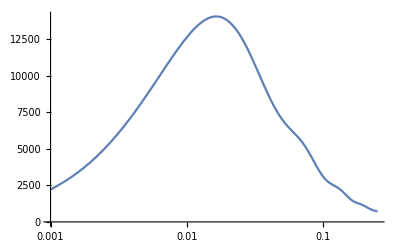

```mathematica
Pktab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Pktest.dat","Table"];
Ptriantab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Ptriantest.dat","Table"];
iPk=Interpolation[Pktab];
LogLinearPlot[iPk[k],{k,0.001,0.25}]
```

Import bispectrum to get triangles, order them such that k1 >= k2 >= k3

```mathematica
Btab=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/Bisp_LightConeHector_cmass_ngc_mean.dat","Table"];
triangles=Btab⟦All,3;;1;;-1⟧;
triangles⟦;;10⟧
```

{{0.017221,0.017221,0.017221},{0.027562,0.027562,0.017221},{0.03818,0.03818,0.017221},{0.048836,0.048836,0.017221},{0.059539,0.059539,0.017221},{0.070261,0.070261,0.017221},{0.081,0.081,0.017221},{0.091757,0.091757,0.017221},{0.102501,0.102501,0.017221},{0.11325,0.11325,0.017221}}

For our test cosmology we have

```mathematica
subcosmo={f1->0.7775551009423526,nbar->4.5 10^-4,b1->2.,b2->0.4,b5->0.7,kM->1.}
```

{f1→0.777555,nbar→0.00045,b1→2.,b2→0.4,b5→0.7,kM→1.}

```mathematica
Bp123num=Table[perm123mono/.ysub/.subcosmo/.{Plin[k1]->Ptriantab⟦i,1⟧,Plin[k2]->Ptriantab⟦i,2⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
Bp231num=Table[perm231mono/.ysub/.subcosmo/.{Plin[k2]->Ptriantab⟦i,2⟧,Plin[k3]->Ptriantab⟦i,3⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
Bp312num=Table[perm312mono/.ysub/.subcosmo/.{Plin[k3]->Ptriantab⟦i,3⟧,Plin[k1]->Ptriantab⟦i,1⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];

B211num=Bp123num+Bp231num+Bp312num;
```

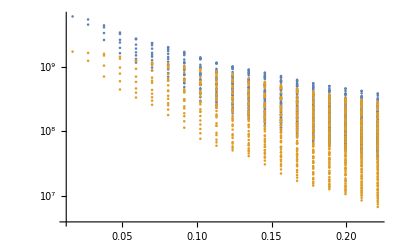

```mathematica
ListLogPlot[{Transpose@{triangles⟦All,1⟧,Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,B211num}},PlotRange->All]
```

```mathematica
Export["Btree_check42.dat",B211num];
```

## B211 in redshift space, with resummation

We will approximate the resummation factor expanding μ around 0, up to second order. We could probably do better, but this looks already good (μ=2/3 has errors < 0.1% on PS at 0.25

```mathematica
k211[k1_,k2_,k3_]:=k211[k1,k2,k3]=2 K2rsym[k1,k2]K1r[k1]K1r[k2]/.tb
```

```mathematica
Σt2[μ1_]:=(1+f1 (2+f1)μ1^2)Σ2+f1^2 μ1^2(μ1^2-1)δΣ2
Pres[k1_,μ1_]:=Pnw[k1]+(1+k1^2 Σt2[μ1])Exp[-k1^2 Σt2[μ1]]Pw[k1]
P1P2res[k1_,μ1_,k2_,μ2_]:=Pnw[k1]Pnw[k2]+(ⅇ^(-k1^2 Σ2) (1+k1^2 Σ2+f1^2 k1^4 μ1 Σ2 (-2 Σ2-μ1 ((-1+f1^2) δΣ2+Σ2+f1^2 Σ2 (2-2 k1^2 Σ2)))))Pw[k1]Pnw[k2]+(ⅇ^(-k2^2 Σ2) (1+k2^2 Σ2+f1^2 k2^4 μ2 Σ2 (-2 Σ2-μ2 ((-1+f1^2) δΣ2+Σ2+f1^2 Σ2 (2-2 k2^2 Σ2)))))Pnw[k1]Pw[k2]
```

Average of Σt2 on μ1, which we’ll use in the loops

```mathematica
k211res[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=k211[k1,k2,k3]P1P2res[k1,μ1,k2,μ2](*+B211perm[k2,k3,k1]+B211perm[k3,k1,k2]/.tb*)
```

```mathematica
μlist12=DeleteCases[Table[μ1^i μ2^j,{i,0,7},{j,0,7}]//Flatten,1];
μlist23=DeleteCases[Table[μ2^i μ3^j,{i,0,7},{j,0,7}]//Flatten,1];
μlist31=DeleteCases[Table[μ3^i μ1^j,{i,0,7},{j,0,7}]//Flatten,1];
```

```mathematica
perm123mono=GetMonopole[k211res[k1,k2,k3,μ1,μ2,μ3],μlist12];
```

Residual is

0

```mathematica
perm231mono=GetMonopole[k211res[k2,k3,k1,μ2,μ3,μ1],μlist23];
```

Residual is

0

```mathematica
perm312mono=GetMonopole[k211res[k3,k1,k2,μ3,μ1,μ2],μlist31];
```

Residual is

0

Check that we can simply permute. Notice the substitutions of y

```mathematica
(perm123mono/.ysub/.{k1->k2t,k2->k3t,k3->k1t}/.{k1t->k1,k2t->k2,k3t->k3})-(perm231mono/.ysub)//Simplify
```

0

```mathematica
(perm123mono/.ysub/.{k1->k3t,k2->k1t,k3->k2t}/.{k1t->k1,k2t->k2,k3t->k3})-(perm312mono/.ysub)//Simplify
```

0

We must separate the contributions Pnw Pnw and Pnw Pw. Pnw Pnw is the same as non-resummed case

```mathematica
perm123mononwnw=Coefficient[perm123mono,Pnw[k1]Pnw[k2]]//Simplify
```

-1/(4410 k1^2 k2^2 k3^2)(-735 b1^3 k3^2 (-3 k1^4-3 k2^4+3 k2^2 k3^2+k1^2 ((-6+4 f1) k2^2+3 k3^2)+2 f1 k1^3 k2 y+2 f1 k1 k2^3 y)-21 b1^2 (30 k3^2 (14 b5 k1^2 k2^2+b2 (k1^4+(k2^2-k3^2)^2+2 k1^2 (6 k2^2-k3^2)))-5 f1 (3 k1^6-3 k1^4 (k2^2-5 k3^2)-3 k1^2 (k2^4-10 k2^2 k3^2+6 k3^4)+3 (k2^6+5 k2^4 k3^2-6 k2^2 k3^4)+6 k1^5 k2 y+2 k1^3 k2 (-6 k2^2+k3^2) y+2 k1 k2 (3 k2^4+k2^2 k3^2-4 k3^4) y)+14 f1^2 k1 k2 k3^2 (9 k1^2 y+9 k2^2 y+2 k1 k2 (5+4 y^2)))-f1^2 (42 k3^2 (14 b5 k1^2 k2^2+b2 (k1^4+(k2^2-k3^2)^2+2 k1^2 (6 k2^2-k3^2))) (1+2 y^2)-9 f1 (3 k1^4+3 k2^4+k2^2 k3^2-4 k3^4+k1^2 (-6 k2^2+k3^2)) (k1^2 (1+4 y^2)+k2^2 (1+4 y^2)+k1 k2 (6 y+4 y^3))+14 f1^2 k1 k2 k3^2 (5 k1^2 y (3+4 y^2)+5 k2^2 y (3+4 y^2)+2 k1 k2 (3+24 y^2+8 y^4)))-21 b1 f1 (20 k3^2 (14 b5 k1^2 k2^2+b2 (k1^4+(k2^2-k3^2)^2+2 k1^2 (6 k2^2-k3^2)))+6 f1^2 k1 k2 k3^2 (k1^2 y (11+4 y^2)+k2^2 y (11+4 y^2)+6 k1 (k2+4 k2 y^2))-f1 (36 k1^5 k2 y+12 k1^3 k2 (-6 k2^2+k3^2) y+12 k1 k2 (3 k2^4+k2^2 k3^2-4 k3^4) y+6 k1^6 (2+y^2)+k1^4 (-6 k2^2 (2+y^2)+k3^2 (11+16 y^2))+k2^2 (k2^2-k3^2) (6 k2^2 (2+y^2)+k3^2 (23+22 y^2))-k1^2 (6 k2^4 (2+y^2)-2 k2^2 k3^2 (11+16 y^2)+k3^4 (23+22 y^2)))))

```mathematica
perm123mononw1w2=Coefficient[perm123mono,Pnw[k1]Pw[k2]]//Simplify;
```

```mathematica
perm123monow1nw2=Coefficient[perm123mono,Pw[k1]Pnw[k2]]//Simplify;
```

Check

```mathematica
perm123mononwnw Pnw[k1]Pnw[k2]+perm123mononw1w2 Pnw[k1]Pw[k2]+perm123monow1nw2 Pw[k1]Pnw[k2]-perm123mono//Simplify
```

0

We have up to b1^3, b2, b5, and up to f1^4. Build up a list to put into PyBird

```mathematica
flist={1,f1,f1^2,f1^3,f1^4};
blist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
templist=DeleteCases[Flatten[Outer[Times,flist,blist]],1];
```

#### Coefficients for Pnw(k1) Pnw(k1)

```mathematica
flist={1,f1,f1^2,f1^3,f1^4};
blist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
templist=DeleteCases[Flatten[Outer[Times,flist,blist]],1];
```

```mathematica
tabcoefftemp=Table[Coefficient[perm123mononwnw,templist⟦i⟧],{i,1,Length[templist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123mononwnw-tabcoefftemp.templist//Simplify
```

0

Check which coefficients are nonzero, and select the right ones. The following are the non-zero ones

```mathematica
posbias=Complement[Range[Length[templist]],Position[tabcoefftemp,0]//Flatten];
treelist=templist⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1^2 f1,b1 b2 f1,b1 b5 f1,b1^2 f1^2,b1 f1^2,b2 f1^2,b5 f1^2,b1 f1^3,f1^3,f1^4}

Create the tables for a monopole permutation, and check that this treelist is correct

```mathematica
tab123=Table[Coefficient[perm123mononwnw,treelist⟦i⟧],{i,1,Length[treelist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123mononwnw-tab123.treelist//Simplify
```

0

Finally, export into Python -- best we can do is FortranForm

```mathematica
For[i=1,i≤Length[tab123],i++,
Print[FortranForm[tab123⟦i⟧]]]
```

-((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2))/(2.*k1**2*k2**2)

(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))/(7.*k1**2*k2**2)

2

(2 + (k1*y)/k2 + (k2*y)/k1)/3.

-(3*k1**6 - 3*k1**4*(k2**2 - 5*k3**2) - 3*k1**2*(k2**4 - 10*k2**2*k3**2 + 6*k3**4) + 3*(k2**6 + 5*k2**4*k3**2 - 6*k2**2*k3**4) + 6*k1**5*k2*y + 2*k1**3*k2*(-6*k2**2 + k3**2)*y + 2*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y)/(42.*k1**2*k2**2*k3**2)

(2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(21.*k1**2*k2**2)

1.3333333333333333

(10 + (9*k1*y)/k2 + (9*k2*y)/k1 + 8*y**2)/15.

(-36*k1**5*k2*y + 12*k1**3*k2*(6*k2**2 - k3**2)*y - 12*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y - 6*k1**6*(2 + y**2) + k1**4*(6*k2**2*(2 + y**2) - k3**2*(11 + 16*y**2)) - k2**2*(k2**2 - k3**2)*(6*k2**2*(2 + y**2) + k3**2*(23 + 22*y**2)) + k1**2*(6*k2**4*(2 + y**2) - 2*k2**2*k3**2*(11 + 16*y**2) + k3**4*(23 + 22*y**2)))/(210.*k1**2*k2**2*k3**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + 2*y**2))/(105.*k1**2*k2**2)

(2*(1 + 2*y**2))/15.

(k1**2*y*(11 + 4*y**2) + k2**2*y*(11 + 4*y**2) + 6*k1*(k2 + 4*k2*y**2))/(35.*k1*k2)

-((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(k1**2*(1 + 4*y**2) + k2**2*(1 + 4*y**2) + k1*k2*(6*y + 4*y**3)))/(490.*k1**2*k2**2*k3**2)

(6 + 48*y**2 + 16*y**4 + (5*k1*y*(3 + 4*y**2))/k2 + (5*k2*y*(3 + 4*y**2))/k1)/315.

#### Coefficients for Pnw(k1) Pw(k2). We keep Σ2 and δΣ2 inside... But biases are different

```mathematica
flist={1,f1,f1^2,f1^3,f1^4,f1^5,f1^6,f1^7,f1^8};
blist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
templist=DeleteCases[Flatten[Outer[Times,flist,blist]],1];
```

```mathematica
tabcoefftemp=Table[Coefficient[perm123mononw1w2,templist⟦i⟧],{i,1,Length[templist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123mononw1w2-tabcoefftemp.templist//Simplify
```

0

Check which coefficients are nonzero, and select the right ones. The following are the non-zero ones

```mathematica
posbias=Complement[Range[Length[tabcoefftemp]],Position[tabcoefftemp,0]//Flatten];
treelist2=templist⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1^2 f1,b1 b2 f1,b1 b5 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b2 f1^2,b5 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b1^3 f1^4,b1^2 f1^4,b1^2 b2 f1^4,b1^2 b5 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1^3 f1^5,b1^2 f1^5,b1 f1^5,b1 b2 f1^5,b1 b5 f1^5,f1^5,b1^2 f1^6,b1 f1^6,f1^6,b2 f1^6,b5 f1^6,b1 f1^7,f1^7,f1^8}

Create the tables for a monopole permutation, and check that this treelist is correct

```mathematica
tab123=Table[Coefficient[perm123mononw1w2,treelist2⟦i⟧],{i,1,Length[treelist2]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123mononw1w2-tab123.treelist2//Simplify
```

0

Finally, export into Python. We factor out the ⅇ^(-k2^2 Σ2)

```mathematica
For[i=1,i≤Length[tab123],i++,
Print[FortranForm[ⅇ^(k2^2 Σ2)tab123⟦i⟧/.{Σ2->Sigma2,δΣ2->delSigma2}]]]
```

-((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*(1 + k2**2*Sigma2))/(2.*k1**2*k2**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k2**2*Sigma2))/(7.*k1**2*k2**2)

2*(1 + k2**2*Sigma2)

((1 + k2**2*Sigma2)*(2*k1*k2 + k1**2*y + k2**2*y))/(3.*k1*k2)

-((1 + k2**2*Sigma2)*(3*k1**6 - 3*k1**4*(k2**2 - 5*k3**2) - 3*k1**2*(k2**4 - 10*k2**2*k3**2 + 6*k3**4) + 3*(k2**6 + 5*k2**4*k3**2 - 6*k2**2*k3**4) + 6*k1**5*k2*y + 2*k1**3*k2*(-6*k2**2 + k3**2)*y + 2*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y))/(42.*k1**2*k2**2*k3**2)

(2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k2**2*Sigma2))/(21.*k1**2*k2**2)

(4*(1 + k2**2*Sigma2))/3.

(k2**2*(k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*Sigma2*(-delSigma2 + Sigma2))/(6.*k1**2)

((1 + k2**2*Sigma2)*(9*k1**2*y + 9*k2**2*y + 2*k1*k2*(5 + 4*y**2)))/(15.*k1*k2)

-(k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-delSigma2 + Sigma2))/(21.*k1**2)

(-2*k2**4*Sigma2*(-delSigma2 + Sigma2))/3.

-((1 + k2**2*Sigma2)*(36*k1**5*k2*y + 12*k1**3*k2*(-6*k2**2 + k3**2)*y + 12*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + 6*k1**6*(2 + y**2) + k1**4*(-6*k2**2*(2 + y**2) + k3**2*(11 + 16*y**2)) + k2**2*(k2**2 - k3**2)*(6*k2**2*(2 + y**2) + k3**2*(23 + 22*y**2)) - k1**2*(6*k2**4*(2 + y**2) - 2*k2**2*k3**2*(11 + 16*y**2) + k3**4*(23 + 22*y**2))))/(210.*k1**2*k2**2*k3**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k2**2*Sigma2)*(1 + 2*y**2))/(105.*k1**2*k2**2)

(2*(1 + k2**2*Sigma2)*(1 + 2*y**2))/15.

-(k2**3*Sigma2*(-delSigma2 + Sigma2)*(3*k1**2*y + 3*k2**2*y + 2*k1*k2*(2 + y**2)))/(15.*k1)

(k2**2*Sigma2*(-delSigma2 + Sigma2)*(18*k1**5*k2*y + 6*k1**3*k2*(-6*k2**2 + k3**2)*y + 6*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + k1**6*(3 + 6*y**2) + k2**2*(k2**2 - k3**2)*(9*k2**2 + 2*k3**2*(20 + 7*y**2)) + k1**2*(30*k2**2*k3**2*(2 + y**2) + 3*k2**4*(-5 + 2*y**2) - 2*k3**4*(16 + 11*y**2)) + k1**4*(k2**2*(3 - 12*y**2) + k3**2*(29 + 16*y**2))))/(210.*k1**2*k3**2)

((1 + k2**2*Sigma2)*(k1**2*y*(11 + 4*y**2) + k2**2*y*(11 + 4*y**2) + 6*k1*(k2 + 4*k2*y**2)))/(35.*k1*k2)

(2*k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(delSigma2 - Sigma2)*Sigma2*(2 + y**2))/(105.*k1**2)

(-4*k2**4*Sigma2*(-delSigma2 + Sigma2)*(2 + y**2))/15.

-((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(1 + k2**2*Sigma2)*(k1**2*(1 + 4*y**2) + k2**2*(1 + 4*y**2) + k1*k2*(6*y + 4*y**3)))/(490.*k1**2*k2**2*k3**2)

-(k2**2*(k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2)))/(6.*k1**2)

-(k2**3*Sigma2*(-delSigma2 + Sigma2)*(k2**2*y*(13 + 2*y**2) + k1**2*y*(11 + 4*y**2) + 10*k1*(k2 + 2*k2*y**2)))/(35.*k1)

(k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2)))/(21.*k1**2)

(2*k2**4*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2)))/3.

(k2**2*Sigma2*(-delSigma2 + Sigma2)*(12*k1**5*k2*y*(4 + y**2) - 4*k1**3*k2*(6*k2**2 - k3**2)*y*(4 + y**2) + 4*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y*(4 + y**2) + 6*k1**6*(1 + 4*y**2) + k1**4*(k2**2*(6 - 36*y**2) + 9*k3**2*(1 + 4*y**2)) + k1**2*(-30*k2**4 - 15*k3**4*(1 + 4*y**2) + 2*k2**2*k3**2*(11 + 34*y**2)) + k2**2*(k2**2 - k3**2)*(6*k2**2*(3 + 2*y**2) + k3**2*(31 + 44*y**2))))/(490.*k1**2*k3**2)

((1 + k2**2*Sigma2)*(5*k1**2*y*(3 + 4*y**2) + 5*k2**2*y*(3 + 4*y**2) + 2*k1*k2*(3 + 24*y**2 + 8*y**4)))/(315.*k1*k2)

(k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(delSigma2 - Sigma2)*Sigma2*(1 + 4*y**2))/(245.*k1**2)

(2*k2**4*(delSigma2 - Sigma2)*Sigma2*(1 + 4*y**2))/35.

(k2**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(3*k1**2*y + 3*k2**2*y + 2*k1*k2*(2 + y**2)))/(15.*k1)

-(k2**2*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(18*k1**5*k2*y + 6*k1**3*k2*(-6*k2**2 + k3**2)*y + 6*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + k1**6*(3 + 6*y**2) + k2**2*(k2**2 - k3**2)*(9*k2**2 + 2*k3**2*(20 + 7*y**2)) + k1**2*(30*k2**2*k3**2*(2 + y**2) + 3*k2**4*(-5 + 2*y**2) - 2*k3**4*(16 + 11*y**2)) + k1**4*(k2**2*(3 - 12*y**2) + k3**2*(29 + 16*y**2))))/(210.*k1**2*k3**2)

-(k2**3*Sigma2*(-delSigma2 + Sigma2)*(15*k1**2*y*(3 + 4*y**2) + 5*k2**2*y*(13 + 8*y**2) + 6*k1*k2*(4 + 27*y**2 + 4*y**4)))/(315.*k1)

(-2*k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(delSigma2 - 2*Sigma2*(-1 + k2**2*Sigma2))*(2 + y**2))/(105.*k1**2)

(4*k2**4*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(2 + y**2))/15.

(k2**2*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*Sigma2*(-delSigma2 + Sigma2)*(10*k1*k2*y*(3 + 4*y**2) + 5*k2**2*(1 + 6*y**2) + k1**2*(3 + 24*y**2 + 8*y**4)))/(4410.*k1**2*k3**2)

(k2**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(k2**2*y*(13 + 2*y**2) + k1**2*y*(11 + 4*y**2) + 10*k1*(k2 + 2*k2*y**2)))/(35.*k1)

-(k2**2*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(12*k1**5*k2*y*(4 + y**2) - 4*k1**3*k2*(6*k2**2 - k3**2)*y*(4 + y**2) + 4*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y*(4 + y**2) + 6*k1**6*(1 + 4*y**2) + k1**4*(k2**2*(6 - 36*y**2) + 9*k3**2*(1 + 4*y**2)) + k1**2*(-30*k2**4 - 15*k3**4*(1 + 4*y**2) + 2*k2**2*k3**2*(11 + 34*y**2)) + k2**2*(k2**2 - k3**2)*(6*k2**2*(3 + 2*y**2) + k3**2*(31 + 44*y**2))))/(490.*k1**2*k3**2)

-(k2**3*Sigma2*(-delSigma2 + Sigma2)*(21*k2**2*y*(1 + 2*y**2) + 6*k1*k2*(1 + 12*y**2 + 8*y**4) + k1**2*y*(15 + 40*y**2 + 8*y**4)))/(693.*k1)

(k2**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-2*delSigma2 + 4*Sigma2*(-1 + k2**2*Sigma2))*(1 + 4*y**2))/(490.*k1**2)

(k2**4*Sigma2*(-2*delSigma2 + 4*Sigma2*(-1 + k2**2*Sigma2))*(1 + 4*y**2))/35.

(k2**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(15*k1**2*y*(3 + 4*y**2) + 5*k2**2*y*(13 + 8*y**2) + 6*k1*k2*(4 + 27*y**2 + 4*y**4)))/(315.*k1)

(k2**2*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*Sigma2*(delSigma2 - 2*Sigma2*(-1 + k2**2*Sigma2))*(10*k1*k2*y*(3 + 4*y**2) + 5*k2**2*(1 + 6*y**2) + k1**2*(3 + 24*y**2 + 8*y**4)))/(4410.*k1**2*k3**2)

(k2**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k2**2*Sigma2))*(21*k2**2*y*(1 + 2*y**2) + 6*k1*k2*(1 + 12*y**2 + 8*y**4) + k1**2*y*(15 + 40*y**2 + 8*y**4)))/(693.*k1)

#### Coefficients for Pw(k1) Pnw(k2). We keep Σ2 and δΣ2 inside... But biases are different

```mathematica
flist={1,f1,f1^2,f1^3,f1^4,f1^5,f1^6,f1^7,f1^8};
blist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
templist=DeleteCases[Flatten[Outer[Times,flist,blist]],1];
```

```mathematica
tabcoefftemp=Table[Coefficient[perm123monow1nw2,templist⟦i⟧],{i,1,Length[templist]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123monow1nw2-tabcoefftemp.templist//Simplify
```

0

Check which coefficients are nonzero, and select the right ones. The following are the non-zero ones

```mathematica
posbias=Complement[Range[Length[tabcoefftemp]],Position[tabcoefftemp,0]//Flatten];
treelist3=templist⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1^2 f1,b1 b2 f1,b1 b5 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b2 f1^2,b5 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b1^3 f1^4,b1^2 f1^4,b1^2 b2 f1^4,b1^2 b5 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1^3 f1^5,b1^2 f1^5,b1 f1^5,b1 b2 f1^5,b1 b5 f1^5,f1^5,b1^2 f1^6,b1 f1^6,f1^6,b2 f1^6,b5 f1^6,b1 f1^7,f1^7,f1^8}

```mathematica
treelist3//Length
```

42

```mathematica
treelist3//FortranForm
```

List(b1**3,b1**2*b2,b1**2*b5,b1**3*f1,b1**2*f1,
     -  b1*b2*f1,b1*b5*f1,b1**3*f1**2,b1**2*f1**2,
     -  b1**2*b2*f1**2,b1**2*b5*f1**2,b1*f1**2,b2*f1**2,
     -  b5*f1**2,b1**3*f1**3,b1**2*f1**3,b1*f1**3,
     -  b1*b2*f1**3,b1*b5*f1**3,f1**3,b1**3*f1**4,
     -  b1**2*f1**4,b1**2*b2*f1**4,b1**2*b5*f1**4,b1*f1**4,
     -  f1**4,b2*f1**4,b5*f1**4,b1**3*f1**5,b1**2*f1**5,
     -  b1*f1**5,b1*b2*f1**5,b1*b5*f1**5,f1**5,b1**2*f1**6,
     -  b1*f1**6,f1**6,b2*f1**6,b5*f1**6,b1*f1**7,f1**7,
     -  f1**8)

```mathematica
treelist3==treelist2
```

True

Create the tables for a monopole permutation, and check that this treelist is correct

```mathematica
tab123=Table[Coefficient[perm123monow1nw2,treelist3⟦i⟧],{i,1,Length[treelist3]}]/.{f1-> 0,b1->0,b2->0,b5->0}//Simplify;
perm123monow1nw2-tab123.treelist3//Simplify
```

0

Finally, export into Python. We factor out the ⅇ^(-k1^2 Σ2)

```mathematica
For[i=1,i≤Length[tab123],i++,
Print[FortranForm[ⅇ^(k1^2 Σ2)tab123⟦i⟧/.{Σ2->Sigma2,δΣ2->delSigma2}]]]
```

-((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*(1 + k1**2*Sigma2))/(2.*k1**2*k2**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k1**2*Sigma2))/(7.*k1**2*k2**2)

2*(1 + k1**2*Sigma2)

((1 + k1**2*Sigma2)*(2*k1*k2 + k1**2*y + k2**2*y))/(3.*k1*k2)

-((1 + k1**2*Sigma2)*(3*k1**6 - 3*k1**4*(k2**2 - 5*k3**2) - 3*k1**2*(k2**4 - 10*k2**2*k3**2 + 6*k3**4) + 3*(k2**6 + 5*k2**4*k3**2 - 6*k2**2*k3**4) + 6*k1**5*k2*y + 2*k1**3*k2*(-6*k2**2 + k3**2)*y + 2*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y))/(42.*k1**2*k2**2*k3**2)

(2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k1**2*Sigma2))/(21.*k1**2*k2**2)

(4*(1 + k1**2*Sigma2))/3.

(k1**2*(k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*Sigma2*(-delSigma2 + Sigma2))/(6.*k2**2)

((1 + k1**2*Sigma2)*(9*k1**2*y + 9*k2**2*y + 2*k1*k2*(5 + 4*y**2)))/(15.*k1*k2)

-(k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-delSigma2 + Sigma2))/(21.*k2**2)

(-2*k1**4*Sigma2*(-delSigma2 + Sigma2))/3.

-((1 + k1**2*Sigma2)*(36*k1**5*k2*y + 12*k1**3*k2*(-6*k2**2 + k3**2)*y + 12*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + 6*k1**6*(2 + y**2) + k1**4*(-6*k2**2*(2 + y**2) + k3**2*(11 + 16*y**2)) + k2**2*(k2**2 - k3**2)*(6*k2**2*(2 + y**2) + k3**2*(23 + 22*y**2)) - k1**2*(6*k2**4*(2 + y**2) - 2*k2**2*k3**2*(11 + 16*y**2) + k3**4*(23 + 22*y**2))))/(210.*k1**2*k2**2*k3**2)

((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(1 + k1**2*Sigma2)*(1 + 2*y**2))/(105.*k1**2*k2**2)

(2*(1 + k1**2*Sigma2)*(1 + 2*y**2))/15.

-(k1**3*Sigma2*(-delSigma2 + Sigma2)*(3*k1**2*y + 3*k2**2*y + 2*k1*k2*(2 + y**2)))/(15.*k2)

(k1**2*Sigma2*(-delSigma2 + Sigma2)*(9*k1**6 + 18*k1**5*k2*y + 6*k1**3*k2*(-6*k2**2 + k3**2)*y + 6*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + k1**2*(k2**4*(3 - 12*y**2) + 30*k2**2*k3**2*(2 + y**2) - 2*k3**4*(20 + 7*y**2)) + k2**2*(k2**2 - k3**2)*(k2**2*(3 + 6*y**2) + 2*k3**2*(16 + 11*y**2)) + k1**4*(3*k2**2*(-5 + 2*y**2) + k3**2*(31 + 14*y**2))))/(210.*k2**2*k3**2)

((1 + k1**2*Sigma2)*(k1**2*y*(11 + 4*y**2) + k2**2*y*(11 + 4*y**2) + 6*k1*(k2 + 4*k2*y**2)))/(35.*k1*k2)

(2*k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(delSigma2 - Sigma2)*Sigma2*(2 + y**2))/(105.*k2**2)

(-4*k1**4*Sigma2*(-delSigma2 + Sigma2)*(2 + y**2))/15.

-((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(1 + k1**2*Sigma2)*(k1**2*(1 + 4*y**2) + k2**2*(1 + 4*y**2) + k1*k2*(6*y + 4*y**3)))/(490.*k1**2*k2**2*k3**2)

-(k1**2*(k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2)))/(6.*k2**2)

-(k1**3*Sigma2*(-delSigma2 + Sigma2)*(k1**2*y*(13 + 2*y**2) + k2**2*y*(11 + 4*y**2) + 10*k1*(k2 + 2*k2*y**2)))/(35.*k2)

(k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2)))/(21.*k2**2)

(2*k1**4*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2)))/3.

(k1**2*Sigma2*(-delSigma2 + Sigma2)*(12*k1**5*k2*y*(4 + y**2) - 4*k1**3*k2*(6*k2**2 - k3**2)*y*(4 + y**2) + 4*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y*(4 + y**2) + 6*k1**6*(3 + 2*y**2) + 3*k2**2*(2*k2**4 + 3*k2**2*k3**2 - 5*k3**4)*(1 + 4*y**2) + k1**4*(-30*k2**2 + k3**2*(13 + 32*y**2)) + k1**2*(k2**4*(6 - 36*y**2) + 2*k2**2*k3**2*(11 + 34*y**2) - k3**4*(31 + 44*y**2))))/(490.*k2**2*k3**2)

((1 + k1**2*Sigma2)*(5*k1**2*y*(3 + 4*y**2) + 5*k2**2*y*(3 + 4*y**2) + 2*k1*k2*(3 + 24*y**2 + 8*y**4)))/(315.*k1*k2)

(k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(delSigma2 - Sigma2)*Sigma2*(1 + 4*y**2))/(245.*k2**2)

(2*k1**4*(delSigma2 - Sigma2)*Sigma2*(1 + 4*y**2))/35.

(k1**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(3*k1**2*y + 3*k2**2*y + 2*k1*k2*(2 + y**2)))/(15.*k2)

-(k1**2*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(9*k1**6 + 18*k1**5*k2*y + 6*k1**3*k2*(-6*k2**2 + k3**2)*y + 6*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y + k1**2*(k2**4*(3 - 12*y**2) + 30*k2**2*k3**2*(2 + y**2) - 2*k3**4*(20 + 7*y**2)) + k2**2*(k2**2 - k3**2)*(k2**2*(3 + 6*y**2) + 2*k3**2*(16 + 11*y**2)) + k1**4*(3*k2**2*(-5 + 2*y**2) + k3**2*(31 + 14*y**2))))/(210.*k2**2*k3**2)

-(k1**3*Sigma2*(-delSigma2 + Sigma2)*(15*k2**2*y*(3 + 4*y**2) + 5*k1**2*y*(13 + 8*y**2) + 6*k1*k2*(4 + 27*y**2 + 4*y**4)))/(315.*k2)

(2*k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(2 + y**2))/(105.*k2**2)

(4*k1**4*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(2 + y**2))/15.

(k1**2*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*Sigma2*(-delSigma2 + Sigma2)*(10*k1*k2*y*(3 + 4*y**2) + 5*k1**2*(1 + 6*y**2) + k2**2*(3 + 24*y**2 + 8*y**4)))/(4410.*k2**2*k3**2)

(k1**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(k1**2*y*(13 + 2*y**2) + k2**2*y*(11 + 4*y**2) + 10*k1*(k2 + 2*k2*y**2)))/(35.*k2)

-(k1**2*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(12*k1**5*k2*y*(4 + y**2) - 4*k1**3*k2*(6*k2**2 - k3**2)*y*(4 + y**2) + 4*k1*k2*(3*k2**4 + k2**2*k3**2 - 4*k3**4)*y*(4 + y**2) + 6*k1**6*(3 + 2*y**2) + 3*k2**2*(2*k2**4 + 3*k2**2*k3**2 - 5*k3**4)*(1 + 4*y**2) + k1**4*(-30*k2**2 + k3**2*(13 + 32*y**2)) + k1**2*(k2**4*(6 - 36*y**2) + 2*k2**2*k3**2*(11 + 34*y**2) - k3**4*(31 + 44*y**2))))/(490.*k2**2*k3**2)

-(k1**3*Sigma2*(-delSigma2 + Sigma2)*(21*k1**2*(y + 2*y**3) + 6*k1*k2*(1 + 12*y**2 + 8*y**4) + k2**2*y*(15 + 40*y**2 + 8*y**4)))/(693.*k2)

(k1**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*Sigma2*(-2*delSigma2 + 4*Sigma2*(-1 + k1**2*Sigma2))*(1 + 4*y**2))/(490.*k2**2)

(k1**4*Sigma2*(-2*delSigma2 + 4*Sigma2*(-1 + k1**2*Sigma2))*(1 + 4*y**2))/35.

(k1**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(15*k2**2*y*(3 + 4*y**2) + 5*k1**2*y*(13 + 8*y**2) + 6*k1*k2*(4 + 27*y**2 + 4*y**4)))/(315.*k2)

-(k1**2*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(10*k1*k2*y*(3 + 4*y**2) + 5*k1**2*(1 + 6*y**2) + k2**2*(3 + 24*y**2 + 8*y**4)))/(4410.*k2**2*k3**2)

(k1**3*Sigma2*(-delSigma2 + 2*Sigma2*(-1 + k1**2*Sigma2))*(21*k1**2*(y + 2*y**3) + 6*k1*k2*(1 + 12*y**2 + 8*y**4) + k2**2*y*(15 + 40*y**2 + 8*y**4)))/(693.*k2)

## Stochastic and Counter Terms

### Stochastic Terms

The first term is very simple. As we see, monopole only requires 2 independent coefficients.
Units: there is a 1/nbar^2 in front, and the k^2 terms need a 1/knl^2. This renormalizes B222, and it is symmetrized
I’m using Matt’s notation, setting knl=1 for now. Checked with v22

```mathematica
(*Stoch1[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=Subscript[d, 0]+Subscript[d, 1](k1^2+k2^2+k3^2)+Subscript[d, 2](k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2)*)
```

Here the cϵ3[5] is equivalent to -(k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2)

```mathematica
BϵϵϵSend[k1_,k2_,k3_,μ1_,μ2_,μ3_]=cϵ3tilde[1]/nbar^2+((k1^2+k2^2+k3^2) cϵ3tilde[2])/(kM^2 nbar^2)-((k1 k2 μ1 μ2+k1 k3 μ1 μ3+k2 k3 μ2 μ3) cϵ3tilde[5])/(kM^2 nbar^2);
```

```mathematica
Bϵϵϵmono[k1_,k2_,k3_]=GetMonopole[BϵϵϵSend[k1,k2,k3,μ1,μ2,μ3],{μ1^2,μ2^2,μ3^2,μ1 μ2,μ2 μ3,μ3 μ1}]/.ysub//Simplify
```

Residual is

0

(6 cϵ3tilde[1]+((k1^2+k2^2+k3^2) (6 cϵ3tilde[2]+cϵ3tilde[5]))/kM^2)/(6 nbar^2)

We put the second term proportional to cϵ3tilde[2]. So we define for us d1 = cϵ3tilde[1], d2 = cϵ3tilde[2]+cϵ3tilde[5]/6.
These are not shared with PS counterterms

Second term is a bit more complicated, and renormalizes B3212.
Units: there is a 1/nbar in front, and a 1/knl^2 when we have k^2 terms. This is only one of three cyclic permutations, symmetrized in k2-k3, proportional to P(k1).
Notice that in redshift space in P22 there are 2 of the same counterterms!

```mathematica
PϵϵSend[k1_,μ1_]=cSTtilde[1]/nbar+(f1 cSTtilde[3] dot[k1,hat[z]]^2)/(kM^2 nbar)+(cSTtilde[2] magM[k1]^2)/(kM^2 nbar)/.dot[k1,hat[z]]->k1 μ1/.magM[A_]:>A//Simplify
```

(kM^2 cSTtilde[1]+k1^2 (cSTtilde[2]+f1 μ1^2 cSTtilde[3]))/(kM^2 nbar)

For P22 in Pybird, we have the counterterm (ce0/nbar + ce1/nbar k^2/km^2)LegendreP[0, μ]+ce2/nbar k^2/km^2 LegendreP[2, μ]:

```mathematica
Collect[(ce0/nbar+(ce1 k^2)/(kM^2 nbar))LegendreP[0,μ]+(ce2 k^2)/(kM^2 nbar)LegendreP[2,μ]//Simplify,{k,μ}]
```

ce0/nbar+k^2 ((2 ce1-ce2)/(2 kM^2 nbar)+(3 ce2 μ^2)/(2 kM^2 nbar))

So ce0 = cSTtilde[1], ce1 -ce2/2=cSTtilde[2], 3/2 ce2=f1 cSTtilde[3]. cSTtilde[3] does not appear in the bispectrum, so we can leave it as ce2

```mathematica
Solve[{ce0==e1,ce1-ce2/2==e2,3/2 ce2==f1 e3},{ce0,ce1,ce2}]//Simplify
```

{{ce0→e1,ce1→e2+(e3 f1)/3,ce2→(2 e3 f1)/3}}

```mathematica
Solve[{ce0==e1,ce1-ce2/2==e2},{ce0,ce1}]//Simplify
```

{{ce0→e1,ce1→ce2/2+e2}}

```mathematica
Bδϵ1ϵ2temp[k1_,k2_,k3_,μ1_,μ2_,μ3_]=-1/(4 kM^2 nbar magM[k1]^4 magM[k2]^2 magM[k3]^2)(f1 dot[k1,hat[z]]^2+b1 magM[k1]^2) (2 f1^3 cSTtilde[4] dot[k1,hat[z]]^4 magM[k2]^2 magM[k3]^2+4 f1^3 (cSTtilde[4]-cSTtilde[5]) dot[k1,hat[z]]^3 dot[k2,hat[z]] magM[k2]^2 magM[k3]^2-2 magM[k2]^2 magM[k3]^2 (cSTtilde[9] magM[k1]^4-(cSTtilde[2]-cSTtilde[7]-cSTtilde[9]) (magM[k2]^2-magM[k3]^2)^2+magM[k1]^2 (2 kM^2 (-cSTtilde[1]+cSTtilde[6])+(-cSTtilde[2]+cSTtilde[7]+2 cSTtilde[8]) magM[k2]^2+(-cSTtilde[2]+cSTtilde[7]+2 cSTtilde[8]) magM[k3]^2))-2 f1 dot[k1,hat[z]] dot[k2,hat[z]] magM[k2]^2 (cSTtilde[13] magM[k1]^4-2 magM[k1]^2 (cSTtilde[13] magM[k2]^2+(cSTtilde[10]+cSTtilde[12]-cSTtilde[13]) magM[k3]^2)+(magM[k2]^2-magM[k3]^2) (cSTtilde[13] magM[k2]^2+(2 cSTtilde[2]+f1 cSTtilde[4]-f1 cSTtilde[5]+2 cSTtilde[11]+cSTtilde[12]-cSTtilde[13]) magM[k3]^2))+f1 dot[k1,hat[z]]^2 magM[k2]^2 (-cSTtilde[13] magM[k1]^4-cSTtilde[13] magM[k2]^4-(4 cSTtilde[2]+f1 (cSTtilde[4]-cSTtilde[5])+2 cSTtilde[11]+cSTtilde[12]-2 cSTtilde[13]) magM[k2]^2 magM[k3]^2+magM[k3]^2 (-4 kM^2 cSTtilde[1]+4 f1^2 (cSTtilde[4]-cSTtilde[5]) dot[k2,hat[z]]^2+(f1 cSTtilde[4]-f1 cSTtilde[5]+2 cSTtilde[11]+cSTtilde[12]-cSTtilde[13]) magM[k3]^2)+magM[k1]^2 (2 cSTtilde[13] magM[k2]^2-(f1 (cSTtilde[4]+cSTtilde[5])+2 cSTtilde[11]-cSTtilde[12]+2 cSTtilde[13]) magM[k3]^2))+f1 dot[k2,hat[z]]^2 (-cSTtilde[13] magM[k1]^4 (magM[k2]^2+magM[k3]^2)-cSTtilde[13] (magM[k2]^2-magM[k3]^2)^2 (magM[k2]^2+magM[k3]^2)+2 magM[k1]^2 (cSTtilde[13] magM[k2]^4+2 (cSTtilde[10]+cSTtilde[12]-cSTtilde[13]) magM[k2]^2 magM[k3]^2+cSTtilde[13] magM[k3]^4))) P11[magM[k1]]/.{dot[k1,hat[z]]->k1 μ1,dot[k2,hat[z]]->k2 μ2,dot[k3,hat[z]]->k3 μ3}/.{magM[k1]->k1,magM[k2]->k2,magM[k3]->k3}//Simplify;
```

Check which coefficients are zero, remove them and redefine

```mathematica
coeffstoch=Table[cSTtilde[i],{i,1,20}]
```

{cSTtilde[1],cSTtilde[2],cSTtilde[3],cSTtilde[4],cSTtilde[5],cSTtilde[6],cSTtilde[7],cSTtilde[8],cSTtilde[9],cSTtilde[10],cSTtilde[11],cSTtilde[12],cSTtilde[13],cSTtilde[14],cSTtilde[15],cSTtilde[16],cSTtilde[17],cSTtilde[18],cSTtilde[19],cSTtilde[20]}

```mathematica
liststoch2=CoefficientArrays[Bδϵ1ϵ2temp[k1,k2,k3,μ1,μ2,μ3]//Expand,coeffstoch];
liststoch2⟦1⟧+liststoch2⟦2⟧.coeffstoch-Bδϵ1ϵ2temp[k1,k2,k3,μ1,μ2,μ3]//Simplify
```

0

```mathematica
liststoch2
```

{0,SparseArray[…]}

```mathematica
idxdeg=Position[liststoch2⟦2⟧//Normal,0]//Flatten
```

{3,14,15,16,17,18,19,20}

```mathematica
posfin=Complement[Range[Length[coeffstoch]],idxdeg]
```

{1,2,4,5,6,7,8,9,10,11,12,13}

So we have 12 in the bispectrum and one additional one that’s only in the power spectrum.
So remove cSTtilde[3] and give them names e_1 to e_12

```mathematica
ecoeff=Table[Subscript[e, i],{i,1,12}];
substoch=Thread[coeffstoch⟦posfin⟧->ecoeff];
substoch
```

{cSTtilde[1]→e_1,cSTtilde[2]→e_2,cSTtilde[4]→e_3,cSTtilde[5]→e_4,cSTtilde[6]→e_5,cSTtilde[7]→e_6,cSTtilde[8]→e_7,cSTtilde[9]→e_8,cSTtilde[10]→e_9,cSTtilde[11]→e_10,cSTtilde[12]→e_11,cSTtilde[13]→e_12}

```mathematica
PϵϵSend[k1,μ1]/.substoch//Simplify
```

(kM^2 e_1+k1^2 (f1 μ1^2 cSTtilde[3]+e_2))/(kM^2 nbar)

```mathematica
Stoch2[k1_,k2_,k3_,μ1_,μ2_,μ3_]=Bδϵ1ϵ2temp[k1,k2,k3,μ1,μ2,μ3]/.substoch//Simplify
```

1/(4 k1^2 k3^2 kM^2 nbar)(b1+f1 μ1^2) P11[k1] (f1 k1^6 μ1^2 e_12+2 f1 k1^5 k2 μ1 μ2 e_12-4 f1 k1^3 k2 μ1 μ2 (f1^2 k3^2 μ1^2 (e_3-e_4)+k3^2 (e_9+e_11-e_12)+k2^2 e_12)+2 f1 k1 k2 (k2^2-k3^2) μ1 μ2 (k3^2 (2 e_2+f1 e_3-f1 e_4+2 e_10+e_11-e_12)+k2^2 e_12)+(k2^2-k3^2)^2 (f1 k2^2 μ2^2 e_12+k3^2 (-2 e_2+2 e_6+2 e_8+f1 μ2^2 e_12))+k1^4 (-2 f1^3 k3^2 μ1^4 e_3+f1^2 k3^2 μ1^2 (e_3+e_4)+2 k3^2 e_8+f1 k2^2 (-2 μ1^2+μ2^2) e_12+f1 k3^2 (μ2^2 e_12+μ1^2 (2 e_10-e_11+2 e_12)))+k1^2 (k3^2 (4 kM^2 ((-1+f1 μ1^2) e_1+e_5)+k2^2 ((-2+4 f1 μ1^2) e_2+f1^2 μ1^2 (e_3-e_4)+4 f1^3 μ1^2 μ2^2 (-e_3+e_4)+2 (e_6+2 e_7)+f1 μ1^2 (2 e_10+e_11-2 e_12)-4 f1 μ2^2 (e_9+e_11-e_12)))+f1 k2^4 (μ1^2-2 μ2^2) e_12+k3^4 (-2 e_2+f1^2 μ1^2 (-e_3+e_4)+2 (e_6+2 e_7)-f1 (μ1^2 (2 e_10+e_11-e_12)+2 μ2^2 e_12))))

Get the monopole

```mathematica
μlistp123=DeleteCases[Table[μ1^i μ2^j,{i,0,6},{j,0,2}]//Flatten,1];
μlistp231=DeleteCases[Table[μ2^i μ3^j,{i,0,6},{j,0,2}]//Flatten,1];
μlistp312=DeleteCases[Table[μ3^i μ1^j,{i,0,6},{j,0,2}]//Flatten,1];
```

```mathematica
s2p123=GetMonopole[Stoch2[k1,k2,k3,μ1,μ2,μ3],μlistp123];
```

Residual is

0

```mathematica
s2p231=GetMonopole[Stoch2[k2,k3,k1,μ2,μ3,μ1],μlistp231];
```

Residual is

0

```mathematica
s2p312=GetMonopole[Stoch2[k3,k1,k2,μ3,μ1,μ2],μlistp312];
```

Residual is

0

Check permutations. Notice the substitutions of y. So we can simply permute substituting y

```mathematica
(s2p123/.ysub/.{k1->k2t,k2->k3t,k3->k1t}/.{k1t->k1,k2t->k2,k3t->k3})-(s2p231/.ysub)//Simplify
```

0

```mathematica
(s2p123/.ysub/.{k1->k3t,k2->k1t,k3->k2t}/.{k1t->k1,k2t->k2,k3t->k3})-(s2p312/.ysub)//Simplify
```

0

Ok, now we must understand the independent operators.
Define the list to feed to the degeneracy check (have to put P(k) to 1!), and run the degeneracy check

```mathematica
tabs2p123=Normal[CoefficientArrays[s2p123,ecoeff]⟦2⟧]//Simplify;
```

Check table is ok

```mathematica
(s2p123)-ecoeff.tabs2p123/.ysub//Simplify
```

0

```mathematica
kertemp=tabs2p123/.nbar->1/.kM->1/.P11[k1]->1//Simplify;
```

Check degeneracies. We have none additional for the monopole. However, we should also check degeneracies when we fix b1 and f, since these will not be very much broken

```mathematica
eqdegen2=degenchreckmono[kertemp/.ysub]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
eqdegenbf=degenchreckmono[kertemp/.ysub/.{b1->2,f1->5/6}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{K_1+(57 K_5)/82,K_2+(1277 K_9)/325-(268 K_10)/325-(164 K_11)/25,K_3+(461 K_9)/1638-(745 K_10)/2184-(109 K_11)/252,K_4-(745 K_9)/1092+(461 K_10)/3276+(5 K_11)/6,0,K_6-(902 K_9)/325-(82 K_10)/325+(164 K_11)/25,K_7+(328 K_9)/325-(246 K_10)/65+(164 K_11)/25,K_8-(164 K_9)/25+(164 K_11)/25,0,0,0,0}

We can choose as independent 5, 9, 10, 11, 12. Notice that than Be1 and Be2 appear only in the power spectrum. However, below we plot the magnitude of the terms and it’s better to choose 2,5,7,9,12.
By looking at the magnitude, we can take 5,6,7,8,12. But 12 is small
We could fix these to the PS ones, but then we risk not to fit

```mathematica
degenchreckmono[kertemp⟦{5,9,10,11,12}⟧/.ysub/.{b1->2,f1->5/6}]
```

{0,0,0,0,0}

```mathematica
degenchreckmono[kertemp⟦{5,6,7,8,12}⟧/.ysub/.{b1->2,f1->5/6}]
```

{0,0,0,0,0}

Check it works for all permutations

```mathematica
tabs2p231=Normal[CoefficientArrays[s2p231/.ysub,ecoeff]⟦2⟧]//Simplify;
```

```mathematica
kertemp=tabs2p231/.nbar->1/.kM->1/.P11[k2]->1//Simplify;
```

```mathematica
eqdegen2=degenchreckmono[kertemp/.ysub]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
degenchreckmono[kertemp⟦{5,9,10,11,12}⟧/.ysub/.{b1->2,f1->5/6}]
```

{0,0,0,0,0}

```mathematica
tabs2p312=Normal[CoefficientArrays[s2p312/.ysub,ecoeff]⟦2⟧]//Simplify;
```

```mathematica
kertemp=tabs2p312/.nbar->1/.kM->1/.P11[k3]->1//Simplify;
```

```mathematica
eqdegen2=degenchreckmono[kertemp]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

Finally, convert to Python, we can keep 1 permutation. Substitute the y in the coefficients
Let’s build a list of EFT parameter combinations, and check the non-zero ones

```mathematica
flist={1,f1,f1^2,f1^3,f1^4};
templist=Flatten[Outer[Times,flist,{1,b1}]];
stoch2blisttemp=DeleteCases[Outer[Times,ecoeff,templist]//Flatten,1];
```

```mathematica
coeff2temp=Table[Coefficient[s2p123,stoch2blisttemp⟦i⟧],{i,1,Length[stoch2blisttemp]}]/.Thread[Flatten@{b1,f1,ecoeff}->0]//Simplify;
(s2p123-coeff2temp.stoch2blisttemp)//Simplify
```

0

```mathematica
posbias=Complement[Range[Length[stoch2blisttemp]],Position[coeff2temp,0]//Flatten];
stoch2blist=stoch2blisttemp⟦posbias⟧
```

{b1 e_1,f1 e_1,b1 f1 e_1,f1^2 e_1,b1 e_2,f1 e_2,b1 f1 e_2,f1^2 e_2,b1 f1^2 e_3,f1^3 e_3,b1 f1^3 e_3,f1^4 e_3,b1 f1^2 e_4,f1^3 e_4,b1 f1^3 e_4,f1^4 e_4,b1 e_5,f1 e_5,b1 e_6,f1 e_6,b1 e_7,f1 e_7,b1 e_8,f1 e_8,b1 f1 e_9,f1^2 e_9,b1 f1 e_10,f1^2 e_10,b1 f1 e_11,f1^2 e_11,b1 f1 e_12,f1^2 e_12}

```mathematica
{Length[stoch2blisttemp],Length[stoch2blist]}
```

{120,32}

```mathematica
coeff2p123=Table[Coefficient[s2p123/.ysub,stoch2blist⟦i⟧],{i,1,Length[stoch2blist]}]/.Thread[Flatten@{b1,f1,ecoeff}->0]//Simplify;
(s2p123/.ysub)-coeff2p123.stoch2blist//Simplify
```

0

Finally, export in Python. Remove the Plin, and nbar

```mathematica
FortranForm[stoch2blist/.Thread[ecoeff->{e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12}]/.f1->f]
```

List(b1*e1,e1*f,b1*e1*f,e1*f**2,b1*e2,e2*f,
     -  b1*e2*f,e2*f**2,b1*e3*f**2,e3*f**3,b1*e3*f**3,
     -  e3*f**4,b1*e4*f**2,e4*f**3,b1*e4*f**3,e4*f**4,
     -  b1*e5,e5*f,b1*e6,e6*f,b1*e7,e7*f,b1*e8,e8*f,
     -  b1*e9*f,e9*f**2,b1*e10*f,e10*f**2,b1*e11*f,
     -  e11*f**2,b1*e12*f,e12*f**2)

```mathematica
For[i=1,i≤Length[coeff2p123],i++,
Print[FortranForm[coeff2p123⟦i⟧/.nbar->1/.P11[k1]->1//FullSimplify]]]
```

-1

-0.3333333333333333

0.3333333333333333

0.2

-((k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(2.*k1**2*kM**2)

-((k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(6.*k1**2*kM**2)

(-(k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(6.*k1**2*kM**2)

(-(k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(10.*k1**2*kM**2)

(k1**4 - (k2**2 - k3**2)**2)/(12.*k1**2*kM**2)

(k1**4 - (k2**2 - k3**2)**2)/(20.*k1**2*kM**2)

-(k1**4 + (k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(30.*k1**2*kM**2)

-(2*k1**4 + 2*(k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(70.*k1**2*kM**2)

(k1**4 + (k2**2 - k3**2)**2)/(12.*k1**2*kM**2)

(k1**4 + (k2**2 - k3**2)**2)/(20.*k1**2*kM**2)

(-2*k1**4 + (k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(30.*k1**2*kM**2)

(-3*k1**4 + 2*(k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(70.*k1**2*kM**2)

1

0.3333333333333333

((k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(2.*k1**2*kM**2)

((k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(6.*k1**2*kM**2)

(k2**2 + k3**2)/kM**2

(k2**2 + k3**2)/(3.*kM**2)

(k1**4 + (k2**2 - k3**2)**2)/(2.*k1**2*kM**2)

(k1**4 + (k2**2 - k3**2)**2)/(6.*k1**2*kM**2)

-(-k1**2 + k2**2 + k3**2)/(6.*kM**2)

-(-2*k1**4 + (k2**2 - k3**2)**2 + k1**2*(k2**2 + k3**2))/(30.*k1**2*kM**2)

(k1**4 - (k2**2 - k3**2)**2)/(6.*k1**2*kM**2)

(k1**4 - (k2**2 - k3**2)**2)/(10.*k1**2*kM**2)

(k1**4 - (k2**2 - k3**2)**2 - 2*k1**2*(k2**2 + k3**2))/(12.*k1**2*kM**2)

(k1**4 - 5*(k2**2 - k3**2)**2 - 2*k1**2*(k2**2 + k3**2))/(60.*k1**2*kM**2)

(k1**4 + (k2**2 - k3**2)**2)/(6.*k1**2*kM**2)

(k1**8*(k2**2 + k3**2) + 6*k1**4*(k2**2 - k3**2)**2*(k2**2 + k3**2) + (k2**2 - k3**2)**4*(k2**2 + k3**2) - 4*k1**6*(k2**4 - 3*k2**2*k3**2 + k3**4) - 4*k1**2*(k2**2 - k3**2)**2*(k2**4 - 3*k2**2*k3**2 + k3**4))/(120.*k1**4*k2**2*k3**2*kM**2)

### Check stochastic numerically

Import PS. This is different than the interpolation from Python, import that on the triangles too

```mathematica
Pktab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Pktest.dat","Table"];
Ptriantab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Ptriantest.dat","Table"];
iPk=Interpolation[Pktab];
LogLinearPlot[iPk[k],{k,0.001,0.25}]
```

-Graphics-

Import bispectrum to get triangles, order them such that k1 >= k2 >= k3

```mathematica
Btab=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/Bisp_LightConeHector_cmass_ngc_mean.dat","Table"];
triangles=Btab⟦All,3;;1;;-1⟧;
triangles⟦;;10⟧
```

{{0.017221,0.017221,0.017221},{0.027562,0.027562,0.017221},{0.03818,0.03818,0.017221},{0.048836,0.048836,0.017221},{0.059539,0.059539,0.017221},{0.070261,0.070261,0.017221},{0.081,0.081,0.017221},{0.091757,0.091757,0.017221},{0.102501,0.102501,0.017221},{0.11325,0.11325,0.017221}}

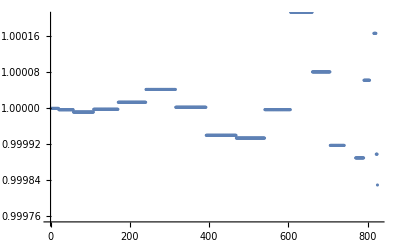

```mathematica
ListPlot[Ptriantab⟦All,3⟧/iPk[triangles⟦All,3⟧]]
```

For our test cosmology we have

```mathematica
subcosmo={f1->0.7775551009423526,nbar->4.5 10^-4,b1->2.,kM->1.}
```

{f1→0.777555,nbar→0.00045,b1→2.,kM→1.}

Set each one of the e_i to 1

```mathematica
SeedRandom[37];
elist=RandomReal[{-2,2},12];
esub=Thread[ecoeff->elist]
```

{e_1→0.813759,e_2→0.938115,e_3→-0.611443,e_4→0.0589839,e_5→-1.61787,e_6→0.358512,e_7→0.898018,e_8→-1.96644,e_9→-0.788943,e_10→0.550199,e_11→-0.814302,e_12→-1.99955}

```mathematica
elist
```

{0.813759,0.938115,-0.611443,0.0589839,-1.61787,0.358512,0.898018,-1.96644,-0.788943,0.550199,-0.814302,-1.99955}

```mathematica
(*esub=Thread[ecoeff->0];
esub⟦12⟧=Subscript[e, 12]->1;
esub*)
```

```mathematica
(*Export["Pk1_check.dat",iPk[k1]/.k1->triangles⟦All,1⟧]*)
```

```mathematica
(*s2p123num=s2p123/.ysub/.subcosmo/.esub/.P11->iPk/.{k1->triangles⟦All,1⟧,k2->triangles⟦All,2⟧,k3->triangles⟦All,3⟧};
s2p231num=s2p231/.ysub/.subcosmo/.esub/.P11->iPk/.{k1->triangles⟦All,1⟧,k2->triangles⟦All,2⟧,k3->triangles⟦All,3⟧};
s2p312num=s2p312/.ysub/.subcosmo/.esub/.P11->iPk/.{k1->triangles⟦All,1⟧,k2->triangles⟦All,2⟧,k3->triangles⟦All,3⟧};*)

s2p123num=Table[s2p123/.ysub/.subcosmo/.esub/.P11[k1]->Ptriantab⟦i,1⟧/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
s2p231num=Table[s2p231/.ysub/.subcosmo/.esub/.P11[k2]->Ptriantab⟦i,2⟧/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
s2p312num=Table[s2p312/.ysub/.subcosmo/.esub/.P11[k3]->Ptriantab⟦i,3⟧/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];

stoch2num=s2p123num+s2p231num+s2p312num;
```

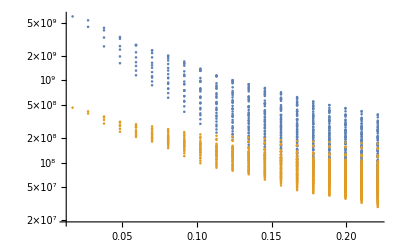

```mathematica
ListLogPlot[{Transpose@{triangles⟦All,1⟧,Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,-stoch2num}},PlotRange->All]
```

```mathematica
Export["Stochastic2_check37.dat",stoch2num];
```

### Check magnitude of stochastic

Import PS. This is different than the interpolation from Python, import that on the triangles too

```mathematica
Pktab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Pktest.dat","Table"];
Ptriantab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Ptriantest.dat","Table"];
iPk=Interpolation[Pktab];
LogLinearPlot[iPk[k],{k,0.001,0.25}]
```

-Graphics-

Import bispectrum to get triangles, order them such that k1 >= k2 >= k3

```mathematica
Btab=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/Bisp_LightConeHector_cmass_ngc_mean.dat","Table"];
Fullcov=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/CovPBresc2_LightConeHector_cmass_ngc.dat","Table"];
triangles=Btab⟦All,3;;1;;-1⟧;
triangles⟦;;10⟧
```

{{0.017221,0.017221,0.017221},{0.027562,0.027562,0.017221},{0.03818,0.03818,0.017221},{0.048836,0.048836,0.017221},{0.059539,0.059539,0.017221},{0.070261,0.070261,0.017221},{0.081,0.081,0.017221},{0.091757,0.091757,0.017221},{0.102501,0.102501,0.017221},{0.11325,0.11325,0.017221}}

```mathematica
bisperr=Sqrt[Diagonal[Fullcov]⟦-Length[triangles];;⟧];
bisperr//Length
```

825

Typical values of cosmology

```mathematica
subcosmo={f1->0.77,nbar->4.5 10^-4,b1->2.,kM->0.7}
```

{f1→0.77,nbar→0.00045,b1→2.,kM→0.7}

```mathematica
fullstoch=Simplify[s2p123+s2p231+s2p312];
fullsttabs=Normal[CoefficientArrays[fullstoch,ecoeff]⟦2⟧]//Simplify;
```

```mathematica
fullsttabs//Dimensions
```

{12}

```mathematica
numtabs=fullsttabs/.ysub/.subcosmo/.P11->iPk/.{k1->triangles⟦All,1⟧,k2->triangles⟦All,2⟧,k3->triangles⟦All,3⟧};
```

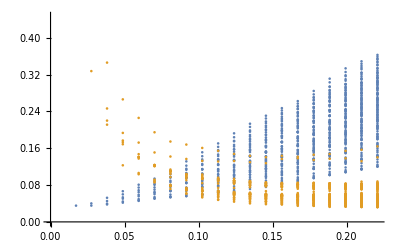

```mathematica
ListPlot[{Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦5⟧/Btab⟦All,4⟧)},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}}]
```

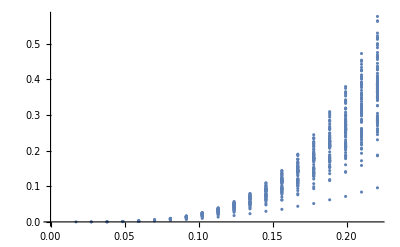

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦2⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧},*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦2⟧/bisperr)}}]
```

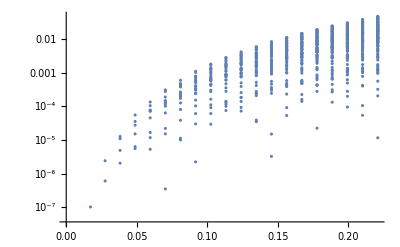

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦3⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧},*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦3⟧/bisperr)}}]
```

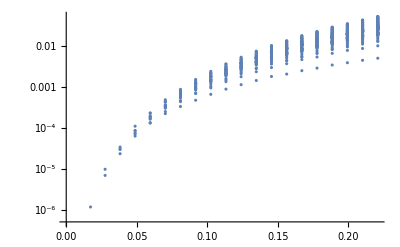

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦4⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦4⟧/bisperr)}}]
```

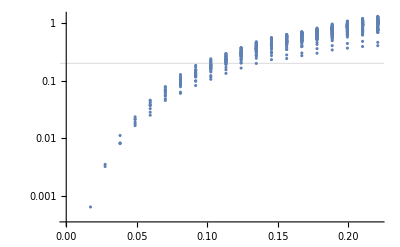

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦6⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦6⟧/bisperr)}},GridLines->{None,{0.2}}]
```

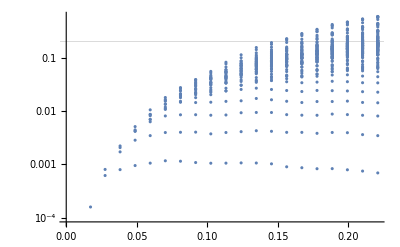

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦7⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦7⟧/bisperr)}},GridLines->{None,{0.2}}]
```

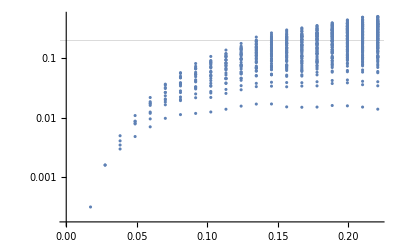

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦8⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦8⟧/bisperr)}},GridLines->{None,{0.2}}]
```

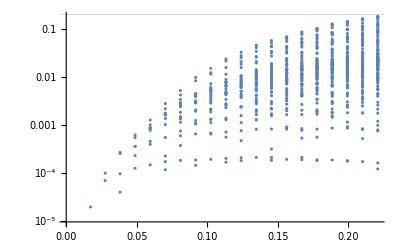

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦9⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦9⟧/bisperr)}},GridLines->{None,{0.2}}]
```

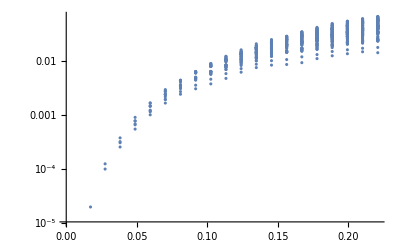

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦10⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦10⟧/bisperr)}},GridLines->{None,{0.2}}]
```

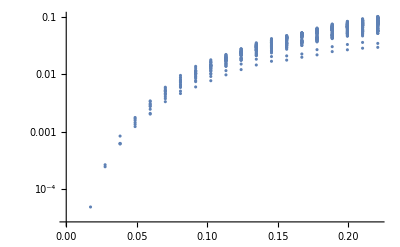

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦11⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦11⟧/bisperr)}},GridLines->{None,{0.2}}]
```

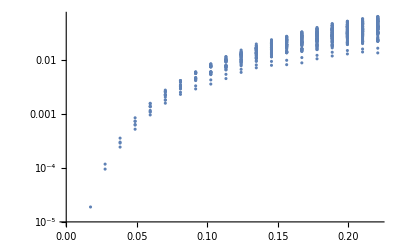

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦12⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦12⟧/bisperr)}},GridLines->{None,{0.2}}]
```

### Counterterms

```mathematica
μlist123big=DeleteCases[Table[μ1^i μ2^j μ3^k,{i,0,7},{j,0,7},{k,0,7}]//Flatten,1];
```

We have two counterterms, the first renormalizes B3212 and the second B411. So they won’t be degenerate. 
Evaluate is important so it correctly replaces the y before permuting the k’s.
VERY IMPORTANT: c1, c2, c3 are the counterterms of P13 (after subtracting up to k^2/q^2 terms, and they appear in both counterterms.
I’m using Matt’s notation, setting knl=1 for now. The factors of f are right to cancel the UV, but a few of the ctr are set to 0, this is the reason why we don’t get the f^3 in mattctr1 for instance

```mathematica
coeffctr={ch[1],cρv[1],cρv2[1],cρv2[3],ch[2],ch[3],ch[4],ch[5],cρv[5],cρv2[2],cρv2[4],cρv2[5],cρv2[6],cρv2[7]}
```

{ch[1],cρv[1],cρv2[1],cρv2[3],ch[2],ch[3],ch[4],ch[5],cρv[5],cρv2[2],cρv2[4],cρv2[5],cρv2[6],cρv2[7]}

```mathematica
Kct1Send[k_,μ_]=((f1 cρv[1] dot[k,hat[z]]^2)/kM^2-(f1^2 cρv2[3] dot[k,hat[z]]^2)/(2 kM^2)-(f1^2 cρv2[1] dot[k,hat[z]]^4)/(2 kM^2 magM[k]^2)-(ch[1] magM[k]^2)/kM^2)/.{dot[k,hat[z]]->k μ,magM[k]->k}//Simplify
```

-(k^2 (2 ch[1]+f1 μ^2 (-2 cρv[1]+f1 (μ^2 cρv2[1]+cρv2[3]))))/(2 kM^2)

```mathematica
P13CTSend[k1_,μ1_]=2 Kct1Send[k1,μ1]K1r[k1]P11[k1]/.tb//Simplify
```

-(k1^2 (b1+f1 μ1^2) (2 ch[1]+f1 μ1^2 (-2 cρv[1]+f1 (μ1^2 cρv2[1]+cρv2[3]))) P11[k1])/kM^2

```mathematica
listctr1=CoefficientArrays[Kct1Send[k1,μ1],coeffctr]
listctr1⟦1⟧+listctr1⟦2⟧.coeffctr-Kct1Send[k1,μ1]//Simplify
```

{0,SparseArray[…]}

0

So rename the 14 coefficients as c_1 through c_14

```mathematica
csub=Thread[coeffctr->(Subscript[c, #]&/@Range[14])]
```

{ch[1]→c_1,cρv[1]→c_2,cρv2[1]→c_3,cρv2[3]→c_4,ch[2]→c_5,ch[3]→c_6,ch[4]→c_7,ch[5]→c_8,cρv[5]→c_9,cρv2[2]→c_10,cρv2[4]→c_11,cρv2[5]→c_12,cρv2[6]→c_13,cρv2[7]→c_14}

```mathematica
Kct1Send[k,μ]//Expand
```

-(k^2 ch[1])/kM^2+(f1 k^2 μ^2 cρv[1])/kM^2-(f1^2 k^2 μ^4 cρv2[1])/(2 kM^2)-(f1^2 k^2 μ^2 cρv2[3])/(2 kM^2)

```mathematica
(*Ctr1p123[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=6 K2r[k1,k2]Plin[k1]Plin[k2](K1r[k2] 1/3(-k1^2 ch[1]+f1 k1^2 μ1^2 cρv[1]-(f1^2 k1^2 μ1^4 cρv2[1])/2-(f1^2 k1^2 μ1^2 cρv2[3])/2)+K1r[k1] 1/3(-k2^2 ch[1]+f1 k2^2 μ2^2 cρv[1]-(f1^2 k2^2 μ2^4 cρv2[1])/2-(f1^2 k2^2 μ2^2 cρv2[3])/2))/.tb/.csub*)
```

This is already symmetrized in k1-k2, needs only 3 cyclic permutations

```mathematica
Ctr1p123[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=6 K2rsym[k1,k2]Plin[k1]Plin[k2](K1r[k2] 1/3(Kct1Send[k1,μ1])+K1r[k1] 1/3(Kct1Send[k2,μ2]))/.tb/.csub
```

```mathematica
(*mattctr2=Simplify[-1/(28 k1 k2 kM^2)(14 k1^4 y ch[1]-2 k1^3 (-2 k2 ((5+9 y^2) ch[2]+7 (ch[3]+y^2 ch[4]))+7 f1 μ3 (k3 μ2 ch[1]-k3 y μ1 cρv[1]+2 k2 y^2 μ3 cρv[5]))+k1^2 (4 k2^2 y ((17+4 y^2) ch[2]+7 (2 ch[3]+ch[5]-f1 μ3^2 cρv[5]+y^2 (2 ch[4]-f1 μ3^2 cρv[5])))+7 f1^2 k3^2 μ3^2 (-2 μ1 μ2 cρv[1]+y μ1^2 (cρv2[1]-cρv2[2])+y (μ3^2 cρv2[2]+cρv2[3])))-7 k2 (-2 k2^3 y ch[1]+2 f1 k2^2 k3 μ3 (μ1 ch[1]-y μ2 cρv[1])+f1^3 k3^3 μ1 μ3^3 (μ2^2 cρv2[1]+cρv2[3])-f1^2 k2 k3^2 μ3^2 (-2 μ1 μ2 cρv[1]+y (μ2^2 (cρv2[1]-cρv2[2])+μ3^2 cρv2[2]+cρv2[3])))+k1 (4 k2^3 ((5+9 y^2) ch[2]+7 (ch[3]+y^2 (ch[4]-f1 μ3^2 cρv[5])))-7 f1^3 k3^3 μ2 μ3^3 (μ1^2 cρv2[1]+cρv2[3])+f1 k2 k3^2 μ3^2 (10 f1 μ3^2 cρv2[2]+4 y^2 (-7 cρv[4]+f1 μ3^2 cρv2[2])+14 f1 y μ1 μ2 cρv2[6]+7 f1 (μ1^2 cρv2[5]+μ2^2 cρv2[5]+2 cρv2[7]))))]/.ysub;*)
```

```mathematica
Kct2Send=-((7 f1^3 (dot[k1,hat[z]]+dot[k2,hat[z]])^3 (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (dot[k2,hat[z]] (cρv2[1] dot[k1,hat[z]]^2+cρv2[3] magM[k1]^2)+dot[k1,hat[z]] (cρv2[1] dot[k2,hat[z]]^2+cρv2[3] magM[k2]^2))+2 (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (4 (2 ch[2]+7 ch[4]) dot[k1,k2]^3+2 (9 ch[2]+7 ch[4]) dot[k1,k2]^2 (magM[k1]^2+magM[k2]^2)+2 (5 ch[2]+7 ch[3]) magM[k1]^2 magM[k2]^2 (magM[k1]^2+magM[k2]^2)+dot[k1,k2] (7 ch[1] magM[k1]^4+2 (17 ch[2]+14 ch[3]+7 ch[5]) magM[k1]^2 magM[k2]^2+7 ch[1] magM[k2]^4))-2 f1 (dot[k1,hat[z]]+dot[k2,hat[z]]) (14 cρv[5] dot[k1,k2] (dot[k1,hat[z]]+dot[k2,hat[z]]) (dot[k1,k2]+magM[k1]^2) (dot[k1,k2]+magM[k2]^2)+7 dot[k1,k2] (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (cρv[1] dot[k1,hat[z]] magM[k1]^2+cρv[1] dot[k2,hat[z]] magM[k2]^2)-7 ch[1] (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (dot[k2,hat[z]] magM[k1]^4+dot[k1,hat[z]] magM[k2]^4))+f1^2 (dot[k1,hat[z]]+dot[k2,hat[z]])^2 (14 cρv2[6] dot[k1,k2] dot[k1,hat[z]] dot[k2,hat[z]] (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)+7 cρv2[1] dot[k1,k2] (dot[k1,hat[z]]^2+dot[k2,hat[z]]^2) (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)-7 cρv2[2] dot[k1,k2] (dot[k1,hat[z]]^2+dot[k2,hat[z]]^2) (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)+14 cρv2[7] magM[k1]^2 magM[k2]^2 (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)+7 cρv2[3] dot[k1,k2] (magM[k1]^2+magM[k2]^2) (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)-7 cρv2[4] dot[k1,k2] (magM[k1]^2+magM[k2]^2) (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)-14 cρv[1] dot[k1,hat[z]] dot[k2,hat[z]] (magM[k1]^2+magM[k2]^2) (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)+7 cρv2[5] (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (dot[k2,hat[z]]^2 magM[k1]^2+dot[k1,hat[z]]^2 magM[k2]^2)+cρv2[2] (dot[k1,hat[z]]+dot[k2,hat[z]])^2 (4 dot[k1,k2]^2+10 magM[k1]^2 magM[k2]^2+7 dot[k1,k2] (magM[k1]^2+magM[k2]^2))+cρv2[4] (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2) (4 dot[k1,k2]^2+10 magM[k1]^2 magM[k2]^2+7 dot[k1,k2] (magM[k1]^2+magM[k2]^2))))/(28 kM^2 magM[k1]^2 magM[k2]^2 (2 dot[k1,k2]+magM[k1]^2+magM[k2]^2)))/.{dot[k1,hat[z]]->k1 μ1,dot[k2,hat[z]]->k2 μ2,dot[hat[k1],hat[k2]]->y,dot[k1,k2]->y k1 k2,magM[k1]->k1,magM[k2]->k2}/.ysub/.{k1 μ1+k2 μ2->-k3 μ3}//Simplify;
```

```mathematica
listctr2=CoefficientArrays[Kct2Send//Expand,coeffctr];
listctr2⟦1⟧+listctr2⟦2⟧.coeffctr-Kct2Send//Simplify
```

0

```mathematica
listctr2
```

{0,SparseArray[…]}

```mathematica
Ctr2p123[k1_,k2_,k3_,μ1_,μ2_,μ3_]=Evaluate[12K1r[k1]K1r[k2]Plin[k1]Plin[k2](1/6 Kct2Send)/.tb/.csub/.ysub]//Simplify
```

1/(28 k1^2 k2^2 kM^2)(b1+f1 μ1^2) (b1+f1 μ2^2) Plin[k1] Plin[k2] (14 f1 k1^5 k3 μ1 μ3 c_2+7 k1^6 (2 c_1-2 c_5+f1 μ3^2 c_9)+k1^4 (28 f1 k2 k3 μ2 μ3 c_1+7 k2^2 (2 c_1-2 c_5+4 c_8-f1 μ3^2 c_9)+k3^2 (-14 c_1+7 f1^2 μ1^2 μ3^2 c_3+7 f1^2 μ3^2 c_4+24 c_5-14 c_7-7 f1 μ3^2 c_9-7 f1^2 μ1^2 μ3^2 c_10+5 f1^2 μ3^4 c_10-2 f1^2 μ3^2 c_11))+(k2^2-k3^2) (14 f1 k2^3 k3 μ2 μ3 c_2+7 k2^4 (2 c_1-2 c_5+f1 μ3^2 c_9)+k2^2 k3^2 (10 c_5-14 c_7+f1^2 μ3^2 (7 c_4+7 μ2^2 (c_3-c_10)+5 μ3^2 c_10-2 c_11))+k3^4 (4 c_5+14 c_7+f1 μ3^2 (-7 c_9+2 f1 (μ3^2 c_10+c_11))))+14 f1 k1^3 k3 μ1 μ3 ((k2^2-k3^2+2 f1 k2 k3 μ2 μ3) c_2+f1 k2 k3 μ2 μ3 c_13)+14 f1 k1 k2 k3 μ1 μ3 (2 k2^3 c_1+f1 k3 μ3 (2 k2^2 μ2 c_2+f1 k2 k3 μ2^2 μ3 c_3+f1 k2 k3 μ3 c_4+k2^2 μ2 c_13-k3^2 μ2 c_13))+k1^2 (14 f1 k2^3 k3 μ2 μ3 c_2+14 f1^3 k2 k3^3 μ2 μ3^3 (μ1^2 c_3+c_4)+7 k2^4 (2 c_1-2 c_5+4 c_8-f1 μ3^2 c_9)-k3^4 (6 c_5-28 c_7+f1 μ3^2 (7 c_9+f1 (7 c_4+7 μ1^2 (c_3-c_10)+3 μ3^2 c_10-4 c_11)))-k2^2 k3^2 (-7 f1^2 (μ1^2+μ2^2) μ3^2 c_3-14 f1^2 μ3^2 c_4+20 c_5+56 c_6+28 c_7+28 c_8-14 f1 μ3^2 c_9+7 f1^2 μ1^2 μ3^2 c_10+7 f1^2 μ2^2 μ3^2 c_10+10 f1^2 μ3^4 c_10+24 f1^2 μ3^2 c_11+14 f1^2 μ1^2 μ3^2 c_12+14 f1^2 μ2^2 μ3^2 c_12+28 f1^2 μ3^2 c_14)))

### First Counterterm - renormalizes B321II

```mathematica
μlist12big=DeleteCases[Table[μ1^i μ2^j,{i,0,7},{j,0,7}]//Flatten,1];
μlist23big=DeleteCases[Table[μ2^i μ3^j,{i,0,7},{j,0,7}]//Flatten,1];
μlist31big=DeleteCases[Table[μ3^i μ1^j,{i,0,7},{j,0,7}]//Flatten,1];
```

```mathematica
ctr1p123=GetMonopole[Ctr1p123[k1,k2,k3,μ1,μ2,μ3],μlist12big]//Simplify;
```

Residual is

0

```mathematica
ctr1p231=GetMonopole[Ctr1p123[k2,k3,k1,μ2,μ3,μ1],μlist23big]//Simplify;
```

Residual is

0

```mathematica
ctr1p312=GetMonopole[Ctr1p123[k3,k1,k2,μ3,μ1,μ2],μlist31big]//Simplify;
```

Residual is

0

Check permutations

```mathematica
(ctr1p123/.ysub/.{k1->k2t,k2->k3t,k3->k1t}/.{k1t->k1,k2t->k2,k3t->k3})-(ctr1p231/.ysub)//Simplify
```

0

```mathematica
(ctr1p123/.ysub/.{k1->k3t,k2->k1t,k3->k2t}/.{k1t->k1,k2t->k2,k3t->k3})-(ctr1p312/.ysub)//Simplify
```

0

```mathematica
Collect[Kct1Send[k1,μ1]/.csub,{k1,μ1}]
```

k1^2 (-c_1/kM^2-(f1^2 μ1^4 c_3)/(2 kM^2)-(μ1^2 (-2 f1 c_2+f1^2 c_4))/(2 kM^2))

```mathematica
FullSimplify[K2rsym[k1,k2]K1r[k2]/.tb/.{k1 μ1+k2 μ2->-k3 μ3}/.k1^2+k2^2-k3^2->2 y k1 k2]/.{k1^4->-(2 k1^2 k2^2+k2^4-2 k1^2 k3^2-2 k2^2 k3^2+k3^4)+4 y^2 k1^2 k2^2}//Simplify
```

-1/(14 k1 k2)(b1+f1 μ2^2) (-14 b5 k1 k2+7 b1 k1^2 y+7 b1 k2^2 y-2 b2 k1 k2 (5+2 y^2)+7 b1 f1 k2 k3 μ1 μ3+7 b1 f1 k1 k3 μ2 μ3-6 f1 k1 k2 μ3^2+7 f1 k1^2 y μ3^2+7 f1 k2^2 y μ3^2-8 f1 k1 k2 y^2 μ3^2-7 f1^2 k3^2 μ1 μ2 μ3^2)

Expand in the EFT parameters

```mathematica
ccoeff1=Coefficient[ctr1p123,{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]}]/.Thread[{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]}->0]//Simplify;
```

```mathematica
ctr1p123-ccoeff1.{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]}//Simplify
```

0

Check for degeneracies. Build the function and run the check. Notice that if we fix the biases, there is one degeneracy fixing f

```mathematica
degtemp=ccoeff1/.{Plin[k1]->1,Plin[k2]->1,kM->1}/.ysub/.Thread[{b1,b2,b5}->RandomInteger[100,3]]//Simplify;
```

```mathematica
eqdegen=degenchreckmono[degtemp]
```

{0,0,0,0}

```mathematica
degenchreckmono[degtemp/.f1->73]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

So there is one degeneracy, which is (f1 c_2 + f1^2c_4/2), but we need all 4 terms since we also have B411
Let’s build a list of EFT parameter combinations to put this into Python.

```mathematica
flist={1,f1,f1^2,f1^3,f1^4,f1^5};
btreelist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
treetemplist=Flatten[Outer[Times,flist,btreelist]];
ctr1blisttemp=Outer[Times,{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]},treetemplist]//Flatten;
```

Take the coefficients, check the non-zero ones and build up the final list. Check it’s complete

```mathematica
coeff1temp=Table[Coefficient[ctr1p123,ctr1blisttemp⟦i⟧],{i,1,Length[ctr1blisttemp]}]/.Thread[{b1,b2,b5,f1,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]}->0]//Simplify;
(ctr1p123-coeff1temp.ctr1blisttemp)//Simplify
```

0

```mathematica
posbias=Complement[Range[Length[ctr1blisttemp]],Position[coeff1temp,0]//Flatten];
ctr1blist=ctr1blisttemp⟦posbias⟧
```

{b1^2 c_1,b1 b2 c_1,b1 b5 c_1,b1^2 f1 c_1,b1 f1 c_1,b2 f1 c_1,b5 f1 c_1,b1 f1^2 c_1,f1^2 c_1,f1^3 c_1,b1^2 f1 c_2,b1 b2 f1 c_2,b1 b5 f1 c_2,b1^2 f1^2 c_2,b1 f1^2 c_2,b2 f1^2 c_2,b5 f1^2 c_2,b1 f1^3 c_2,f1^3 c_2,f1^4 c_2,b1^2 f1^2 c_3,b1 b2 f1^2 c_3,b1 b5 f1^2 c_3,b1^2 f1^3 c_3,b1 f1^3 c_3,b2 f1^3 c_3,b5 f1^3 c_3,b1 f1^4 c_3,f1^4 c_3,f1^5 c_3,b1^2 f1^2 c_4,b1 b2 f1^2 c_4,b1 b5 f1^2 c_4,b1^2 f1^3 c_4,b1 f1^3 c_4,b2 f1^3 c_4,b5 f1^3 c_4,b1 f1^4 c_4,f1^4 c_4,f1^5 c_4}

```mathematica
coeff1p123=Table[Coefficient[ctr1p123/.ysub,ctr1blist⟦i⟧],{i,1,Length[ctr1blist]}]/.Thread[{b1,b2,b5,f1,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4]}->0]//Simplify;
(ctr1p123/.ysub)-coeff1p123.ctr1blist//Simplify
```

0

Check units. Everything scales as k^2 here

```mathematica
coeff1p123/kk^2/.{Plin->Function[x,1]}/.{k3->kk,k2->kk,k1->kk}//Factor//Simplify
```

{2/kM^2,-22/(7 kM^2),-4/kM^2,-2/(3 kM^2),4/(7 kM^2),-22/(21 kM^2),-4/(3 kM^2),-1/(5 kM^2),-1/(35 kM^2),1/(70 kM^2),-2/(3 kM^2),22/(21 kM^2),4/(3 kM^2),1/(5 kM^2),-6/(35 kM^2),11/(35 kM^2),2/(5 kM^2),1/(70 kM^2),1/(245 kM^2),-2/(315 kM^2),1/(5 kM^2),-11/(35 kM^2),-2/(5 kM^2),-2/(35 kM^2),12/(245 kM^2),-22/(245 kM^2),-4/(35 kM^2),1/(630 kM^2),-2/(2205 kM^2),1/(462 kM^2),1/(3 kM^2),-11/(21 kM^2),-2/(3 kM^2),-1/(10 kM^2),3/(35 kM^2),-11/(70 kM^2),-1/(5 kM^2),-1/(140 kM^2),-1/(490 kM^2),1/(315 kM^2)}

Finally, export in Python. Remove the Plin

```mathematica
Clear[c1,c2,c3,c4]
```

```mathematica
FortranForm[ctr1blist/.{Subscript[c, 1]->c1,Subscript[c, 2]->c2,Subscript[c, 3]->c3,Subscript[c, 4]->c4,f1->f}]
```

List(b1**2*c1,b1*b2*c1,b1*b5*c1,b1**2*c1*f,
     -  b1*c1*f,b2*c1*f,b5*c1*f,b1*c1*f**2,c1*f**2,
     -  c1*f**3,b1**2*c2*f,b1*b2*c2*f,b1*b5*c2*f,
     -  b1**2*c2*f**2,b1*c2*f**2,b2*c2*f**2,b5*c2*f**2,
     -  b1*c2*f**3,c2*f**3,c2*f**4,b1**2*c3*f**2,
     -  b1*b2*c3*f**2,b1*b5*c3*f**2,b1**2*c3*f**3,
     -  b1*c3*f**3,b2*c3*f**3,b5*c3*f**3,b1*c3*f**4,
     -  c3*f**4,c3*f**5,b1**2*c4*f**2,b1*b2*c4*f**2,
     -  b1*b5*c4*f**2,b1**2*c4*f**3,b1*c4*f**3,
     -  b2*c4*f**3,b5*c4*f**3,b1*c4*f**4,c4*f**4,
     -  c4*f**5)

```mathematica
For[i=1,i≤Length[coeff1p123],i++,
Print[FortranForm[coeff1p123⟦i⟧/.kM->1/.{Plin->Function[x,1]}//Simplify]]]
```

((k1**2 + k2**2)**2*(k1**2 + k2**2 - k3**2))/(2.*k1**2*k2**2)

-((k1**2 + k2**2)*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(7.*k1**2*k2**2)

-2*(k1**2 + k2**2)

((k1**2 + k2**2)*(k1**4 + k2**4 - k2**2*k3**2 - k1**2*(2*k2**2 + k3**2)))/(6.*k1**2*k2**2)

((k1**2 + k2**2)*(5*k1**4 + 5*k2**4 - 3*k2**2*k3**2 - 2*k3**4 + k1**2*(4*k2**2 - 3*k3**2)))/(21.*k1**2*k2**2)

-((k1**2 + k2**2)*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(21.*k1**2*k2**2)

(-2*(k1**2 + k2**2))/3.

((k1**2 + k2**2)*(k1**4 - 2*k1**2*k2**2 + k2**4 - k3**4))/(10.*k1**2*k2**2)

((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(k1**8 + k2**4*(k2**2 - k3**2)**2 - 2*k1**6*(k2**2 + k3**2) - 2*k1**2*(k2**6 - 2*k2**4*k3**2) + k1**4*(2*k2**4 + 4*k2**2*k3**2 + k3**4)))/(420.*k1**4*k2**4*k3**2)

(k1**10 + k1**8*(k2**2 - 3*k3**2) + k2**4*(k2**2 - k3**2)**3 + k1**6*(-2*k2**4 + 4*k2**2*k3**2 + 3*k3**4) + k1**2*(k2**8 + 4*k2**6*k3**2 - 5*k2**4*k3**4) - k1**4*(2*k2**6 - 6*k2**4*k3**2 + 5*k2**2*k3**4 + k3**6))/(140.*k1**4*k2**4)

-((k1**2 + k2**2)**2*(k1**2 + k2**2 - k3**2))/(6.*k1**2*k2**2)

((k1**2 + k2**2)*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(21.*k1**2*k2**2)

(2*(k1**2 + k2**2))/3.

-((k1**2 + k2**2)*(2*k1**4 + 2*k2**4 - k2**2*k3**2 - k3**4 - k1**2*(4*k2**2 + k3**2)))/(30.*k1**2*k2**2)

-(7*k2**4*k3**2*(k2**2 - k3**2)**3 + k1**10*(6*k2**2 + 7*k3**2) - 3*k1**8*(8*k2**4 - 19*k2**2*k3**2 + 7*k3**4) + k1**6*(36*k2**6 + 104*k2**4*k3**2 - 98*k2**2*k3**4 + 21*k3**6) + k1**2*k2**2*(6*k2**8 + 57*k2**6*k3**2 - 98*k2**4*k3**4 + 57*k2**2*k3**6 - 22*k3**8) + k1**4*(-24*k2**8 + 104*k2**6*k3**2 - 146*k2**4*k3**4 + 57*k2**2*k3**6 - 7*k3**8))/(420.*k1**4*k2**4*k3**2)

((k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2))*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(105.*k1**2*k2**2)

(2*(k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2)))/15.

(-k1**10 - k2**4*(k2**2 - k3**2)**3 + k1**8*(-7*k2**2 + 3*k3**2) + k1**6*(8*k2**4 + 2*k2**2*k3**2 - 3*k3**4) + k1**4*(8*k2**6 - 10*k2**4*k3**2 + k2**2*k3**4 + k3**6) + k1**2*(-7*k2**8 + 2*k2**6*k3**2 + k2**4*k3**4 + 4*k2**2*k3**6))/(140.*k1**4*k2**4)

-((k1**2 + k2**2)*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4)))/(980.*k1**4*k2**4*k3**2)

-((k1**2 + k2**2)*(3*k1**8 + k1**6*(3*k2**2 - 7*k3**2) + (k2**2 - k3**2)**3*(3*k2**2 + 2*k3**2) + 3*k1**4*(-4*k2**4 + 4*k2**2*k3**2 + k3**4) + 3*k1**2*(k2**6 + 4*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(630.*k1**4*k2**4)

((k1**2 + k2**2)**2*(k1**2 + k2**2 - k3**2))/(20.*k1**2*k2**2)

-((k1**2 + k2**2)*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(70.*k1**2*k2**2)

(-k1**2 - k2**2)/5.

((k1**2 + k2**2)*(3*k1**4 + 3*k2**4 - k2**2*k3**2 - 2*k3**4 - k1**2*(6*k2**2 + k3**2)))/(140.*k1**2*k2**2)

(7*k2**4*k3**2*(k2**2 - k3**2)**3 + k1**10*(6*k2**2 + 7*k3**2) + k1**8*(-24*k2**4 + 47*k2**2*k3**2 - 21*k3**4) + k1**6*(36*k2**6 + 86*k2**4*k3**2 - 92*k2**2*k3**4 + 21*k3**6) + k1**2*k2**2*(6*k2**8 + 47*k2**6*k3**2 - 92*k2**4*k3**4 + 61*k2**2*k3**6 - 22*k3**8) + k1**4*(-24*k2**8 + 86*k2**6*k3**2 - 134*k2**4*k3**4 + 61*k2**2*k3**6 - 7*k3**8))/(980.*k1**4*k2**4*k3**2)

-((k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(k1**2*k2**2))*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(490.*k1**2*k2**2)

-((k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(k1**2*k2**2)))/35.

(4*k1**10 + k1**8*(23*k2**2 - 11*k3**2) + k2**2*(k2**2 - k3**2)**3*(4*k2**2 + k3**2) + k1**6*(-27*k2**4 - 10*k2**2*k3**2 + 9*k3**4) - k1**4*(27*k2**6 - 42*k2**4*k3**2 + k3**6) + k1**2*(23*k2**8 - 10*k2**6*k3**2 - 12*k2**2*k3**6 - k3**8))/(1260.*k1**4*k2**4)

((3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(7*k1**8 + 2*k1**6*(k2**2 - 4*k3**2) - 3*k1**4*(6*k2**4 - 6*k2**2*k3**2 + k3**4) + (k2**2 - k3**2)**2*(7*k2**4 + 6*k2**2*k3**2 + 2*k3**4) + 2*k1**2*(k2**6 + 9*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(17640.*k1**4*k2**4*k3**2)

(11*k1**10 + k1**8*(23*k2**2 - 25*k3**2) + (k2**2 - k3**2)**3*(11*k2**4 + 8*k2**2*k3**2 + 2*k3**4) + k1**6*(-34*k2**4 + 8*k2**2*k3**2 + 11*k3**4) + k1**4*(-34*k2**6 + 90*k2**4*k3**2 - 45*k2**2*k3**4 + 7*k3**6) + k1**2*(23*k2**8 + 8*k2**6*k3**2 - 45*k2**4*k3**4 + 16*k2**2*k3**6 - 2*k3**8))/(5544.*k1**4*k2**4)

((k1**2 + k2**2)**2*(k1**2 + k2**2 - k3**2))/(12.*k1**2*k2**2)

-((k1**2 + k2**2)*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(42.*k1**2*k2**2)

(-k1**2 - k2**2)/3.

((k1**2 + k2**2)*(2*k1**4 + 2*k2**4 - k2**2*k3**2 - k3**4 - k1**2*(4*k2**2 + k3**2)))/(60.*k1**2*k2**2)

(7*k2**4*k3**2*(k2**2 - k3**2)**3 + k1**10*(6*k2**2 + 7*k3**2) - 3*k1**8*(8*k2**4 - 19*k2**2*k3**2 + 7*k3**4) + k1**6*(36*k2**6 + 104*k2**4*k3**2 - 98*k2**2*k3**4 + 21*k3**6) + k1**2*k2**2*(6*k2**8 + 57*k2**6*k3**2 - 98*k2**4*k3**4 + 57*k2**2*k3**6 - 22*k3**8) + k1**4*(-24*k2**8 + 104*k2**6*k3**2 - 146*k2**4*k3**4 + 57*k2**2*k3**6 - 7*k3**8))/(840.*k1**4*k2**4*k3**2)

-((k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2))*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(210.*k1**2*k2**2)

-((k1**2 + k2**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2)))/15.

(k1**10 + k1**8*(7*k2**2 - 3*k3**2) + k2**4*(k2**2 - k3**2)**3 + k1**6*(-8*k2**4 - 2*k2**2*k3**2 + 3*k3**4) - k1**4*(8*k2**6 - 10*k2**4*k3**2 + k2**2*k3**4 + k3**6) + k1**2*(7*k2**8 - 2*k2**6*k3**2 - k2**4*k3**4 - 4*k2**2*k3**6))/(280.*k1**4*k2**4)

((k1**2 + k2**2)*(3*k1**4 + 3*k2**4 + k2**2*k3**2 - 4*k3**4 + k1**2*(-6*k2**2 + k3**2))*(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4)))/(1960.*k1**4*k2**4*k3**2)

((k1**2 + k2**2)*(3*k1**8 + k1**6*(3*k2**2 - 7*k3**2) + (k2**2 - k3**2)**3*(3*k2**2 + 2*k3**2) + 3*k1**4*(-4*k2**4 + 4*k2**2*k3**2 + k3**4) + 3*k1**2*(k2**6 + 4*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(1260.*k1**4*k2**4)

### Second Counterterm - Renormalizes B411

```mathematica
μlist123=DeleteCases[Table[μ1^i μ2^j μ3^k,{i,0,4},{j,0,4},{k,0,4}]//Flatten,1];
```

Here we should also subtract the terms coming from <δ(2)>

```mathematica
ctr2p123=GetMonopole[Ctr2p123[k1,k2,k3,μ1,μ2,μ3],μlist123]//Simplify;
```

Residual is

0

```mathematica
ctr2p231=GetMonopole[Ctr2p123[k2,k3,k1,μ2,μ3,μ1],μlist123]//Simplify;
```

Residual is

0

```mathematica
ctr2p312=GetMonopole[Ctr2p123[k3,k1,k2,μ3,μ1,μ2],μlist123]//Simplify;
```

Residual is

0

Check permutations. The y here is always k1.k2/k1k2, because it comes from the monopole integration. In the counterterm, we have to substitute the y so it correctly gets permuted

```mathematica
(ctr2p123/.ysub/.{k1->k2t,k2->k3t,k3->k1t}/.{k1t->k1,k2t->k2,k3t->k3})-(ctr2p231/.ysub)//Simplify
```

0

```mathematica
(ctr2p123/.ysub/.{k1->k3t,k2->k1t,k3->k2t}/.{k1t->k1,k2t->k2,k3t->k3})-(ctr2p312/.ysub)//Simplify
```

0

Expand in the EFT parameters

```mathematica
cbias=Subscript[c, #]&/@Range[1,14];
```

```mathematica
ccoeff2=Coefficient[ctr2p123,cbias]//Simplify;
```

```mathematica
ctr2p123-ccoeff2.cbias//Simplify
```

0

Check for degeneracies. Build the function and run the check, fixing f1. For different b1 these are non-degenerate, but 4 degeneracies when we fix b1!

```mathematica
degtemp=ccoeff2/.{Plin[k1]->1,Plin[k2]->1,kM->1}/.ysub//Simplify;
```

```mathematica
eqdegen=degenchreckmono[degtemp]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
eqdegen=degenchreckmono[degtemp/.{b1->21/10,f1->5/6}]//N
```

{K_1+23.4334 K_3-22.1594 K_4+0.868551 K_7-1. K_8-176.404 K_11+0.413688 K_12+75.2387 K_13+132.473 K_14,K_2+2.4 K_4+0.00728851 K_7+7.08016 K_11-3.17981 K_12-4.66173 K_13-4.57676 K_14,0.,0.,K_5-0.203483 K_7+K_8+85.3812 K_11+19.4245 K_12-56.1313 K_13-74.8097 K_14,K_6+0.00978261 K_7-13.7632 K_11-3.01062 K_12+8.69983 K_13+2.77989 K_14,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
eqdegen=degenchreckmono[degtemp/.{b1->2,f1->5/6}]//N
```

{K_1+23.3369 K_3-22.09 K_4+0.861923 K_7-1. K_8-181.175 K_11-3.03784 K_12+78.5091 K_13+137.271 K_14,K_2+2.4 K_4+0.00762496 K_7+7.44191 K_11-2.93856 K_12-4.89937 K_13-4.93314 K_14,0.,0.,K_5-0.199425 K_7+K_8+89.2117 K_11+22.1749 K_12-58.655 K_13-78.6621 K_14,K_6+0.010607 K_7-15.087 K_11-3.60606 K_12+9.53841 K_13+3.98332 K_14,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
1/181.17469447139763(Subscript[K, 1]+23.336875456124783 Subscript[K, 3]-22.08998484079981 Subscript[K, 4]+0.8619233057162862 Subscript[K, 7]-1. Subscript[K, 8]-181.17469447139763 Subscript[K, 11]-3.0378355035067717 Subscript[K, 12]+78.50914000806223 Subscript[K, 13]+137.27107627025234 Subscript[K, 14])//Expand
```

0.00551953 K_1+0.128809 K_3-0.121926 K_4+0.00475742 K_7-0.00551953 K_8-1. K_11-0.0167674 K_12+0.433334 K_13+0.757672 K_14

Let’s build a list of EFT parameter combinations to put this into Python.
Put the linear biases before so it’s easier to marginalize

```mathematica
clist=Subscript[c, #]&/@Range[1,14];
```

```mathematica
flist={1,f1,f1^2,f1^3,f1^4,f1^5};
btreelist=Outer[Times,{b1^3,b1^2,b1,1},{1,b2,b5}]//Flatten;
treetemplist=Flatten[Outer[Times,flist,btreelist]];
ctr2blisttemp=Outer[Times,clist,treetemplist]//Flatten;
```

```mathematica
coeff2temp=Table[Coefficient[ctr2p123/.ysub,ctr2blisttemp⟦i⟧],{i,1,Length[ctr2blisttemp]}]/.Thread[Flatten@{b1,f1,clist}->0]//Simplify;
(ctr2p123/.ysub)-coeff2temp.ctr2blisttemp//Simplify
```

0

```mathematica
posbias=Complement[Range[Length[ctr2blisttemp]],Position[coeff2temp,0]//Flatten];
ctr2blist=ctr2blisttemp⟦posbias⟧
```

{b1^2 c_1,b1^2 f1 c_1,b1 f1 c_1,b1 f1^2 c_1,f1^2 c_1,f1^3 c_1,b1^2 f1 c_2,b1^2 f1^2 c_2,b1 f1^2 c_2,b1 f1^3 c_2,f1^3 c_2,f1^4 c_2,b1^2 f1^2 c_3,b1^2 f1^3 c_3,b1 f1^3 c_3,b1 f1^4 c_3,f1^4 c_3,f1^5 c_3,b1^2 f1^2 c_4,b1^2 f1^3 c_4,b1 f1^3 c_4,b1 f1^4 c_4,f1^4 c_4,f1^5 c_4,b1^2 c_5,b1 f1 c_5,f1^2 c_5,b1^2 c_6,b1 f1 c_6,f1^2 c_6,b1^2 c_7,b1 f1 c_7,f1^2 c_7,b1^2 c_8,b1 f1 c_8,f1^2 c_8,b1^2 f1 c_9,b1 f1^2 c_9,f1^3 c_9,b1^2 f1^2 c_10,b1 f1^3 c_10,f1^4 c_10,b1^2 f1^2 c_11,b1 f1^3 c_11,f1^4 c_11,b1^2 f1^2 c_12,b1 f1^3 c_12,f1^4 c_12,b1^2 f1^2 c_13,b1 f1^3 c_13,f1^4 c_13,b1^2 f1^2 c_14,b1 f1^3 c_14,f1^4 c_14}

```mathematica
{Length[ctr2blisttemp],Length[ctr2blist]}
```

{1008,54}

```mathematica
coeff2p123=Table[Coefficient[ctr2p123/.ysub,ctr2blist⟦i⟧],{i,1,Length[ctr2blist]}]/.Thread[Flatten@{b1,f1,dlist}->0]//Simplify;
(ctr2p123/.ysub)-coeff2p123.ctr2blist//Simplify
```

0

Check units. Everything scales as k^2 here

```mathematica
coeff2p123/kk^2/.{Plin->Function[x,1]}/.{k3->7 kk,k2->5 kk,k1->3 kk,kM->1}//Factor
```

{-353/15,-863/45,-706/45,-1471/75,-353/150,-4511/1050,961/90,1088/75,523/50,8993/525,4609/2100,850/189,-1441/300,-469/60,-11077/2100,-18259/1890,-233/189,-3104/1155,-833/90,-2303/150,-459/50,-9214/525,-4097/2100,-4147/945,-109,-218/3,-109/10,-98,-196/3,-49/5,-49/2,-49/3,-49/20,-15,-10,-3/2,143/12,11583/980,34463/13720,-169/20,-9523/980,-52975/21609,-77/6,-891/70,-2651/980,-81/10,-629/70,-674/315,-16/5,-529/140,-125/126,-49/3,-81/5,-241/70}

Finally, export in Python. Remove the Plin

```mathematica
Clear[c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14]
```

```mathematica
FortranForm[ctr2blist/.Thread[clist->{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14}]/.f1->f]
```

List(b1**2*c1,b1**2*c1*f,b1*c1*f,b1*c1*f**2,c1*f**2,c1*f**3,b1**2*c2*f,b1**2*c2*f**2,b1*c2*f**2,
     -  b1*c2*f**3,c2*f**3,c2*f**4,b1**2*c3*f**2,b1**2*c3*f**3,b1*c3*f**3,b1*c3*f**4,c3*f**4,c3*f**5,
     -  b1**2*c4*f**2,b1**2*c4*f**3,b1*c4*f**3,b1*c4*f**4,c4*f**4,c4*f**5,b1**2*c5,b1*c5*f,c5*f**2,
     -  b1**2*c6,b1*c6*f,c6*f**2,b1**2*c7,b1*c7*f,c7*f**2,b1**2*c8,b1*c8*f,c8*f**2,b1**2*c9*f,b1*c9*f**2,
     -  c9*f**3,b1**2*c10*f**2,b1*c10*f**3,c10*f**4,b1**2*c11*f**2,b1*c11*f**3,c11*f**4,b1**2*c12*f**2,
     -  b1*c12*f**3,c12*f**4,b1**2*c13*f**2,b1*c13*f**3,c13*f**4,b1**2*c14*f**2,b1*c14*f**3,c14*f**4)

```mathematica
For[i=1,i≤Length[coeff2p123],i++,
Print[FortranForm[coeff2p123⟦i⟧/.kM->1/.{Plin->Function[x,1]}//Simplify]]]
```

((k1**4 + k2**4)*(k1**2 + k2**2 - k3**2))/(2.*k1**2*k2**2)

(k1**6 - k1**2*k2**4 + k2**6 - k2**4*k3**2 - k1**4*(k2**2 + k3**2))/(6.*k1**2*k2**2)

((k1**4 + k2**4)*(k1**2 + k2**2 - k3**2))/(3.*k1**2*k2**2)

-(-5*k1**6 - 5*k2**6 + 4*k2**4*k3**2 + k2**2*k3**4 + k1**4*(5*k2**2 + 4*k3**2) + k1**2*(5*k2**4 - 4*k2**2*k3**2 + k3**4))/(30.*k1**2*k2**2)

((k1**4 + k2**4)*(k1**2 + k2**2 - k3**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2)))/(30.*k1**2*k2**2)

(k1**10 + k1**8*(5*k2**2 - 3*k3**2) + k2**4*(k2**2 - k3**2)**3 + k1**6*(-6*k2**4 - 4*k2**2*k3**2 + 3*k3**4) + k1**2*(5*k2**8 - 4*k2**6*k3**2 - k2**4*k3**4) - k1**4*(6*k2**6 - 10*k2**4*k3**2 + k2**2*k3**4 + k3**6))/(140.*k1**4*k2**4)

-((k1**2 + k2**2 - k3**2)*(k1**4 + k1**2*(-2*k2**2 + k3**2) + k2**2*(k2**2 + k3**2)))/(12.*k1**2*k2**2)

-((k1**2 + k2**2)*(k1**4 + k2**4 + k2**2*k3**2 - 2*k3**4 + k1**2*(-2*k2**2 + k3**2)))/(30.*k1**2*k2**2)

-((k1**2 + k2**2 - k3**2)*(k1**8 + k1**6*(4*k2**2 - 2*k3**2) + k2**4*(k2**2 - k3**2)**2 + 4*k1**2*k2**4*(k2**2 + k3**2) + k1**4*(-10*k2**4 + 4*k2**2*k3**2 + k3**4)))/(60.*k1**4*k2**4)

-((k1**2 + k2**2)*(k1**8 + k1**6*(4*k2**2 - 3*k3**2) + k2**2*(k2**2 - k3**2)**3 + k1**4*(-10*k2**4 + 7*k2**2*k3**2 + 3*k3**4) + k1**2*(4*k2**6 + 7*k2**4*k3**2 - 10*k2**2*k3**4 - k3**6)))/(140.*k1**4*k2**4)

-((k1**2 + k2**2 - k3**2)*(3*k1**8 + k1**6*(2*k2**2 - 5*k3**2) + (3*k2**2 + k3**2)*(k2**3 - k2*k3**2)**2 + k1**4*(-10*k2**4 + 7*k2**2*k3**2 + k3**4) + k1**2*(2*k2**6 + 7*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(280.*k1**4*k2**4)

-((k1**2 + k2**2)*(3*k1**8 + k1**6*(3*k2**2 - 7*k3**2) + (k2**2 - k3**2)**3*(3*k2**2 + 2*k3**2) + 3*k1**4*(-4*k2**4 + 4*k2**2*k3**2 + k3**4) + 3*k1**2*(k2**6 + 4*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(630.*k1**4*k2**4)

(k1**6 - k1**4*k2**2 + k2**6 - k3**6 - k1**2*(k2**4 - 4*k2**2*k3**2))/(60.*k1**2*k2**2)

(k3**2*(2*k1**4 + 2*k2**4 + k2**2*k3**2 - 3*k3**4 + k1**2*(-4*k2**2 + k3**2)))/(140.*k1**2*k2**2)

(k1**10 - 6*k1**6*k2**4 + k1**8*(5*k2**2 - 2*k3**2) + k2**2*(k2**2 - k3**2)**3*(k2**2 + k3**2) + k1**4*(-6*k2**6 + 20*k2**4*k3**2 - 4*k2**2*k3**4 + 2*k3**6) + k1**2*(5*k2**8 - 4*k2**4*k3**4 - k3**8))/(280.*k1**4*k2**4)

(k1**10 + k1**8*(-3*k2**2 + k3**2) + k2**2*(k2**2 - k3**2)**3*(k2**2 + 4*k3**2) + k1**6*(2*k2**4 + 20*k2**2*k3**2 - 9*k3**4) + k1**4*(2*k2**6 - 42*k2**4*k3**2 + 15*k2**2*k3**4 + 11*k3**6) + k1**2*(-3*k2**8 + 20*k2**6*k3**2 + 15*k2**4*k3**4 - 28*k2**2*k3**6 - 4*k3**8))/(1260.*k1**4*k2**4)

((k1**2 + k2**2 - k3**2)*(7*k1**8 + 2*k1**6*(k2**2 - 4*k3**2) - 3*k1**4*(6*k2**4 - 6*k2**2*k3**2 + k3**4) + (k2**2 - k3**2)**2*(7*k2**4 + 6*k2**2*k3**2 + 2*k3**4) + 2*k1**2*(k2**6 + 9*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(2520.*k1**4*k2**4)

(k1**10 + k1**8*(-3*k2**2 + k3**2) + k1**6*(2*k2**4 + 8*k2**2*k3**2 - 7*k3**4) + (k2**2 - k3**2)**3*(k2**4 + 4*k2**2*k3**2 + 2*k3**4) + k1**4*(2*k2**6 - 18*k2**4*k3**2 + 9*k2**2*k3**4 + 5*k3**6) + k1**2*(-3*k2**8 + 8*k2**6*k3**2 + 9*k2**4*k3**4 - 16*k2**2*k3**6 + 2*k3**8))/(1848.*k1**4*k2**4)

((k1**2 + k2**2)*k3**2*(k1**2 + k2**2 - k3**2))/(12.*k1**2*k2**2)

(k3**2*(k1**4 + k2**4 - k2**2*k3**2 - k1**2*(2*k2**2 + k3**2)))/(20.*k1**2*k2**2)

((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*(k1**6 - k1**4*(k2**2 + 2*k3**2) + (k2**3 - k2*k3**2)**2 + k1**2*(-k2**4 + 8*k2**2*k3**2 + k3**4)))/(120.*k1**4*k2**4)

(k1**10 + k2**4*(k2**2 - k3**2)**3 - 3*k1**8*(k2**2 + k3**2) + k1**6*(2*k2**4 + 16*k2**2*k3**2 + 3*k3**4) + k1**4*(2*k2**6 - 26*k2**4*k3**2 - 7*k2**2*k3**4 - k3**6) - k1**2*(3*k2**8 - 16*k2**6*k3**2 + 7*k2**4*k3**4 + 6*k2**2*k3**6))/(280.*k1**4*k2**4)

((k1**2 + k2**2)*(k1**2 + k2**2 - k3**2)*(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4)))/(280.*k1**4*k2**4)

(2*k1**10 - 3*k1**8*(2*k2**2 + k3**2) + k2**2*(k2**2 - k3**2)**3*(2*k2**2 + 3*k3**2) + k1**6*(4*k2**4 + 15*k2**2*k3**2 - 3*k3**4) + k1**4*(4*k2**6 - 24*k2**4*k3**2 + 7*k3**6) - 3*k1**2*(2*k2**8 - 5*k2**6*k3**2 + 2*k2**2*k3**6 + k3**8))/(1260.*k1**4*k2**4)

-(7*k1**6 + k1**4*(7*k2**2 - 12*k3**2) + (k2**2 - k3**2)**2*(7*k2**2 + 2*k3**2) + k1**2*(7*k2**4 + 10*k2**2*k3**2 + 3*k3**4))/(14.*k1**2*k2**2)

-(7*k1**6 + k1**4*(7*k2**2 - 12*k3**2) + (k2**2 - k3**2)**2*(7*k2**2 + 2*k3**2) + k1**2*(7*k2**4 + 10*k2**2*k3**2 + 3*k3**4))/(21.*k1**2*k2**2)

-((1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2))*(7*k1**6 + k1**4*(7*k2**2 - 12*k3**2) + (k2**2 - k3**2)**2*(7*k2**2 + 2*k3**2) + k1**2*(7*k2**4 + 10*k2**2*k3**2 + 3*k3**4)))/(210.*k1**2*k2**2)

-2*k3**2

(-4*k3**2)/3.

(-2*k3**2*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2)))/15.

-(k3**2*(k1**2 + k2**2 - k3**2)**2)/(2.*k1**2*k2**2)

-(k3**2*(k1**2 + k2**2 - k3**2)**2)/(3.*k1**2*k2**2)

-(k3**2*(k1**2 + k2**2 - k3**2)**2*(k1**4 + k1**2*(4*k2**2 - 2*k3**2) + (k2**2 - k3**2)**2))/(60.*k1**4*k2**4)

k1**2 + k2**2 - k3**2

(2*(k1**2 + k2**2 - k3**2))/3.

((k1**2 + k2**2 - k3**2)*(1 + (k1**2 + k2**2 - k3**2)**2/(2.*k1**2*k2**2)))/15.

(k1**6 - k1**2*(k2**2 - k3**2)**2 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2))/(12.*k1**2*k2**2)

((k1**6 - k1**2*(k2**2 - k3**2)**2 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2))*(k1**6 - k1**4*(k2**2 + 2*k3**2) + (k2**3 - k2*k3**2)**2 + k1**2*(-k2**4 + 8*k2**2*k3**2 + k3**4)))/(120.*k1**4*k2**4*k3**2)

((k1**6 - k1**2*(k2**2 - k3**2)**2 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2))*(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4)))/(280.*k1**4*k2**4*k3**2)

-(7*k1**6 + (k2**2 - k3**2)**2*(7*k2**2 - k3**2) - k1**4*(7*k2**2 + 15*k3**2) + k1**2*(-7*k2**4 + 58*k2**2*k3**2 + 9*k3**4))/(420.*k1**2*k2**2)

(3*k1**10 + 3*k2**2*(k2**2 - k3**2)**4 - k1**8*(65*k2**2 + 12*k3**2) - k1**2*(k2**2 - k3**2)**2*(65*k2**4 + 30*k2**2*k3**2 - 3*k3**4) + 2*k1**6*(31*k2**4 + 50*k2**2*k3**2 + 9*k3**4) + 2*k1**4*(31*k2**6 - 144*k2**4*k3**2 - k2**2*k3**4 - 6*k3**6))/(1960.*k1**4*k2**4)

(5*k1**12 - 2*k1**10*(15*k2**2 + 11*k3**2) + (k2**2 - k3**2)**4*(5*k2**4 - 2*k2**2*k3**2 + 2*k3**4) + k1**8*(75*k2**4 - 144*k2**2*k3**2 + 40*k3**4) - 2*k1**2*(k2**2 - k3**2)**2*(15*k2**6 + 102*k2**4*k3**2 + 108*k2**2*k3**4 + 5*k3**6) - 2*k1**6*(50*k2**6 - 83*k2**4*k3**2 - 81*k2**2*k3**4 + 20*k3**6) + k1**4*(75*k2**8 + 166*k2**6*k3**2 - 684*k2**4*k3**4 + 218*k2**2*k3**6 + 25*k3**8))/(17640.*k1**4*k2**4*k3**2)

-(k3**2*(k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2)))/(42.*k1**2*k2**2)

-((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(k1**6 - k1**4*(k2**2 + 2*k3**2) + (k2**3 - k2*k3**2)**2 + k1**2*(-k2**4 + 8*k2**2*k3**2 + k3**4)))/(420.*k1**4*k2**4)

-((k1**4 + (k2**2 - k3**2)**2 + 2*k1**2*(6*k2**2 - k3**2))*(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4)))/(980.*k1**4*k2**4)

-(k1**6 - k1**4*(k2**2 + 2*k3**2) + (k2**3 - k2*k3**2)**2 + k1**2*(-k2**4 + 8*k2**2*k3**2 + k3**4))/(60.*k1**2*k2**2)

-(2*k1**6 + 2*k2**6 - 3*k2**4*k3**2 + k3**6 - k1**4*(2*k2**2 + 3*k3**2) - 2*k1**2*(k2**4 - 5*k2**2*k3**2))/(70.*k1**2*k2**2)

-(k1**10 + k2**2*(k2**2 - k3**2)**4 + 4*k1**8*(3*k2**2 - k3**2) + k1**2*(k2**2 - k3**2)**2*(12*k2**4 + 14*k2**2*k3**2 + k3**4) + k1**6*(-13*k2**4 - 10*k2**2*k3**2 + 6*k3**4) - k1**4*(13*k2**6 - 48*k2**4*k3**2 + 15*k2**2*k3**4 + 4*k3**6))/(1260.*k1**4*k2**4)

-((k1**2 + k2**2 - k3**2)*(k1**4 + k2**4 + k2**2*k3**2 - 2*k3**4 + k1**2*(-2*k2**2 + k3**2)))/(60.*k1**2*k2**2)

-((k1**2 + k2**2 - k3**2)*(k1**8 + k1**6*(4*k2**2 - 3*k3**2) + k2**2*(k2**2 - k3**2)**3 + k1**4*(-10*k2**4 + 7*k2**2*k3**2 + 3*k3**4) + k1**2*(4*k2**6 + 7*k2**4*k3**2 - 10*k2**2*k3**4 - k3**6)))/(280.*k1**4*k2**4)

-((k1**2 + k2**2 - k3**2)*(3*k1**8 + k1**6*(3*k2**2 - 7*k3**2) + (k2**2 - k3**2)**3*(3*k2**2 + 2*k3**2) + 3*k1**4*(-4*k2**4 + 4*k2**2*k3**2 + k3**4) + 3*k1**2*(k2**6 + 4*k2**4*k3**2 - 6*k2**2*k3**4 + k3**6)))/(1260.*k1**4*k2**4)

-k3**2/3.

-(k1**6 - k1**4*(k2**2 + 2*k3**2) + (k2**3 - k2*k3**2)**2 + k1**2*(-k2**4 + 8*k2**2*k3**2 + k3**4))/(30.*k1**2*k2**2)

-(k1**6 - k1**4*(k2**2 + k3**2) + (k2**2 - k3**2)**2*(k2**2 + k3**2) - k1**2*(k2**4 - 4*k2**2*k3**2 + k3**4))/(70.*k1**2*k2**2)

### Both counterterms together, for degeneracies

```mathematica
fullctrp123=ctr1p123+ctr2p123//Simplify;
```

Expand in the EFT parameters, and check

```mathematica
cbias=Subscript[c, #]&/@Range[1,14];
```

```mathematica
fullccoeff=Coefficient[fullctrp123,cbias]//Simplify;
```

```mathematica
fullctrp123-fullccoeff.cbias//Simplify
```

0

```mathematica
D[fullctrp123,Subscript[c, 11]]/.ysub//FullSimplify
```

-1/(2940 k1^4 k2^4 kM^2)f1^2 (k1^4+12 k1^2 k2^2+k2^4-2 (k1^2+k2^2) k3^2+k3^4) (f1 (7 b1+3 f1) (k1^2-k2^2)^2 (k1^2+k2^2)+(-f1 (14 b1+3 f1) k1^4+2 (35 b1^2+28 b1 f1+6 f1^2) k1^2 k2^2-f1 (14 b1+3 f1) k2^4) k3^2+(7 b1-3 f1) f1 (k1^2+k2^2) k3^4+3 f1^2 k3^6) Plin[k1] Plin[k2]

Check for degeneracies. Build the function and run the check.

```mathematica
eqdegen=degenchreckmono[degtemp]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Now fix b1, f1 and do the check again

```mathematica
eqdegen=degenchreckmono[degtemp/.{b1->2,b2->7/3,b5->0.2,f1->5/6}]
```

{K_1+(5595512616 K_3)/239771285-(896338224 K_4)/40576679+(190313072533572145 K_7)/220800471772155912-K_8-(56750937458153728034 K_11)/313238764518038645-(3806271359709980211 K_12)/1252955058072154580+(98368424077996525371 K_13)/1252955058072154580+(644979335024329461593 K_14)/4698581467770579675,K_2+(12 K_4)/5+(456408325 K_7)/59857170408+(883832705 K_11)/118764227-(1395981331 K_12)/475056908-(2327481669 K_13)/475056908-(1757640716 K_14)/356292681,0,0,K_5-(165792189 K_7)/831349589+K_8+(52975769028 K_11)/593821135+(13167932724 K_12)/593821135-(6966120636 K_13)/118764227-(233556053556 K_14)/2969105675,K_6+(3779200 K_7)/356292681-(1791796720 K_11)/118764227-(2141353368 K_12)/593821135+(1132822152 K_13)/118764227+(11826890488 K_14)/2969105675,0,0,0,0,0,0,0,0}

So we can keep just K1, K3, K7, K8, K9, K10, K11, K12, K13, K14.
Now, c1 = -cct for the PS, cr1 is a combination of Bc2 and Bc4, cr2 is related to Bc3. So we can choose 2 among Bc1, Bc2, Bc3, c4. Or keep all them, and remove the last 4. Let’s try to remove Bc4 so it’s easier for the PS.

```mathematica
eqdegen=degenchreckmono[degtemp⟦{3,4,7,8,9,10,11,12,13,14}⟧/.Thread[{b1,b2,b5,f1}->RandomInteger[100,4]]]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
eqdegen=degenchreckmono[degtemp⟦{1,2,3,5,6,7,8,9,10,11}⟧/.Thread[{b1,b2,b5,f1}->RandomInteger[100,4]]]
```

{0,0,0,0,0,0,0,0,0,0}

### Check magnitude of counterterms

Import PS. This is different than the interpolation from Python, import that on the triangles too

```mathematica
Pktab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Pktest.dat","Table"];
Ptriantab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Ptriantest.dat","Table"];
iPk=Interpolation[Pktab];
LogLinearPlot[iPk[k],{k,0.001,0.25}]
```

-Graphics-

Import bispectrum to get triangles, order them such that k1 >= k2 >= k3

```mathematica
Btab=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/Bisp_LightConeHector_cmass_ngc_mean.dat","Table"];
Fullcov=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/CovPBresc2_LightConeHector_cmass_ngc.dat","Table"];
triangles=Btab⟦All,3;;1;;-1⟧;
triangles⟦;;10⟧
```

{{0.017221,0.017221,0.017221},{0.027562,0.027562,0.017221},{0.03818,0.03818,0.017221},{0.048836,0.048836,0.017221},{0.059539,0.059539,0.017221},{0.070261,0.070261,0.017221},{0.081,0.081,0.017221},{0.091757,0.091757,0.017221},{0.102501,0.102501,0.017221},{0.11325,0.11325,0.017221}}

```mathematica
bisperr=Sqrt[Diagonal[Fullcov]⟦-Length[triangles];;⟧];
bisperr//Length
```

825

Typical values of cosmology

```mathematica
subcosmo={f1->0.77,nbar->4.5 10^-4,b1->2.,b2->(1.4+(-0.4))/(√2),b5->(1.4-(-0.4))/(√2),kM->0.7}
```

{f1→0.77,nbar→0.00045,b1→2.,b2→0.707107,b5→1.27279,kM→0.7}

```mathematica
fullctr=(ctr1p123+ctr1p231+ctr1p312)+(ctr2p123+ctr2p231+ctr2p312)//Simplify;
```

Expand in the EFT parameters, and check

```mathematica
cbias=Subscript[c, #]&/@Range[1,14];
```

```mathematica
fullctrtab=Normal[CoefficientArrays[fullctr,cbias]⟦2⟧]//Simplify;
```

```mathematica
fullctr-fullctrtab.cbias//Expand
```

0

```mathematica
numtabs=fullctrtab/.ysub/.subcosmo/.Plin->iPk/.{k1->triangles⟦All,1⟧,k2->triangles⟦All,2⟧,k3->triangles⟦All,3⟧};
```

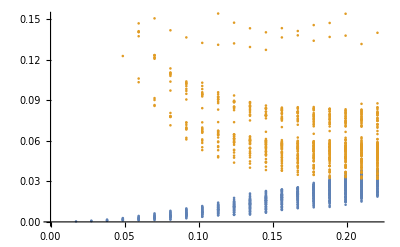

```mathematica
ListPlot[{Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦1⟧/Btab⟦All,4⟧)},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}}]
```

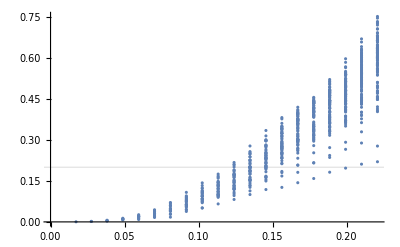

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦1⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧},*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦1⟧/bisperr)}},GridLines->{None,{0.2}}]
```

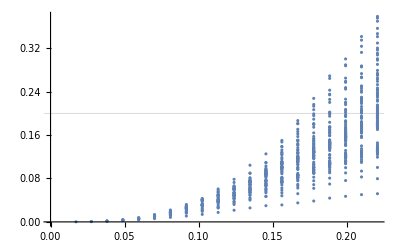

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦2⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧},*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦2⟧/bisperr)}},GridLines->{None,{0.2}}]
```

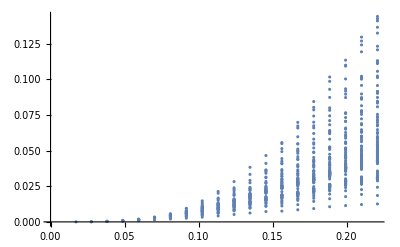

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦3⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦3⟧/bisperr)}},GridLines->{None,{0.2}}]
```

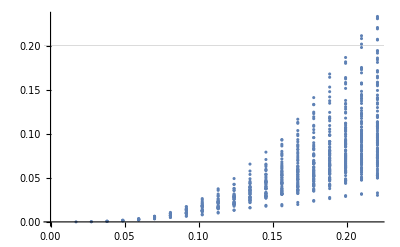

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦4⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦4⟧/bisperr)}},GridLines->{None,{0.2}}]
```

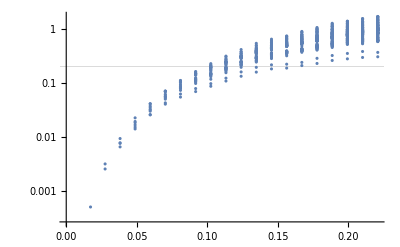

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦5⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦5⟧/bisperr)}},GridLines->{None,{0.2}}]
```

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦6⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦6⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

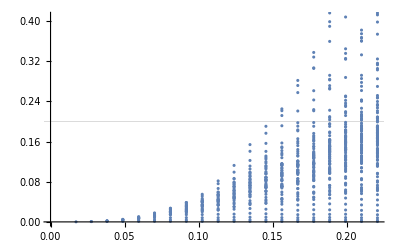

```mathematica
ListPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦7⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦7⟧/bisperr)}},GridLines->{None,{0.2}}]
```

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦8⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦8⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦9⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦9⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦10⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦10⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦11⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦11⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦12⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦12⟧/bisperr)}},GridLines->{None,{0.2}}]
```

-Graphics-

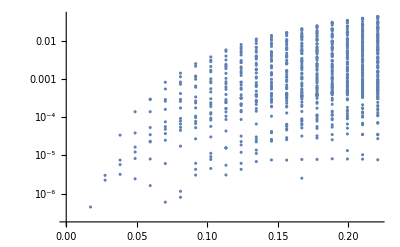

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦13⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦13⟧/bisperr)}},GridLines->{None,{0.2}}]
```

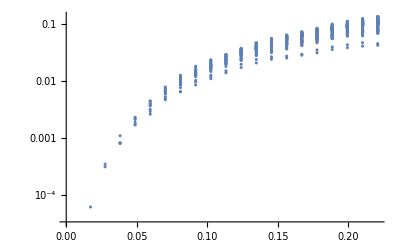

```mathematica
ListLogPlot[{(*Transpose@{triangles⟦All,1⟧,Abs@numtabs⟦14⟧/Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,bisperr/Btab⟦All,4⟧}*)Transpose@{triangles⟦All,1⟧,Abs@(numtabs⟦14⟧/bisperr)}},GridLines->{None,{0.2}}]
```

### Check counterterms numerically

Import PS. This is different than the interpolation from Python, import that on the triangles too

```mathematica
Pktab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Pktest.dat","Table"];
Ptriantab=Import["/Users/guido/github/bisp_pybird/pybird_dev/Ptriantest.dat","Table"];
iPk=Interpolation[Pktab];
LogLinearPlot[iPk[k],{k,0.001,0.25}]
```

-Graphics-

Import bispectrum to get triangles, order them such that k1 >= k2 >= k3

```mathematica
Btab=Import["/Users/guido/github/bisp_pybird/montepython_tree/data/Bisp_LightConeHector_cmass_ngc_mean.dat","Table"];
triangles=Btab⟦All,3;;1;;-1⟧;
triangles⟦;;10⟧
```

{{0.017221,0.017221,0.017221},{0.027562,0.027562,0.017221},{0.03818,0.03818,0.017221},{0.048836,0.048836,0.017221},{0.059539,0.059539,0.017221},{0.070261,0.070261,0.017221},{0.081,0.081,0.017221},{0.091757,0.091757,0.017221},{0.102501,0.102501,0.017221},{0.11325,0.11325,0.017221}}

For our test cosmology we have

```mathematica
subcosmo={f1->0.7775551009423526,nbar->4.5 10^-4,b1->2.,b2->0.4,b5->0.7,kM->1.}
```

{f1→0.777555,nbar→0.00045,b1→2.,b2→0.4,b5→0.7,kM→1.}

```mathematica
SeedRandom[42];
clist=RandomReal[{-2,2},14];
cbsub=Thread[cbias->clist]
```

{c_1→-0.296379,c_2→-0.435907,c_3→-0.611723,c_4→-0.185037,c_5→0.223853,c_6→-0.843323,c_7→-0.812608,c_8→-1.17437,c_9→-0.699321,c_10→1.8933,c_11→-0.964816,c_12→0.202326,c_13→0.869147,c_14→1.01741}

```mathematica
clist
```

{-0.296379,-0.435907,-0.611723,-0.185037,0.223853,-0.843323,-0.812608,-1.17437,-0.699321,1.8933,-0.964816,0.202326,0.869147,1.01741}

```mathematica
(*esub=Thread[ecoeff->0];
esub⟦12⟧=Subscript[e, 12]->1;
esub*)
```

```mathematica
(*Export["Pk1_check.dat",iPk[k1]/.k1->triangles⟦All,1⟧]*)
```

```mathematica
c1p123num=Table[ctr1p123/.ysub/.subcosmo/.cbsub/.{Plin[k1]->Ptriantab⟦i,1⟧,Plin[k2]->Ptriantab⟦i,2⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
c1p231num=Table[ctr1p231/.ysub/.subcosmo/.cbsub/.{Plin[k2]->Ptriantab⟦i,2⟧,Plin[k3]->Ptriantab⟦i,3⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
c1p312num=Table[ctr1p312/.ysub/.subcosmo/.cbsub/.{Plin[k3]->Ptriantab⟦i,3⟧,Plin[k1]->Ptriantab⟦i,1⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];

ctr1num=c1p123num+c1p231num+c1p312num;
```

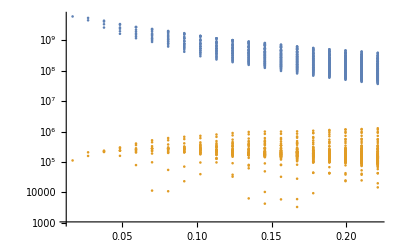

```mathematica
ListLogPlot[{Transpose@{triangles⟦All,1⟧,Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,Abs[ctr1num]}},PlotRange->All]
```

```mathematica
Export["Counterterm1_check42.dat",ctr1num];
```

```mathematica
c2p123num=Table[ctr2p123/.ysub/.subcosmo/.cbsub/.{Plin[k1]->Ptriantab⟦i,1⟧,Plin[k2]->Ptriantab⟦i,2⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
c2p231num=Table[ctr2p231/.ysub/.subcosmo/.cbsub/.{Plin[k2]->Ptriantab⟦i,2⟧,Plin[k3]->Ptriantab⟦i,3⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];
c2p312num=Table[ctr2p312/.ysub/.subcosmo/.cbsub/.{Plin[k3]->Ptriantab⟦i,3⟧,Plin[k1]->Ptriantab⟦i,1⟧}/.{k1->triangles⟦i,1⟧,k2->triangles⟦i,2⟧,k3->triangles⟦i,3⟧},{i,1,Length[triangles]}];

ctr2num=c2p123num+c2p231num+c2p312num;
```

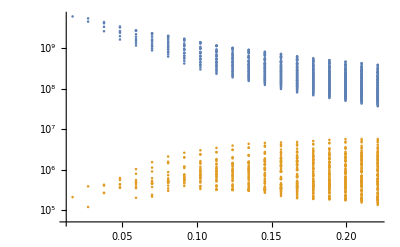

```mathematica
ListLogPlot[{Transpose@{triangles⟦All,1⟧,Btab⟦All,4⟧},Transpose@{triangles⟦All,1⟧,Abs[ctr2num]}},PlotRange->All]
```

```mathematica
Export["Counterterm2_check42.dat",ctr2num];
```

### Check with Matt’s results

First check the PS

```mathematica
fullP[k1_,μ1_]=Simplify[PϵϵSend[k1,μ1]+P13CTSend[k1,μ1]]
```

((kM^2 cSTtilde[1]+k1^2 (cSTtilde[2]+f1 μ1^2 cSTtilde[3]))/nbar-k1^2 (b1+f1 μ1^2) (2 ch[1]+f1 μ1^2 (-2 cρv[1]+f1 (μ1^2 cρv2[1]+cρv2[3]))) P11[k1])/kM^2

```mathematica
μlistmono=DeleteCases[Table[μ1^i,{i,0,6}]//Flatten,1];
```

```mathematica
Pmono[k1_]=GetMonopole[fullP[k1,μ1],μlistmono];
```

Residual is

0

```mathematica
Pquad[k1_]=(2 2+1)/2 Integrate[fullP[k1,μ1]LegendreP[2,μ1],{μ1,-1,1}];
```

```mathematica
TotalCTListReps={ch[1]->-1.9140000000000001,ch[2]->0.975,ch[3]->-2.523,ch[4]->0.14200000000000002,ch[5]->-0.6930000000000001,cSTtilde[1]->0.17200000000000001,cSTtilde[2]->1.873,cSTtilde[3]->-2.323,cSTtilde[4]->0.427,cSTtilde[5]->-0.8,cSTtilde[6]->-0.549,cSTtilde[7]->-1.676,cSTtilde[8]->0.746,cSTtilde[9]->-2.851,cSTtilde[10]->-2.196,cSTtilde[11]->0.546,cSTtilde[12]->-2.315,cSTtilde[13]->-2.049,cϵ3tilde[1]->-2.32,cϵ3tilde[2]->-0.044,cϵ3tilde[5]->1.438,cρv[1]->2.4290000000000003,cρv[5]->1.313,cρv2[1]->2.301,cρv2[2]->-0.097,cρv2[3]->0.72,cρv2[4]->-1.675,cρv2[5]->-1.089,cρv2[6]->2.04,cρv2[7]->-2.553}
extraVarsReps={nbar->0.292,kM->1.756,f1->-0.053,b1->1.572,b2->-1.803,b5->2.105,k->-2.232,μk->2.249,k1->-2.864,k2->1.34,k3->0.686,μk1->-0.395,μk2->1.742}
```

{ch[1]→-1.914,ch[2]→0.975,ch[3]→-2.523,ch[4]→0.142,ch[5]→-0.693,cSTtilde[1]→0.172,cSTtilde[2]→1.873,cSTtilde[3]→-2.323,cSTtilde[4]→0.427,cSTtilde[5]→-0.8,cSTtilde[6]→-0.549,cSTtilde[7]→-1.676,cSTtilde[8]→0.746,cSTtilde[9]→-2.851,cSTtilde[10]→-2.196,cSTtilde[11]→0.546,cSTtilde[12]→-2.315,cSTtilde[13]→-2.049,cϵ3tilde[1]→-2.32,cϵ3tilde[2]→-0.044,cϵ3tilde[5]→1.438,cρv[1]→2.429,cρv[5]→1.313,cρv2[1]→2.301,cρv2[2]→-0.097,cρv2[3]→0.72,cρv2[4]→-1.675,cρv2[5]→-1.089,cρv2[6]→2.04,cρv2[7]→-2.553}

{nbar→0.292,kM→1.756,f1→-0.053,b1→1.572,b2→-1.803,b5→2.105,k→-2.232,μk→2.249,k1→-2.864,k2→1.34,k3→0.686,μk1→-0.395,μk2→1.742}

```mathematica
Pmono[k]/.TotalCTListReps/.extraVarsReps//FullSimplify
```

11.1793+9.39448 P11[-2.232]

```mathematica
Pquad[k]/.TotalCTListReps/.extraVarsReps//FullSimplify
```

0.454141-0.654314 P11[-2.232]

Power spectrum works. Do Bispectrum

```mathematica
s2mono=(s2p123+s2p231+s2p312)/.ysub;
c1mono=(ctr1p123+ctr1p231+ctr1p312)/.ysub;
c2mono=(ctr2p123+ctr2p231+ctr2p312)/.ysub;
```

```mathematica
substoch
```

{cSTtilde[1]→e_1,cSTtilde[2]→e_2,cSTtilde[4]→e_3,cSTtilde[5]→e_4,cSTtilde[6]→e_5,cSTtilde[7]→e_6,cSTtilde[8]→e_7,cSTtilde[9]→e_8,cSTtilde[10]→e_9,cSTtilde[11]→e_10,cSTtilde[12]→e_11,cSTtilde[13]→e_12}

```mathematica
csub
```

{ch[1]→c_1,cρv[1]→c_2,cρv2[1]→c_3,cρv2[3]→c_4,ch[2]→c_5,ch[3]→c_6,ch[4]→c_7,ch[5]→c_8,cρv[5]→c_9,cρv2[2]→c_10,cρv2[4]→c_11,cρv2[5]→c_12,cρv2[6]→c_13,cρv2[7]→c_14}

```mathematica
mysub=TotalCTListReps/.csub/.substoch
```

{c_1→-1.914,c_5→0.975,c_6→-2.523,c_7→0.142,c_8→-0.693,e_1→0.172,e_2→1.873,cSTtilde[3]→-2.323,e_3→0.427,e_4→-0.8,e_5→-0.549,e_6→-1.676,e_7→0.746,e_8→-2.851,e_9→-2.196,e_10→0.546,e_11→-2.315,e_12→-2.049,cϵ3tilde[1]→-2.32,cϵ3tilde[2]→-0.044,cϵ3tilde[5]→1.438,c_2→2.429,c_9→1.313,c_3→2.301,c_10→-0.097,c_4→0.72,c_11→-1.675,c_12→-1.089,c_13→2.04,c_14→-2.553}

```mathematica
Bϵϵϵmono[k1,k2,k3]+s2mono+c1mono+c2mono/.mysub/.extraVarsReps
```

-19.4186-28.8541 P11[-2.864]-501.382 P11[0.686]-206.682 P11[1.34]-235.966 Plin[-2.864] Plin[0.686]-101.39 Plin[-2.864] Plin[1.34]-49.667 Plin[0.686] Plin[1.34]

```mathematica
-19.41858379021722+P11[-2.864] (-28.85411192747014-235.96586940756941 P11[0.686]-101.38977780021321 P11[1.34])+P11[0.686] (-501.3821238894282-49.666990656176196 P11[1.34])-206.68247378670344 P11[1.34]//Expand
```

-19.4186-28.8541 P11[-2.864]-501.382 P11[0.686]-235.966 P11[-2.864] P11[0.686]-206.682 P11[1.34]-101.39 P11[-2.864] P11[1.34]-49.667 P11[0.686] P11[1.34]

## Tables of substitutions of integrals with μ0 into integrals of μ1, μ2

Final output of this section are the 4 Bispectrum diagrams tabulated to the master integral

### Useful definitions

All integrands in Bintegrand can be FFTlogged to q^(-2ν1) k1pq^(-2 ν2) k2mq^(-2 ν3) = I(ν1,ν2,ν3,k1,k2).
If such an integrand is multiplied by μ0^n, then we can expand the vector integral q...q I in scalar integrals.
We will then get some scalar coefficients and μ1 and μ2

Great trick to get scalar products. Instead of vector components, we write vectors such that the scalar products come out right as a single symbol.
Notice that we need separately scalar products with q, scalar products between k1, k2, and finally scalar products k1.z, k2.z .
So we separate definitions by using the trick of getting 3 components corresponding to the 3 scalar products q.q, q.k1, q.k2.
Then we make definitions for k1, k2, and for z

```mathematica
qv={√(q^2-1-qk2^2),1,qk2};
k1vq={0,qk1,0};
k2vq={0,0,1};
mydeltaq=IdentityMatrix[3];

{qv.qv,qv.k1vq,qv.k2vq,qv.mydeltaq.qv}
```

{q^2,qk1,qk2,q^2}

```mathematica
k1vk={√(k1^2-1),1,0};
k2vk={0,k1k2,√(k2^2-k1k2^2)};
mydeltak=IdentityMatrix[3];

{k1vk.k1vk, k2vk.k2vk, k1vk.k2vk, k1vk.mydeltak.k1vk, k1vk.mydeltak.k2vk, k2vk.mydeltak.k2vk}
```

{k1^2,k2^2,k1k2,k1^2,k1k2,k2^2}

```mathematica
k1vz={0,0,k1 μ1};
k2vz={0,0,k2 μ2};
zh={0,0,1};
mydeltaz=IdentityMatrix[3];

{k1vz.zh,k2vz.zh,zh.mydeltaz.zh}
```

{k1 μ1,k2 μ2,1}

In every case, we have the simple identity and traces of the deltas are fine.
Substitutions for the scalar products.

```mathematica
kqsub={qk1->1/2(k1pq^2-k1^2-q^2),qk2->1/2(-k2mq^2+k2^2+q^2)};
k1k2sub={k1k2->1/2(k3^2-k1^2-k2^2)};
```

Function to get the product of n vectors, as in q^i... q^n and similar for z

```mathematica
Getvtensor[v_,n_]:=TensorProduct@@Table[v,n]
```

Functions to generate the vectors of operators in which we expand the integrals with q^i... q^n at each order.
The simplest is B3212, which only depends on k2 (for the permutation we consider), up to second order.
We will need tensors symmetric in k1, k2 for B222 up to 6th order, and for B411 up to second order.
Finally we need non-symmetric tensors for B3211 (although symmetric will work when we sum the permutations, but it’s easier for checks).

```mathematica
Ts1[k1v_,k2v_,mydelta_]:=TensorProduct[{k1v+k2v}];
Ts2[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v+k2v,k1v+k2v],
TensorProduct[k1v,k2v],
mydelta};
Ts3[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v],
TensorProduct[k1v+k2v,k1v,k2v],
TensorProduct[k1v+k2v,mydelta]};
Ts4[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v,k2v],
TensorProduct[k1v+k2v,k1v+k2v,mydelta],
TensorProduct[k1v,k2v,k1v,k2v],
TensorProduct[k1v,k2v,mydelta],
TensorProduct[mydelta,mydelta]};
Ts5[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v,k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,mydelta],
TensorProduct[k1v+k2v,k1v,k2v,k1v,k2v],
TensorProduct[k1v+k2v,k1v,k2v,mydelta],
TensorProduct[k1v+k2v,mydelta,mydelta]};
Ts6[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v,k1v,k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v+k2v,k1v+k2v,mydelta],
TensorProduct[k1v+k2v,k1v+k2v,k1v,k2v,k1v,k2v],
TensorProduct[k1v+k2v,k1v+k2v,k1v,k2v,mydelta],
TensorProduct[k1v+k2v,k1v+k2v,mydelta,mydelta],
TensorProduct[k1v,k2v,k1v,k2v,k1v,k2v],
TensorProduct[k1v,k2v,k1v,k2v,mydelta],
TensorProduct[k1v,k2v,mydelta,mydelta],
TensorProduct[mydelta,mydelta,mydelta]};
```

```mathematica
Tns1[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v],
TensorProduct[k2v]};
Tns2[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v,k1v],
TensorProduct[k1v,k2v],
TensorProduct[k2v,k2v],
mydelta};
Tns3[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v,k1v,k1v],
TensorProduct[k1v,k1v,k2v],
TensorProduct[k1v,k2v,k2v],
TensorProduct[k2v,k2v,k2v],
TensorProduct[k1v,mydelta],
TensorProduct[k2v,mydelta]};
Tns4[k1v_,k2v_,mydelta_]:=Symmetrize/@{TensorProduct[k1v,k1v,k1v,k1v],
TensorProduct[k1v,k1v,k1v,k2v],
TensorProduct[k1v,k1v,k2v,k2v],
TensorProduct[k1v,k2v,k2v,k2v],
TensorProduct[k2v,k2v,k2v,k2v],
TensorProduct[k1v,k1v,mydelta],
TensorProduct[k1v,k2v,mydelta],
TensorProduct[k2v,k2v,mydelta],
TensorProduct[mydelta,mydelta]};
```

```mathematica
Tv1[kv_,mydelta_]:=Symmetrize/@{TensorProduct[kv]};
Tv2[kv_,mydelta_]:=Symmetrize/@{TensorProduct[kv,kv],mydelta};
```

The following are functions that help setup the table of FFTLog coefficients.

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list⟦#⟧&];
```

```mathematica
compressor[tab_] := Module[{tab1,tab2},
tab1 = positionDuplicates[Table[Delete[tab⟦i⟧,-1],{i,1,Length[tab]}]];
tab2 = Monitor[Table[{tab⟦tab1⟦j,1⟧⟧⟦{1,2,3,4}⟧,
Sum[tab⟦tab1⟦j,i⟧⟧⟦5⟧,{i,1,Length[tab1⟦j⟧]}]}//Flatten,{j,1,Length[tab1]}],j*100.0/Length[tab1]]]
```

### Redshift space kernels, μ0 expansion non-symmetric in k1-k2, up to μ0^4 (for B3211)

#### First order, μ0^1

Generate tensors for the different contractions we need

```mathematica
Tq=Tns1[k1vq,k2vq,IdentityMatrix[3]];
Tk=Tns1[k1vk,k2vk,IdentityMatrix[3]];
Tz=Tns1[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,1];
ztensor=Getvtensor[zh,1];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1,a2}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i⟧ztensor⟦i⟧,{i,Length[zh]}],{α,1,Length[Tz]}]//Simplify
```

{k1 μ1,k2 μ2}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i⟧qtensor⟦i⟧,{i,Length[qv]}],
{α,1,Length[Tq]}]//FullSimplify
```

{qk1/q,qk2/q}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i⟧ Tk⟦β,i⟧,{i,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]/.k1k2sub//Simplify
```

{{k1^2,1/2 (-k1^2-k2^2+k3^2)},{1/2 (-k1^2-k2^2+k3^2),k2^2}}

```mathematica
invT=Inverse[TdotT]//Simplify
```

{{k2^2/(k1^2 k2^2-1/4 (k1^2+k2^2-k3^2)^2),-(2 (k1^2+k2^2-k3^2))/(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2))},{-(2 (k1^2+k2^2-k3^2))/(k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)),k1^2/(k1^2 k2^2-1/4 (k1^2+k2^2-k3^2)^2)}}

Solution

```mathematica
μ0sol1=Tdotz.invT.Tdotint/.kqsub//Simplify
```

(k1^3 (k2^2+k2mq^2-q^2) μ1+k1 (-2 k1pq^2 k2^2-k2^4+k3^2 (-k2mq^2+q^2)+k2^2 (k2mq^2+k3^2+q^2)) μ1+k1^4 k2 μ2-k2 (k2^2-k3^2) (k1pq^2-q^2) μ2-k1^2 k2 (k1pq^2+k2^2-2 k2mq^2+k3^2+q^2) μ2)/((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q)

#### Second order, μ0^2

Generate tensors for the different contractions we need

```mathematica
Tq=Tns2[k1vq,k2vq,IdentityMatrix[3]];
Tk=Tns2[k1vk,k2vk,IdentityMatrix[3]];
Tz=Tns2[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,2];
ztensor=Getvtensor[zh,2];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1,a2,a3,a4}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i,j⟧ztensor⟦i,j⟧,{i,Length[zh]},{j,Length[zh]}],
{α,1,Length[Tz]}]//Simplify
```

{k1^2 μ1^2,k1 k2 μ1 μ2,k2^2 μ2^2,1}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i,j⟧qtensor⟦i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tq]}]//FullSimplify
```

{qk1^2/q^2,(qk1 qk2)/q^2,qk2^2/q^2,1}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i,j⟧ Tk⟦β,i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify
```

{{k1^4,k1^2 k1k2,k1k2^2,k1^2},{k1^2 k1k2,1/2 (k1k2^2+k1^2 k2^2),k1k2 k2^2,k1k2},{k1k2^2,k1k2 k2^2,k2^4,k2^2},{k1^2,k1k2,k2^2,3}}

```mathematica
invT=Simplify[Inverse[TdotT]]/.k1k2sub//Simplify;
```

Solution

```mathematica
μ0sol2=Tdotz.invT.Tdotint/.kqsub//Simplify
```

((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2))^2 q^2+4 k1^2 k2^2 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2 μ1^2+4 k1 k2 (k1^2+k2^2-k3^2) (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2 μ1 μ2+4 k1^2 k2^2 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2 μ2^2+k2^2 (k1^2-k1pq^2+q^2)^2 (8 k1^3 k2 μ1 μ2+8 k1 k2 (k2^2-k3^2) μ1 μ2+k1^4 (1+μ2^2)+(k2^2-k3^2)^2 (1+μ2^2)+k1^2 (-2 k3^2 (1+μ2^2)+k2^2 (-2+8 μ1^2+6 μ2^2)))+k1^2 (k2^2-k2mq^2+q^2)^2 (k1^4 (1+μ1^2)+(k2^2-k3^2)^2 (1+μ1^2)+8 k1^3 k2 μ1 μ2+8 k1 k2 (k2^2-k3^2) μ1 μ2+k1^2 (-2 k3^2 (1+μ1^2)+k2^2 (-2+6 μ1^2+8 μ2^2)))-(k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2) (k1^6+(k2^2-k3^2)^3+6 k1^5 k2 μ1 μ2+4 k1^3 k2 (5 k2^2-3 k3^2) μ1 μ2+6 k1 k2 (k2^2-k3^2)^2 μ1 μ2+k1^4 (-3 k3^2+k2^2 (-1+8 μ1^2+8 μ2^2))+k1^2 (k2^2-k3^2) (-3 k3^2+k2^2 (-1+8 μ1^2+8 μ2^2))))/((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2))^2 q^2)

#### Third order, μ0^3

Generate tensors for the different contractions we need

```mathematica
Tq=Tns3[k1vq,k2vq,IdentityMatrix[3]];
Tk=Tns3[k1vk,k2vk,IdentityMatrix[3]];
Tz=Tns3[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,3];
ztensor=Getvtensor[zh,3];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1,a2,a3,a4,a5,a6}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i,j,k⟧ztensor⟦i,j,k⟧,{i,Length[zh]},{j,Length[zh]},{k,Length[zh]}],
{α,1,Length[Tz]}]//Simplify
```

{k1^3 μ1^3,k1^2 k2 μ1^2 μ2,k1 k2^2 μ1 μ2^2,k2^3 μ2^3,k1 μ1,k2 μ2}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i,j,k⟧qtensor⟦i,j,k⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]}],
{α,1,Length[Tq]}]//FullSimplify
```

{qk1^3/q^3,(qk1^2 qk2)/q^3,(qk1 qk2^2)/q^3,qk2^3/q^3,qk1/q,qk2/q}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i,j,k⟧ Tk⟦β,i,j,k⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify
```

{{k1^6,k1^4 k1k2,k1^2 k1k2^2,k1k2^3,k1^4,k1^2 k1k2},{k1^4 k1k2,1/3 (2 k1^2 k1k2^2+k1^4 k2^2),1/3 (k1k2^3+2 k1^2 k1k2 k2^2),k1k2^2 k2^2,k1^2 k1k2,1/3 (2 k1k2^2+k1^2 k2^2)},{k1^2 k1k2^2,1/3 (k1k2^3+2 k1^2 k1k2 k2^2),1/3 (2 k1k2^2 k2^2+k1^2 k2^4),k1k2 k2^4,1/3 (2 k1k2^2+k1^2 k2^2),k1k2 k2^2},{k1k2^3,k1k2^2 k2^2,k1k2 k2^4,k2^6,k1k2 k2^2,k2^4},{k1^4,k1^2 k1k2,1/3 (2 k1k2^2+k1^2 k2^2),k1k2 k2^2,(5 k1^2)/3,(5 k1k2)/3},{k1^2 k1k2,1/3 (2 k1k2^2+k1^2 k2^2),k1k2 k2^2,k2^4,(5 k1k2)/3,(5 k2^2)/3}}

```mathematica
invT=Simplify[Inverse[TdotT]]/.k1k2sub//Simplify;
```

Solution

```mathematica
μ0sol3=Tdotz.invT.Tdotint/.kqsub//Simplify
```

(3 k2 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2 (k1^2-k1pq^2+q^2) (k1^6 μ2+(k2^2-k3^2)^3 μ2+2 k1^5 k2 μ1 (1+2 μ2^2)+2 k1 k2 (k2^2-k3^2)^2 μ1 (1+2 μ2^2)+4 k1^3 k2 μ1 (-k3^2 (1+2 μ2^2)+k2^2 (-1+2 μ1^2+4 μ2^2))+k1^4 μ2 (-3 k3^2+k2^2 (-1+12 μ1^2+4 μ2^2))+k1^2 (k2^2-k3^2) μ2 (-3 k3^2+k2^2 (-1+12 μ1^2+4 μ2^2)))-3 k1 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2 (k2^2-k2mq^2+q^2) (k1^6 μ1+(k2^2-k3^2)^3 μ1+2 k1^5 k2 (1+2 μ1^2) μ2+2 k1 k2 (k2^2-k3^2)^2 (1+2 μ1^2) μ2+4 k1^3 k2 μ2 (-k3^2 (1+2 μ1^2)+k2^2 (-1+4 μ1^2+2 μ2^2))+k1^4 μ1 (-3 k3^2+k2^2 (-1+4 μ1^2+12 μ2^2))+k1^2 (k2^2-k3^2) μ1 (-3 k3^2+k2^2 (-1+4 μ1^2+12 μ2^2)))+k2^3 (k1^2-k1pq^2+q^2)^3 (k1^6 μ2 (3+μ2^2)+(k2^2-k3^2)^3 μ2 (3+μ2^2)+6 k1^5 k2 μ1 (1+3 μ2^2)+6 k1 k2 (k2^2-k3^2)^2 μ1 (1+3 μ2^2)+3 k1^4 μ2 (-k3^2 (3+μ2^2)+k2^2 (-1+16 μ1^2+5 μ2^2))+3 k1^2 (k2^2-k3^2) μ2 (-k3^2 (3+μ2^2)+k2^2 (-1+16 μ1^2+5 μ2^2))+4 k1^3 k2 μ1 (-3 k3^2 (1+3 μ2^2)+k2^2 (-3+8 μ1^2+15 μ2^2)))-k1^3 (k2^2-k2mq^2+q^2)^3 (k1^6 μ1 (3+μ1^2)+(k2^2-k3^2)^3 μ1 (3+μ1^2)+6 k1^5 k2 (1+3 μ1^2) μ2+6 k1 k2 (k2^2-k3^2)^2 (1+3 μ1^2) μ2+4 k1^3 k2 μ2 (-3 k3^2 (1+3 μ1^2)+k2^2 (-3+15 μ1^2+8 μ2^2))+3 k1^4 μ1 (-k3^2 (3+μ1^2)+k2^2 (-1+5 μ1^2+16 μ2^2))+3 k1^2 (k2^2-k3^2) μ1 (-k3^2 (3+μ1^2)+k2^2 (-1+5 μ1^2+16 μ2^2)))+3 k1 (k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2)^2 (k1^8 μ1+(k2^2-k3^2)^4 μ1+k1^7 k2 (3+5 μ1^2) μ2+k1 k2 (k2^2-k3^2)^3 (3+5 μ1^2) μ2+2 k1^6 μ1 (-2 k3^2+k2^2 (1+3 μ1^2+10 μ2^2))+2 k1^2 (k2^2-k3^2)^2 μ1 (-2 k3^2+k2^2 (1+3 μ1^2+10 μ2^2))+k1^5 k2 μ2 (-3 k3^2 (3+5 μ1^2)+k2^2 (-3+43 μ1^2+16 μ2^2))+k1^3 k2 (k2^2-k3^2) μ2 (-3 k3^2 (3+5 μ1^2)+k2^2 (-3+43 μ1^2+16 μ2^2))+2 k1^4 μ1 (3 k3^4-2 k2^2 k3^2 (2+3 μ1^2+10 μ2^2)+k2^4 (-3+10 μ1^2+28 μ2^2)))-3 k2 (k1^2-k1pq^2+q^2)^2 (k2^2-k2mq^2+q^2) (k1^8 μ2+(k2^2-k3^2)^4 μ2+k1^7 k2 μ1 (3+5 μ2^2)+k1 k2 (k2^2-k3^2)^3 μ1 (3+5 μ2^2)+2 k1^6 μ2 (-2 k3^2+k2^2 (1+10 μ1^2+3 μ2^2))+2 k1^2 (k2^2-k3^2)^2 μ2 (-2 k3^2+k2^2 (1+10 μ1^2+3 μ2^2))+2 k1^4 μ2 (3 k3^4-2 k2^2 k3^2 (2+10 μ1^2+3 μ2^2)+k2^4 (-3+28 μ1^2+10 μ2^2))+k1^5 k2 μ1 (-3 k3^2 (3+5 μ2^2)+k2^2 (-3+16 μ1^2+43 μ2^2))+k1^3 k2 (k2^2-k3^2) μ1 (-3 k3^2 (3+5 μ2^2)+k2^2 (-3+16 μ1^2+43 μ2^2))))/((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2))^3 q^3)

#### Fourth order, μ0^4

Generate tensors for the different contractions we need

```mathematica
Tq=Tns4[k1vq,k2vq,IdentityMatrix[3]];
Tk=Tns4[k1vk,k2vk,IdentityMatrix[3]];
Tz=Tns4[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,4];
ztensor=Getvtensor[zh,4];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1,a2,a3,a4,a5,a6,a7,a8,a9}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i,j,k,l⟧ztensor⟦i,j,k,l⟧,{i,Length[zh]},{j,Length[zh]},{k,Length[zh]},{l,Length[zh]}],
{α,1,Length[Tz]}]//Simplify
```

{k1^4 μ1^4,k1^3 k2 μ1^3 μ2,k1^2 k2^2 μ1^2 μ2^2,k1 k2^3 μ1 μ2^3,k2^4 μ2^4,k1^2 μ1^2,k1 k2 μ1 μ2,k2^2 μ2^2,1}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i,j,k,l⟧qtensor⟦i,j,k,l⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]},{l,Length[qv]}],
{α,1,Length[Tq]}]/.kqsub//Simplify
```

{((k1^2-k1pq^2+q^2)^4)/(16 q^4),-((k1^2-k1pq^2+q^2)^3 (k2^2-k2mq^2+q^2))/(16 q^4),((k1^2-k1pq^2+q^2)^2 (k2^2-k2mq^2+q^2)^2)/(16 q^4),-((k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2)^3)/(16 q^4),((k2^2-k2mq^2+q^2)^4)/(16 q^4),((k1^2-k1pq^2+q^2)^2)/(4 q^2),-((k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2))/(4 q^2),((k2^2-k2mq^2+q^2)^2)/(4 q^2),1}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i,j,k,l⟧ Tk⟦β,i,j,k,l⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]},{l,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify
```

{{k1^8,k1^6 k1k2,k1^4 k1k2^2,k1^2 k1k2^3,k1k2^4,k1^6,k1^4 k1k2,k1^2 k1k2^2,k1^4},{k1^6 k1k2,1/4 (3 k1^4 k1k2^2+k1^6 k2^2),1/2 k1^2 k1k2 (k1k2^2+k1^2 k2^2),1/4 (k1k2^4+3 k1^2 k1k2^2 k2^2),k1k2^3 k2^2,k1^4 k1k2,1/4 (3 k1^2 k1k2^2+k1^4 k2^2),1/2 (k1k2^3+k1^2 k1k2 k2^2),k1^2 k1k2},{k1^4 k1k2^2,1/2 k1^2 k1k2 (k1k2^2+k1^2 k2^2),1/6 (k1k2^4+4 k1^2 k1k2^2 k2^2+k1^4 k2^4),1/2 k1k2 k2^2 (k1k2^2+k1^2 k2^2),k1k2^2 k2^4,1/6 (5 k1^2 k1k2^2+k1^4 k2^2),1/3 (k1k2^3+2 k1^2 k1k2 k2^2),1/6 (5 k1k2^2 k2^2+k1^2 k2^4),1/3 (2 k1k2^2+k1^2 k2^2)},{k1^2 k1k2^3,1/4 (k1k2^4+3 k1^2 k1k2^2 k2^2),1/2 k1k2 k2^2 (k1k2^2+k1^2 k2^2),1/4 (3 k1k2^2 k2^4+k1^2 k2^6),k1k2 k2^6,1/2 (k1k2^3+k1^2 k1k2 k2^2),1/4 (3 k1k2^2 k2^2+k1^2 k2^4),k1k2 k2^4,k1k2 k2^2},{k1k2^4,k1k2^3 k2^2,k1k2^2 k2^4,k1k2 k2^6,k2^8,k1k2^2 k2^2,k1k2 k2^4,k2^6,k2^4},{k1^6,k1^4 k1k2,1/6 (5 k1^2 k1k2^2+k1^4 k2^2),1/2 (k1k2^3+k1^2 k1k2 k2^2),k1k2^2 k2^2,(4 k1^4)/3,(4 k1^2 k1k2)/3,1/6 (7 k1k2^2+k1^2 k2^2),(5 k1^2)/3},{k1^4 k1k2,1/4 (3 k1^2 k1k2^2+k1^4 k2^2),1/3 (k1k2^3+2 k1^2 k1k2 k2^2),1/4 (3 k1k2^2 k2^2+k1^2 k2^4),k1k2 k2^4,(4 k1^2 k1k2)/3,1/12 (9 k1k2^2+7 k1^2 k2^2),(4 k1k2 k2^2)/3,(5 k1k2)/3},{k1^2 k1k2^2,1/2 (k1k2^3+k1^2 k1k2 k2^2),1/6 (5 k1k2^2 k2^2+k1^2 k2^4),k1k2 k2^4,k2^6,1/6 (7 k1k2^2+k1^2 k2^2),(4 k1k2 k2^2)/3,(4 k2^4)/3,(5 k2^2)/3},{k1^4,k1^2 k1k2,1/3 (2 k1k2^2+k1^2 k2^2),k1k2 k2^2,k2^4,(5 k1^2)/3,(5 k1k2)/3,(5 k2^2)/3,5}}

```mathematica
invT=Simplify[Inverse[TdotT]]/.k1k2sub//Simplify;
```

Solution

```mathematica
μ0sol4=Tdotz.invT.Tdotint//Simplify;
```

#### Save everything

```mathematica
{1,μ0sol1,μ0sol2,μ0sol3,μ0sol4}>>"tables/mu0sol_nonsym_upto4.m"
```

### Redshift space kernels, μ0 expansion dependent only on k1, up to μ0^2 (for B3212)

#### First order, μ0^1

Generate tensors for the different contractions we need

```mathematica
Tq=Tv1[k1vq,IdentityMatrix[3]];
Tk=Tv1[k1vk,IdentityMatrix[3]];
Tz=Tv1[k1vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,1];
ztensor=Getvtensor[zh,1];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i⟧ztensor⟦i⟧,{i,Length[zh]}],{α,1,Length[Tz]}]//Simplify
```

{k1 μ1}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i⟧qtensor⟦i⟧,{i,Length[qv]}],
{α,1,Length[Tq]}]//FullSimplify
```

{qk1/q}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i⟧ Tk⟦β,i⟧,{i,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]/.k1k2sub//Simplify
```

{{k1^2}}

```mathematica
invT=Inverse[TdotT]//Simplify
```

{{1/k1^2}}

Solution

```mathematica
μ0sol1=Tdotz.invT.Tdotint/.kqsub//Simplify
```

-((k1^2-k1pq^2+q^2) μ1)/(2 k1 q)

#### Second order, μ0^2

Generate tensors for the different contractions we need

```mathematica
Tq=Tv2[k1vq,IdentityMatrix[3]];
Tk=Tv2[k1vk,IdentityMatrix[3]];
Tz=Tv2[k1vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,2];
ztensor=Getvtensor[zh,2];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tk]}]
```

{a1,a2}

Contraction of T’s with zhat’s

```mathematica
Tdotz=Table[Sum[Tz⟦α,i,j⟧ztensor⟦i,j⟧,{i,Length[zh]},{j,Length[zh]}],
{α,1,Length[Tz]}]//Simplify
```

{k1^2 μ1^2,1}

Contraction with the integral

```mathematica
Tdotint=Table[Sum[Tq⟦α,i,j⟧qtensor⟦i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tq]}]//FullSimplify
```

{qk1^2/q^2,1}

Contraction of T with itself, and inverse

```mathematica
TdotT=Table[Sum[Tk⟦α,i,j⟧ Tk⟦β,i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify
```

{{k1^4,k1^2},{k1^2,3}}

```mathematica
invT=Simplify[Inverse[TdotT]]/.k1k2sub//Simplify;
```

Solution

```mathematica
μ0sol2=Tdotz.invT.Tdotint/.kqsub//Simplify
```

1/4 (2-2 μ1^2+((k1^2-k1pq^2+q^2)^2 (-1+3 μ1^2))/(2 k1^2 q^2))

#### Save everything

```mathematica
{1,μ0sol1,μ0sol2}>>"tables/mu0solk1_vec_upto2.m"
```

### Redshift space kernels, μ0 expansion, symmetric in k1-k2 up to μ0^3 (for B222 and B411) analytically

#### First order, μ0^1

Generate tensors

```mathematica
Tq=Ts1[k1vq,k2vq,IdentityMatrix[3]];
Tk=Ts1[k1vk,k2vk,IdentityMatrix[3]];
Tz=Ts1[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,1];
ztensor=Getvtensor[zh,1];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tq]}]
```

{a1}

Contractions

```mathematica
Tdotint=Table[Sum[Tq⟦α,i⟧qtensor⟦i⟧,{i,3}],{α,1,Length[Tq]}]//Simplify;
TdotT=Table[Sum[Tk⟦α,i⟧ Tk⟦β,i⟧,{i,Length[qv]}],{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify;
Tdotz=Table[Sum[Tz⟦α,i⟧ztensor⟦i⟧,{i,Length[ztensor]}],{α,1,Length[Tz]}]//FullSimplify;
```

Inverse and solution for μ0

```mathematica
invT=Inverse[TdotT]/.k1k2sub//Simplify
```

{{1/k3^2}}

```mathematica
μ0sol1=Tdotz.invT.Tdotint/.kqsub//Simplify
```

-((k1^2-k1pq^2-k2^2+k2mq^2) (k1 μ1+k2 μ2))/(2 k3^2 q)

#### Second order, μ0^2

Generate tensors

```mathematica
Tq=Ts2[k1vq,k2vq,IdentityMatrix[3]];
Tk=Ts2[k1vk,k2vk,IdentityMatrix[3]];
Tz=Ts2[k1vz,k2vz,IdentityMatrix[3]];
qtensor=Getvtensor[qv/q,2];
ztensor=Getvtensor[zh,2];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tq]}]
```

{a1,a2,a3}

Contractions

```mathematica
Tdotint=Simplify[Table[Sum[Tq⟦α,i,j⟧qtensor⟦i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tq]}]]//Simplify
TdotT=Table[Sum[Tk⟦α,i,j⟧ Tk⟦β,i,j⟧,{i,Length[qv]},{j,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify
Tdotz=Simplify[Table[Sum[Tz⟦α,i,j⟧ztensor⟦i,j⟧,{i,Length[zh]},{j,Length[zh]}],
{α,1,Length[Tz]}]]//Simplify
```

{(qk1+qk2)^2/q^2,(qk1 qk2)/q^2,1}

{{(k1^2+2 k1k2+k2^2)^2,(k1^2+k1k2) (k1k2+k2^2),k1^2+2 k1k2+k2^2},{(k1^2+k1k2) (k1k2+k2^2),1/2 (k1k2^2+k1^2 k2^2),k1k2},{k1^2+2 k1k2+k2^2,k1k2,3}}

{(k1 μ1+k2 μ2)^2,k1 k2 μ1 μ2,1}

Inverse and solution for μ0

```mathematica
invT=Inverse[TdotT]/.k1k2sub//Simplify;
```

```mathematica
μ0sol2=Simplify[Tdotz.invT.Tdotint/.kqsub]//Simplify
```

(2 (k1^4+k2^4+2 k2^2 k3^2-k3^4-2 k1^2 (k2^2-k3^2))+8 k1 k2 k3^2 μ1 μ2-4 (k1^2+k2^2) (k1 μ1+k2 μ2)^2+(2 (k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2) (3 k1^6 μ1^2+6 k1^5 k2 μ1 μ2-4 k1^3 k2 (3 k2^2+k3^2) μ1 μ2+2 k1 k2 (3 k2^4-2 k2^2 k3^2+3 k3^4) μ1 μ2-k1^4 (k3^2 (1+2 μ1^2)+3 k2^2 (2 μ1^2-μ2^2))+(k2^2-k3^2) (k3^4+3 k2^4 μ2^2+k2^2 k3^2 (-1+μ2^2))+k1^2 (-k3^4 (-2+μ1^2)+3 k2^4 (μ1^2-2 μ2^2)-2 k2^2 k3^2 (-1+μ1^2+μ2^2))))/((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2)-((k1^2-k1pq^2-k2^2+k2mq^2)^2 (k1^6 (1+μ1^2)+8 k1^5 k2 μ1 μ2+8 k1 k2^3 (k2^2-k3^2) μ1 μ2+8 k1^3 k2 (2 k2^2-k3^2) μ1 μ2+(k2^3-k2 k3^2)^2 (1+μ2^2)+k1^4 (-2 k3^2 (1+μ1^2)+k2^2 (-1+14 μ1^2+μ2^2))+k1^2 (k3^4 (1+μ1^2)-2 k2^2 k3^2 (2+μ1^2+μ2^2)+k2^4 (-1+μ1^2+14 μ2^2))))/((k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) q^2))/(2 (3 k1^4+3 k2^4+2 k2^2 k3^2-k3^4+k1^2 (-6 k2^2+2 k3^2)))

#### Third order, μ0^3

Generate tensors

```mathematica
Tq=Ts3[k1vq,k2vq,IdentityMatrix[3]];
Tk=Ts3[k1vk,k2vk,IdentityMatrix[3]];
Tz=Ts3[k1vz,k2vz,IdentityMatrix[3]];

qtensor=Getvtensor[qv/q,3];
ztensor=Getvtensor[zh,3];
av=Table[Symbol["a"<>ToString[i]],{i,Length[Tq]}]
```

{a1,a2,a3}

Contractions

```mathematica
Tdotint=Simplify[Table[Sum[Tq⟦α,i,j,k⟧qtensor⟦i,j,k⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]}],
{α,1,Length[Tq]}]]/.kqsub//Simplify
TdotT=Table[Sum[Tk⟦α,i,j,k⟧ Tk⟦β,i,j,k⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]}],
{α,1,Length[Tk]},{β,1,Length[Tk]}]//Simplify;
Tdotz=Simplify[Table[Sum[Tz⟦α,i,j,k⟧ztensor⟦i,j,k⟧,{i,Length[qv]},{j,Length[qv]},{k,Length[qv]}],
{α,1,Length[Tq]}]]//Simplify
```

{-((k1^2-k1pq^2-k2^2+k2mq^2)^3)/(8 q^3),((k1^2-k1pq^2-k2^2+k2mq^2) (k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2))/(8 q^3),(-k1^2+k1pq^2+k2^2-k2mq^2)/(2 q)}

{(k1 μ1+k2 μ2)^3,k1 k2 μ1 μ2 (k1 μ1+k2 μ2),k1 μ1+k2 μ2}

Inverse and solution for μ0

```mathematica
invT=Inverse[TdotT]/.k1k2sub//Simplify;
```

```mathematica
μ0sol3=Simplify[Tdotz.invT.Tdotint/.kqsub]//Simplify
```

1/(4 k3^6 q^3)(k1^2-k1pq^2-k2^2+k2mq^2) (k1 μ1+k2 μ2) (-(k1^2-k1pq^2-k2^2+k2mq^2)^2 ((3 k3^2 (k1^4+k1^2 (-2 k2^2+k3^2)+k2^2 (k2^2+k3^2)))/(-7 k1^4-7 k2^4-2 k2^2 k3^2+k3^4+2 k1^2 (7 k2^2-k3^2))-(6 k1 k2 k3^4 (-3 k1^4-3 k2^4+2 k2^2 k3^2+k3^4+2 k1^2 (3 k2^2+k3^2)) μ1 μ2)/(-7 k1^8+4 k1^6 (7 k2^2+3 k3^2)-(k2^2-k3^2)^2 (7 k2^4+2 k2^2 k3^2-k3^4)-2 k1^4 (21 k2^4+6 k2^2 k3^2+k3^4)+4 k1^2 (7 k2^6-3 k2^4 k3^2+5 k2^2 k3^4-k3^6))+(2 (k1^8-k1^6 (4 k2^2+3 k3^2)+(k2^2-k3^2)^2 (k2^4-k2^2 k3^2-k3^4)+k1^4 (6 k2^4+3 k2^2 k3^2+2 k3^4)+k1^2 (-4 k2^6+3 k2^4 k3^2-20 k2^2 k3^4+k3^6)) (k1 μ1+k2 μ2)^2)/(7 k1^8-4 k1^6 (7 k2^2+3 k3^2)+(k2^2-k3^2)^2 (7 k2^4+2 k2^2 k3^2-k3^4)+2 k1^4 (21 k2^4+6 k2^2 k3^2+k3^4)-4 k1^2 (7 k2^6-3 k2^4 k3^2+5 k2^2 k3^4-k3^6)))+(6 k3^4 (k1^2-k1pq^2+q^2) (k2^2-k2mq^2+q^2) (-3 k1^6 μ1^2-6 k1^5 k2 μ1 μ2+4 k1^3 k2 (3 k2^2+k3^2) μ1 μ2-2 k1 k2 (3 k2^4-2 k2^2 k3^2+3 k3^4) μ1 μ2+k1^4 (k3^2 (1+2 μ1^2)+3 k2^2 (2 μ1^2-μ2^2))-(k2^2-k3^2) (k3^4+3 k2^4 μ2^2+k2^2 k3^2 (-1+μ2^2))+k1^2 (k3^4 (-2+μ1^2)-3 k2^4 (μ1^2-2 μ2^2)+2 k2^2 k3^2 (-1+μ1^2+μ2^2))))/((7 k1^4+7 k2^4+2 k2^2 k3^2-k3^4+2 k1^2 (-7 k2^2+k3^2)) (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)))-(6 k3^2 q^2 (2 k1^6 μ1^2+4 k1^5 k2 μ1 μ2+4 k1^3 k2 (-2 k2^2+k3^2) μ1 μ2+4 k1 k2 (k2^4+k2^2 k3^2-k3^4) μ1 μ2+(k2^2+k3^2) (-3 k2^2 k3^2+k3^4+2 k2^4 μ2^2)+k1^4 (k3^2 (-3+2 μ1^2)+2 k2^2 (-2 μ1^2+μ2^2))+2 k1^2 (-k3^4+k2^4 (μ1^2-2 μ2^2)+k2^2 k3^2 (3+μ1^2+μ2^2))))/(-7 k1^4-7 k2^4-2 k2^2 k3^2+k3^4+2 k1^2 (7 k2^2-k3^2)))

#### Save everything

```mathematica
{1,μ0sol1,μ0sol2,μ0sol3}>>"tables/mu0sol_sym_upto3.m"
```

## Loops

Useful functions for summing the coefficients belonging to the same kernel

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list⟦#⟧&];
```

```mathematica
compressor[tab_] := Module[{tab1,tab2},
tab1 = positionDuplicates[tab⟦All,;;3⟧];
tab2 = Monitor[Table[{tab⟦tab1⟦j,1⟧⟧⟦{1,2,3}⟧,
Sum[tab⟦tab1⟦j,i⟧⟧⟦4⟧,{i,1,Length[tab1⟦j⟧]}]}//Flatten,{j,1,Length[tab1]}],j*100.0/Length[tab1]]]
```

### B222

```mathematica
k222[k1_,k2_,q_]:=k222[k1,k2,q]=K2rsym[-q,q+k1]K2rsym[k1+q,k2-q]K2rsym[k2-q,q]
```

```mathematica
B222Integrand[k1_,k2_,q_] := B222Integrand[k1,k2,q]=8k222[k1,k2,q]*Plin[q]Plin[kmq[k2]]Plin[kpq[k1]]/.tb;
```

We simply put Plin -> 1, as there are all 3 present and we don' t do redefinitions of q

```mathematica
ker222 =(B222Integrand[k1,k2,q]/.Plin[a_]-> 1);
```

Now, we integrate over angles to get the monopole. We have to substitute x, β in terms of k1pq, k2mq, but we are able to do that.
First, get the coefficients

```mathematica
μlist222=Table[μ0^i μ1^j μ2^k,{i,0,6},{j,0,6},{k,0,6}]//Flatten;
μlistno1=μlist222⟦2;;⟧;
```

```mathematica
coeff0=ker222/.{μ0->0,μ1->0,μ2->0};
coeffs=Coefficient[ker222,μlistno1]/.{μ0->0,μ1->0,μ2->0};
```

```mathematica
outexp=Expand[Expand[ker222-coeff0]-coeffs.μlistno1]
```

0

Now work on the integration over θ, ϕ

```mathematica
monos=MonomialList[#,{Cos[θ],Sin[θ],Cos[ϕ],Sin[ϕ]}]&/@(μlistno1/.μtoangles2);
```

```mathematica
monosub=Monitor[Table[Assuming[{y>-1,y<0,x>-1,x<1},Simplify@Total[monos⟦i⟧/.rules4/.rules3/.rules2/.rules1]],{i,1,Length[monos]}],i];
```

```mathematica
monosub//Dimensions
```

{342}

So in the integral we now have √(1-x^2) Sin[β] and other functions we can express as powers of this. Let’s try to find substitutions.

```mathematica
subx=Solve[k1q==Simplify[k1.q/.coordchoice/.{kk1->k1,qq->q}],x]//Flatten
```

{x→k1q/(k1 q)}

```mathematica
subβ1=Solve[k2q==Simplify[k2.q/.coordchoice/.{kk2->k2,qq->q}],Sin[β]]//Flatten
```

{Sin[β]→(k2q-k2 q x y)/(k2 q √(1-x^2) √(1-y^2))}

We will also have Cos[2 β], Sin[3 β], Cos[4 β], Sin[5 β], Cos[6 β]

```mathematica
subβ2={Cos[2 β]->Simplify[TrigExpand[Cos[2β]]/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Cos[2 β]→1-(2 (k2q-k2 q x y)^2)/(k2^2 q^2 (-1+x^2) (-1+y^2))}

```mathematica
subβ3={Sin[3 β]->Simplify[TrigExpand[Sin[3β]]/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Sin[3 β]→((-k2q+k2 q x y) (4 k2q^2-8 k2 k2q q x y+k2^2 q^2 (3 (-1+y^2)+x^2 (3+y^2))))/(k2^3 q^3 (1-x^2)^(3/2) (1-y^2)^(3/2))}

```mathematica
subβ4={Cos[4 β]->Simplify[TrigExpand[Cos[4β]]/.Cos[β]^4->(1-Sin[β]^2)^2/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Cos[4 β]→1/(k2^4 q^4 (-1+x^2)^2 (-1+y^2)^2)(8 k2q^4-32 k2 k2q^3 q x y-16 k2^3 k2q q^3 x y (-1+y^2+x^2 (1+y^2))+8 k2^2 k2q^2 q^2 (-1+y^2+x^2 (1+5 y^2))+k2^4 q^4 ((-1+y^2)^2+x^4 (1+6 y^2+y^4)+x^2 (-2-4 y^2+6 y^4)))}

```mathematica
subβ5={Sin[5 β]->Simplify[TrigExpand[Sin[5β]]/.Cos[β]^4->(1-Sin[β]^2)^2/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Sin[5 β]→1/(k2^5 q^5 (1-x^2)^(5/2) (1-y^2)^(5/2))(k2q-k2 q x y) (16 k2q^4-64 k2 k2q^3 q x y-8 k2^3 k2q q^3 x y (5 (-1+y^2)+x^2 (5+3 y^2))+4 k2^2 k2q^2 q^2 (5 (-1+y^2)+x^2 (5+19 y^2))+k2^4 q^4 (5 (-1+y^2)^2+10 x^2 (-1+y^4)+x^4 (5+10 y^2+y^4)))}

```mathematica
subβ6={Cos[6 β]->Simplify[TrigExpand[Cos[6β]]/.{Cos[β]^6->(1-Sin[β]^2)^3,Cos[β]^4->(1-Sin[β]^2)^2,Cos[β]^2->1-Sin[β]^2}/.subβ1]}
```

{Cos[6 β]→-1/(k2^6 q^6 (-1+x^2)^3 (-1+y^2)^3)(16 (k2q-k2 q x y)^6-15 k2^2 q^2 (-1+x^2) (k2q-k2 q x y)^4 (-1+y^2)+15 (k2q-k2 q x y)^2 (k2q^2-2 k2 k2q q x y+k2^2 q^2 (-1+x^2+y^2))^2+(k2q^2-2 k2 k2q q x y+k2^2 q^2 (-1+x^2+y^2))^3)}

```mathematica
allsubβ=Flatten[{subβ1,subβ2,subβ3,subβ4,subβ5,subβ6}];
```

Using these, we are able to do the substitutions of β and we shouldn’t get any square roots. Let’s check

```mathematica
monosubsimp1=Assuming[{y>-1,y<0,x>-1,x<1},Simplify[#/.allsubβ]]&/@monosub;
```

Check we substituted all β, and there are no square roots

```mathematica
Total[Abs[D[monosubsimp1,β]]]
```

0

```mathematica
expmono=List@@Expand[Total[monosubsimp1]];
```

```mathematica
Table[x D[t,x]/t,{t,expmono}]
```

{0,0,0,0,0,0,0,1,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,5,5,6,0,0,0,0,0,0,1,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,5,5,0,0,0,0,0,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,0,0,0,0,1,1,1,1,2,2,2,2,3,3,3,3,0,0,0,1,1,1,2,2,2,0,0,1,1,0}

Great! At this point we simply substitute the x

```mathematica
monosubsimp2=Assuming[{y>-1,y<0},Simplify[#/.subx]]&/@monosubsimp1;
```

Finally, go to the k1pq and k2mq variables

```mathematica
subkq={k1q->1/2 (k1pq^2-k1^2-q^2),k2q->1/2 (k2^2+q^2-k2mq^2)}
```

{k1q→1/2 (-k1^2+k1pq^2-q^2),k2q→1/2 (k2^2-k2mq^2+q^2)}

```mathematica
monosub222=Simplify[#/.subkq]&/@monosubsimp2
```

{0,1/3,0,1/5,0,1/7,0,y/3,0,y/5,322,0,1,0,(20+2+1)/12012,0,(9+1)/(45045 k1^6 k2^2 q^6),0,(8+15/2 k1^4 1 (1/2 1^4+1+1))/(255255 k1^6 k2^4 q^6),0,1/(3879876 k1^6 k2^6 q^6)(7+1+k1^6 ((k2^2-k2mq^2+q^2)^6+30 k2^2 q^2 (k2^2-k2mq^2+q^2)^4 (1+6 y^2)+90 k2^4 q^4 1^2 (1+12 y^2+8 y^4)+4 k2^6 q^6 (5+90 y^2+120 y^4+16 y^6)))}
 |  |  |  |

Finally, let’s put everything back together

```mathematica
ker222mono=Expand[coeff0+coeffs.monosub222];
```

```mathematica
Tab222=Monitor[Table[{-1/2 q/ker222final⟦i⟧D[ker222final⟦i⟧,q],-1/2 k1pq/ker222final⟦i⟧D[ker222final⟦i⟧,k1pq],-1/2 k2mq/ker222final⟦i⟧D[ker222final⟦i⟧,k2mq],ker222final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker222final]}],i*100.0/Length[ker222final]];
```

```mathematica
CTab222 = compressor[Tab222];
```

```mathematica
CTab222//Dimensions
```

{84,4}

```mathematica
CTab222>>"tables/newCTab222.m";
```

### B222 - simplified monopole

```mathematica
k222[k1_,k2_,q_]:=k222[k1,k2,q]=K2rsym[-q,q+k1]K2rsym[k1+q,k2-q]K2rsym[k2-q,q]
```

```mathematica
B222Integrand[k1_,k2_,q_] := B222Integrand[k1,k2,q]=8k222[k1,k2,q]*Plin[q]Plin[kmq[k2]]Plin[kpq[k1]]/.tb;
```

We simply put Plin -> 1, as there are all 3 present and we don' t do redefinitions of q

```mathematica
ker222 =(B222Integrand[k1,k2,q]/.Plin[a_]-> 1);
```

Now, we integrate over angles to get the monopole. We have to substitute x, β in terms of k1pq, k2mq, but we are able to do that.
First, get the coefficients

```mathematica
μlist222=Table[μ0^i μ1^j μ2^k,{i,0,6},{j,0,6},{k,0,6}]//Flatten;
μlistno1=μlist222⟦2;;⟧;
```

```mathematica
coeff0=ker222/.{μ0->0,μ1->0,μ2->0};
coeffs=Coefficient[ker222,μlistno1]/.{μ0->0,μ1->0,μ2->0};
```

```mathematica
outexp=Expand[Expand[ker222-coeff0]-coeffs.μlistno1]
```

0

```mathematica
μtoangles222={μ1->Cos[θ],μ2->y Cos[θ]+√(1-y^2) Sin[θ] Sin[ϕ],μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]};
(*μtoangles222={μ1->μ,μ2->y μ+√(1-y^2) √(1-μ^2) Sin[ϕ],μ0->x μ+√(1-x^2) Cos[β] Cos[ϕ] √(1-μ^2)+√(1-x^2) Sin[β] √(1-μ^2) Sin[ϕ]}//Simplify;*)
```

Now work on the integration over θ, ϕ. I checked the integration is the same doing it in different ways

```mathematica
monos=MonomialList[#,{Cos[θ],Sin[θ],Cos[ϕ],Sin[ϕ]}]&/@(μlistno1/.μtoangles222);
```

```mathematica
monosub=Monitor[Table[Assuming[{y>-1,y<0,x>-1,x<1},Simplify[Expand[Total[monos⟦i⟧]]/.rules4/.rules3/.rules2/.rules1]],{i,1,Length[monos]}],i];
```

```mathematica
monosub//Dimensions
```

{342}

To do the numerical integral, we can save this

```mathematica
B222mono=Assuming[{y>-1,y<0,x>-1,x<1},Plin[q]Plin[kmq[k2]]Plin[kpq[k1]](coeff0+coeffs.monosub)/.magrevreps];
```

```mathematica
B222mono>>"tables/B222monotoint.m";
```

So in the integral we now have √(1-x^2) Sin[β] and other functions we can express as powers of this. Let’s try to find substitutions.

```mathematica
subx=Solve[k1q==Simplify[k1.q/.coordchoice/.{kk1->k1,qq->q}],x]//Flatten
```

{x→k1q/(k1 q)}

```mathematica
subβ1=Solve[k2q==Simplify[k2.q/.coordchoice/.{kk2->k2,qq->q}],Sin[β]]//Flatten
```

{Sin[β]→(k2q-k2 q x y)/(k2 q √(1-x^2) √(1-y^2))}

We will also have Cos[2 β], Sin[3 β], Cos[4 β], Sin[5 β], Cos[6 β]

```mathematica
subβ2={Cos[2 β]->Simplify[TrigExpand[Cos[2β]]/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Cos[2 β]→1-(2 (k2q-k2 q x y)^2)/(k2^2 q^2 (-1+x^2) (-1+y^2))}

```mathematica
subβ3={Sin[3 β]->Simplify[TrigExpand[Sin[3β]]/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Sin[3 β]→((-k2q+k2 q x y) (4 k2q^2-8 k2 k2q q x y+k2^2 q^2 (3 (-1+y^2)+x^2 (3+y^2))))/(k2^3 q^3 (1-x^2)^(3/2) (1-y^2)^(3/2))}

```mathematica
subβ4={Cos[4 β]->Simplify[TrigExpand[Cos[4β]]/.Cos[β]^4->(1-Sin[β]^2)^2/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Cos[4 β]→(8 k2q^4-32 k2 k2q^3 q x y-16 k2^3 k2q q^3 x y (-1+y^2+x^2 (1+y^2))+8 k2^2 k2q^2 q^2 (-1+y^2+x^2 (1+5 y^2))+k2^4 q^4 ((-1+y^2)^2+x^4 (1+6 y^2+y^4)+x^2 (-2-4 y^2+6 y^4)))/(k2^4 q^4 (-1+x^2)^2 (-1+y^2)^2)}

```mathematica
subβ5={Sin[5 β]->Simplify[TrigExpand[Sin[5β]]/.Cos[β]^4->(1-Sin[β]^2)^2/.Cos[β]^2->1-Sin[β]^2/.subβ1]}
```

{Sin[5 β]→((k2q-k2 q x y) (16 k2q^4-64 k2 k2q^3 q x y-8 k2^3 k2q q^3 x y (5 (-1+y^2)+x^2 (5+3 y^2))+4 k2^2 k2q^2 q^2 (5 (-1+y^2)+x^2 (5+19 y^2))+k2^4 q^4 (5 (-1+y^2)^2+10 x^2 (-1+y^4)+x^4 (5+10 y^2+y^4))))/(k2^5 q^5 (1-x^2)^(5/2) (1-y^2)^(5/2))}

```mathematica
subβ6={Cos[6 β]->Simplify[TrigExpand[Cos[6β]]/.{Cos[β]^6->(1-Sin[β]^2)^3,Cos[β]^4->(1-Sin[β]^2)^2,Cos[β]^2->1-Sin[β]^2}/.subβ1]}
```

{Cos[6 β]→-((16 (k2q-k2 q x y)^6-15 k2^2 q^2 (-1+x^2) (k2q-k2 q x y)^4 (-1+y^2)+15 (k2q-k2 q x y)^2 (k2q^2-2 k2 k2q q x y+k2^2 q^2 (-1+x^2+y^2))^2+(k2q^2-2 k2 k2q q x y+k2^2 q^2 (-1+x^2+y^2))^3)/(k2^6 q^6 (-1+x^2)^3 (-1+y^2)^3))}

```mathematica
allsubβ=Flatten[{subβ1,subβ2,subβ3,subβ4,subβ5,subβ6}];
```

Using these, we are able to do the substitutions of β and we shouldn’t get any square roots. Let’s check

```mathematica
monosubsimp1=Assuming[{y>-1,y<0,x>-1,x<1},Simplify[#/.allsubβ]]&/@monosub;
```

Check we substituted all β, and there are no square roots

```mathematica
Total[Abs[D[monosubsimp1,β]]]
```

0

```mathematica
expmono=List@@Expand[Total[monosubsimp1]];
```

```mathematica
Table[x D[t,x]/t,{t,expmono}]
```

{0,0,0,0,0,0,0,1,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,5,5,6,0,0,0,0,0,0,1,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,5,5,0,0,0,0,0,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,0,0,0,0,1,1,1,1,2,2,2,2,3,3,3,3,0,0,0,1,1,1,2,2,2,0,0,1,1,0}

Great! At this point we simply substitute the x

```mathematica
monosubsimp2=Assuming[{y>-1,y<0},Simplify[#/.subx]]&/@monosubsimp1;
```

Finally, go to the k1pq and k2mq variables

```mathematica
subkq={k1q->1/2 (k1pq^2-k1^2-q^2),k2q->1/2 (k2^2+q^2-k2mq^2)}
```

{k1q→1/2 (-k1^2+k1pq^2-q^2),k2q→1/2 (k2^2-k2mq^2+q^2)}

```mathematica
monosub222=Simplify[#/.subkq]&/@monosubsimp2
```

{0,1/3,0,1/5,0,1/7,0,y/3,0,y/5,322,0,1,0,(20+2+1)/12012,0,(9+1)/(45045 k1^6 k2^2 q^6),0,(8+15/2 k1^4 1 (1/2 1^4+1+1))/(255255 k1^6 k2^4 q^6),0,1/(3879876 k1^6 k2^6 q^6)(7+1+k1^6 ((k2^2-k2mq^2+q^2)^6+30 k2^2 q^2 (k2^2-k2mq^2+q^2)^4 (1+6 y^2)+90 k2^4 q^4 1^2 (1+12 y^2+8 y^4)+4 k2^6 q^6 (5+90 y^2+120 y^4+16 y^6)))}
 |  |  |  |

Finally, let’s put everything back together

```mathematica
ker222mono=Expand[coeff0+coeffs.monosub222];
```

```mathematica
Tab222=Monitor[Table[{-1/2 q/ker222final⟦i⟧D[ker222final⟦i⟧,q],-1/2 k1pq/ker222final⟦i⟧D[ker222final⟦i⟧,k1pq],-1/2 k2mq/ker222final⟦i⟧D[ker222final⟦i⟧,k2mq],ker222final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker222final]}],i*100.0/Length[ker222final]];
```

```mathematica
CTab222 = compressor[Tab222];
```

```mathematica
CTab222//Dimensions
```

{84,4}

```mathematica
CTab222>>"tables/newCTab222.m";
```

### B321 I

IMPORTANT: We  will still do the substitution with power laws it as a convenient substitution since we only need to keep track of the argument

```mathematica
k3211[k1_,k2_,q_]:=k3211[k1,k2,q]=K1r[k1] K2rsym[q,k2-q]K3rsym[-q,q-k2,-k1];
```

```mathematica
B3211Integrand[k1_,k2_,q_] :=B3211Integrand[k1,k2,q]= 6Plin[k1]k3211[k1,k2,q] Plin[q]Plin[kmq[k2]]/.tb
```

```mathematica
ker3211temp= B3211Integrand[k1,k2,q]/.{Plin[k1]->1,Plin[q]->q^ν1,Plin[k2mq]-> k2mq^ν2}//Expand;
```

Substitute the μ0^n transformations we computed before

```mathematica
ker3211μ0list=CoefficientList[ker3211temp,μ0];
```

```mathematica
μ0sol3211=<<"tables/mu0sol_nonsym_upto4.m";
```

```mathematica
ker3211=ker3211μ0list.μ0sol3211//Expand;
```

```mathematica
ker3211//Length
```

626826

Get monopole at this point. It’s not symmetric, so the table is the following

```mathematica
μlist3211=DeleteCases[Table[μ1^i μ2^j,{i,0,10},{j,0,9}]//Flatten,1];
```

```mathematica
ker3211monotemp=GetMonopolenoSimp[ker3211,μlist3211];
```

Residual is

0

```mathematica
ker3211monotemp//Length
```

2660

```mathematica
kmonoforint=(ker3211monotemp/.ν1->0/.ν2->0)Plin[k1] Plin[q]Plin[kmq[k2]]/.magrevreps;
```

```mathematica
kmonoforint>>"tables/B3211monotoint.m";
```

```mathematica
ker3211mono=Expand[ker3211monotemp];
```

```mathematica
ker3211mono//Length
```

437999

```mathematica
ker3211list=List@@ker3211mono;
```

For B321I, we have terms which involve k3pq.
We get rid of them by the following transformation.
First, we check if k3pq is in the denominator: these terms will have the shift q -> k2 - q, which also implies a modification of μ0, which we take into account as well in /.preqtok2mq/.qtok2mq.
Then, k3pq in the numerator can be simply expressed in terms of k1pq and k2mq.

```mathematica
ker3211list=List@@ker3211mono;
Monitor[For[i=1,i≤Length[ker3211mono],i++,
arr = Sign[-1/2 k3pq/ker3211mono⟦i⟧D[ker3211mono⟦i⟧,k3pq]];
temp= ker3211mono⟦i⟧;
If[arr>0,temp=temp/.preqtok2mq/.qtok2mq];
ker3211list⟦i⟧=temp/.restrep//Expand;],100.0*i/Length[ker3211mono]]
```

Expand and then get final table

```mathematica
ker3211final =Expand[Total[ker3211list]];
```

```mathematica
Tab3211=Monitor[Table[{-1/2 q/ker3211final⟦i⟧D[ker3211final⟦i⟧,q],-1/2 k1pq/ker3211final⟦i⟧D[ker3211final⟦i⟧,k1pq],-1/2 k2mq/ker3211final⟦i⟧D[ker3211final⟦i⟧,k2mq],ker3211final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker3211final]}],i*100.0/Length[ker3211final]];
```

Finally, we compress the tables summing the coefficients of equal terms. There are no simplifications from dimreg here

```mathematica
CTab3211 = compressor[Tab3211];
```

```mathematica
CTab3211//Length
```

145

```mathematica
CTab3211⟦145,;;3⟧
```

{1/2 (-8-ν2),1,(4-ν1)/2}

```mathematica
oldtab⟦1,;;3⟧
```

{(4-ν1)/2,0,(4-ν2)/2}

```mathematica
oldtab=<<"tables/newCTab3211.m";
```

```mathematica
oldtab-CTab3211//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Tabtester[ker3211final,CTab3211]
Tabtester2[CTab3211]
```

{0,0,0,0,0,0,0}

{1,Plin[1]}

```mathematica
CTab3211>>"tables/newCTab3211.m";
```

### B321 I, symmetrized

We symmetrize in k2-k3, so then we only have 3 cyclic permutations. The substitution q->q-k2 doesn’t really work as the magnitudes get complicated

```mathematica
Clear[B3211Integrand]
```

```mathematica
B3211Integrand[k1_,k2_,k3_,q_] :=B3211Integrand[k1,k2,k3,q]= 6Plin[k1]K1r[k1] (K2rsym[q,k2-q]K3rsym[-q,q-k2,-k1] Plin[q]Plin[kmq[k2]]+K2rsym[-k2+q,-k1-q]K3rsym[k1+q,k2-q,-k1] Plin[kmq[k2]]Plin[kpq[k1]])/.tb;
```

```mathematica
ker3211temp= B3211Integrand[k1,k2,k3,q]/.{Plin[k1]->1,Plin[q]->q^ν1,Plin[k2mq]-> k2mq^ν2,Plin[k1pq]-> k1pq^ν3}//Expand;
```

```mathematica
ker3211temp//Length
```

66565

```mathematica
ker3211temp⟦60000⟧
```

-2/441 b1 b3 f1 k1 k1pq^(-4+ν3) k2^3 k2mq^(-2+ν2) μ1 μ2 mag[-k1+k2-q]^2

```mathematica
K3rsym[k2-q,k1,k1+q]/.tb
```

1/6 (b10-(b5 (k1pq^2+k2mq^2-k3^2))/k2mq^2+11+(f1^3 μ1 (q μ0+k1 μ1) (-q μ0+k2 μ2) (k2 μ2+(2 k1)_z)^3)/(6 k1 k1pq^2 k2mq^2))+1/6 (b10-(b5 (k1^2+k2mq^2-k3pq^2))/k2mq^2+10+(f1^3 μ1 (q μ0+k1 μ1) (-q μ0+k2 μ2) (k2 μ2+(2 k1)_z)^3)/(6 k1 k1pq^2 k2mq^2))+1/6 (1)+1+1/6 (b10-(b5 (k1pq^2+k2mq^2-k3^2))/k1pq^2+10+(f1 (1) 1^2)/1^2+(f1^3 μ1 (q μ0+k1 μ1) (-q μ0+k2 μ2) (k2 μ2+1_z)^3)/(6 k1 k1pq^2 k2mq^2))+1/6 (b10-(b5 (k1^2+k2mq^2-k3pq^2))/k1^2+11+(f1^3 μ1 (q μ0+k1 μ1) (-q μ0+k2 μ2) (k2 μ2+(2 k1)_z)^3)/(6 k1 k1pq^2 k2mq^2))
 |  |  |  |

Substitute the μ0^n transformations we computed before

```mathematica
ker3211μ0list=CoefficientList[ker3211temp,μ0];
```

```mathematica
μ0sol3211=<<"tables/mu0sol_nonsym_upto4.m";
```

```mathematica
ker3211=ker3211μ0list.μ0sol3211//Expand;
```

```mathematica
ker3211//Length
```

626826

Get monopole at this point. It’s not symmetric, so the table is the following

```mathematica
μlist3211=DeleteCases[Table[μ1^i μ2^j,{i,0,10},{j,0,9}]//Flatten,1];
```

```mathematica
ker3211monotemp=GetMonopolenoSimp[ker3211,μlist3211];
```

Residual is

0

```mathematica
ker3211monotemp//Length
```

2660

```mathematica
ker3211mono=Expand[ker3211monotemp];
```

```mathematica
ker3211mono//Length
```

437999

```mathematica
ker3211list=List@@ker3211mono;
```

For B321I, we have terms which involve k3pq.
We get rid of them by the following transformation.
First, we check if k3pq is in the denominator: these terms will have the shift q -> k2 - q, which also implies a modification of μ0, which we take into account as well in /.preqtok2mq/.qtok2mq.
Then, k3pq in the numerator can be simply expressed in terms of k1pq and k2mq.

```mathematica
ker3211list=List@@ker3211mono;
Monitor[For[i=1,i≤Length[ker3211mono],i++,
arr = Sign[-1/2 k3pq/ker3211mono⟦i⟧D[ker3211mono⟦i⟧,k3pq]];
temp= ker3211mono⟦i⟧;
If[arr>0,temp=temp/.preqtok2mq/.qtok2mq];
ker3211list⟦i⟧=temp/.restrep//Expand;],100.0*i/Length[ker3211mono]]
```

Expand and then get final table

```mathematica
ker3211final =Expand[Total[ker3211list]];
```

```mathematica
Tab3211=Monitor[Table[{-1/2 q/ker3211final⟦i⟧D[ker3211final⟦i⟧,q],-1/2 k1pq/ker3211final⟦i⟧D[ker3211final⟦i⟧,k1pq],-1/2 k2mq/ker3211final⟦i⟧D[ker3211final⟦i⟧,k2mq],ker3211final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker3211final]}],i*100.0/Length[ker3211final]];
```

Finally, we compress the tables summing the coefficients of equal terms. There are no simplifications from dimreg here

```mathematica
CTab3211 = compressor[Tab3211];
```

```mathematica
CTab3211//Length
```

145

```mathematica
CTab3211⟦145,;;3⟧
```

{1/2 (-8-ν2),1,(4-ν1)/2}

```mathematica
oldtab⟦1,;;3⟧
```

{(4-ν1)/2,0,(4-ν2)/2}

```mathematica
oldtab=<<"tables/newCTab3211.m";
```

```mathematica
oldtab-CTab3211//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Tabtester[ker3211final,CTab3211]
Tabtester2[CTab3211]
```

{0,0,0,0,0,0,0}

{1,Plin[1]}

```mathematica
CTab3211>>"tables/newCTab3211.m";
```

### B321 II

IMPORTANT: In the FFTLog, P(q) is q^ν -- We  will still do it as a convenient substitution since we only need to keep track of the argument.
Now it’s very important in this diagram to subtract the K3rsym up to second order, to match the finite part of the counterterms.
We have to subtract the integrated kernel up to second order

```mathematica
biases
```

{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11}

```mathematica
serK3k2=Normal[Series[K3rsym[k1,q,-q]/.magrevreps,{q,∞,2}]]/.tb//Simplify
```

1/(126 q^2)(b3 (-8 k1^2 (-1+x^2)^2+6 q^2 (13+8 x^2))+3 (42 b10 q^2-20 b2 q^2-28 b5 q^2+68 b6 q^2-8 b2 q^2 x^2+16 b6 q^2 x^2-40 b8 k1^2 (-1+x^2)^2+4 b8 q^2 (10+11 x^2)-2 f1 k1^2 μ1^2+14 b2 f1 q^2 μ1^2+14 b5 f1 q^2 μ1^2-9 f1 k1^2 x^2 μ1^2+4 f1 k1^2 x^4 μ1^2-12 f1^2 k1^2 μ0^2 μ1^2+12 f1^2 k1^2 x^2 μ0^2 μ1^2-14 f1^2 k1^2 x μ0 μ1^3-7 f1^3 k1^2 μ0^2 μ1^4)+3 b1 (-2 q^2 (3+4 x^2+7 f1 μ1^2)+k1^2 (6+12 x^4-38 f1 x μ0 μ1+24 f1 x^3 μ0 μ1+12 f1 μ1^2-7 f1^2 μ0^2 μ1^2-x^2 (25+12 f1 μ1^2))))

```mathematica
serK3k2
```

1/(126 q^2)(b3 (-8 k1^2 (-1+x^2)^2+6 q^2 (13+8 x^2))+3 (42 b10 q^2-20 b2 q^2-28 b5 q^2+68 b6 q^2-8 b2 q^2 x^2+16 b6 q^2 x^2-40 b8 k1^2 (-1+x^2)^2+4 b8 q^2 (10+11 x^2)-2 f1 k1^2 μ1^2+14 b2 f1 q^2 μ1^2+14 b5 f1 q^2 μ1^2-9 f1 k1^2 x^2 μ1^2+4 f1 k1^2 x^4 μ1^2-12 f1^2 k1^2 μ0^2 μ1^2+12 f1^2 k1^2 x^2 μ0^2 μ1^2-14 f1^2 k1^2 x μ0 μ1^3-7 f1^3 k1^2 μ0^2 μ1^4)+3 b1 (-2 q^2 (3+4 x^2+7 f1 μ1^2)+k1^2 (6+12 x^4-38 f1 x μ0 μ1+24 f1 x^3 μ0 μ1+12 f1 μ1^2-7 f1^2 μ0^2 μ1^2-x^2 (25+12 f1 μ1^2))))

Integrate over angles dividing by 1/4π

```mathematica
uvK3k2=1/(4 π)Integrate[serK3k2/.μtoangles2,{x,-1,1},{β,0,2π}]/.Sin[2 θ]^2->1-Cos[2θ]^2/.{Cos[2 θ]->-1+2 μ1^2,Cos[θ]->μ1}//Simplify
```

-1/(1890 q^2)(-3 b1 k1^2+64 b3 k1^2+960 b8 k1^2+390 b1 q^2-1890 b10 q^2+1020 b2 q^2-1410 b3 q^2+1260 b5 q^2-3300 b6 q^2-2460 b8 q^2+3 f1 ((63-2 b1+36 f1+35 b1 f1) k1^2+210 (b1-b2-b5) q^2) μ1^2+3 f1^2 (58+35 f1) k1^2 μ1^4-36 f1^2 k1^2 μ1^2 (-1+μ1^2))

```mathematica
uvK3k2/.k1->0//FullSimplify
```

1/63 (-13 b1+63 b10-34 b2+47 b3-42 b5+110 b6+82 b8+21 (-b1+b2+b5) f1 μ1^2)

```mathematica
Collect[Coefficient[uvK3k2,k1^2],f1]
```

-(-3 b1+64 b3+960 b8)/(1890 q^2)-(f1^3 μ1^4)/(18 q^2)-(f1 (189 μ1^2-6 b1 μ1^2))/(1890 q^2)-(f1^2 (144 μ1^2+105 b1 μ1^2+138 μ1^4))/(1890 q^2)

```mathematica
(f1 (189 μ1^2-6 b1 μ1^2))/(1890 q^2)//FullSimplify
```

((63-2 b1) f1 μ1^2)/(630 q^2)

```mathematica
k3212[k1_,k2_,q_]:=k3212[k1,k2,q]=K1r[k2]K2rsym[k1,k2](K3rsym[k1,q,-q]-uvK3k2)/.mag[0]-> 0
```

```mathematica
B3212Integrand[k1_,k2_,q_] :=B3212Integrand[k1,k2,q] = 6Plin[k1]Plin[k2]Plin[q]k3212[k1,k2,q]/.tb
```

```mathematica
ker3212temp = (B3212Integrand[k1,k2,q]/.{Plin[k1]->1,Plin[k2]->1,Plin[q]-> q^ν}//Expand);
```

```mathematica
ker3212μ0list=CoefficientList[ker3212temp,μ0];
ker3212μ0list//Length
```

3

```mathematica
ker3212temp//Length
```

13061

Substitute the μ0^n transformations we computed before

```mathematica
μ0sol3212=<<"tables/mu0solk1_vec_upto2.m";
```

```mathematica
μ0sol3212
```

{1,-((k1^2-k1pq^2+q^2) μ1)/(2 k1 q),1/4 (2-2 μ1^2+((k1^2-k1pq^2+q^2)^2 (-1+3 μ1^2))/(2 k1^2 q^2))}

```mathematica
ker3212=ker3212μ0list.μ0sol3212//Expand;
```

Get monopole at this point, although for this term is not much simpler.

```mathematica
μlist3212=DeleteCases[Table[μ1^i μ2^j,{i,0,9},{j,0,9}]//Flatten,1];
```

```mathematica
ker3212mono=Expand[GetMonopolenoSimp[ker3212,μlist3212]];
```

Residual is

0

```mathematica
ker3212mono//Expand
```

-1/8 b1^3 k1^4 q^(-4+ν)+2/7 b1^2 b2 k1^4 q^(-4+ν)-6/49 b1 b2^2 k1^4 q^(-4+ν)+1/126 b1^2 b3 k1^4 q^(-4+ν)-2/147 b1 b2 b3 k1^4 q^(-4+ν)+23482+(f1^5 k1pq^4 k2 q^ν y^5)/(2156 k1^3 k1mq^2)-(f1^5 k2 q^(2+ν) y^5)/(1617 k1^3)-(2 f1^5 k2 q^(2+ν) y^5)/(1617 k1 k1pq^2)-(f1^5 k1pq^2 k2 q^(2+ν) y^5)/(1078 k1^3 k1mq^2)+(f1^5 k2 q^(4+ν) y^5)/(2156 k1^3 k1mq^2)+(f1^5 k2 q^(4+ν) y^5)/(2156 k1^3 k1pq^2)
 |  |  |  |

In the next loop we do 2 transformations.
If there is k1mq, k2pq or k3mq in the denominator, we switch the sign of q, which are qrev1 and qrev2.
Then we only have k1pq, k2mq or k3pq in the denominator.
In the second transformation, we send q→ k1pq so that k3pq→ k2mq and k3mq→|2k1+k2+q|

```mathematica
ker3212list=List@@Expand[ker3212mono];
Monitor[For[i=1,i≤Length[ker3212mono],i++,
arr = Sign[{-1/2 k1mq/ker3212mono⟦i⟧D[ker3212mono⟦i⟧,k1mq],-1/2 k2pq/ker3212mono⟦i⟧D[ker3212mono⟦i⟧,k2pq],-1/2 k3mq/ker3212mono⟦i⟧D[ker3212mono⟦i⟧,k3mq]}];
temp= ker3212mono⟦i⟧;
If[arr⟦1⟧>0||arr⟦2⟧>0||arr⟦3⟧>0,temp=temp/.qrev1/.qrev2];
arr2 = Sign[-1/2 k3pq/temp D[temp,k3pq]];
If[arr2>0,temp=temp/.preqtok1pq/.qtok1pq];
ker3212list⟦i⟧ = temp/.restrep//Expand;],i*100.0/Length[ker3212mono]]
```

Since some terms are not monomials, we have to sum and expand

```mathematica
ker3212final=Total[ker3212list]//Expand;
```

```mathematica
{Length[ker3212list],Length[ker3212final]}
```

{15618,6904}

```mathematica
Tab3212=Monitor[Table[{-1/2 q/ker3212final⟦i⟧D[ker3212final⟦i⟧,q],-1/2 k1pq/ker3212final⟦i⟧D[ker3212final⟦i⟧,k1pq],-1/2 k2mq/ker3212final⟦i⟧D[ker3212final⟦i⟧,k2mq],ker3212final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker3212final]}],i*100.0/Length[ker3212final]];
```

Before summing, we delete the terms in which two of the powers are zero. For this, we use the fact that Sign[0] is 0.
The integral of this does not depend on external k, so they will be degenerate with (higher-order) counterterms

```mathematica
(*Tab3212simp={};
Monitor[
For[i=1,i≤Length[Tab3212],i++,
{sub=Subsets[Tab3212⟦i,;;3⟧,{2}];
If[MemberQ[Sign[sub],{0,0}],,AppendTo[Tab3212simp,Tab3212⟦i⟧]]}],
i*100.0/Length[Tab3212]]*)
```

```mathematica
CTab3212 = compressor[Tab3212];
```

```mathematica
CTab3212>>"tables/newCtabB3212_subk2.m";
```

```mathematica
CTab3212⟦All,;;3⟧
```

{{(4-ν)/2,0,0},{(4-ν)/2,1,0},{(4-ν)/2,-1,0},{(4-ν)/2,-2,0},{(2-ν)/2,0,0},{(2-ν)/2,1,0},{(2-ν)/2,-1,0},{(2-ν)/2,-2,0},{-ν/2,0,0},{-ν/2,1,0},{-ν/2,-1,0},{1/2 (-2-ν),0,0},{1/2 (-2-ν),1,0},{1/2 (-4-ν),1,0}}

```mathematica
nouv⟦19,4⟧⟦;;10⟧
```

(41 b1^3)/56-3 b1^2 b10+(45 b1^2 b2)/98+(36 b1 b10 b2)/7-(144 b1 b2^2)/49-(101 b1^2 b3)/42+(202 b1 b2 b3)/49+(15 b1^2 b5)/28+6 b1 b10 b5-(48 b1 b2 b5)/7

```mathematica
uv⟦2,4⟧⟦;;10⟧
```

(13 b1^3)/21-3 b1^2 b10+(82 b1^2 b2)/147+(36 b1 b10 b2)/7-(136 b1 b2^2)/49-(47 b1^2 b3)/21+(188 b1 b2 b3)/49+(16 b1^2 b5)/21+6 b1 b10 b5-(20 b1 b2 b5)/3

```mathematica
nouv⟦10,4⟧-uv⟦1,4⟧-CTab3212⟦10,4⟧
```

0

### B411

IMPORTANT: In the FFTLog, P(q) is q^ν -- We  will still do it as a convenient substitution since we only need to keep track of the argument

```mathematica
k411[k1_,k2_,q_]:=k411[k1,k2,q]= K1r[k1]K1r[k2] K4rsym[q,-q,-k2,-k1]/.mag[0]-> 0
```

```mathematica
B411Integrand[k1_,k2_,q_] :=B411Integrand[k1,k2,q]= 12Plin[k1]Plin[k2]Plin[q]k411[k1,k2,q]/.tb/.Thread[adelta-> 0]
```

Full integrand, setting Plin[q]->q^ν and external P(k) to 1

```mathematica
ker411temp= B411Integrand[k1,k2,q]/.{Plin[q]-> q^ν,Plin[k1]-> 1,Plin[k2]-> 1}//Expand;(*this takes some time*)
```

```mathematica
ker411μ0list=CoefficientList[ker411temp,μ0];
```

Substitute the μ0^n transformations we computed before

```mathematica
μ0sol411=<<"tables/mu0sol_sym_upto3.m";
μ0sol411=μ0sol411⟦;;3⟧;
```

```mathematica
ker411=ker411μ0list.μ0sol411;
```

```mathematica
ker411//Length
```

43367

Get monopole to simplify things, we get a factor 2 less terms!

```mathematica
μlist411=DeleteCases[Table[μ1^i μ2^j,{i,0,9},{j,0,9}]//Flatten,1];
```

```mathematica
ker411mono=GetMonopolenoSimp[ker411,μlist411];
```

Residual is

0

```mathematica
ker411mono//Dimensions
```

{6225}

```mathematica
ker411mono>>"ker411mono.m";
```

```mathematica
newker411=ker411mono//Expand;
```

In the next loop we do a sequence of transformations.
First we map all terms that have k3mq in the denominator to something with k3pq in the denominator by q→ -q (qrev1 and qrev2)
Next, for terms that have k3pq*k1mq in the denominator we do the shift q→ k1pq.
For all other terms with k3pq in the denominator, we shift by q→ k2mq.
In a last step, we map all terms with k1mq or k2pq in the denominator with q→ -q.
At that point we only have k1pq, q and k2mq in the denominator and in the numerator we use /.restrep to replace all other momenta.
The integrated PS is only there for the ride, and the argument will be the correct one.

```mathematica
dim=Length[newker411]
```

281194

```mathematica
(*ker411list = List@@(newker411);
Monitor[For[i=1,i≤Length[newker411],i++,
temp= ker411list⟦i⟧;
arr = Sign[-(1/2)(k3mq/temp)D[temp,k3mq]];
If[arr>0,temp=temp/.qrev1/.qrev2];
arr2 = Sign[{-(1/2)(k3pq/temp)D[temp,k3pq],-(1/2)(k1mq/temp)D[temp,k1mq]}];
If[arr2⟦1⟧>0&&arr2⟦2⟧>0,temp=temp/.preqtok1pq/.qtok1pq];
arr3 =Sign[-(1/2)(k3pq/temp)D[temp,k3pq]];
If[arr3>0,temp=temp/.preqtok2mq/.qtok2mq];
arr4 =Sign[{-(1/2)(k1mq/temp)D[temp,k1mq],-(1/2)(k2pq/temp)D[temp,k2pq]}];
If[arr4⟦1⟧>0||arr4⟦2⟧>0,temp=temp/.qrev1/.qrev2];
ker411list⟦i⟧ = temp/.restrep//Expand;],i*100.0/Length[newker411]]*)
```

$Aborted

```mathematica
ker411list = List@@(newker411);
Monitor[For[i=240001,i≤Length[newker411],i++,
temp= ker411list⟦i⟧;
arr = Sign[-(1/2)(k3mq/temp)D[temp,k3mq]];
If[arr>0,temp=temp/.qrev1/.qrev2];
arr2 = Sign[{-(1/2)(k3pq/temp)D[temp,k3pq],-(1/2)(k1mq/temp)D[temp,k1mq]}];
If[arr2⟦1⟧>0&&arr2⟦2⟧>0,temp=temp/.preqtok1pq/.qtok1pq];
arr3 =Sign[-(1/2)(k3pq/temp)D[temp,k3pq]];
If[arr3>0,temp=temp/.preqtok2mq/.qtok2mq];
arr4 =Sign[{-(1/2)(k1mq/temp)D[temp,k1mq],-(1/2)(k2pq/temp)D[temp,k2pq]}];
If[arr4⟦1⟧>0||arr4⟦2⟧>0,temp=temp/.qrev1/.qrev2];
ker411list⟦i⟧ = temp/.restrep//Expand;],i*100.0/Length[newker411]]
```

```mathematica
ker411list>>"ker411list240001-fine.m"
```

```mathematica
ker411list1=<<"ker411list1-100000.m";
ker411list1=ker411list1⟦1;;100000⟧;
ker411list2=<<"ker411list100001-200000.m";
ker411list2=ker411list2⟦100001;;200000⟧;
ker411list3=<<"ker411list200001-240000.m";
ker411list3=ker411list3⟦200001;;240000⟧;
ker411list4=<<"ker411list240001-fine.m";
ker411list4=ker411list4⟦240001;;⟧;
```

```mathematica
ker411list=Join[ker411list1,ker411list2,ker411list3,ker411list4];
```

Now, we have P[k1] P[k2] outside, and in the terms there is P(q), or P(k1pq), or P(k2mq), which are taken care of by the power ν as a placeholder.
In the tab, we set the external P[k1] P[k2] to 1.

```mathematica
ker411final =Expand[Total[ker411list]];
```

```mathematica
Tab411=ParallelTable[{-1/2 q/ker411final⟦i⟧D[ker411final⟦i⟧,q],-1/2 k1pq/ker411final⟦i⟧D[ker411final⟦i⟧,k1pq],-1/2 k2mq/ker411final⟦i⟧D[ker411final⟦i⟧,k2mq],ker411final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker411final]}];
```

$Aborted

```mathematica
Tab411=Monitor[Table[{-1/2 q/ker411final⟦i⟧D[ker411final⟦i⟧,q],-1/2 k1pq/ker411final⟦i⟧D[ker411final⟦i⟧,k1pq],-1/2 k2mq/ker411final⟦i⟧D[ker411final⟦i⟧,k2mq],ker411final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker411final]}],i*100.0/Length[ker411final]];
```

```mathematica
Tab411//Dimensions
```

{98840,4}

Before summing, we delete the terms in which two of the powers are zero. For this, we use the fact that Sign[0] is 0.
The integral of this does not depend on external k, so they will be degenerate with counterterms

```mathematica
(*Tab411simp={};
Monitor[
For[i=1,i≤Length[tab],i++,
{sub=Subsets[tab⟦i,;;3⟧,{2}];
If[MemberQ[Sign[sub],{0,0}],,AppendTo[Tab411simp,Tab411⟦i⟧]]}],
i*100.0/Length[tab]]*)
```

```mathematica
CTab411=compressor[Tab411];
```

```mathematica
CTab411>>"tables/newCTab411_nosub.m";
```

```mathematica
CTab411//Dimensions
```

{188,4}

```mathematica
tab=<<"tables/newCTab411.m";
```

```mathematica
CTab411⟦;;10,;;3⟧
```

{{0,(4-ν)/2,1},{0,(2-ν)/2,1},{0,-ν/2,1},{0,1/2 (-2-ν),1},{0,0,(4-ν)/2},{0,1,(4-ν)/2},{0,-1,(4-ν)/2},{0,-2,(4-ν)/2},{0,0,(2-ν)/2},{0,1,(2-ν)/2}}

```mathematica
tab⟦;;5,;;3⟧
```

{{0,(4-ν)/2,1},{0,(2-ν)/2,1},{0,-ν/2,1},{0,1/2 (-2-ν),1},{0,1,(4-ν)/2}}

```mathematica
CTab411⟦20,;;3⟧
```

{0,1,1/2 (-4-ν)}

```mathematica
CTab411⟦4,4⟧-tab⟦4,4⟧
```

0

### B411-UV part

```mathematica
(*B411[k1,k2,k3]=12Plin[k1]Plin[k2]Plin[q]K1r[k1]K1r[k2] K4rsym[q,-q,-k2,-k1]/.tb;*)
```

```mathematica
K4rsym[q,-q,-k2,-k1]/.mag[0]-> 0/.tb/.Thread[adelta-> 0]
```

(b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-1+k1^2 1))/(8 k1^2 k2^2 q^2)-(b6 1)/1+32+1+1/24 (-(f1 2 (1))/k2+11)
 |  |  |  |

```mathematica
ker411temp=K4rsym[q,-q,-k2,-k1]/.tb/.Thread[adelta-> 0];
```

```mathematica
ker411μ0list=CoefficientList[ker411temp,μ0];
```

```mathematica
μ0sol411=<<"tables/mu0sol_sym_upto3.m";
μ0sol411=μ0sol411⟦;;3⟧;
```

```mathematica
ker411=ker411μ0list.μ0sol411;
```

```mathematica
k4exp=Expand[ker411/.magrevreps];(*/.{k1->y1 k3,k2->y2 k3}/.k3->ϵ q];*)
```

```mathematica
serB411tab=Monitor[Table[Series[k4exp⟦i⟧,{q,∞,2}],{i,1,Length[k4exp]}],100.0 i/Length[k4exp]];
```

```mathematica
Length[serB411tab]
```

366776

There is a coefficient (proportional to q) which obviously cancels out

```mathematica
Complement[Range[Length[k4exp]],Position[(SeriesCoefficient[#,-1]&/@serB411tab)/.SeriesCoefficient[_,-1]->0,0]//Flatten];
```

```mathematica
totm1=Total[(SeriesCoefficient[#,-1]&/@serB411tab)/.SeriesCoefficient[_,-1]->0]//Simplify
```

0

Let’s consider the 0th order term, and integrate the various terms. Use similar rules as for the monopole

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)]);
```

```mathematica
rulesμ04={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,b,c,d]};
rulesμ03={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[a,b,c,0],
x^(a_.) (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[a,b,0,d],
x^(a_.) Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,0,c,d],
(√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,b,c,d]};
rulesμ02={x^(a_.) (√(1-x^2))^(b_.)->angint[a,b,0,0],
x^(a_.) Cos[β]^(c_.)->angint[a,0,c,0],
 (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[0,b,c,0],
x^(a_.) Sin[β]^(d_.)->angint[a,0,0,d],
 (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[0,b,0,d],
Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,0,c,d]};
rulesμ01={x^(a_.)->angint[a,0,0,0],(√(1-x^2))^(b_.)->angint[0,b,0,0], Cos[β]^(c_.)->angint[0,0,c,0],Sin[β]^(d_.)->angint[0,0,0,d]};
```

We substituted μ0, so let’s go on

```mathematica
(*ser0B411tabtemp=Expand[Total[SeriesCoefficient[#,0]&/@serB411tab]/.{μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]}];*)
```

```mathematica
ser0B411tabtemp=Expand[Total[SeriesCoefficient[#,0]&/@serB411tab]];
```

```mathematica
ser0B411tabint=Monitor[Table[ser0B411tabtemp⟦i⟧/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser0B411tabtemp]}],100.0 i/Length[ser0B411tabtemp]];
```

```mathematica
ser0B411tabintsimp=Simplify[Total[ser0B411tabint]];
```

Check the coefficient 1/q, it should be 0

```mathematica
(*ser1B411tabtemp=Expand[Total[SeriesCoefficient[#,1]&/@serB411tab]/.SeriesCoefficient[_,1]->0/.{μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]}]*)
```

```mathematica
ser1B411tabtemp=Simplify[Total[SeriesCoefficient[#,1]&/@serB411tab]/.SeriesCoefficient[_,1]->0]
```

0

```mathematica
(*ser2B411tabtemp=Expand[Total[SeriesCoefficient[#,2]&/@serB411tab]/.SeriesCoefficient[_,2]->0/.{μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]}];*)
```

```mathematica
ser2B411tabtemp=Expand[Total[SeriesCoefficient[#,2]&/@serB411tab]/.SeriesCoefficient[_,2]->0];
```

```mathematica
ser2B411tabint=Monitor[Table[ser2B411tabtemp⟦i⟧/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser2B411tabtemp]}],100.0 i/Length[ser2B411tabtemp]];
```

Go back to μ1, μ2

```mathematica
(*Total[Abs[D[ser0B411tabint,θ]]]
Total[Abs[D[ser0B411tabint,ϕ]]]*)
```

```mathematica
(*ser2B411tabint2=Simplify[Total[ser2B411tabint]];*)
```

```mathematica
(*ser2B411tabintfin=Simplify[ser2B411tabint2/.{Sin[2θ]->2μ1 Sin[θ]}/.{Sin[θ]^2 Sin[ϕ]^2->(μ2-y μ1)^2/(1-y^2)}/.{Cos[ϕ]^2 Sin[θ]^2->1-μ1^2-(μ2-y μ1)^2/(1-y^2)}/.{Sin[θ]Sin[ϕ]->(μ2-y μ1)/(√(1-y^2))}]/.Cos[θ]->μ1//Simplify;*)
```

```mathematica
(*D[ser2B411tabintfin,θ]
D[ser2B411tabintfin,ϕ]*)
```

```mathematica
ser2B411tabintsimp=Simplify[Total[ser2B411tabint]]
```

(135828 b9 k1^16 k3^2-543312 b9 k1^14 k2^2 k3^2+5795)/(8149680 k1^2 k2^2 k3^4 (k1^4+(1)^2-2 k1^2 (k2^2+k3^2)) (3 k1^4+3 k2^4+2 k2^2 k3^2-k3^4+k1^2 (-6 k2^2+2 k3^2)))
 |  |  |  |

```mathematica
uvK4k2=ser0B411tabintsimp+1/q^2 ser2B411tabintsimp;
```

IMPORTANT: In the FFTLog, P(q) is q^ν -- We  will still do it as a convenient substitution since we only need to keep track of the argument

```mathematica
B411Integrand[k1_,k2_,q_] :=B411Integrand[k1,k2,q]= 12Plin[k1]Plin[k2]Plin[q] K1r[k1]K1r[k2] uvK4k2/.tb/.Thread[adelta-> 0]
```

Full integrand, setting Plin[q]->q^ν and external P(k) to 1

```mathematica
ker411temp= B411Integrand[k1,k2,q]/.{Plin[q]-> q^ν,Plin[k1]-> 1,Plin[k2]-> 1}//Expand;(*this takes some time*)
```

```mathematica
ker411temp>>"tables/B411_uvk2.m"
```

```mathematica
ker411μ0list=CoefficientList[ker411temp,μ0];
```

```mathematica
Length[ker411μ0list]
```

1

```mathematica
ker411=ker411μ0list⟦1⟧//Expand;
```

```mathematica
ker411//Length
```

17799

```mathematica
D[ker411,{μ3,1}]
```

0

Get monopole to simplify things, we get a factor 2 less terms!

```mathematica
μlist411=DeleteCases[Table[μ1^i μ2^j,{i,0,9},{j,0,9}]//Flatten,1];
```

```mathematica
ker411mono=GetMonopolenoSimp[ker411,μlist411];
```

Residual is

0

```mathematica
ker411mono>>"tables/B411_uvk2mono.m"
```

```mathematica
ker411mono
```

1296+(1/1+20+1/1) 1
 |  |  |  |

```mathematica
newker411=ker411mono//Expand;
```

```mathematica
newker411//Dimensions
```

{8087}

In the next loop we do a sequence of transformations.
First we map all terms that have k3mq in the denominator to something with k3pq in the denominator by q→ -q (qrev1 and qrev2)
Next, for terms that have k3pq*k1mq in the denominator we do the shift q→ k1pq.
For all other terms with k3pq in the denominator, we shift by q→ k2mq.
In a last step, we map all terms with k1mq or k2pq in the denominator with q→ -q.
At that point we only have k1pq, q and k2mq in the denominator and in the numerator we use /.restrep to replace all other momenta.
The integrated PS is only there for the ride, and the argument will be the correct one.

```mathematica
ker411list = List@@(newker411);
Monitor[For[i=1,i≤Length[newker411],i++,
temp= newker411⟦i⟧;
arr = Sign[-(1/2)(k3mq/temp)D[temp,k3mq]];
If[arr>0,temp=temp/.qrev1/.qrev2];
arr2 = Sign[{-(1/2)(k3pq/temp)D[temp,k3pq],-(1/2)(k1mq/temp)D[temp,k1mq]}];
If[arr2⟦1⟧>0&&arr2⟦2⟧>0,temp=temp/.preqtok1pq/.qtok1pq];
arr3 =Sign[-(1/2)(k3pq/temp)D[temp,k3pq]];
If[arr3>0,temp=temp/.preqtok2mq/.qtok2mq];
arr4 =Sign[{-(1/2)(k1mq/temp)D[temp,k1mq],-(1/2)(k2pq/temp)D[temp,k2pq]}];
If[arr4⟦1⟧>0||arr4⟦2⟧>0,temp=temp/.qrev1/.qrev2];
ker411list⟦i⟧ = temp/.restrep//Expand;],i*100.0/Length[newker411]]
```

Now, we have P[k1] P[k2] outside, and in the terms there is P(q), or P(k1pq), or P(k2mq), which are taken care of by the power ν as a placeholder.
In the tab, we set the external P[k1] P[k2] to 1.

```mathematica
ker411final =Expand[Total[ker411list]];
```

```mathematica
ker411final//Length
```

8941

```mathematica
Tab411=Monitor[Table[{-1/2 q/ker411final⟦i⟧D[ker411final⟦i⟧,q],-1/2 k1pq/ker411final⟦i⟧D[ker411final⟦i⟧,k1pq],-1/2 k2mq/ker411final⟦i⟧D[ker411final⟦i⟧,k2mq],ker411final⟦i⟧/.{q->1,k1pq->1,k2mq->1}},{i,1,Length[ker411final]}],i*100.0/Length[ker411final]];
```

```mathematica
Tab411//Dimensions
```

{8941,4}

```mathematica
CTab411=compressor[Tab411];
```

```mathematica
CTab411⟦All,;;3⟧
```

{{(2-ν)/2,0,0},{-ν/2,0,0}}

```mathematica
CTab411>>"tables/newCTab411_UVk2.m";
```

```mathematica
tabnosub=<<"tables/newCTab411_nosub.m";
tabuv=<<"tables/newCTab411_UVk2.m";
```

```mathematica
tabuv⟦All,;;3⟧
```

{{(2-ν)/2,0,0},{-ν/2,0,0}}

```mathematica
pos1=Position[tabnosub,{(2-ν)/2,0,0,_}]⟦1,1⟧
```

135

```mathematica
tabsub=tabnosub;
```

```mathematica
tabsub⟦pos1,4⟧=tabnosub⟦pos1,4⟧-tabuv⟦1,4⟧//Simplify
```

-(21021 b1^3 (1)+91 b1^2 (1)+13 b1 f1 (1)+f1^2 (1))/(3708104400 k1^2 k2^2 k3^4 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) (3 k1^4+3 k2^4+2 k2^2 k3^2-k3^4+k1^2 (-6 k2^2+2 k3^2)))
 |  |  |  |

```mathematica
pos2=Position[tabnosub,{-ν/2,0,0,_}]⟦1,1⟧
```

154

```mathematica
tabsub⟦pos2,4⟧=tabnosub⟦pos2,4⟧-tabuv⟦2,4⟧//Simplify
```

(455 b1^2 (110880 b4 k1^14+1643+1+4158 b11 (1) (100 k1^6-100 k1^4 (k2^2-4 k3^2)+5+k1^2 (-100 k2^4-665 k3^4+4 k2^2 k3^2 (379+48 y^2))))+5)/(529729200 k1^2 k2^2 k3^2 (k1^4+(k2^2-k3^2)^2-2 k1^2 (k2^2+k3^2)) (3 k1^4+3 k2^4+2 k2^2 k3^2-k3^4+k1^2 (-6 k2^2+2 k3^2)))
 |  |  |  |

```mathematica
tabsub>>"tables/newCTab411_subk2.m";
```

## Useful functions

Triangle sides. Remember that data are ordered such that k1 >= k2 >= k3
I build 3 lists of triangle sides, ordered as the data, and I put those in a table.
nT is the number of triangles, nTkmax is the index where k1 changes.
The function will output nTkmax, tri and tri3D.
tri is the table with all the triangle sides
The tri3D function gives me the index of the triangle with sides j1,j2,j3

```mathematica
TriangleSides[nT_,bins_,nkmin_,nkmax_,nTkmax_,tri_,tri3D_]:=
Module[{j1,j2,j3,i,i1,i2,i3,j},
j1=Table[0,{qq,1,nT}];
j2=Table[0,{qq,1,nT}];
j3=Table[0,{qq,1,nT}];
i=0;
Do[i=i+1;
j1[[i]]=i1;j2[[i]]=i2;j3[[i]]=i3;,{i1,nkmin,nkmax,bins},{i2,nkmin,i1,bins},{i3,Max[nkmin,Abs[i1-i2]],i2,bins}];
nTkmax=Table[1,{i,nkmin,nkmax,bins}];
j=1;
Do[If[j1[[i]]==j1[[i-1]],nTkmax[[j]]=i,j=j+1],{i,2,nT}];
tri=Table[{j1[[i]],j2[[i]],j3[[i]]},{i,1,Length[j1]}];
tri3D=Table[0,{i,1,nkmax},{j,1,nkmax},{k,1,nkmax}];
Do[tri3D[[j1[[i]],j2[[i]],j3[[i]]]]=i,{i,1,nT}];]
```

## Load bispectrum Tabs, and expand in biases

```mathematica
CtabB411=<<"tables/newCTab411_subk2.m";//AbsoluteTiming
CtabB3212=<<"tables/newCTab3212_subk2.m";//AbsoluteTiming
CtabB3211=<<"tables/newCTab3211.m";//AbsoluteTiming
CtabB222=<<"tables/newCTab222.m";//AbsoluteTiming
```

{6.90971,Null}

{0.100976,Null}

{9.19017,Null}

{0.265046,Null}

```mathematica
Dimensions/@{CtabB411,CtabB3212,CtabB3211,CtabB222}
```

{{188,4},{14,4},{145,4},{84,4}}

Try to separate the bias coefficients

```mathematica
biases={b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
```

#### B411

Let’s construct the simplified table in dimreg, removing terms for which 2 of the powers are negative integers or 0

Here we compute which positions to remove

```mathematica
(*posremove=Position[Total/@NonPositive[CtabB411⟦All,;;3⟧]/.{True->1,False->0,NonPositive[_]->0},2]//Flatten*)
```

Check they are what we want

```mathematica
(*CtabB411⟦posremove,;;3⟧*)
```

```mathematica
(*poskeep=Complement[Range[Length[CtabB411]],posremove]*)
```

```mathematica
(*CtabB411dimreg=CtabB411⟦poskeep⟧;*)
```

```mathematica
(*CtabB411dimreg>>"tables/newCTab411_dimreg.m";*)
```

We have b1 up to 3rd order, then only at first order b2, b3, b4, b5, b6, b7, b8, b9, b10, b11, and f1 up to 6th order

```mathematica
flist=f1^#&/@Range[0,6];
b1list={b1^3,b1^2,b1,1};
b2uplist=Join[{1},biases⟦2;;⟧];
balllist=Flatten[Outer[Times,b1list,b2uplist]];
b411listtemp=DeleteCases[Flatten[Outer[Times,flist,balllist]],1];
b411listtemp//Length
```

307

The following takes a bit of time

```mathematica
checks={};
coeffs411temp={};
Monitor[
For[j=1,j≤Length[CtabB411],j++,
coeff411temp=Table[Coefficient[CtabB411⟦j,4⟧,b411listtemp⟦i⟧],{i,1,Length[b411listtemp]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs411temp,coeff411temp//Simplify];
AppendTo[checks,(CtabB411⟦j,4⟧-coeff411temp.b411listtemp)//Simplify];],
j*100./Length[CtabB411]]
```

Check we are fine and check if we can remove some bias combinations

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
posnonzero=Flatten[Position[#,x_/;!TrueQ[x==0],{1},Heads->False]]&/@coeffs411temp;
```

```mathematica
posbias=Sort[Flatten[posnonzero]//DeleteDuplicates]
```

{1,13,14,15,16,17,18,19,20,22,44,55,56,57,59,60,62,67,68,69,70,71,72,73,74,76,88,99,100,103,110,111,112,114,115,117,122,123,124,125,126,127,128,129,131,132,143,154,155,158,165,166,167,169,170,172,187,198,209,210,213,242,253,297}

```mathematica
b411list=b411listtemp⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
Length[b411list]
```

64

```mathematica
b411list=<<"tables/biasb411list_subk2.m"
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

Let’s redo everything to check we only need b411list

```mathematica
checks={};
coeffs411={};
Monitor[
For[j=1,j≤Length[CtabB411],j++,
coeff411=Table[Coefficient[CtabB411⟦j,4⟧,b411list⟦i⟧],{i,1,Length[b411list]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs411,coeff411//Simplify];
AppendTo[checks,(CtabB411⟦j,4⟧-coeff411.b411list)//Simplify];],
j*100./Length[CtabB411]]
```

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
b411list
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
coeffs411//Dimensions
```

{188,64}

Save the tabs

```mathematica
b411list>>"tables/biasb411list_subk2.m"
```

```mathematica
coeffs411>>"tables/coeffsb411_subk2.m"
```

#### B321-2

Let’s construct the simplified table in dimreg, removing terms for which 2 of the powers are negative integers or 0

Here we compute which positions to remove

```mathematica
posremove=Position[Total/@NonPositive[CtabB3212⟦All,;;3⟧]/.{True->1,False->0,NonPositive[_]->0},2]//Flatten
```

{}

Check they are what we want

```mathematica
CtabB3212⟦posremove,;;3⟧
```

{{(4-ν)/2,0,0},{(4-ν)/2,-1,0},{(4-ν)/2,-2,0},{(2-ν)/2,0,0},{(2-ν)/2,-1,0},{(2-ν)/2,-2,0},{-ν/2,0,0},{-ν/2,-1,0},{1/2 (-2-ν),0,0}}

```mathematica
poskeep=Complement[Range[Length[CtabB3212]],posremove]
```

{2,6,10,13,14}

```mathematica
CtabB3212dimreg=CtabB3212⟦poskeep⟧
```

{{(4-ν)/2,1,0,1/84 b1^2 b3 k1^6-1/49 b1 b2 b3 k1^6-1/42 b1 b3 b5 k1^6+5/28 b1^2 b8 k1^6-15/49 b1 b2 b8 k1^6-5/14 b1 b5 b8 k1^6+1/84 b1^2 f1 k1^6-1/49 b1 b2 f1 k1^6+485+(f1^4 k1^4 k2^2 y^4)/20580+(f1^4 k1^8 y^4)/(6860 k3^2)-(f1^4 k1^6 k2^2 y^4)/(3430 k3^2)+(f1^4 k1^4 k2^4 y^4)/(6860 k3^2)-(f1^4 k1^4 k3^2 y^4)/5145-(f1^5 k1^5 k2 y^5)/3234},{(2-ν)/2,1,0,1},{1},{1},{1/2 (-4-ν),1,0,-(3 b1^3)/(56 k1^2)+562+(f1^5 k2 y^5)/(1078 k1^3)}}
 |  |  |  |

```mathematica
CtabB3212dimreg>>"tables/newCTab3212_dimreg.m";
```

After subtraction: we have b1 up to 3rd order, then b2, b5 in quadratic combinations (coming from K2), then at first order b3, b4, b6, b7, b8, b9, b10, b11. f1 is up to 6th order

```mathematica
flist=f1^#&/@Range[0,6];
b1list=Outer[Times,{b1^2,b1,1},{b2,b5,1}];
b2uplist={1,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
balllist=Flatten[Outer[Times,b1list,b2uplist]];
b3212listtemp=DeleteCases[DeleteDuplicates@Flatten[Outer[Times,flist,balllist]],1];
b3212listtemp//Length
```

650

The following takes a bit of time

```mathematica
checks={};
coeffs3212temp={};
Monitor[
For[j=1,j≤Length[CtabB3212],j++,
coeff3212temp=Table[Coefficient[CtabB3212⟦j,4⟧,b3212listtemp⟦i⟧],{i,1,Length[b3212listtemp]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs3212temp,coeff3212temp//Simplify];
AppendTo[checks,(CtabB3212⟦j,4⟧-coeff3212temp.b3212listtemp)//Simplify];],
j*100./Length[CtabB3212]]
```

Check we are fine and check if we can remove some bias combinations

```mathematica
checks
```

{0,0,0,0,0}

```mathematica
posnonzero=Flatten[Position[#,x_/;!TrueQ[x==0],{1},Heads->False]]&/@coeffs3212temp;
```

```mathematica
posbias=Sort[Flatten[posnonzero]//DeleteDuplicates]
```

{1,13,25,26,30,36,41,46,51,93,105,116,117,118,122,126,137,148,152,158,163,168,173,209,210,219,230,240,241,245,249,260,271,275,302,333,342,353,363,364,368,426,456,549}

```mathematica
b3212list=b3212listtemp⟦posbias⟧
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b8,b1 b2 b3,b1 b2 b8,b1 b3 b5,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b8 f1,b2 b3 f1,b2 b8 f1,b3 b5 f1,b5 b8 f1,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b8 f1^2,b1^2 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b8 f1^3,b1 f1^4,f1^4,f1^5}

```mathematica
Length[b3212list]
```

44

Let’s redo everything to check we only need b3212list

```mathematica
checks={};
coeffs3212={};
Monitor[
For[j=1,j≤Length[CtabB3212],j++,
coeff3212=Table[Coefficient[CtabB3212⟦j,4⟧,b3212list⟦i⟧],{i,1,Length[b3212list]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs3212,coeff3212//Simplify];
AppendTo[checks,(CtabB3212⟦j,4⟧-coeff3212.b3212list)//Simplify];],
j*100./Length[CtabB3212]]
```

```mathematica
checks
```

{0,0,0,0,0}

```mathematica
b3212list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b8,b1 b2 b3,b1 b2 b8,b1 b3 b5,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b8 f1,b2 b3 f1,b2 b8 f1,b3 b5 f1,b5 b8 f1,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b8 f1^2,b1^2 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b8 f1^3,b1 f1^4,f1^4,f1^5}

```mathematica
coeffs3212//Dimensions
```

{5,44}

Save the tabs

```mathematica
b3212list>>"tables/biasb3212list_dimreg.m"
```

```mathematica
coeffs3212>>"tables/coeffsb3212_dimreg.m"
```

#### B321-1

We have b1 up to 3rd order, then b2, b5 at second order (coming from K2), then at first order b3, b4, b6, b7, b8, b9, b10, b11. f1 is up to 6th order

```mathematica
flist=f1^#&/@Range[0,6];
b1list=Outer[Times,{b1^2,b1,1},{b2,b5,1}];
b2uplist={1,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11};
balllist=Flatten[Outer[Times,b1list,b2uplist]];
b3211listtemp=DeleteCases[DeleteDuplicates@Flatten[Outer[Times,flist,balllist]],1];
b3211listtemp//Length
```

650

```mathematica
CtabB3211//Length
```

145

The following takes a bit of time

```mathematica
checks={};
coeffs3211temp={};
Monitor[
For[j=1,j≤Length[CtabB3211],j++,
coeff3211temp=Table[Coefficient[CtabB3211⟦j,4⟧,b3211listtemp⟦i⟧],{i,1,Length[b3211listtemp]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs3211temp,coeff3211temp//Simplify];
AppendTo[checks,(CtabB3211⟦j,4⟧-coeff3211temp.b3211listtemp)//Simplify];],
j*100./Length[CtabB3211]]
```

$Aborted

Check we are fine and check if we can remove some bias combinations

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
posnonzero=Flatten[Position[#,x_/;!TrueQ[x==0],{1},Heads->False]]&/@coeffs3211temp;
```

```mathematica
posbias=Sort[Flatten[posnonzero]//DeleteDuplicates]
```

{1,13,25,26,28,30,32,35,36,38,39,41,43,46,48,49,51,53,93,105,116,117,118,120,122,124,126,127,130,137,140,148,150,152,154,157,158,160,161,163,165,168,170,171,173,175,186,198,209,210,219,230,240,241,243,245,247,249,250,253,260,263,271,273,275,277,302,303,312,323,333,342,353,363,364,366,368,370,395,426,435,446,456,519,549,642}

```mathematica
b3211list=b3211listtemp⟦posbias⟧
```

```mathematica
b3211list={b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
Length[b3211list]
```

86

Let’s redo everything to check we only need b3211list

```mathematica
checks={};
coeffs3211={};
Monitor[
For[j=1,j≤Length[CtabB3211],j++,
coeff3211=Table[Coefficient[CtabB3211⟦j,4⟧,b3211list⟦i⟧],{i,1,Length[b3211list]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs3211,coeff3211//Simplify];
AppendTo[checks,(CtabB3211⟦j,4⟧-coeff3211.b3211list)//Simplify];],
j*100./Length[CtabB3211]]
```

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coeffs3211//Dimensions
```

{145,86}

Save the tabs

```mathematica
b3211list>>"tables/biasb3211list.m"
```

```mathematica
coeffs3211>>"tables/coeffsb3211.m"
```

#### B222

We have only b1, b2, b5 up to 3rd order. f1 is up to 6th order

```mathematica
baselist={1,b1,b2,b5,b1 f1,f1,f1^2};
b222listtemp=DeleteCases[Flatten[Outer[Times,baselist,baselist,baselist]],1]//DeleteDuplicates;
b222listtemp//Length
```

64

The following takes a bit of time

```mathematica
checks={};
coeffs222temp={};
Monitor[
For[j=1,j≤Length[CtabB222],j++,
coeff222temp=Table[Coefficient[CtabB222⟦j,4⟧,b222listtemp⟦i⟧],{i,1,Length[b222listtemp]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs222temp,coeff222temp//Simplify];
AppendTo[checks,(CtabB222⟦j,4⟧-coeff222temp.b222listtemp)//Simplify];],
j*100./Length[CtabB222]]
```

Check we are fine and check if we can remove some bias combinations

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
posnonzero=Flatten[Position[#,x_/;!TrueQ[x==0],{1},Heads->False]]&/@coeffs222temp;
```

```mathematica
posbias=Sort[Flatten[posnonzero]//DeleteDuplicates]
```

{10,11,14,16,18,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

```mathematica
b222list=b222listtemp⟦posbias⟧
```

{b1^2 f1,b1 f1^2,b1 b2 f1,b2 f1^2,b1 b5 f1,b5 f1^2,b1^2 f1^2,b1 f1^3,f1^3,f1^4,b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1 b2^2,b1 b2 b5,b1^2 b2 f1,b1 b2 f1^2,b1 b5^2,b1^2 b5 f1,b1 b5 f1^2,b1^3 f1^2,b1^2 f1^3,b1 f1^4,b2^3,b2^2 b5,b1 b2^2 f1,b2^2 f1,b2^2 f1^2,b2 b5^2,b1 b2 b5 f1,b2 b5 f1,b2 b5 f1^2,b1^2 b2 f1^2,b1 b2 f1^3,b2 f1^3,b2 f1^4,b5^3,b1 b5^2 f1,b5^2 f1,b5^2 f1^2,b1^2 b5 f1^2,b1 b5 f1^3,b5 f1^3,b5 f1^4,b1^3 f1^3,b1^2 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
Length[b222list]
```

50

Let’s redo everything to check we only need b222list

```mathematica
checks={};
coeffs222={};
Monitor[
For[j=1,j≤Length[CtabB222],j++,
coeff222=Table[Coefficient[CtabB222⟦j,4⟧,b222list⟦i⟧],{i,1,Length[b222list]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[coeffs222,coeff222//Simplify];
AppendTo[checks,(CtabB222⟦j,4⟧-coeff222.b222list)//Simplify];],
j*100./Length[CtabB222]]
```

```mathematica
checks
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coeffs222//Dimensions
```

{84,50}

Save the tabs

```mathematica
b222list>>"tables/biasb222list.m"
```

```mathematica
coeffs222>>"tables/coeffsb222.m"
```

## Final tables for Python

```mathematica
CtabB411=<<"tables/newCTab411_subk2.m";//AbsoluteTiming
CtabB3212=<<"tables/newCTab3212_subk2.m";//AbsoluteTiming
CtabB3211=<<"tables/newCTab3211.m";//AbsoluteTiming
CtabB222=<<"tables/newCTab222.m";//AbsoluteTiming
```

{3.61572,Null}

{0.087017,Null}

{10.9391,Null}

{0.249459,Null}

Coefficients of bias combinations

```mathematica
coeffs411=<<"tables/coeffsb411_subk2.m";
coeffs3212=<<"tables/coeffsb3212_subk2.m";
coeffs3211=<<"tables/coeffsb3211.m";
coeffs222=<<"tables/coeffsb222.m";
```

List of bias combinations in front

```mathematica
b411list=<<"tables/biasb411list_subk2.m";
b3212list=<<"tables/biasb3212list_subk2.m";
b3211list=<<"tables/biasb3211list.m";
b222list=<<"tables/biasb222list.m";
```

Tree-level bias combinations

Counterterm bias combinations

```mathematica
ctr1blist
```

{b1^2 c_1,b1 b2 c_1,b1 b5 c_1,b1^2 f1 c_1,b1 f1 c_1,b2 f1 c_1,b5 f1 c_1,b1 f1^2 c_1,f1^2 c_1,f1^3 c_1,b1^2 f1 c_2,b1 b2 f1 c_2,b1 b5 f1 c_2,b1^2 f1^2 c_2,b1 f1^2 c_2,b2 f1^2 c_2,b5 f1^2 c_2,b1 f1^3 c_2,f1^3 c_2,f1^4 c_2,b1^2 f1^2 c_3,b1 b2 f1^2 c_3,b1 b5 f1^2 c_3,b1^2 f1^3 c_3,b1 f1^3 c_3,b2 f1^3 c_3,b5 f1^3 c_3,b1 f1^4 c_3,f1^4 c_3,f1^5 c_3,b1^2 f1^2 c_4,b1 b2 f1^2 c_4,b1 b5 f1^2 c_4,b1^2 f1^3 c_4,b1 f1^3 c_4,b2 f1^3 c_4,b5 f1^3 c_4,b1 f1^4 c_4,f1^4 c_4,f1^5 c_4}

```mathematica
For[j=1,j≤4,j++,
Print[Cases[Table[{i-1,D[ctr1blist⟦i⟧,Subscript[c, j]]},{i,1,Length[ctr1blist]}],{_,Except[0]}]]]
```

{{0,b1^2},{1,b1 b2},{2,b1 b5},{3,b1^2 f1},{4,b1 f1},{5,b2 f1},{6,b5 f1},{7,b1 f1^2},{8,f1^2},{9,f1^3}}

{{10,b1^2 f1},{11,b1 b2 f1},{12,b1 b5 f1},{13,b1^2 f1^2},{14,b1 f1^2},{15,b2 f1^2},{16,b5 f1^2},{17,b1 f1^3},{18,f1^3},{19,f1^4}}

{{20,b1^2 f1^2},{21,b1 b2 f1^2},{22,b1 b5 f1^2},{23,b1^2 f1^3},{24,b1 f1^3},{25,b2 f1^3},{26,b5 f1^3},{27,b1 f1^4},{28,f1^4},{29,f1^5}}

{{30,b1^2 f1^2},{31,b1 b2 f1^2},{32,b1 b5 f1^2},{33,b1^2 f1^3},{34,b1 f1^3},{35,b2 f1^3},{36,b5 f1^3},{37,b1 f1^4},{38,f1^4},{39,f1^5}}

```mathematica
ctr2blist
```

{b1^2 c_1,b1^2 f1 c_1,b1 f1 c_1,b1 f1^2 c_1,f1^2 c_1,f1^3 c_1,b1^2 f1 c_2,b1^2 f1^2 c_2,b1 f1^2 c_2,b1 f1^3 c_2,f1^3 c_2,f1^4 c_2,b1^2 f1^2 c_3,b1^2 f1^3 c_3,b1 f1^3 c_3,b1 f1^4 c_3,f1^4 c_3,f1^5 c_3,b1^2 f1^2 c_4,b1^2 f1^3 c_4,b1 f1^3 c_4,b1 f1^4 c_4,f1^4 c_4,f1^5 c_4,b1^2 c_5,b1 f1 c_5,f1^2 c_5,b1^2 c_6,b1 f1 c_6,f1^2 c_6,b1^2 c_7,b1 f1 c_7,f1^2 c_7,b1^2 c_8,b1 f1 c_8,f1^2 c_8,b1^2 f1 c_9,b1 f1^2 c_9,f1^3 c_9,b1^2 f1 c_10,b1 f1^2 c_10,f1^3 c_10,b1^2 f1^2 c_11,b1 f1^3 c_11,f1^4 c_11,b1^2 f1^2 c_12,b1 f1^3 c_12,f1^4 c_12,b1^2 f1^2 c_13,b1 f1^3 c_13,f1^4 c_13,b1^2 f1^2 c_14,b1 f1^3 c_14,f1^4 c_14}

```mathematica
For[j=1,j≤14,j++,
Print[Cases[Table[{i-1,D[ctr2blist⟦i⟧,Subscript[c, j]]},{i,1,Length[ctr2blist]}],{_,Except[0]}]]]
```

{{0,b1^2},{1,b1^2 f1},{2,b1 f1},{3,b1 f1^2},{4,f1^2},{5,f1^3}}

{{6,b1^2 f1},{7,b1^2 f1^2},{8,b1 f1^2},{9,b1 f1^3},{10,f1^3},{11,f1^4}}

{{12,b1^2 f1^2},{13,b1^2 f1^3},{14,b1 f1^3},{15,b1 f1^4},{16,f1^4},{17,f1^5}}

{{18,b1^2 f1^2},{19,b1^2 f1^3},{20,b1 f1^3},{21,b1 f1^4},{22,f1^4},{23,f1^5}}

{{24,b1^2},{25,b1 f1},{26,f1^2}}

{{27,b1^2},{28,b1 f1},{29,f1^2}}

{{30,b1^2},{31,b1 f1},{32,f1^2}}

{{33,b1^2},{34,b1 f1},{35,f1^2}}

{{36,b1^2 f1},{37,b1 f1^2},{38,f1^3}}

{{39,b1^2 f1},{40,b1 f1^2},{41,f1^3}}

{{42,b1^2 f1^2},{43,b1 f1^3},{44,f1^4}}

{{45,b1^2 f1^2},{46,b1 f1^3},{47,f1^4}}

{{48,b1^2 f1^2},{49,b1 f1^3},{50,f1^4}}

{{51,b1^2 f1^2},{52,b1 f1^3},{53,f1^4}}

Stochastic. The first term has 2 linear biases, the second one is

```mathematica
clist⟦{13,14,15,16,9}⟧
```

Part::partd: Part specification clist⟦{13,14,15,16,9}⟧ is longer than depth of object.

clist⟦{13,14,15,16,9}⟧

So, which are the ones to marginalize over? For the biases we only have b1, b2, b5 not to marginalize over

```mathematica
bgauss={b3,b4,b6,b7,b8,b9,b10,b11};
```

```mathematica
Total[Abs@D[Join[treelist,b411list,b3212list,b3211list,b222list],{#,2}]]&/@bgauss
```

{0,0,0,0,0,0,0,0}

```mathematica
b222list
```

{b1^2 f1,b1 f1^2,b1 b2 f1,b2 f1^2,b1 b5 f1,b5 f1^2,b1^2 f1^2,b1 f1^3,f1^3,f1^4,b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1 b2^2,b1 b2 b5,b1^2 b2 f1,b1 b2 f1^2,b1 b5^2,b1^2 b5 f1,b1 b5 f1^2,b1^3 f1^2,b1^2 f1^3,b1 f1^4,b2^3,b2^2 b5,b1 b2^2 f1,b2^2 f1,b2^2 f1^2,b2 b5^2,b1 b2 b5 f1,b2 b5 f1,b2 b5 f1^2,b1^2 b2 f1^2,b1 b2 f1^3,b2 f1^3,b2 f1^4,b5^3,b1 b5^2 f1,b5^2 f1,b5^2 f1^2,b1^2 b5 f1^2,b1 b5 f1^3,b5 f1^3,b5 f1^4,b1^3 f1^3,b1^2 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
b3211list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
b3212list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b3 b5,b1 b5 b6,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b3 b5 f1,b5 b6 f1,b5 b8 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
b411list
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
bloop=Join[b222list,b3211list,b3212list,b411list];
```

```mathematica
bun=MonomialList[Total[bloop//DeleteDuplicates],Flatten[{{f1,b1,b2,b5},bgauss}]]
```

{f1^6,b1 f1^5,f1^5,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1^3 f1^3,b1^2 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,(1+b10+b3+b6+b8) f1^3,b1^3 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 (1+b10+b3+b6+b8) f1^2,b2^2 f1^2,b2 b5 f1^2,b2 f1^2,b5^2 f1^2,b5 f1^2,(b10+b11+b3+b4+b6+b7+b8+b9) f1^2,b1^3 f1,b1^2 b2 f1,b1^2 b5 f1,b1^2 (1+b10+b3+b6+b8) f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b2 f1,b1 b5^2 f1,b1 b5 f1,b1 (b10+b11+b3+b4+b6+b7+b8+b9) f1,b2^2 f1,b2 b5 f1,b2 (b10+b3+b6+b8) f1,b5^2 f1,b5 (b10+b3+b6+b8) f1,b1^3,b1^2 b2,b1^2 b5,b1^2 (b10+b11+b3+b4+b6+b7+b8+b9),b1 b2^2,b1 b2 b5,b1 b2 (b10+b3+b6+b8),b1 b5^2,b1 b5 (b10+b3+b6+b8),b2^3,b2^2 b5,b2 b5^2,b5^3}

Look at the positions (in PYTHON, so with a -1) where the gaussian biases are

```mathematica
pos1=Position[#,bun⟦44⟧]&/@{b222list,b3211list,b3212list,b411list}
```

{{},{},{},{}}

```mathematica
Flatten[Position[#,bun⟦44⟧]&/@{b222list,b3211list,b3212list,b411list},2]
```

{}

```mathematica
D[b222list,#]&/@bgauss
```

bgauss

Get positions and coefficients of the gaussian biases

```mathematica
bgauss
```

{b3,b4,b6,b7,b8,b9,b10,b11}

```mathematica
Cases[Table[{i-1,D[b3211list⟦i⟧,b11]},{i,1,Length[b3211list]}],{_,Except[0]}]
```

{}

```mathematica
Cases[Table[{i-1,D[b3212list⟦i⟧,b11]},{i,1,Length[b3212list]}],{_,Except[0]}]
```

{}

```mathematica
Cases[Table[{i-1,D[b411list⟦i⟧,b11]},{i,1,Length[b411list]}],{_,Except[0]}]
```

{{9,b1^2},{25,b1 f1},{44,f1^2}}

#### B411

```mathematica
b411list
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b11,b1^3 f1,b1^2 f1,b1^2 b2 f1,b1^2 b3 f1,b1^2 b5 f1,b1^2 b6 f1,b1^2 b8 f1,b1 b2 f1,b1 b3 f1,b1 b4 f1,b1 b5 f1,b1 b6 f1,b1 b7 f1,b1 b8 f1,b1 b9 f1,b1 b11 f1,b1^3 f1^2,b1^2 f1^2,b1^2 b2 f1^2,b1^2 b5 f1^2,b1 f1^2,b1 b2 f1^2,b1 b3 f1^2,b1 b5 f1^2,b1 b6 f1^2,b1 b8 f1^2,b2 f1^2,b3 f1^2,b4 f1^2,b5 f1^2,b6 f1^2,b7 f1^2,b8 f1^2,b9 f1^2,b11 f1^2,b1^3 f1^3,b1^2 f1^3,b1 f1^3,b1 b2 f1^3,b1 b5 f1^3,f1^3,b2 f1^3,b3 f1^3,b5 f1^3,b6 f1^3,b8 f1^3,b1^2 f1^4,b1 f1^4,f1^4,b2 f1^4,b5 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
FortranForm[b411list]
```

List(b1**3,b1**2*b2,b1**2*b3,b1**2*b4,b1**2*b5,b1**2*b6,b1**2*b7,b1**2*b8,b1**2*b9,b1**2*b11,
     -  b1**3*f1,b1**2*f1,b1**2*b2*f1,b1**2*b3*f1,b1**2*b5*f1,b1**2*b6*f1,b1**2*b8*f1,b1*b2*f1,b1*b3*f1,
     -  b1*b4*f1,b1*b5*f1,b1*b6*f1,b1*b7*f1,b1*b8*f1,b1*b9*f1,b1*b11*f1,b1**3*f1**2,b1**2*f1**2,
     -  b1**2*b2*f1**2,b1**2*b5*f1**2,b1*f1**2,b1*b2*f1**2,b1*b3*f1**2,b1*b5*f1**2,b1*b6*f1**2,
     -  b1*b8*f1**2,b2*f1**2,b3*f1**2,b4*f1**2,b5*f1**2,b6*f1**2,b7*f1**2,b8*f1**2,b9*f1**2,b11*f1**2,
     -  b1**3*f1**3,b1**2*f1**3,b1*f1**3,b1*b2*f1**3,b1*b5*f1**3,f1**3,b2*f1**3,b3*f1**3,b5*f1**3,
     -  b6*f1**3,b8*f1**3,b1**2*f1**4,b1*f1**4,f1**4,b2*f1**4,b5*f1**4,b1*f1**5,f1**5,f1**6)

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder

```mathematica
pow411temp=CtabB411⟦All,1;;3⟧;
```

```mathematica
pospk=Position[-2 D[pow411temp,ν],1]⟦All,2⟧
```

{2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,3,3,2,2,2,3,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,2,2,2,2,2,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Jarg411=ConstantArray[0,{Length[pow411temp],6}];
Jarg411⟦All,;;3⟧=pow411temp/.ν->0;
For[i=1,i≤Length[pow411temp],i++,
Jarg411⟦i,pospk⟦i⟧+3⟧=n;]
```

```mathematica
Export["tables/Jarg411_dimreg.csv",Jarg411,"Table"]
```

tables/Jarg411_dimreg.csv

Coefficients. We need to think about permutations. So far put y generic

```mathematica
coeffs411//Dimensions
```

{108,48}

```mathematica
coeffs411simp=Simplify[#]&/@coeffs411;
```

```mathematica
func411=Apply[J,#]&/@Table[Flatten@{Jarg411⟦i⟧,k1,k2,k3},{i,1,Length[Jarg411]}];
```

```mathematica
tab411=func411.coeffs411simp;
```

```mathematica
Export["tab411_dimreg.dat",FortranForm[#]&/@tab411,"Table"]
```

tab411_dimreg.dat

#### B321-2

```mathematica
b3212list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b8,b1 b2 b3,b1 b2 b8,b1 b3 b5,b1 b5 b8,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b8 f1,b1 b2 f1,b1 b5 f1,b1 b3 f1,b1 b8 f1,b2 b3 f1,b2 b8 f1,b3 b5 f1,b5 b8 f1,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b8 f1^2,b2 f1^2,b5 f1^2,b3 f1^2,b8 f1^2,b1^2 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b8 f1^3,b1 f1^4,f1^4,f1^5}

```mathematica
FortranForm[b3212list]
```

List(b1**2*b2,b1**2*b5,b1**3,b1**2*b3,b1**2*b8,b1*b2*b3,b1*b2*b8,b1*b3*b5,b1*b5*b8,b1**2*b2*f1,
     -  b1**2*b5*f1,b1**2*f1,b1**3*f1,b1**2*b3*f1,b1**2*b8*f1,b1*b2*f1,b1*b5*f1,b1*b3*f1,b1*b8*f1,
     -  b2*b3*f1,b2*b8*f1,b3*b5*f1,b5*b8*f1,b1**2*f1**2,b1**3*f1**2,b1*b2*f1**2,b1*b5*f1**2,b1*f1**2,
     -  b1*b3*f1**2,b1*b8*f1**2,b2*f1**2,b5*f1**2,b3*f1**2,b8*f1**2,b1**2*f1**3,b1*f1**3,b2*f1**3,
     -  b5*f1**3,f1**3,b3*f1**3,b8*f1**3,b1*f1**4,f1**4,f1**5)

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder

```mathematica
pow3212temp=CtabB3212⟦All,1;;3⟧
```

{{(4-ν)/2,1,0},{(2-ν)/2,1,0},{-ν/2,1,0},{1/2 (-2-ν),1,0},{1/2 (-4-ν),1,0}}

```mathematica
pospk=Position[-2 D[pow3212temp,ν],1]⟦All,2⟧
```

{1,1,1,1,1}

```mathematica
Jarg3212=ConstantArray[0,{Length[pow3212temp],6}];
Jarg3212⟦All,;;3⟧=pow3212temp/.ν->0;
For[i=1,i≤Length[pow3212temp],i++,
Jarg3212⟦i,pospk⟦i⟧+3⟧=n;]
```

```mathematica
Export["tables/Jarg3212_dimreg.csv",Jarg3212,"Table"]
```

tables/Jarg3212_dimreg.csv

```mathematica
kperm1temp={k1->k2t,k2->k3t,k3->k1t};
kren={k1t->k1,k2t->k2,k3t->k3};
```

```mathematica
coeffs3212//Dimensions
```

{5,44}

```mathematica
coeffs3212simp=Simplify[#]&/@coeffs3212;
```

```mathematica
func3212=Apply[J,#]&/@Table[Flatten@{Jarg3212⟦i⟧,k1,k2,k3},{i,1,Length[Jarg3212]}];
```

```mathematica
tab3212=func3212.coeffs3212simp;
```

```mathematica
Export["tab3212_dimreg.dat",FortranForm[#]&/@tab3212,"Table"]
```

tab3212_dimreg.dat

#### B321-1

```mathematica
b3211list
```

{b1^2 b2,b1^2 b5,b1^3,b1^2 b3,b1^2 b6,b1^2 b8,b1^2 b10,b1 b2^2,b1 b2 b3,b1 b2 b5,b1 b2 b6,b1 b2 b8,b1 b10 b2,b1 b3 b5,b1 b5^2,b1 b5 b6,b1 b5 b8,b1 b10 b5,b1^2 b2 f1,b1^2 b5 f1,b1^2 f1,b1^3 f1,b1^2 b3 f1,b1^2 b6 f1,b1^2 b8 f1,b1^2 b10 f1,b1 b2 f1,b1 b2^2 f1,b1 b2 b5 f1,b1 b5 f1,b1 b5^2 f1,b1 b3 f1,b1 b6 f1,b1 b8 f1,b1 b10 f1,b2^2 f1,b2 b3 f1,b2 b5 f1,b2 b6 f1,b2 b8 f1,b10 b2 f1,b3 b5 f1,b5^2 f1,b5 b6 f1,b5 b8 f1,b10 b5 f1,b1^2 b2 f1^2,b1^2 b5 f1^2,b1^2 f1^2,b1^3 f1^2,b1 b2 f1^2,b1 b5 f1^2,b1 f1^2,b1 b3 f1^2,b1 b6 f1^2,b1 b8 f1^2,b1 b10 f1^2,b2 f1^2,b2^2 f1^2,b2 b5 f1^2,b5 f1^2,b5^2 f1^2,b3 f1^2,b6 f1^2,b8 f1^2,b10 f1^2,b1^2 f1^3,b1^3 f1^3,b1 b2 f1^3,b1 b5 f1^3,b1 f1^3,b2 f1^3,b5 f1^3,f1^3,b3 f1^3,b6 f1^3,b8 f1^3,b10 f1^3,b1^2 f1^4,b1 f1^4,b2 f1^4,b5 f1^4,f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
FortranForm[b3211list]
```

List(b1**2*b2,b1**2*b5,b1**3,b1**2*b3,b1**2*b6,b1**2*b8,b1**2*b10,b1*b2**2,b1*b2*b3,b1*b2*b5,
     -  b1*b2*b6,b1*b2*b8,b1*b10*b2,b1*b3*b5,b1*b5**2,b1*b5*b6,b1*b5*b8,b1*b10*b5,b1**2*b2*f1,b1**2*b5*f1,
     -  b1**2*f1,b1**3*f1,b1**2*b3*f1,b1**2*b6*f1,b1**2*b8*f1,b1**2*b10*f1,b1*b2*f1,b1*b2**2*f1,
     -  b1*b2*b5*f1,b1*b5*f1,b1*b5**2*f1,b1*b3*f1,b1*b6*f1,b1*b8*f1,b1*b10*f1,b2**2*f1,b2*b3*f1,b2*b5*f1,
     -  b2*b6*f1,b2*b8*f1,b10*b2*f1,b3*b5*f1,b5**2*f1,b5*b6*f1,b5*b8*f1,b10*b5*f1,b1**2*b2*f1**2,
     -  b1**2*b5*f1**2,b1**2*f1**2,b1**3*f1**2,b1*b2*f1**2,b1*b5*f1**2,b1*f1**2,b1*b3*f1**2,b1*b6*f1**2,
     -  b1*b8*f1**2,b1*b10*f1**2,b2*f1**2,b2**2*f1**2,b2*b5*f1**2,b5*f1**2,b5**2*f1**2,b3*f1**2,b6*f1**2,
     -  b8*f1**2,b10*f1**2,b1**2*f1**3,b1**3*f1**3,b1*b2*f1**3,b1*b5*f1**3,b1*f1**3,b2*f1**3,b5*f1**3,
     -  f1**3,b3*f1**3,b6*f1**3,b8*f1**3,b10*f1**3,b1**2*f1**4,b1*f1**4,b2*f1**4,b5*f1**4,f1**4,b1*f1**5,
     -  f1**5,f1**6)

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder.
Here we have 2 PS

```mathematica
pow3211temp=CtabB3211⟦All,1;;3⟧;
```

```mathematica
pospk1=Position[-2 D[pow3211temp,ν1],1]⟦All,2⟧
pospk2=Position[-2 D[pow3211temp,ν2],1]⟦All,2⟧
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Jarg3211=ConstantArray[0,{Length[pow3211temp],6}];
Jarg3211⟦All,;;3⟧=pow3211temp/.{ν1->0,ν2->0};
For[i=1,i≤Length[pow3211temp],i++,
Jarg3211⟦i,pospk1⟦i⟧+3⟧=n1;
Jarg3211⟦i,pospk2⟦i⟧+3⟧=n2;]
```

```mathematica
Export["tables/Jarg3211.csv",Jarg3211,"Table"]
```

tables/Jarg3211.csv

Coefficients. We need to think about permutations...

```mathematica
coeffs3211//Dimensions
```

{145,86}

```mathematica
coeffs3211simp=Simplify[#]&/@coeffs3211;
```

```mathematica
func3211=Apply[J,#]&/@Table[Flatten@{Jarg3211⟦i⟧,k1,k2,k3},{i,1,Length[Jarg3211]}];
```

```mathematica
tab3211=func3211.coeffs3211simp;
```

```mathematica
Export["tab3211.dat",FortranForm[#]&/@tab3211,"Table"]
```

tab3211.dat

#### B222

```mathematica
b222list
```

{b1^2 f1,b1 f1^2,b1 b2 f1,b2 f1^2,b1 b5 f1,b5 f1^2,b1^2 f1^2,b1 f1^3,f1^3,f1^4,b1^3,b1^2 b2,b1^2 b5,b1^3 f1,b1 b2^2,b1 b2 b5,b1^2 b2 f1,b1 b2 f1^2,b1 b5^2,b1^2 b5 f1,b1 b5 f1^2,b1^3 f1^2,b1^2 f1^3,b1 f1^4,b2^3,b2^2 b5,b1 b2^2 f1,b2^2 f1,b2^2 f1^2,b2 b5^2,b1 b2 b5 f1,b2 b5 f1,b2 b5 f1^2,b1^2 b2 f1^2,b1 b2 f1^3,b2 f1^3,b2 f1^4,b5^3,b1 b5^2 f1,b5^2 f1,b5^2 f1^2,b1^2 b5 f1^2,b1 b5 f1^3,b5 f1^3,b5 f1^4,b1^3 f1^3,b1^2 f1^4,b1 f1^5,f1^5,f1^6}

```mathematica
FortranForm[b222list]
```

List(b1**2*f1,b1*f1**2,b1*b2*f1,b2*f1**2,b1*b5*f1,b5*f1**2,b1**2*f1**2,b1*f1**3,f1**3,f1**4,b1**3,
     -  b1**2*b2,b1**2*b5,b1**3*f1,b1*b2**2,b1*b2*b5,b1**2*b2*f1,b1*b2*f1**2,b1*b5**2,b1**2*b5*f1,
     -  b1*b5*f1**2,b1**3*f1**2,b1**2*f1**3,b1*f1**4,b2**3,b2**2*b5,b1*b2**2*f1,b2**2*f1,b2**2*f1**2,
     -  b2*b5**2,b1*b2*b5*f1,b2*b5*f1,b2*b5*f1**2,b1**2*b2*f1**2,b1*b2*f1**3,b2*f1**3,b2*f1**4,b5**3,
     -  b1*b5**2*f1,b5**2*f1,b5**2*f1**2,b1**2*b5*f1**2,b1*b5*f1**3,b5*f1**3,b5*f1**4,b1**3*f1**3,
     -  b1**2*f1**4,b1*f1**5,f1**5,f1**6)

So we need the following format for the master integral: J(n1, n2, n3, d1, d2, d3, k1, k2, k3)
Here n1, n2, n3 are the power laws of the integrand, as 1/q^(2 n1)1/(|k1+q|^(2 n2))1/(|k2-q|^(2 n3))
Then we have d1, d2, d3 as q^d1|k1+q|^d2|k2-q|^d3, having P(q)->q^ν, for the moment it’s just a placeholder.
Here it’s simple, we just have to add P(q) P(|k1+q|) P(|k2-q|)

```mathematica
Jarg222=Join[CtabB222⟦All,1;;3⟧//Transpose,ConstantArray[{n1,n2,n3},Length[CtabB222]]//Transpose]//Transpose
```

{{0,0,0,n1,n2,n3},{0,2,0,n1,n2,n3},{0,1,0,n1,n2,n3},{0,0,2,n1,n2,n3},{0,2,2,n1,n2,n3},{0,1,2,n1,n2,n3},{0,-1,2,n1,n2,n3},{0,-2,2,n1,n2,n3},{0,0,1,n1,n2,n3},{0,2,1,n1,n2,n3},{0,1,1,n1,n2,n3},{0,-1,1,n1,n2,n3},{0,2,-1,n1,n2,n3},{0,1,-1,n1,n2,n3},{0,2,-2,n1,n2,n3},{2,0,0,n1,n2,n3},{2,2,0,n1,n2,n3},{2,1,0,n1,n2,n3},{2,-1,0,n1,n2,n3},{2,-2,0,n1,n2,n3},{2,0,2,n1,n2,n3},{2,2,2,n1,n2,n3},{2,1,2,n1,n2,n3},{2,-1,2,n1,n2,n3},{2,-2,2,n1,n2,n3},{2,-3,2,n1,n2,n3},{2,-4,2,n1,n2,n3},{2,0,1,n1,n2,n3},{2,2,1,n1,n2,n3},{2,1,1,n1,n2,n3},{2,-1,1,n1,n2,n3},{2,-2,1,n1,n2,n3},{2,-3,1,n1,n2,n3},{2,0,-1,n1,n2,n3},{2,2,-1,n1,n2,n3},{2,1,-1,n1,n2,n3},{2,-1,-1,n1,n2,n3},{2,0,-2,n1,n2,n3},{2,2,-2,n1,n2,n3},{2,1,-2,n1,n2,n3},{2,2,-3,n1,n2,n3},{2,1,-3,n1,n2,n3},{2,2,-4,n1,n2,n3},{1,0,0,n1,n2,n3},{1,2,0,n1,n2,n3},{1,1,0,n1,n2,n3},{1,-1,0,n1,n2,n3},{1,0,2,n1,n2,n3},{1,2,2,n1,n2,n3},{1,1,2,n1,n2,n3},{1,-1,2,n1,n2,n3},{1,-2,2,n1,n2,n3},{1,-3,2,n1,n2,n3},{1,0,1,n1,n2,n3},{1,2,1,n1,n2,n3},{1,1,1,n1,n2,n3},{1,-1,1,n1,n2,n3},{1,-2,1,n1,n2,n3},{1,0,-1,n1,n2,n3},{1,2,-1,n1,n2,n3},{1,1,-1,n1,n2,n3},{1,2,-2,n1,n2,n3},{1,1,-2,n1,n2,n3},{1,2,-3,n1,n2,n3},{-1,2,0,n1,n2,n3},{-1,1,0,n1,n2,n3},{-1,0,2,n1,n2,n3},{-1,2,2,n1,n2,n3},{-1,1,2,n1,n2,n3},{-1,-1,2,n1,n2,n3},{-1,0,1,n1,n2,n3},{-1,2,1,n1,n2,n3},{-1,1,1,n1,n2,n3},{-1,2,-1,n1,n2,n3},{-2,2,0,n1,n2,n3},{-2,0,2,n1,n2,n3},{-2,2,2,n1,n2,n3},{-2,1,2,n1,n2,n3},{-2,2,1,n1,n2,n3},{-2,1,1,n1,n2,n3},{-3,2,2,n1,n2,n3},{-3,1,2,n1,n2,n3},{-3,2,1,n1,n2,n3},{-4,2,2,n1,n2,n3}}

```mathematica
Export["tables/Jarg222.csv",Jarg222,"Table"]
```

tables/Jarg222.csv

Coefficients.

```mathematica
coeffs222//Dimensions
```

{84,50}

```mathematica
coeffs222simp=Simplify[#/.ysub]&/@coeffs222;
```

```mathematica
func222=Apply[J,#]&/@Table[Flatten@{Jarg222⟦i⟧,k1,k2,k3},{i,1,Length[Jarg222]}];
```

```mathematica
tab222=func222.coeffs222simp;
```

```mathematica
Export["tab222.dat",FortranForm[#]&/@tab222,"Table"]
```

tab222.dat

## Renormalization

This is in the new basis. Notice the redefinition of b7. We have to start from symmetrized kernels and set f1->0 to get correct symmetrized kernels in real space

```mathematica
tb
```

{((c̃)^A)_(δ,1)→b1,((c̃)^A)_(δ,2)→b2,((c̃)^A)_(δ,3)→b3,((c̃)^A)_(δ,4)→b4,((c̃)^A)_(δ^2,1)→b5,((c̃)^A)_(δ^2,2)→b6,((c̃)^A)_(δ^2,3)→b7-(15 ((c̃)^A)_(r^2δ,2))/2,((c̃)^A)_(r^2,2)→b8,((c̃)^A)_(r^2,3)→b9,((c̃)^A)_(δ^3,1)→b10,((c̃)^A)_(r^3,2)→b11}

Function defining the integrals over the angles

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

Use the function to do replacements, incredibly faster than the integral

```mathematica
rules4={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,b,c,d]};
rules3={x^(a_.) Sin[β]^(b_.)Cos[β]^(c_.)->angint[a,b,c,0],
x^(a_.) (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[a,b,0,d],
x^(a_.) Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,0,c,d],
(√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,b,c,d]};
rules2={x^(a_.) (√(1-x^2))^(b_.)->angint[a,b,0,0],
x^(a_.) Cos[β]^(c_.)->angint[a,0,c,0],
 (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[0,b,c,0],
x^(a_.) Sin[β]^(d_.)->angint[a,0,0,d],
 (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[0,b,0,d],
Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,0,c,d]};
rules1={x^(a_.)->angint[a,0,0,0],(√(1-x^2))^(b_.)->angint[0,b,0,0], Cos[β]^(c_.)->angint[0,0,c,0],Sin[β]^(d_.)->angint[0,0,0,d]};
```

P11

```mathematica
k11[k1_]=K1r[k1]^2/.tb
```

(b1+f1 μ1^2)^2

```mathematica
Series[K2rsym[k1-q,q]/.tb/.magrevreps,{k1,0,0}]
```

(-b1+b2+b5)+O[k1]^1

#### P22

Notice that for the diagrams involving 2 or more PS, we should expand also the PS. In particular, subtraction of the kernel is not right.

```mathematica
P22[k1_]=2 K2rsym[k1-q,q]^2 Plin[q]Plin[kmq[k1]]/.tb
```

1/2 (2 b5-(b1 (-k1^2+k1mq^2+q^2))/(2 k1mq^2)-(b1 (-k1^2+k1mq^2+q^2))/(2 q^2)+(b2 (2 k1^4-5 k1mq^4+24 k1mq^2 q^2+9 q^4+k1^2 (3 k1mq^2-11 q^2)))/(28 k1mq^2 q^2)+(b2 (2 k1^4+9 k1mq^4+24 k1mq^2 q^2-5 q^4+k1^2 (-11 k1mq^2+3 q^2)))/(28 k1mq^2 q^2)+f1 (-1-(-k1^2+k1mq^2+q^2)/(2 k1mq^2)+(2 k1^4-5 k1mq^4+24 k1mq^2 q^2+9 q^4+k1^2 (3 k1mq^2-11 q^2))/(14 k1mq^2 q^2)) μ1^2+f1 (-1-(-k1^2+k1mq^2+q^2)/(2 q^2)+(2 k1^4+9 k1mq^4+24 k1mq^2 q^2-5 q^4+k1^2 (-11 k1mq^2+3 q^2))/(14 k1mq^2 q^2)) μ1^2+(f1^2 k1^2 μ0 μ1^2 (-q μ0+k1 μ1))/(k1mq^2 q)+b1 f1 k1 μ1 (μ0/q+(-q μ0+k1 μ1)/k1mq^2))^2 Plin[k1mq] Plin[q]

```mathematica
serP22=Series[P22[k1]/.tb/.magrevreps/.k1->ϵ q,{ϵ,0,2}]//PowerExpand
```

2 (b1-b2-b5)^2 Plin[q]^2-2 ((b1-b2-b5)^2 q x Plin[q] Plin'[q]) ϵ+1/2 Plin[q] (4/7 (b1-b2-b5) (-7 b1+4 b2+14 b1 x^2-4 b2 x^2+14 b1 f1 x μ0 μ1+f1 μ1^2-7 b1 f1 μ1^2+6 f1 x^2 μ1^2+7 f1^2 μ0^2 μ1^2) Plin[q]+(-2 b1+2 b2+2 b5)^2 (-1/2 q (-1+x^2) Plin'[q]+1/2 q^2 x^2 Plin''[q])) ϵ^2+O[ϵ]^3

```mathematica
ser0P22=SeriesCoefficient[serP22,0]//FullSimplify
```

2 (-b1+b2+b5)^2 Plin[q]^2

```mathematica
Integrate[SeriesCoefficient[serP22,1],{x,-1,1}]
```

0

```mathematica
ser2P22temp=SeriesCoefficient[serP22,2]
```

1/2 Plin[q] (4/7 (b1-b2-b5) (-7 b1+4 b2+14 b1 x^2-4 b2 x^2+14 b1 f1 x μ0 μ1+f1 μ1^2-7 b1 f1 μ1^2+6 f1 x^2 μ1^2+7 f1^2 μ0^2 μ1^2) Plin[q]+(-2 b1+2 b2+2 b5)^2 (-1/2 q (-1+x^2) Plin'[q]+1/2 q^2 x^2 Plin''[q]))

We have μ0, let’s explicit it

```mathematica
ser2P22temp2=Integrate[ser2P22temp/(4 π)/.μtoangles2⟦4⟧,{β,0,2π},{x,-1,1}]/.Cos[θ]->μ1
```

1/21 Plin[q] (2 (b1-b2-b5) (-7 b1+8 b2+14 b1 f1 μ1^2+f1 (9-21 b1+7 f1) μ1^2) Plin[q]+7 (-b1+b2+b5)^2 q (2 Plin'[q]+q Plin''[q]))

Integration by parts

```mathematica
ser2P22=ser2P22temp2/.q(2 Plin'[q]+q Plin''[q])->-q^2 Plin'[q]^2/Plin[q]//FullSimplify
```

-2/21 (b1-b2-b5) (7 b1-8 b2+(-9+7 b1-7 f1) f1 μ1^2) Plin[q]^2-1/3 (-b1+b2+b5)^2 q^2 Plin'[q]^2

#### P13

```mathematica
P13[k1_]=6 K1r[k1] K3rsym[k1,-q,q] Plin[k1]Plin[q]/.tb;
```

```mathematica
serP13=Series[K3rsym[k1,-q,q]/.tb/.magrevreps/.q->k1/ϵ,{ϵ,0,2}]
```

1/21 (-3 b1+21 b10-10 b2+13 b3-14 b5+34 b6+20 b8-4 b1 x^2-4 b2 x^2+8 b3 x^2+8 b6 x^2+22 b8 x^2-7 b1 f1 μ1^2+7 b2 f1 μ1^2+7 b5 f1 μ1^2)+1/126 (18 b1-8 b3-120 b8-75 b1 x^2+16 b3 x^2+240 b8 x^2+36 b1 x^4-8 b3 x^4-120 b8 x^4-114 b1 f1 x μ0 μ1+72 b1 f1 x^3 μ0 μ1-6 f1 μ1^2+36 b1 f1 μ1^2-27 f1 x^2 μ1^2-36 b1 f1 x^2 μ1^2+12 f1 x^4 μ1^2-36 f1^2 μ0^2 μ1^2-21 b1 f1^2 μ0^2 μ1^2+36 f1^2 x^2 μ0^2 μ1^2-42 f1^2 x μ0 μ1^3-21 f1^3 μ0^2 μ1^4) ϵ^2+O[ϵ]^3

```mathematica
ser0P13=Integrate[1/(4 π)SeriesCoefficient[serP13,0],{x,-1,1},{β,0,2π}]//FullSimplify
```

1/63 (-13 b1+63 b10-34 b2+47 b3-42 b5+110 b6+82 b8+21 (-b1+b2+b5) f1 μ1^2)

```mathematica
Coefficient[ser0P13,f1]//FullSimplify
```

1/3 (-b1+b2+b5) μ1^2

This is renormalized by b1c and the <δ(2)> subtraction

```mathematica
K1r[k1]^2/.tb/.b1->b1R+b1c
```

(b1c+b1R+f1 μ1^2)^2

```mathematica
b1csol=Solve[(Expand[K1r[k1]^2/.tb/.b1->b1R+b1c]/.f1->0/.b1c^2->0)==(6 K1r[k1] ser0P13/.tb/.b1->b1R/.f1->0),b1c]//Flatten//Simplify
```

{b1c→1/42 (126 b10-47 b1R-68 b2+94 b3-84 b5+220 b6+164 b8)}

```mathematica
ser2P13temp=SeriesCoefficient[serP13,2]
```

1/126 (18 b1-8 b3-120 b8-75 b1 x^2+16 b3 x^2+240 b8 x^2+36 b1 x^4-8 b3 x^4-120 b8 x^4-114 b1 f1 x μ0 μ1+72 b1 f1 x^3 μ0 μ1-6 f1 μ1^2+36 b1 f1 μ1^2-27 f1 x^2 μ1^2-36 b1 f1 x^2 μ1^2+12 f1 x^4 μ1^2-36 f1^2 μ0^2 μ1^2-21 b1 f1^2 μ0^2 μ1^2+36 f1^2 x^2 μ0^2 μ1^2-42 f1^2 x μ0 μ1^3-21 f1^3 μ0^2 μ1^4)

```mathematica
ser2P13=Integrate[1/(4 π)ser2P13temp/.μtoangles2⟦4⟧,{x,-1,1},{β,0,2π}]/.{Cos[θ]->μ1,Cos[2 θ]->-1+2 μ1^2}
```

(3 b1-64 b3-960 b8-189 f1 μ1^2+360 b1 f1 μ1^2-108 f1^2 μ1^2-105 b1 f1^2 μ1^2-105 f1^3 μ1^4+36 f1^2 μ1^2 (-1+2 μ1^2)-6 f1 μ1^2 (59 b1+35 f1 μ1^2))/1890

```mathematica
ser2P13/.f1->0//FullSimplify
```

(3 b1-64 (b3+15 b8))/1890

```mathematica
Coefficient[ser2P13,μ1,2]//FullSimplify
```

-1/630 f1 (63+48 f1+b1 (-2+35 f1))

```mathematica
Coefficient[ser2P13,μ1,4]//FullSimplify
```

-1/630 f1^2 (46+35 f1)

#### B222

```mathematica
B222[k1_,k2_,k3_]=8 K2rsym[k1+q,-q]K2rsym[k1+q,k2-q]K2rsym[k2-q,q]Plin[kpq[k1]]Plin[kmq[k2]]Plin[q]/.tb;
```

```mathematica
{k1->y1 k,k2->y2 k,k3->y3 k}/.k->ϵ q
```

```mathematica
serB222=Assuming[q>0,Series[B222[k1,k2,k3]/.magrevreps/.{k1->y1 k3,k2->y2 k3}/.k3->ϵ q,{ϵ,0,2}]//Simplify]
```

-8 ((b1-b2-b5)^3 Plin[q]^3)+8 (-b1+b2+b5)^3 q Plin[q]^2 (x y1-y2 (x y+√(1-x^2) √(1-y^2) Sin[β])) Plin'[q] ϵ-4/7 ((-b1+b2+b5)^2 Plin[q] (Plin[q]^2 (-7 b1+4 b2-7 b1 y1^2+4 b2 y1^2+28 b1 x^2 y1^2-8 b2 x^2 y1^2+28 b1 x^2 y y1 y2-8 b2 x^2 y y1 y2-7 b1 y2^2+4 b2 y2^2+28 b1 x^2 y^2 y2^2-8 b2 x^2 y^2 y2^2+28 b1 f1 x y1^2 μ0 μ1+14 b1 f1 x y y1 y2 μ0 μ1+2 f1 y1^2 μ1^2-14 b1 f1 y1^2 μ1^2+6 f1 x^2 y1^2 μ1^2+6 f1 x^2 y1^4 μ1^2+12 f1 x^2 y y1^3 y2 μ1^2+6 f1 x^2 y^2 y1^2 y2^2 μ1^2+14 f1^2 y1^2 μ0^2 μ1^2+14 b1 f1 x y1 y2 μ0 μ2+28 b1 f1 x y y2^2 μ0 μ2+2 f1 y1 y2 μ1 μ2-14 b1 f1 y1 y2 μ1 μ2+12 f1 x^2 y1^3 y2 μ1 μ2+24 f1 x^2 y y1^2 y2^2 μ1 μ2+12 f1 x^2 y^2 y1 y2^3 μ1 μ2+14 f1^2 y1 y2 μ0^2 μ1 μ2+2 f1 y2^2 μ2^2-14 b1 f1 y2^2 μ2^2+6 f1 x^2 y^2 y2^2 μ2^2+6 f1 x^2 y1^2 y2^2 μ2^2+12 f1 x^2 y y1 y2^3 μ2^2+6 f1 x^2 y^2 y2^4 μ2^2+14 f1^2 y2^2 μ0^2 μ2^2+2 √(1-x^2) √(1-y^2) y2 (-4 b2 x (y1+2 y y2)+6 f1 x (y1^3 μ1^2+y y2 (1+y2^2) μ2^2+y1 y2^2 μ2 (2 y μ1+μ2)+y1^2 y2 μ1 (y μ1+2 μ2))+7 b1 (2 x (y1+2 y y2)+f1 μ0 (y1 μ1+2 y2 μ2))) Sin[β]+2 (-1+x^2) (-1+y^2) y2^2 (14 b1-4 b2+3 f1 (y1^2 μ1^2+2 y1 y2 μ1 μ2+(1+y2^2) μ2^2)) Sin[β]^2)-14 (b1-b2-b5) q^2 x y1 y2 (x y+√(1-x^2) √(1-y^2) Sin[β]) Plin'[q]^2+7/2 (b1-b2-b5) q Plin[q] ((2 y1^2-2 x^2 y1^2+y2^2+x^2 y2^2+y^2 y2^2-3 x^2 y^2 y2^2+(-1+x^2) (-1+y^2) y2^2 Cos[2 β]-4 x √(1-x^2) y √(1-y^2) y2^2 Sin[β]) Plin'[q]+q (2 x^2 y1^2+y2^2-x^2 y2^2-y^2 y2^2+3 x^2 y^2 y2^2-(-1+x^2) (-1+y^2) y2^2 Cos[2 β]+4 x √(1-x^2) y √(1-y^2) y2^2 Sin[β]) Plin''[q]))) ϵ^2+O[ϵ]^3

```mathematica
ser0B22=SeriesCoefficient[serB222,0]//PowerExpand
```

-8 (b1-b2-b5)^3 Plin[q]^3

```mathematica
ser2B22temp=SeriesCoefficient[serB222,2]//PowerExpand
```

-4/7 (-b1+b2+b5)^2 Plin[q] (Plin[q]^2 (-7 b1+4 b2-7 b1 y1^2+4 b2 y1^2+28 b1 x^2 y1^2-8 b2 x^2 y1^2+28 b1 x^2 y y1 y2-8 b2 x^2 y y1 y2-7 b1 y2^2+4 b2 y2^2+28 b1 x^2 y^2 y2^2-8 b2 x^2 y^2 y2^2+28 b1 f1 x y1^2 μ0 μ1+14 b1 f1 x y y1 y2 μ0 μ1+2 f1 y1^2 μ1^2-14 b1 f1 y1^2 μ1^2+6 f1 x^2 y1^2 μ1^2+6 f1 x^2 y1^4 μ1^2+12 f1 x^2 y y1^3 y2 μ1^2+6 f1 x^2 y^2 y1^2 y2^2 μ1^2+14 f1^2 y1^2 μ0^2 μ1^2+14 b1 f1 x y1 y2 μ0 μ2+28 b1 f1 x y y2^2 μ0 μ2+2 f1 y1 y2 μ1 μ2-14 b1 f1 y1 y2 μ1 μ2+12 f1 x^2 y1^3 y2 μ1 μ2+24 f1 x^2 y y1^2 y2^2 μ1 μ2+12 f1 x^2 y^2 y1 y2^3 μ1 μ2+14 f1^2 y1 y2 μ0^2 μ1 μ2+2 f1 y2^2 μ2^2-14 b1 f1 y2^2 μ2^2+6 f1 x^2 y^2 y2^2 μ2^2+6 f1 x^2 y1^2 y2^2 μ2^2+12 f1 x^2 y y1 y2^3 μ2^2+6 f1 x^2 y^2 y2^4 μ2^2+14 f1^2 y2^2 μ0^2 μ2^2+2 √(1-x^2) √(1-y^2) y2 (-4 b2 x (y1+2 y y2)+6 f1 x (y1^3 μ1^2+y y2 (1+y2^2) μ2^2+y1 y2^2 μ2 (2 y μ1+μ2)+y1^2 y2 μ1 (y μ1+2 μ2))+7 b1 (2 x (y1+2 y y2)+f1 μ0 (y1 μ1+2 y2 μ2))) Sin[β]+2 (-1+x^2) (-1+y^2) y2^2 (14 b1-4 b2+3 f1 (y1^2 μ1^2+2 y1 y2 μ1 μ2+(1+y2^2) μ2^2)) Sin[β]^2)-14 (b1-b2-b5) q^2 x y1 y2 (x y+√(1-x^2) √(1-y^2) Sin[β]) Plin'[q]^2+7/2 (b1-b2-b5) q Plin[q] ((2 y1^2-2 x^2 y1^2+y2^2+x^2 y2^2+y^2 y2^2-3 x^2 y^2 y2^2+(-1+x^2) (-1+y^2) y2^2 Cos[2 β]-4 x √(1-x^2) y √(1-y^2) y2^2 Sin[β]) Plin'[q]+q (2 x^2 y1^2+y2^2-x^2 y2^2-y^2 y2^2+3 x^2 y^2 y2^2-(-1+x^2) (-1+y^2) y2^2 Cos[2 β]+4 x √(1-x^2) y √(1-y^2) y2^2 Sin[β]) Plin''[q]))

```mathematica
ser2B222temp2=Integrate[1/(4 π)ser2B22temp/.μtoangles2,{x,-1,1},{β,0,2π}];
```

```mathematica
ser2B22temp3=ser2B222temp2/.{√(1-y^2)->(μ2-y Cos[θ]) Csc[θ] Csc[ϕ]}/.Cos[θ]->μ1
```

-1/(7 π)(-b1+b2+b5)^2 Plin[q] ((-28 b1 π+16 b2 π+28/3 b1 π y1^2+16/3 b2 π y1^2+112/3 b1 π y y1 y2-32/3 b2 π y y1 y2-28 b1 π y2^2+16 b2 π y2^2+112/3 b1 π y^2 y2^2-32/3 b2 π y^2 y2^2+16 f1 π y1^2 μ1^2-56/3 b1 f1 π y1^2 μ1^2+56/3 f1^2 π y1^2 μ1^2+8 f1 π y1^4 μ1^2+8 f1 π y y1 y2 μ1^2-56/3 b1 f1 π y y1 y2 μ1^2+56/3 f1^2 π y y1 y2 μ1^2+32 f1 π y y1^3 y2 μ1^2+112/3 b1 f1 π y^2 y2^2 μ1^2+40 f1 π y^2 y1^2 y2^2 μ1^2+16 f1 π y^3 y1 y2^3 μ1^2+8 f1 π y2^2 μ2^2-56 b1 f1 π y2^2 μ2^2+56/3 f1^2 π y2^2 μ2^2+8 f1 π y^2 y2^2 μ2^2+8 f1 π y1^2 y2^2 μ2^2+16 f1 π y y1 y2^3 μ2^2+8 f1 π y^2 y2^4 μ2^2+8 f1 π y1 y2 μ1 (-y μ1+μ2)-112/3 b1 f1 π y1 y2 μ1 (-y μ1+μ2)+56/3 f1^2 π y1 y2 μ1 (-y μ1+μ2)+16 f1 π y1^3 y2 μ1 (-y μ1+μ2)+112/3 b1 f1 π y y2^2 μ1 (-y μ1+μ2)+32 f1 π y y1^2 y2^2 μ1 (-y μ1+μ2)+16 f1 π y^2 y1 y2^3 μ1 (-y μ1+μ2)+56/3 b1 f1 π y2 (-y μ1+μ2) ((y1+2 y y2) μ1+2 y2 (-y μ1+μ2))-8/3 π (-1+y^2) y2^2 (14 b1-4 b2+3 f1 (y1^2 μ1^2+2 y1 y2 μ1 μ2+(1+y2^2) μ2^2))) Plin[q]^2-56/3 (b1-b2-b5) π q^2 y y1 y2 Plin'[q]^2+28/3 (b1-b2-b5) π q (y1^2+y2^2) Plin[q] (2 Plin'[q]+q Plin''[q]))

```mathematica
serB222=Simplify[k3^2 ser2B22temp3/.{y1->k1/k3,y2->k2/k3}/.ysub]/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}/.{k3 μ1+k2 μ2->-k1 μ1}//FullSimplify
```

4/21 (-b1+b2+b5)^2 Plin[q] ((-8 b2 (k1^2+k2^2+k3^2)-f1 (9+7 f1) (k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2)+7 b1 (k2^2+k3^2+k1^2 (1+f1 μ1^2)+f1 k2^2 μ2^2+f1 k3^2 μ3^2)) Plin[q]^2-7 (b1-b2-b5) (k1^2+k2^2-k3^2) q^2 Plin'[q]^2-7 (b1-b2-b5) (k1^2+k2^2) q Plin[q] (2 Plin'[q]+q Plin''[q]))

So this only depends on k1^2+k2^2+k3^2 and k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2. The apparent asymmetry is resolved by integration by parts of Plin

```mathematica
CoefficientList[serB222,f1]//FullSimplify
```

{4/21 (-b1+b2+b5)^2 Plin[q] ((7 b1-8 b2) (k1^2+k2^2+k3^2) Plin[q]^2-7 (b1-b2-b5) (k1^2+k2^2-k3^2) q^2 Plin'[q]^2-7 (b1-b2-b5) (k1^2+k2^2) q Plin[q] (2 Plin'[q]+q Plin''[q])),4/21 (-9+7 b1) (-b1+b2+b5)^2 (k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2) Plin[q]^3,-4/3 (-b1+b2+b5)^2 (k1^2 μ1^2+k2^2 μ2^2+k3^2 μ3^2) Plin[q]^3}

B321_I

```mathematica
B3211[k1_,k2_,k3_] = 6Plin[k1]K1r[k1] (K2rsym[q,k2-q]K3rsym[q,k2-q,k1] Plin[q]Plin[kmq[k2]]+K2rsym[q,k3-q]K3rsym[q,k3-q,k1] Plin[q]Plin[kmq[k3]])/.tb;
```

```mathematica
serB321=Assuming[{q>0},Series[ 6 K2rsym[q,k2-q]K3rsym[q,k2-q,k1] Plin[q]Plin[kmq[k2]]/.tb/.magrevreps/.{k1->y1 k,k2->y2 k,k3->y3 k}/.k->ϵ q,{ϵ,0,2}]]
```

((b1-b2-b5) (-b1 y1^2-42 b10 y1^2+27 b2 y1^2-26 b3 y1^2+27+14 b1 f1 y1 y2 μ1 μ2-14 b2 f1 y1 y2 μ1 μ2-14 b5 f1 y1 y2 μ1 μ2) Plin[q]^2)/(7 y1^2)+3 Plin[q] ((-2 b1+2 b2+2 b5) 1 (1/6 (b1 f1 μ2 (y1 μ1+y2 μ2) (x y+√(1-x^2) √(1-y^2) Sin[β])+(f1^2 3 (1))/y1+6+(b3 1)/(56 1)-(2 3)/y1)+4+1/6 1)-1) ϵ+1+O[ϵ]^3
 |  |  |  |

```mathematica
ser0B3211temp=SeriesCoefficient[serB321,0]//Simplify
```

1/(7 y1^2)(b1-b2-b5) (-42 b10 y1^2+27 b2 y1^2-26 b3 y1^2+35 b5 y1^2-68 b6 y1^2-40 b8 y1^2+8 b2 x^2 y1^2-16 b3 x^2 y1^2-16 b6 x^2 y1^2-44 b8 x^2 y1^2+7 b2 y2^2+7 b5 y2^2-7 b2 y3^2-7 b5 y3^2-14 b2 f1 y1^2 μ1^2-14 b5 f1 y1^2 μ1^2-14 b2 f1 y1 y2 μ1 μ2-14 b5 f1 y1 y2 μ1 μ2+b1 (-7 y2^2+7 y3^2+y1^2 (-1+8 x^2+14 f1 μ1^2)+14 f1 y1 y2 μ1 μ2)) Plin[q]^2

```mathematica
ser0B3211=Simplify[Integrate[1/2 ser0B3211temp,{x,-1,1}]/.{y1->k1/k,y2->k2/k,y3->k3/k}]/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}//Simplify
```

1/(21 k1^2)(b1-b2-b5) (-126 b10 k1^2+89 b2 k1^2-94 b3 k1^2+105 b5 k1^2-220 b6 k1^2-164 b8 k1^2+21 b2 k2^2+21 b5 k2^2-21 b2 k3^2-21 b5 k3^2-21 b2 f1 k1^2 μ1^2-21 b5 f1 k1^2 μ1^2+21 b2 f1 k2^2 μ2^2+21 b5 f1 k2^2 μ2^2-21 b2 f1 k3^2 μ3^2-21 b5 f1 k3^2 μ3^2+b1 (k1^2 (5+21 f1 μ1^2)-21 k2^2 (1+f1 μ2^2)+21 k3^2 (1+f1 μ3^2))) Plin[q]^2

```mathematica
Simplify[SeriesCoefficient[serB321,2]]
```

$Aborted

```mathematica
ser2B3211temp=Integrate[Expand@SeriesCoefficient[serB321,2]/.μtoangles2⟦4⟧,{β,0,2π},{x,-1,1}]//Simplify
```

-1/(2205 y3^2)π Plin[q] (Plin[q] (1659 b1^2 y3^2-8379 b1 b2 y3^2+6720 b2^2 y3^2+1778 b1 b3 y3^2-1778 b2 b3 y3^2-10479 b1 b5 y3^2+15540 b2 b5 y3^2-1778 b3 b5 y3^2+8820 b5^2 y3^2+2520 b1 b6 y3^2-2520 b2 b6 y3^2-2520 b5 b6 y3^2+4620 b1 b8 y3^2-4620 b2 b8 y3^2-4620 b5 b8 y3^2-672 b1^2 y y2 y3^2-9408 b1 b2 y y2 y3^2+10080 b2^2 y y2 y3^2+5656 b1 b3 y y2 y3^2-5656 b2 b3 y y2 y3^2-11088 b1 b5 y y2 y3^2+21840 b2 b5 y y2 y3^2-5656 b3 b5 y y2 y3^2+11760 b5^2 y y2 y3^2+6720 b1 b6 y y2 y3^2-6720 b2 b6 y y2 y3^2-6720 b5 b6 y y2 y3^2+14280 b1 b8 y y2 y3^2-14280 b2 b8 y y2 y3^2-14280 b5 b8 y y2 y3^2+3192 b1^2 y2^2 y3^2-8820 b1 b10 y2^2 y3^2+3672 b1 b2 y2^2 y3^2+10080 b10 b2 y2^2 y3^2-7164 b2^2 y2^2 y3^2-10472 b1 b3 y2^2 y3^2+10772 b2 b3 y2^2 y3^2+2016 b1 b5 y2^2 y3^2-5376 b2 b5 y2^2 y3^2+2996 b3 b5 y2^2 y3^2+2940 b5^2 y2^2 y3^2-18648 b1 b6 y2^2 y3^2+20208 b2 b6 y2^2 y3^2+2352 b5 b6 y2^2 y3^2-24192 b1 b8 y2^2 y3^2+24072 b2 b8 y2^2 y3^2+10248 b5 b8 y2^2 y3^2-2016 b1^2 y^2 y2^2 y3^2-2976 b1 b2 y^2 y2^2 y3^2+3072 b2^2 y^2 y2^2 y3^2+7616 b1 b3 y^2 y2^2 y3^2-5696 b2 b3 y^2 y2^2 y3^2+672 b1 b5 y^2 y2^2 y3^2+2688 b2 b5 y^2 y2^2 y3^2-4928 b3 b5 y^2 y2^2 y3^2+8064 b1 b6 y^2 y2^2 y3^2-6144 b2 b6 y^2 y2^2 y3^2-5376 b5 b6 y^2 y2^2 y3^2+15456 b1 b8 y^2 y2^2 y3^2-10176 b2 b8 y^2 y2^2 y3^2-8064 b5 b8 y^2 y2^2 y3^2+840 b1^2 y y2^3 y3^2-2520 b1 b2 y y2^3 y3^2+1680 b2^2 y y2^3 y3^2+4760 b1 b3 y y2^3 y3^2-4760 b2 b3 y y2^3 y3^2-840 b1 b5 y y2^3 y3^2+1680 b2 b5 y y2^3 y3^2-4760 b3 b5 y y2^3 y3^2+6720 b1 b6 y y2^3 y3^2-6720 b2 b6 y y2^3 y3^2-6720 b5 b6 y y2^3 y3^2+840 b1 b8 y y2^3 y3^2-840 b2 b8 y y2^3 y3^2-840 b5 b8 y y2^3 y3^2-1995 b1^2 y2^4 y3^2+4095 b1 b2 y2^4 y3^2-2100 b2^2 y2^4 y3^2+1330 b1 b3 y2^4 y3^2-1330 b2 b3 y2^4 y3^2+1995 b1 b5 y2^4 y3^2-2100 b2 b5 y2^4 y3^2-1330 b3 b5 y2^4 y3^2+2520 b1 b6 y2^4 y3^2-2520 b2 b6 y2^4 y3^2-2520 b5 b6 y2^4 y3^2-2100 b1 b8 y2^4 y3^2+2100 b2 b8 y2^4 y3^2+2100 b5 b8 y2^4 y3^2-2520 b1^2 y3^4+10500 b1 b2 y3^4-7980 b2^2 y3^4-4900 b1 b3 y3^4+4900 b2 b3 y3^4+11340 b1 b5 y3^4-16800 b2 b5 y3^4+4900 b3 b5 y3^4-8820 b5^2 y3^4-5040 b1 b6 y3^4+5040 b2 b6 y3^4+5040 b5 b6 y3^4-29400 b1 b8 y3^4+29400 b2 b8 y3^4+29400 b5 b8 y3^4-840 b1^2 y y2 y3^4+2520 b1 b2 y y2 y3^4-1680 b2^2 y y2 y3^4-4760 b1 b3 y y2 y3^4+4760 b2 b3 y y2 y3^4+840 b1 b5 y y2 y3^4-1680 b2 b5 y y2 y3^4+4760 b3 b5 y y2 y3^4-6720 b1 b6 y y2 y3^4+6720 b2 b6 y y2 y3^4+6720 b5 b6 y y2 y3^4-840 b1 b8 y y2 y3^4+840 b2 b8 y y2 y3^4+840 b5 b8 y y2 y3^4+1050 b1^2 y2^2 y3^4-1890 b1 b2 y2^2 y3^4+840 b2^2 y2^2 y3^4-2660 b1 b3 y2^2 y3^4+2660 b2 b3 y2^2 y3^4-1050 b1 b5 y2^2 y3^4+840 b2 b5 y2^2 y3^4+2660 b3 b5 y2^2 y3^4-5040 b1 b6 y2^2 y3^4+5040 b2 b6 y2^2 y3^4+5040 b5 b6 y2^2 y3^4+4200 b1 b8 y2^2 y3^4-4200 b2 b8 y2^2 y3^4-4200 b5 b8 y2^2 y3^4+945 b1^2 y3^6-2205 b1 b2 y3^6+1260 b2^2 y3^6+1330 b1 b3 y3^6-1330 b2 b3 y3^6-945 b1 b5 y3^6+1260 b2 b5 y3^6-1330 b3 b5 y3^6+2520 b1 b6 y3^6-2520 b2 b6 y3^6-2520 b5 b6 y3^6-2100 b1 b8 y3^6+2100 b2 b8 y3^6+2100 b5 b8 y3^6-1407 b1 f1 μ1^2+1407 b2 f1 μ1^2+1407 b5 f1 μ1^2-2184 b1 f1 y y2 μ1^2+2184 b2 f1 y y2 μ1^2+2184 b5 f1 y y2 μ1^2-294 b1 f1 y2^2 μ1^2+294 b2 f1 y2^2 μ1^2+294 b5 f1 y2^2 μ1^2+672 b1 f1 y^2 y2^2 μ1^2-672 b2 f1 y^2 y2^2 μ1^2-672 b5 f1 y^2 y2^2 μ1^2+1680 b1 f1 y y2^3 μ1^2-1680 b2 f1 y y2^3 μ1^2-1680 b5 f1 y y2^3 μ1^2+525 b1 f1 y2^4 μ1^2-525 b2 f1 y2^4 μ1^2-525 b5 f1 y2^4 μ1^2-2520 b1 f1 y3^2 μ1^2+5670 b1^2 f1 y3^2 μ1^2+2520 b2 f1 y3^2 μ1^2-5670 b1 b2 f1 y3^2 μ1^2+2520 b5 f1 y3^2 μ1^2-5670 b1 b5 f1 y3^2 μ1^2-1554 b1 f1^2 y3^2 μ1^2-2940 b1^2 f1^2 y3^2 μ1^2+1554 b2 f1^2 y3^2 μ1^2+2940 b1 b2 f1^2 y3^2 μ1^2+1554 b5 f1^2 y3^2 μ1^2+2940 b1 b5 f1^2 y3^2 μ1^2-1680 b1 f1 y y2 y3^2 μ1^2-5880 b1^2 f1 y y2 y3^2 μ1^2+1680 b2 f1 y y2 y3^2 μ1^2+5880 b1 b2 f1 y y2 y3^2 μ1^2+1680 b5 f1 y y2 y3^2 μ1^2+5880 b1 b5 f1 y y2 y3^2 μ1^2+840 b1 f1 y2^2 y3^2 μ1^2+1470 b1^2 f1 y2^2 y3^2 μ1^2-840 b2 f1 y2^2 y3^2 μ1^2-8190 b1 b2 f1 y2^2 y3^2 μ1^2+6720 b2^2 f1 y2^2 y3^2 μ1^2-840 b5 f1 y2^2 y3^2 μ1^2-1470 b1 b5 f1 y2^2 y3^2 μ1^2+6720 b2 b5 f1 y2^2 y3^2 μ1^2+1470 b1 f1^2 y2^2 y3^2 μ1^2-1470 b2 f1^2 y2^2 y3^2 μ1^2-1470 b5 f1^2 y2^2 y3^2 μ1^2-1365 b1 f1 y3^4 μ1^2+4410 b1^2 f1 y3^4 μ1^2+1365 b2 f1 y3^4 μ1^2-4410 b1 b2 f1 y3^4 μ1^2+1365 b5 f1 y3^4 μ1^2-4410 b1 b5 f1 y3^4 μ1^2-1470 b1 f1^2 y3^4 μ1^2+1470 b2 f1^2 y3^4 μ1^2+1470 b5 f1^2 y3^4 μ1^2-2940 b1 f1^3 y3^2 μ1^4+2940 b2 f1^3 y3^2 μ1^4+2940 b5 f1^3 y3^2 μ1^4-2814 b1 f1 y2 μ1 μ2+2814 b2 f1 y2 μ1 μ2+2814 b5 f1 y2 μ1 μ2-4368 b1 f1 y y2^2 μ1 μ2+4368 b2 f1 y y2^2 μ1 μ2+4368 b5 f1 y y2^2 μ1 μ2-588 b1 f1 y2^3 μ1 μ2+588 b2 f1 y2^3 μ1 μ2+588 b5 f1 y2^3 μ1 μ2+1344 b1 f1 y^2 y2^3 μ1 μ2-1344 b2 f1 y^2 y2^3 μ1 μ2-1344 b5 f1 y^2 y2^3 μ1 μ2+3360 b1 f1 y y2^4 μ1 μ2-3360 b2 f1 y y2^4 μ1 μ2-3360 b5 f1 y y2^4 μ1 μ2+1050 b1 f1 y2^5 μ1 μ2-1050 b2 f1 y2^5 μ1 μ2-1050 b5 f1 y2^5 μ1 μ2-5040 b1 f1 y2 y3^2 μ1 μ2+2520 b1^2 f1 y2 y3^2 μ1 μ2+5040 b2 f1 y2 y3^2 μ1 μ2+11760 b1 b2 f1 y2 y3^2 μ1 μ2-14280 b2^2 f1 y2 y3^2 μ1 μ2+5040 b5 f1 y2 y3^2 μ1 μ2+15120 b1 b5 f1 y2 y3^2 μ1 μ2-31920 b2 b5 f1 y2 y3^2 μ1 μ2-17640 b5^2 f1 y2 y3^2 μ1 μ2-3108 b1 f1^2 y2 y3^2 μ1 μ2-5880 b1^2 f1^2 y2 y3^2 μ1 μ2+3108 b2 f1^2 y2 y3^2 μ1 μ2+5880 b1 b2 f1^2 y2 y3^2 μ1 μ2+3108 b5 f1^2 y2 y3^2 μ1 μ2+5880 b1 b5 f1^2 y2 y3^2 μ1 μ2-3360 b1 f1 y y2^2 y3^2 μ1 μ2-5880 b1^2 f1 y y2^2 y3^2 μ1 μ2+3360 b2 f1 y y2^2 y3^2 μ1 μ2+5880 b1 b2 f1 y y2^2 y3^2 μ1 μ2+3360 b5 f1 y y2^2 y3^2 μ1 μ2+5880 b1 b5 f1 y y2^2 y3^2 μ1 μ2+1680 b1 f1 y2^3 y3^2 μ1 μ2-2940 b1^2 f1 y2^3 y3^2 μ1 μ2-1680 b2 f1 y2^3 y3^2 μ1 μ2-3780 b1 b2 f1 y2^3 y3^2 μ1 μ2+6720 b2^2 f1 y2^3 y3^2 μ1 μ2-1680 b5 f1 y2^3 y3^2 μ1 μ2+2940 b1 b5 f1 y2^3 y3^2 μ1 μ2+6720 b2 b5 f1 y2^3 y3^2 μ1 μ2+2940 b1 f1^2 y2^3 y3^2 μ1 μ2-2940 b2 f1^2 y2^3 y3^2 μ1 μ2-2940 b5 f1^2 y2^3 y3^2 μ1 μ2-2730 b1 f1 y2 y3^4 μ1 μ2+8820 b1^2 f1 y2 y3^4 μ1 μ2+2730 b2 f1 y2 y3^4 μ1 μ2-8820 b1 b2 f1 y2 y3^4 μ1 μ2+2730 b5 f1 y2 y3^4 μ1 μ2-8820 b1 b5 f1 y2 y3^4 μ1 μ2-2940 b1 f1^2 y2 y3^4 μ1 μ2+2940 b2 f1^2 y2 y3^4 μ1 μ2+2940 b5 f1^2 y2 y3^4 μ1 μ2-3780 b1 f1^2 y2 y3^2 μ1^3 μ2+8820 b1^2 f1^2 y2 y3^2 μ1^3 μ2+3780 b2 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 b2 f1^2 y2 y3^2 μ1^3 μ2+3780 b5 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 b5 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 f1^3 y2 y3^2 μ1^3 μ2+8820 b2 f1^3 y2 y3^2 μ1^3 μ2+8820 b5 f1^3 y2 y3^2 μ1^3 μ2-1407 b1 f1 y2^2 μ2^2+1407 b2 f1 y2^2 μ2^2+1407 b5 f1 y2^2 μ2^2-2184 b1 f1 y y2^3 μ2^2+2184 b2 f1 y y2^3 μ2^2+2184 b5 f1 y y2^3 μ2^2-294 b1 f1 y2^4 μ2^2+294 b2 f1 y2^4 μ2^2+294 b5 f1 y2^4 μ2^2+672 b1 f1 y^2 y2^4 μ2^2-672 b2 f1 y^2 y2^4 μ2^2-672 b5 f1 y^2 y2^4 μ2^2+1680 b1 f1 y y2^5 μ2^2-1680 b2 f1 y y2^5 μ2^2-1680 b5 f1 y y2^5 μ2^2+525 b1 f1 y2^6 μ2^2-525 b2 f1 y2^6 μ2^2-525 b5 f1 y2^6 μ2^2-2778 b1 f1 y2^2 y3^2 μ2^2-2100 b1^2 f1 y2^2 y3^2 μ2^2+11340 b10 f1 y2^2 y3^2 μ2^2-26460 b1 b10 f1 y2^2 y3^2 μ2^2-5298 b2 f1 y2^2 y3^2 μ2^2+36120 b1 b2 f1 y2^2 y3^2 μ2^2-14280 b2^2 f1 y2^2 y3^2 μ2^2+8076 b3 f1 y2^2 y3^2 μ2^2-19740 b1 b3 f1 y2^2 y3^2 μ2^2-6930 b5 f1 y2^2 y3^2 μ2^2+42840 b1 b5 f1 y2^2 y3^2 μ2^2-31920 b2 b5 f1 y2^2 y3^2 μ2^2-17640 b5^2 f1 y2^2 y3^2 μ2^2+19416 b6 f1 y2^2 y3^2 μ2^2-46200 b1 b6 f1 y2^2 y3^2 μ2^2+13704 b8 f1 y2^2 y3^2 μ2^2-34440 b1 b8 f1 y2^2 y3^2 μ2^2-2016 b1 f1^2 y2^2 y3^2 μ2^2-2940 b1^2 f1^2 y2^2 y3^2 μ2^2+8820 b10 f1^2 y2^2 y3^2 μ2^2-4788 b2 f1^2 y2^2 y3^2 μ2^2+2940 b1 b2 f1^2 y2^2 y3^2 μ2^2+6804 b3 f1^2 y2^2 y3^2 μ2^2-5796 b5 f1^2 y2^2 y3^2 μ2^2+2940 b1 b5 f1^2 y2^2 y3^2 μ2^2+15624 b6 f1^2 y2^2 y3^2 μ2^2+12096 b8 f1^2 y2^2 y3^2 μ2^2-576 b1 f1 y^2 y2^2 y3^2 μ2^2-576 b2 f1 y^2 y2^2 y3^2 μ2^2+1152 b3 f1 y^2 y2^2 y3^2 μ2^2+1152 b6 f1 y^2 y2^2 y3^2 μ2^2+3168 b8 f1 y^2 y2^2 y3^2 μ2^2-1680 b1 f1 y y2^3 y3^2 μ2^2+1680 b2 f1 y y2^3 y3^2 μ2^2+1680 b5 f1 y y2^3 y3^2 μ2^2+2730 b1 f1 y2^4 y3^2 μ2^2-8820 b1^2 f1 y2^4 y3^2 μ2^2-2730 b2 f1 y2^4 y3^2 μ2^2+8820 b1 b2 f1 y2^4 y3^2 μ2^2-2730 b5 f1 y2^4 y3^2 μ2^2+8820 b1 b5 f1 y2^4 y3^2 μ2^2+2940 b1 f1^2 y2^4 y3^2 μ2^2-2940 b2 f1^2 y2^4 y3^2 μ2^2-2940 b5 f1^2 y2^4 y3^2 μ2^2-3255 b1 f1 y2^2 y3^4 μ2^2+8820 b1^2 f1 y2^2 y3^4 μ2^2+3255 b2 f1 y2^2 y3^4 μ2^2-8820 b1 b2 f1 y2^2 y3^4 μ2^2+3255 b5 f1 y2^2 y3^4 μ2^2-8820 b1 b5 f1 y2^2 y3^4 μ2^2-2940 b1 f1^2 y2^2 y3^4 μ2^2+2940 b2 f1^2 y2^2 y3^4 μ2^2+2940 b5 f1^2 y2^2 y3^4 μ2^2-11340 b1 f1^2 y2^2 y3^2 μ1^2 μ2^2+26460 b1^2 f1^2 y2^2 y3^2 μ1^2 μ2^2+11340 b2 f1^2 y2^2 y3^2 μ1^2 μ2^2-26460 b1 b2 f1^2 y2^2 y3^2 μ1^2 μ2^2+11340 b5 f1^2 y2^2 y3^2 μ1^2 μ2^2-26460 b1 b5 f1^2 y2^2 y3^2 μ1^2 μ2^2-11760 b1 f1^3 y2^2 y3^2 μ1^2 μ2^2+11760 b2 f1^3 y2^2 y3^2 μ1^2 μ2^2+11760 b5 f1^3 y2^2 y3^2 μ1^2 μ2^2-7560 b1 f1^2 y2^3 y3^2 μ1 μ2^3+17640 b1^2 f1^2 y2^3 y3^2 μ1 μ2^3+7560 b2 f1^2 y2^3 y3^2 μ1 μ2^3-17640 b1 b2 f1^2 y2^3 y3^2 μ1 μ2^3+7560 b5 f1^2 y2^3 y3^2 μ1 μ2^3-17640 b1 b5 f1^2 y2^3 y3^2 μ1 μ2^3-5880 b1 f1^3 y2^3 y3^2 μ1 μ2^3+5880 b2 f1^3 y2^3 y3^2 μ1 μ2^3+5880 b5 f1^3 y2^3 y3^2 μ1 μ2^3-84 f1 y3^2 (-10 (b2+b5) (μ1+y2 μ2) (14 b5 y y2+2 b2 (-1+5 y y2-y2^2+y3^2)+7 f1 μ1 (μ1+y2 μ2))+b1^2 (70 f1 y y2 μ1^3+2 y2 (44-15 y2^2+15 y3^2-7 y y2 (2+5 y2^2-5 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (88-30 y2^2+30 y3^2+y y2 (-47+35 y3^2+35 y2^2 (-1+4 f1 μ2^2))))-b1 (2 (105 b10+89 b3+194 b6+166 b8) y y2^2 μ2-70 f1 μ1 (μ1+y2 μ2)^2+b2 (70 f1 y y2 μ1^3+2 y2 (54-5 y2^2+5 y3^2+y y2 (-153-35 y2^2+35 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (2 (54-5 y2^2+5 y3^2)+7 y y2 (-21+5 y3^2+5 y2^2 (-1+4 f1 μ2^2))))+b5 (70 f1 y y2 μ1^3+2 y2 (44-15 y2^2+15 y3^2+y y2 (-181-35 y2^2+35 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (88-30 y2^2+30 y3^2+y y2 (-187+35 y3^2+35 y2^2 (-1+4 f1 μ2^2)))))) Cos[θ]+168 f1^2 y3^2 (-6 b5 μ1^2-12 b5 y2 μ1 μ2+4 b3 y2^2 μ2^2-6 b5 y2^2 μ2^2+4 b6 y2^2 μ2^2+11 b8 y2^2 μ2^2+2 b1 (3 μ1^2+6 y2 μ1 μ2+2 y2^2 μ2^2)-2 b2 (3 μ1^2+6 y2 μ1 μ2+4 y2^2 μ2^2)) Cos[θ]^2+168 f1^2 y3^2 (6 b5 μ1^2+12 b5 y2 μ1 μ2-4 b3 y2^2 μ2^2+6 b5 y2^2 μ2^2-4 b6 y2^2 μ2^2-11 b8 y2^2 μ2^2-2 b1 (3 μ1^2+6 y2 μ1 μ2+2 y2^2 μ2^2)+2 b2 (3 μ1^2+6 y2 μ1 μ2+4 y2^2 μ2^2)) Sin[θ]^2-84 f1 √(1-y^2) y2 y3^2 (-20 (5 b2^2+12 b2 b5+7 b5^2) (μ1+y2 μ2)+b1^2 (μ1+35 y3^2 μ1+70 f1 μ1^3+2 y2 (2-35 y2^2+35 y3^2) μ2+210 f1 y2 μ1^2 μ2+35 y2^2 μ1 (-1+4 f1 μ2^2))-b1 (2 (105 b10+73 b3+178 b6+122 b8) y2 μ2+b5 (70 f1 μ1^3-2 y2 (157+35 y2^2-35 y3^2) μ2+210 f1 y2 μ1^2 μ2+μ1 (-139+35 y3^2+35 y2^2 (-1+4 f1 μ2^2)))+b2 (70 f1 μ1^3-2 y2 (121+35 y2^2-35 y3^2) μ2+210 f1 y2 μ1^2 μ2+μ1 (-99+35 y3^2+35 y2^2 (-1+4 f1 μ2^2))))) Sin[θ] Sin[ϕ])+42 (b1-b2-b5) q y2 y3^2 (2 (-40 b3 y-40 b6 y-110 b8 y+210 b10 y2+146 b3 y2-175 b5 y2+356 b6 y2+244 b8 y2-48 b3 y^2 y2-48 b6 y^2 y2-132 b8 y^2 y2-40 b3 y y2^2-40 b6 y y2^2-110 b8 y y2^2-35 b5 y2^3+40 b3 y y3^2+40 b6 y y3^2+110 b8 y y3^2+35 b5 y2 y3^2+70 b5 f1 y2 μ1^2+70 b5 f1 y2^2 μ1 μ2+b1 (24 y^2 y2+20 y (1+y2^2-y3^2)+y2 (-3+35 y2^2-35 y3^2-70 f1 μ1^2-70 f1 y2 μ1 μ2))+b2 (24 y^2 y2+20 y (1+y2^2-y3^2)+y2 (-143-35 y2^2+35 y3^2+70 f1 μ1^2+70 f1 y2 μ1 μ2))) Plin'[q]+q y2 (210 b10-143 b2+146 b3-175 b5+356 b6+244 b8-16 b2 y^2+32 b3 y^2+32 b6 y^2+88 b8 y^2-35 b2 y2^2-35 b5 y2^2+35 b2 y3^2+35 b5 y3^2+70 b2 f1 μ1^2+70 b5 f1 μ1^2+70 b2 f1 y2 μ1 μ2+70 b5 f1 y2 μ1 μ2-b1 (3+16 y^2-35 y2^2+35 y3^2+70 f1 μ1^2+70 f1 y2 μ1 μ2)) Plin''[q]))

```mathematica
ser2B3211temp2=ser2B3211temp/.{√(1-y^2)->(μ2-y Cos[θ]) Csc[θ] Csc[ϕ]}/.{Cos[θ]->μ1,Sin[θ]^2->1-μ1^2};
```

```mathematica
ser2B3211temp2
```

-1/(2205 y3^2)π Plin[q] ((1659 b1^2 y3^2-8379 b1 b2 y3^2+6720 b2^2 y3^2+1778 b1 b3 y3^2-1778 b2 b3 y3^2-10479 b1 b5 y3^2+15540 b2 b5 y3^2-1778 b3 b5 y3^2+8820 b5^2 y3^2+2520 b1 b6 y3^2-2520 b2 b6 y3^2-2520 b5 b6 y3^2+4620 b1 b8 y3^2-4620 b2 b8 y3^2-4620 b5 b8 y3^2-672 b1^2 y y2 y3^2-9408 b1 b2 y y2 y3^2+10080 b2^2 y y2 y3^2+5656 b1 b3 y y2 y3^2-5656 b2 b3 y y2 y3^2-11088 b1 b5 y y2 y3^2+21840 b2 b5 y y2 y3^2-5656 b3 b5 y y2 y3^2+11760 b5^2 y y2 y3^2+6720 b1 b6 y y2 y3^2-6720 b2 b6 y y2 y3^2-6720 b5 b6 y y2 y3^2+14280 b1 b8 y y2 y3^2-14280 b2 b8 y y2 y3^2-14280 b5 b8 y y2 y3^2+3192 b1^2 y2^2 y3^2-8820 b1 b10 y2^2 y3^2+3672 b1 b2 y2^2 y3^2+10080 b10 b2 y2^2 y3^2-7164 b2^2 y2^2 y3^2-10472 b1 b3 y2^2 y3^2+10772 b2 b3 y2^2 y3^2+2016 b1 b5 y2^2 y3^2-5376 b2 b5 y2^2 y3^2+2996 b3 b5 y2^2 y3^2+2940 b5^2 y2^2 y3^2-18648 b1 b6 y2^2 y3^2+20208 b2 b6 y2^2 y3^2+2352 b5 b6 y2^2 y3^2-24192 b1 b8 y2^2 y3^2+24072 b2 b8 y2^2 y3^2+10248 b5 b8 y2^2 y3^2-2016 b1^2 y^2 y2^2 y3^2-2976 b1 b2 y^2 y2^2 y3^2+3072 b2^2 y^2 y2^2 y3^2+7616 b1 b3 y^2 y2^2 y3^2-5696 b2 b3 y^2 y2^2 y3^2+672 b1 b5 y^2 y2^2 y3^2+2688 b2 b5 y^2 y2^2 y3^2-4928 b3 b5 y^2 y2^2 y3^2+8064 b1 b6 y^2 y2^2 y3^2-6144 b2 b6 y^2 y2^2 y3^2-5376 b5 b6 y^2 y2^2 y3^2+15456 b1 b8 y^2 y2^2 y3^2-10176 b2 b8 y^2 y2^2 y3^2-8064 b5 b8 y^2 y2^2 y3^2+840 b1^2 y y2^3 y3^2-2520 b1 b2 y y2^3 y3^2+1680 b2^2 y y2^3 y3^2+4760 b1 b3 y y2^3 y3^2-4760 b2 b3 y y2^3 y3^2-840 b1 b5 y y2^3 y3^2+1680 b2 b5 y y2^3 y3^2-4760 b3 b5 y y2^3 y3^2+6720 b1 b6 y y2^3 y3^2-6720 b2 b6 y y2^3 y3^2-6720 b5 b6 y y2^3 y3^2+840 b1 b8 y y2^3 y3^2-840 b2 b8 y y2^3 y3^2-840 b5 b8 y y2^3 y3^2-1995 b1^2 y2^4 y3^2+4095 b1 b2 y2^4 y3^2-2100 b2^2 y2^4 y3^2+1330 b1 b3 y2^4 y3^2-1330 b2 b3 y2^4 y3^2+1995 b1 b5 y2^4 y3^2-2100 b2 b5 y2^4 y3^2-1330 b3 b5 y2^4 y3^2+2520 b1 b6 y2^4 y3^2-2520 b2 b6 y2^4 y3^2-2520 b5 b6 y2^4 y3^2-2100 b1 b8 y2^4 y3^2+2100 b2 b8 y2^4 y3^2+2100 b5 b8 y2^4 y3^2-2520 b1^2 y3^4+10500 b1 b2 y3^4-7980 b2^2 y3^4-4900 b1 b3 y3^4+4900 b2 b3 y3^4+11340 b1 b5 y3^4-16800 b2 b5 y3^4+4900 b3 b5 y3^4-8820 b5^2 y3^4-5040 b1 b6 y3^4+5040 b2 b6 y3^4+5040 b5 b6 y3^4-29400 b1 b8 y3^4+29400 b2 b8 y3^4+29400 b5 b8 y3^4-840 b1^2 y y2 y3^4+2520 b1 b2 y y2 y3^4-1680 b2^2 y y2 y3^4-4760 b1 b3 y y2 y3^4+4760 b2 b3 y y2 y3^4+840 b1 b5 y y2 y3^4-1680 b2 b5 y y2 y3^4+4760 b3 b5 y y2 y3^4-6720 b1 b6 y y2 y3^4+6720 b2 b6 y y2 y3^4+6720 b5 b6 y y2 y3^4-840 b1 b8 y y2 y3^4+840 b2 b8 y y2 y3^4+840 b5 b8 y y2 y3^4+1050 b1^2 y2^2 y3^4-1890 b1 b2 y2^2 y3^4+840 b2^2 y2^2 y3^4-2660 b1 b3 y2^2 y3^4+2660 b2 b3 y2^2 y3^4-1050 b1 b5 y2^2 y3^4+840 b2 b5 y2^2 y3^4+2660 b3 b5 y2^2 y3^4-5040 b1 b6 y2^2 y3^4+5040 b2 b6 y2^2 y3^4+5040 b5 b6 y2^2 y3^4+4200 b1 b8 y2^2 y3^4-4200 b2 b8 y2^2 y3^4-4200 b5 b8 y2^2 y3^4+945 b1^2 y3^6-2205 b1 b2 y3^6+1260 b2^2 y3^6+1330 b1 b3 y3^6-1330 b2 b3 y3^6-945 b1 b5 y3^6+1260 b2 b5 y3^6-1330 b3 b5 y3^6+2520 b1 b6 y3^6-2520 b2 b6 y3^6-2520 b5 b6 y3^6-2100 b1 b8 y3^6+2100 b2 b8 y3^6+2100 b5 b8 y3^6-1407 b1 f1 μ1^2+1407 b2 f1 μ1^2+1407 b5 f1 μ1^2-2184 b1 f1 y y2 μ1^2+2184 b2 f1 y y2 μ1^2+2184 b5 f1 y y2 μ1^2-294 b1 f1 y2^2 μ1^2+294 b2 f1 y2^2 μ1^2+294 b5 f1 y2^2 μ1^2+672 b1 f1 y^2 y2^2 μ1^2-672 b2 f1 y^2 y2^2 μ1^2-672 b5 f1 y^2 y2^2 μ1^2+1680 b1 f1 y y2^3 μ1^2-1680 b2 f1 y y2^3 μ1^2-1680 b5 f1 y y2^3 μ1^2+525 b1 f1 y2^4 μ1^2-525 b2 f1 y2^4 μ1^2-525 b5 f1 y2^4 μ1^2-2520 b1 f1 y3^2 μ1^2+5670 b1^2 f1 y3^2 μ1^2+2520 b2 f1 y3^2 μ1^2-5670 b1 b2 f1 y3^2 μ1^2+2520 b5 f1 y3^2 μ1^2-5670 b1 b5 f1 y3^2 μ1^2-1554 b1 f1^2 y3^2 μ1^2-2940 b1^2 f1^2 y3^2 μ1^2+1554 b2 f1^2 y3^2 μ1^2+2940 b1 b2 f1^2 y3^2 μ1^2+1554 b5 f1^2 y3^2 μ1^2+2940 b1 b5 f1^2 y3^2 μ1^2-1680 b1 f1 y y2 y3^2 μ1^2-5880 b1^2 f1 y y2 y3^2 μ1^2+1680 b2 f1 y y2 y3^2 μ1^2+5880 b1 b2 f1 y y2 y3^2 μ1^2+1680 b5 f1 y y2 y3^2 μ1^2+5880 b1 b5 f1 y y2 y3^2 μ1^2+840 b1 f1 y2^2 y3^2 μ1^2+1470 b1^2 f1 y2^2 y3^2 μ1^2-840 b2 f1 y2^2 y3^2 μ1^2-8190 b1 b2 f1 y2^2 y3^2 μ1^2+6720 b2^2 f1 y2^2 y3^2 μ1^2-840 b5 f1 y2^2 y3^2 μ1^2-1470 b1 b5 f1 y2^2 y3^2 μ1^2+6720 b2 b5 f1 y2^2 y3^2 μ1^2+1470 b1 f1^2 y2^2 y3^2 μ1^2-1470 b2 f1^2 y2^2 y3^2 μ1^2-1470 b5 f1^2 y2^2 y3^2 μ1^2-1365 b1 f1 y3^4 μ1^2+4410 b1^2 f1 y3^4 μ1^2+1365 b2 f1 y3^4 μ1^2-4410 b1 b2 f1 y3^4 μ1^2+1365 b5 f1 y3^4 μ1^2-4410 b1 b5 f1 y3^4 μ1^2-1470 b1 f1^2 y3^4 μ1^2+1470 b2 f1^2 y3^4 μ1^2+1470 b5 f1^2 y3^4 μ1^2-2940 b1 f1^3 y3^2 μ1^4+2940 b2 f1^3 y3^2 μ1^4+2940 b5 f1^3 y3^2 μ1^4-2814 b1 f1 y2 μ1 μ2+2814 b2 f1 y2 μ1 μ2+2814 b5 f1 y2 μ1 μ2-4368 b1 f1 y y2^2 μ1 μ2+4368 b2 f1 y y2^2 μ1 μ2+4368 b5 f1 y y2^2 μ1 μ2-588 b1 f1 y2^3 μ1 μ2+588 b2 f1 y2^3 μ1 μ2+588 b5 f1 y2^3 μ1 μ2+1344 b1 f1 y^2 y2^3 μ1 μ2-1344 b2 f1 y^2 y2^3 μ1 μ2-1344 b5 f1 y^2 y2^3 μ1 μ2+3360 b1 f1 y y2^4 μ1 μ2-3360 b2 f1 y y2^4 μ1 μ2-3360 b5 f1 y y2^4 μ1 μ2+1050 b1 f1 y2^5 μ1 μ2-1050 b2 f1 y2^5 μ1 μ2-1050 b5 f1 y2^5 μ1 μ2-5040 b1 f1 y2 y3^2 μ1 μ2+2520 b1^2 f1 y2 y3^2 μ1 μ2+5040 b2 f1 y2 y3^2 μ1 μ2+11760 b1 b2 f1 y2 y3^2 μ1 μ2-14280 b2^2 f1 y2 y3^2 μ1 μ2+5040 b5 f1 y2 y3^2 μ1 μ2+15120 b1 b5 f1 y2 y3^2 μ1 μ2-31920 b2 b5 f1 y2 y3^2 μ1 μ2-17640 b5^2 f1 y2 y3^2 μ1 μ2-3108 b1 f1^2 y2 y3^2 μ1 μ2-5880 b1^2 f1^2 y2 y3^2 μ1 μ2+3108 b2 f1^2 y2 y3^2 μ1 μ2+5880 b1 b2 f1^2 y2 y3^2 μ1 μ2+3108 b5 f1^2 y2 y3^2 μ1 μ2+5880 b1 b5 f1^2 y2 y3^2 μ1 μ2-3360 b1 f1 y y2^2 y3^2 μ1 μ2-5880 b1^2 f1 y y2^2 y3^2 μ1 μ2+3360 b2 f1 y y2^2 y3^2 μ1 μ2+5880 b1 b2 f1 y y2^2 y3^2 μ1 μ2+3360 b5 f1 y y2^2 y3^2 μ1 μ2+5880 b1 b5 f1 y y2^2 y3^2 μ1 μ2+1680 b1 f1 y2^3 y3^2 μ1 μ2-2940 b1^2 f1 y2^3 y3^2 μ1 μ2-1680 b2 f1 y2^3 y3^2 μ1 μ2-3780 b1 b2 f1 y2^3 y3^2 μ1 μ2+6720 b2^2 f1 y2^3 y3^2 μ1 μ2-1680 b5 f1 y2^3 y3^2 μ1 μ2+2940 b1 b5 f1 y2^3 y3^2 μ1 μ2+6720 b2 b5 f1 y2^3 y3^2 μ1 μ2+2940 b1 f1^2 y2^3 y3^2 μ1 μ2-2940 b2 f1^2 y2^3 y3^2 μ1 μ2-2940 b5 f1^2 y2^3 y3^2 μ1 μ2-2730 b1 f1 y2 y3^4 μ1 μ2+8820 b1^2 f1 y2 y3^4 μ1 μ2+2730 b2 f1 y2 y3^4 μ1 μ2-8820 b1 b2 f1 y2 y3^4 μ1 μ2+2730 b5 f1 y2 y3^4 μ1 μ2-8820 b1 b5 f1 y2 y3^4 μ1 μ2-2940 b1 f1^2 y2 y3^4 μ1 μ2+2940 b2 f1^2 y2 y3^4 μ1 μ2+2940 b5 f1^2 y2 y3^4 μ1 μ2-3780 b1 f1^2 y2 y3^2 μ1^3 μ2+8820 b1^2 f1^2 y2 y3^2 μ1^3 μ2+3780 b2 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 b2 f1^2 y2 y3^2 μ1^3 μ2+3780 b5 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 b5 f1^2 y2 y3^2 μ1^3 μ2-8820 b1 f1^3 y2 y3^2 μ1^3 μ2+8820 b2 f1^3 y2 y3^2 μ1^3 μ2+8820 b5 f1^3 y2 y3^2 μ1^3 μ2-1407 b1 f1 y2^2 μ2^2+1407 b2 f1 y2^2 μ2^2+1407 b5 f1 y2^2 μ2^2-2184 b1 f1 y y2^3 μ2^2+2184 b2 f1 y y2^3 μ2^2+2184 b5 f1 y y2^3 μ2^2-294 b1 f1 y2^4 μ2^2+294 b2 f1 y2^4 μ2^2+294 b5 f1 y2^4 μ2^2+672 b1 f1 y^2 y2^4 μ2^2-672 b2 f1 y^2 y2^4 μ2^2-672 b5 f1 y^2 y2^4 μ2^2+1680 b1 f1 y y2^5 μ2^2-1680 b2 f1 y y2^5 μ2^2-1680 b5 f1 y y2^5 μ2^2+525 b1 f1 y2^6 μ2^2-525 b2 f1 y2^6 μ2^2-525 b5 f1 y2^6 μ2^2-2778 b1 f1 y2^2 y3^2 μ2^2-2100 b1^2 f1 y2^2 y3^2 μ2^2+11340 b10 f1 y2^2 y3^2 μ2^2-26460 b1 b10 f1 y2^2 y3^2 μ2^2-5298 b2 f1 y2^2 y3^2 μ2^2+36120 b1 b2 f1 y2^2 y3^2 μ2^2-14280 b2^2 f1 y2^2 y3^2 μ2^2+8076 b3 f1 y2^2 y3^2 μ2^2-19740 b1 b3 f1 y2^2 y3^2 μ2^2-6930 b5 f1 y2^2 y3^2 μ2^2+42840 b1 b5 f1 y2^2 y3^2 μ2^2-31920 b2 b5 f1 y2^2 y3^2 μ2^2-17640 b5^2 f1 y2^2 y3^2 μ2^2+19416 b6 f1 y2^2 y3^2 μ2^2-46200 b1 b6 f1 y2^2 y3^2 μ2^2+13704 b8 f1 y2^2 y3^2 μ2^2-34440 b1 b8 f1 y2^2 y3^2 μ2^2-2016 b1 f1^2 y2^2 y3^2 μ2^2-2940 b1^2 f1^2 y2^2 y3^2 μ2^2+8820 b10 f1^2 y2^2 y3^2 μ2^2-4788 b2 f1^2 y2^2 y3^2 μ2^2+2940 b1 b2 f1^2 y2^2 y3^2 μ2^2+6804 b3 f1^2 y2^2 y3^2 μ2^2-5796 b5 f1^2 y2^2 y3^2 μ2^2+2940 b1 b5 f1^2 y2^2 y3^2 μ2^2+15624 b6 f1^2 y2^2 y3^2 μ2^2+12096 b8 f1^2 y2^2 y3^2 μ2^2-576 b1 f1 y^2 y2^2 y3^2 μ2^2-576 b2 f1 y^2 y2^2 y3^2 μ2^2+1152 b3 f1 y^2 y2^2 y3^2 μ2^2+1152 b6 f1 y^2 y2^2 y3^2 μ2^2+3168 b8 f1 y^2 y2^2 y3^2 μ2^2-1680 b1 f1 y y2^3 y3^2 μ2^2+1680 b2 f1 y y2^3 y3^2 μ2^2+1680 b5 f1 y y2^3 y3^2 μ2^2+2730 b1 f1 y2^4 y3^2 μ2^2-8820 b1^2 f1 y2^4 y3^2 μ2^2-2730 b2 f1 y2^4 y3^2 μ2^2+8820 b1 b2 f1 y2^4 y3^2 μ2^2-2730 b5 f1 y2^4 y3^2 μ2^2+8820 b1 b5 f1 y2^4 y3^2 μ2^2+2940 b1 f1^2 y2^4 y3^2 μ2^2-2940 b2 f1^2 y2^4 y3^2 μ2^2-2940 b5 f1^2 y2^4 y3^2 μ2^2-3255 b1 f1 y2^2 y3^4 μ2^2+8820 b1^2 f1 y2^2 y3^4 μ2^2+3255 b2 f1 y2^2 y3^4 μ2^2-8820 b1 b2 f1 y2^2 y3^4 μ2^2+3255 b5 f1 y2^2 y3^4 μ2^2-8820 b1 b5 f1 y2^2 y3^4 μ2^2-2940 b1 f1^2 y2^2 y3^4 μ2^2+2940 b2 f1^2 y2^2 y3^4 μ2^2+2940 b5 f1^2 y2^2 y3^4 μ2^2-11340 b1 f1^2 y2^2 y3^2 μ1^2 μ2^2+26460 b1^2 f1^2 y2^2 y3^2 μ1^2 μ2^2+11340 b2 f1^2 y2^2 y3^2 μ1^2 μ2^2-26460 b1 b2 f1^2 y2^2 y3^2 μ1^2 μ2^2+11340 b5 f1^2 y2^2 y3^2 μ1^2 μ2^2-26460 b1 b5 f1^2 y2^2 y3^2 μ1^2 μ2^2-11760 b1 f1^3 y2^2 y3^2 μ1^2 μ2^2+11760 b2 f1^3 y2^2 y3^2 μ1^2 μ2^2+11760 b5 f1^3 y2^2 y3^2 μ1^2 μ2^2-7560 b1 f1^2 y2^3 y3^2 μ1 μ2^3+17640 b1^2 f1^2 y2^3 y3^2 μ1 μ2^3+7560 b2 f1^2 y2^3 y3^2 μ1 μ2^3-17640 b1 b2 f1^2 y2^3 y3^2 μ1 μ2^3+7560 b5 f1^2 y2^3 y3^2 μ1 μ2^3-17640 b1 b5 f1^2 y2^3 y3^2 μ1 μ2^3-5880 b1 f1^3 y2^3 y3^2 μ1 μ2^3+5880 b2 f1^3 y2^3 y3^2 μ1 μ2^3+5880 b5 f1^3 y2^3 y3^2 μ1 μ2^3+168 f1^2 y3^2 μ1^2 (-6 b5 μ1^2-12 b5 y2 μ1 μ2+4 b3 y2^2 μ2^2-6 b5 y2^2 μ2^2+4 b6 y2^2 μ2^2+11 b8 y2^2 μ2^2+2 b1 (3 μ1^2+6 y2 μ1 μ2+2 y2^2 μ2^2)-2 b2 (3 μ1^2+6 y2 μ1 μ2+4 y2^2 μ2^2))+168 f1^2 y3^2 (1-μ1^2) (6 b5 μ1^2+12 b5 y2 μ1 μ2-4 b3 y2^2 μ2^2+6 b5 y2^2 μ2^2-4 b6 y2^2 μ2^2-11 b8 y2^2 μ2^2-2 b1 (3 μ1^2+6 y2 μ1 μ2+2 y2^2 μ2^2)+2 b2 (3 μ1^2+6 y2 μ1 μ2+4 y2^2 μ2^2))-84 f1 y2 y3^2 (-y μ1+μ2) (-20 (5 b2^2+12 b2 b5+7 b5^2) (μ1+y2 μ2)+b1^2 (μ1+35 y3^2 μ1+70 f1 μ1^3+2 y2 (2-35 y2^2+35 y3^2) μ2+210 f1 y2 μ1^2 μ2+35 y2^2 μ1 (-1+4 f1 μ2^2))-b1 (2 (105 b10+73 b3+178 b6+122 b8) y2 μ2+b5 (70 f1 μ1^3-2 y2 (157+35 y2^2-35 y3^2) μ2+210 f1 y2 μ1^2 μ2+μ1 (-139+35 y3^2+35 y2^2 (-1+4 f1 μ2^2)))+b2 (70 f1 μ1^3-2 y2 (121+35 y2^2-35 y3^2) μ2+210 f1 y2 μ1^2 μ2+μ1 (-99+35 y3^2+35 y2^2 (-1+4 f1 μ2^2)))))-84 f1 y3^2 μ1 (-10 (b2+b5) (μ1+y2 μ2) (14 b5 y y2+2 b2 (-1+5 y y2-y2^2+y3^2)+7 f1 μ1 (μ1+y2 μ2))+b1^2 (70 f1 y y2 μ1^3+2 y2 (44-15 y2^2+15 y3^2-7 y y2 (2+5 y2^2-5 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (88-30 y2^2+30 y3^2+y y2 (-47+35 y3^2+35 y2^2 (-1+4 f1 μ2^2))))-b1 (2 (105 b10+89 b3+194 b6+166 b8) y y2^2 μ2-70 f1 μ1 (μ1+y2 μ2)^2+b2 (70 f1 y y2 μ1^3+2 y2 (54-5 y2^2+5 y3^2+y y2 (-153-35 y2^2+35 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (2 (54-5 y2^2+5 y3^2)+7 y y2 (-21+5 y3^2+5 y2^2 (-1+4 f1 μ2^2))))+b5 (70 f1 y y2 μ1^3+2 y2 (44-15 y2^2+15 y3^2+y y2 (-181-35 y2^2+35 y3^2)) μ2+210 f1 y y2^2 μ1^2 μ2+μ1 (88-30 y2^2+30 y3^2+y y2 (-187+35 y3^2+35 y2^2 (-1+4 f1 μ2^2))))))) Plin[q]+42 (b1-b2-b5) q y2 y3^2 (2 (-40 b3 y-40 b6 y-110 b8 y+210 b10 y2+146 b3 y2-175 b5 y2+356 b6 y2+244 b8 y2-48 b3 y^2 y2-48 b6 y^2 y2-132 b8 y^2 y2-40 b3 y y2^2-40 b6 y y2^2-110 b8 y y2^2-35 b5 y2^3+40 b3 y y3^2+40 b6 y y3^2+110 b8 y y3^2+35 b5 y2 y3^2+70 b5 f1 y2 μ1^2+70 b5 f1 y2^2 μ1 μ2+b1 (24 y^2 y2+20 y (1+y2^2-y3^2)+y2 (-3+35 y2^2-35 y3^2-70 f1 μ1^2-70 f1 y2 μ1 μ2))+b2 (24 y^2 y2+20 y (1+y2^2-y3^2)+y2 (-143-35 y2^2+35 y3^2+70 f1 μ1^2+70 f1 y2 μ1 μ2))) Plin'[q]+q y2 (210 b10-143 b2+146 b3-175 b5+356 b6+244 b8-16 b2 y^2+32 b3 y^2+32 b6 y^2+88 b8 y^2-35 b2 y2^2-35 b5 y2^2+35 b2 y3^2+35 b5 y3^2+70 b2 f1 μ1^2+70 b5 f1 μ1^2+70 b2 f1 y2 μ1 μ2+70 b5 f1 y2 μ1 μ2-b1 (3+16 y^2-35 y2^2+35 y3^2+70 f1 μ1^2+70 f1 y2 μ1 μ2)) Plin''[q]))

```mathematica
ser2B3211=k1^2 ser2B3211temp2/.{y2->k2/k1,y3->k3/k1}//Simplify;
```

```mathematica
ser2B3211sym=(ser2B3211/.ysub)+(ser2B3211/.ysub/.{μ2->μ3t,μ3->μ2t}/.{μ2t->μ2,μ3t->μ3}/.{k2->k3t,k3->k2t}/.{k2t->k2,k3t->k3})//Simplify;
```

```mathematica
ser2B3211sym/.{k2 μ2+k3 μ3->-k1 μ1}/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}//Simplify
```

1/(2205 k1^2 k2^2)π Plin[q] ((-4896 b2^2 k1^4 k2^2+748 b2 b3 k1^4 k2^2-10584 b2 b5 k1^4 k2^2+364 b3 b5 k1^4 k2^2-5880 b5^2 k1^4 k2^2+1392 b2 b6 k1^4 k2^2+1008 b5 b6 k1^4 k2^2+48 b2 b8 k1^4 k2^2-1008 b5 b8 k1^4 k2^2-10080 b10 b2 k1^2 k2^4+15144 b2^2 k1^2 k2^4-15672 b2 b3 k1^2 k2^4+22176 b2 b5 k1^2 k2^4-7896 b3 b5 k1^2 k2^4+5880 b5^2 k1^2 k2^4-25248 b2 b6 k1^2 k2^4-7392 b5 b6 k1^2 k2^4-53472 b2 b8 k1^2 k2^4-39648 b5 b8 k1^2 k2^4+984 b2^2 k2^6+748 b2 b3 k2^6+1176 b2 b5 k2^6+364 b3 b5 k2^6+1392 b2 b6 k2^6+1008 b5 b6 k2^6+48 b2 b8 k2^6-1008 b5 b8 k2^6-10080 b10 b2 k1^2 k2^2 k3^2+15144 b2^2 k1^2 k2^2 k3^2-15672 b2 b3 k1^2 k2^2 k3^2+22176 b2 b5 k1^2 k2^2 k3^2-7896 b3 b5 k1^2 k2^2 k3^2+5880 b5^2 k1^2 k2^2 k3^2-25248 b2 b6 k1^2 k2^2 k3^2-7392 b5 b6 k1^2 k2^2 k3^2-53472 b2 b8 k1^2 k2^2 k3^2-39648 b5 b8 k1^2 k2^2 k3^2-1968 b2^2 k2^4 k3^2-1496 b2 b3 k2^4 k3^2-2352 b2 b5 k2^4 k3^2-728 b3 b5 k2^4 k3^2-2784 b2 b6 k2^4 k3^2-2016 b5 b6 k2^4 k3^2-96 b2 b8 k2^4 k3^2+2016 b5 b8 k2^4 k3^2+984 b2^2 k2^2 k3^4+748 b2 b3 k2^2 k3^4+1176 b2 b5 k2^2 k3^4+364 b3 b5 k2^2 k3^4+1392 b2 b6 k2^2 k3^4+1008 b5 b6 k2^2 k3^4+48 b2 b8 k2^2 k3^4-1008 b5 b8 k2^2 k3^4-147 b2 f1 k1^6 μ1^2-147 b5 f1 k1^6 μ1^2-3108 b2 f1 k1^4 k2^2 μ1^2-420 b2^2 f1 k1^4 k2^2 μ1^2-3108 b5 f1 k1^4 k2^2 μ1^2-3360 b2 b5 f1 k1^4 k2^2 μ1^2-2940 b5^2 f1 k1^4 k2^2 μ1^2-2562 b2 f1^2 k1^4 k2^2 μ1^2-2562 b5 f1^2 k1^4 k2^2 μ1^2-2037 b2 f1 k1^2 k2^4 μ1^2-4200 b2^2 f1 k1^2 k2^4 μ1^2-2037 b5 f1 k1^2 k2^4 μ1^2-4200 b2 b5 f1 k1^2 k2^4 μ1^2-1470 b2 f1^2 k1^2 k2^4 μ1^2-1470 b5 f1^2 k1^2 k2^4 μ1^2+294 b2 f1 k1^4 k3^2 μ1^2+294 b5 f1 k1^4 k3^2 μ1^2+2184 b2 f1 k1^2 k2^2 k3^2 μ1^2-5880 b2^2 f1 k1^2 k2^2 k3^2 μ1^2+2184 b5 f1 k1^2 k2^2 k3^2 μ1^2-5880 b2 b5 f1 k1^2 k2^2 k3^2 μ1^2+1470 b2 f1^2 k1^2 k2^2 k3^2 μ1^2+1470 b5 f1^2 k1^2 k2^2 k3^2 μ1^2-147 b2 f1 k1^2 k3^4 μ1^2-147 b5 f1 k1^2 k3^4 μ1^2-7728 b2 f1^2 k1^4 k2^2 μ1^4-7728 b5 f1^2 k1^4 k2^2 μ1^4-5880 b2 f1^3 k1^4 k2^2 μ1^4-5880 b5 f1^3 k1^4 k2^2 μ1^4-11508 b2 f1^2 k1^3 k2^3 μ1^3 μ2-11508 b5 f1^2 k1^3 k2^3 μ1^3 μ2-8820 b2 f1^3 k1^3 k2^3 μ1^3 μ2-8820 b5 f1^3 k1^3 k2^3 μ1^3 μ2+144 b2 f1 k1^4 k2^2 μ2^2-288 b3 f1 k1^4 k2^2 μ2^2-288 b6 f1 k1^4 k2^2 μ2^2-792 b8 f1 k1^4 k2^2 μ2^2-11340 b10 f1 k1^2 k2^4 μ2^2+8106 b2 f1 k1^2 k2^4 μ2^2+2100 b2^2 f1 k1^2 k2^4 μ2^2-8652 b3 f1 k1^2 k2^4 μ2^2+9450 b5 f1 k1^2 k2^4 μ2^2+5040 b2 b5 f1 k1^2 k2^4 μ2^2+2940 b5^2 f1 k1^2 k2^4 μ2^2-19992 b6 f1 k1^2 k2^4 μ2^2-15288 b8 f1 k1^2 k2^4 μ2^2-8820 b10 f1^2 k1^2 k2^4 μ2^2+6006 b2 f1^2 k1^2 k2^4 μ2^2-6132 b3 f1^2 k1^2 k2^4 μ2^2+7350 b5 f1^2 k1^2 k2^4 μ2^2-14952 b6 f1^2 k1^2 k2^4 μ2^2-10248 b8 f1^2 k1^2 k2^4 μ2^2+2034 b2 f1 k2^6 μ2^2+2520 b2^2 f1 k2^6 μ2^2-288 b3 f1 k2^6 μ2^2+1890 b5 f1 k2^6 μ2^2+2520 b2 b5 f1 k2^6 μ2^2-288 b6 f1 k2^6 μ2^2-792 b8 f1 k2^6 μ2^2+1470 b2 f1^2 k2^6 μ2^2+1470 b5 f1^2 k2^6 μ2^2-288 b2 f1 k1^2 k2^2 k3^2 μ2^2+576 b3 f1 k1^2 k2^2 k3^2 μ2^2+576 b6 f1 k1^2 k2^2 k3^2 μ2^2+1584 b8 f1 k1^2 k2^2 k3^2 μ2^2-2178 b2 f1 k2^4 k3^2 μ2^2+840 b2^2 f1 k2^4 k3^2 μ2^2+576 b3 f1 k2^4 k3^2 μ2^2-1890 b5 f1 k2^4 k3^2 μ2^2+840 b2 b5 f1 k2^4 k3^2 μ2^2+576 b6 f1 k2^4 k3^2 μ2^2+1584 b8 f1 k2^4 k3^2 μ2^2-1470 b2 f1^2 k2^4 k3^2 μ2^2-1470 b5 f1^2 k2^4 k3^2 μ2^2+144 b2 f1 k2^2 k3^4 μ2^2-288 b3 f1 k2^2 k3^4 μ2^2-288 b6 f1 k2^2 k3^4 μ2^2-792 b8 f1 k2^2 k3^4 μ2^2-14532 b2 f1^2 k1^2 k2^4 μ1^2 μ2^2-1344 b3 f1^2 k1^2 k2^4 μ1^2 μ2^2-15204 b5 f1^2 k1^2 k2^4 μ1^2 μ2^2-1344 b6 f1^2 k1^2 k2^4 μ1^2 μ2^2-3696 b8 f1^2 k1^2 k2^4 μ1^2 μ2^2-11760 b2 f1^3 k1^2 k2^4 μ1^2 μ2^2-11760 b5 f1^3 k1^2 k2^4 μ1^2 μ2^2-7560 b2 f1^2 k1 k2^5 μ1 μ2^3-7560 b5 f1^2 k1 k2^5 μ1 μ2^3-5880 b2 f1^3 k1 k2^5 μ1 μ2^3-5880 b5 f1^3 k1 k2^5 μ1 μ2^3-294 b2 f1 k1^5 k3 μ1 μ3-294 b5 f1 k1^5 k3 μ1 μ3-6216 b2 f1 k1^3 k2^2 k3 μ1 μ3+7560 b2^2 f1 k1^3 k2^2 k3 μ1 μ3-6216 b5 f1 k1^3 k2^2 k3 μ1 μ3+13440 b2 b5 f1 k1^3 k2^2 k3 μ1 μ3+5880 b5^2 f1 k1^3 k2^2 k3 μ1 μ3-5124 b2 f1^2 k1^3 k2^2 k3 μ1 μ3-5124 b5 f1^2 k1^3 k2^2 k3 μ1 μ3-4074 b2 f1 k1 k2^4 k3 μ1 μ3-1680 b2^2 f1 k1 k2^4 k3 μ1 μ3-4074 b5 f1 k1 k2^4 k3 μ1 μ3-1680 b2 b5 f1 k1 k2^4 k3 μ1 μ3-2940 b2 f1^2 k1 k2^4 k3 μ1 μ3-2940 b5 f1^2 k1 k2^4 k3 μ1 μ3+588 b2 f1 k1^3 k3^3 μ1 μ3+588 b5 f1 k1^3 k3^3 μ1 μ3+4368 b2 f1 k1 k2^2 k3^3 μ1 μ3-5040 b2^2 f1 k1 k2^2 k3^3 μ1 μ3+4368 b5 f1 k1 k2^2 k3^3 μ1 μ3-5040 b2 b5 f1 k1 k2^2 k3^3 μ1 μ3+2940 b2 f1^2 k1 k2^2 k3^3 μ1 μ3+2940 b5 f1^2 k1 k2^2 k3^3 μ1 μ3-294 b2 f1 k1 k3^5 μ1 μ3-294 b5 f1 k1 k3^5 μ1 μ3-11508 b2 f1^2 k1^3 k2^2 k3 μ1^3 μ3-11508 b5 f1^2 k1^3 k2^2 k3 μ1^3 μ3-8820 b2 f1^3 k1^3 k2^2 k3 μ1^3 μ3-8820 b5 f1^3 k1^3 k2^2 k3 μ1^3 μ3-3 b2 f1 k1^4 k2^2 μ3^2-288 b3 f1 k1^4 k2^2 μ3^2-147 b5 f1 k1^4 k2^2 μ3^2-288 b6 f1 k1^4 k2^2 μ3^2-792 b8 f1 k1^4 k2^2 μ3^2+6 b2 f1 k1^2 k2^4 μ3^2+576 b3 f1 k1^2 k2^4 μ3^2+294 b5 f1 k1^2 k2^4 μ3^2+576 b6 f1 k1^2 k2^4 μ3^2+1584 b8 f1 k1^2 k2^4 μ3^2-3 b2 f1 k2^6 μ3^2-288 b3 f1 k2^6 μ3^2-147 b5 f1 k2^6 μ3^2-288 b6 f1 k2^6 μ3^2-792 b8 f1 k2^6 μ3^2-147 b2 f1 k1^4 k3^2 μ3^2-147 b5 f1 k1^4 k3^2 μ3^2-11340 b10 f1 k1^2 k2^2 k3^2 μ3^2+1890 b2 f1 k1^2 k2^2 k3^2 μ3^2+9660 b2^2 f1 k1^2 k2^2 k3^2 μ3^2-8652 b3 f1 k1^2 k2^2 k3^2 μ3^2+3234 b5 f1 k1^2 k2^2 k3^2 μ3^2+18480 b2 b5 f1 k1^2 k2^2 k3^2 μ3^2+8820 b5^2 f1 k1^2 k2^2 k3^2 μ3^2-19992 b6 f1 k1^2 k2^2 k3^2 μ3^2-15288 b8 f1 k1^2 k2^2 k3^2 μ3^2-8820 b10 f1^2 k1^2 k2^2 k3^2 μ3^2+882 b2 f1^2 k1^2 k2^2 k3^2 μ3^2-6132 b3 f1^2 k1^2 k2^2 k3^2 μ3^2+2226 b5 f1^2 k1^2 k2^2 k3^2 μ3^2-14952 b6 f1^2 k1^2 k2^2 k3^2 μ3^2-10248 b8 f1^2 k1^2 k2^2 k3^2 μ3^2-2031 b2 f1 k2^4 k3^2 μ3^2-2520 b2^2 f1 k2^4 k3^2 μ3^2+576 b3 f1 k2^4 k3^2 μ3^2-1743 b5 f1 k2^4 k3^2 μ3^2-2520 b2 b5 f1 k2^4 k3^2 μ3^2+576 b6 f1 k2^4 k3^2 μ3^2+1584 b8 f1 k2^4 k3^2 μ3^2-1470 b2 f1^2 k2^4 k3^2 μ3^2-1470 b5 f1^2 k2^4 k3^2 μ3^2+294 b2 f1 k1^2 k3^4 μ3^2+294 b5 f1 k1^2 k3^4 μ3^2+2181 b2 f1 k2^2 k3^4 μ3^2-840 b2^2 f1 k2^2 k3^4 μ3^2-288 b3 f1 k2^2 k3^4 μ3^2+2037 b5 f1 k2^2 k3^4 μ3^2-840 b2 b5 f1 k2^2 k3^4 μ3^2-288 b6 f1 k2^2 k3^4 μ3^2-792 b8 f1 k2^2 k3^4 μ3^2+1470 b2 f1^2 k2^2 k3^4 μ3^2+1470 b5 f1^2 k2^2 k3^4 μ3^2-147 b2 f1 k3^6 μ3^2-147 b5 f1 k3^6 μ3^2-14532 b2 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2-1344 b3 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2-15204 b5 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2-1344 b6 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2-3696 b8 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2-11760 b2 f1^3 k1^2 k2^2 k3^2 μ1^2 μ3^2-11760 b5 f1^3 k1^2 k2^2 k3^2 μ1^2 μ3^2-7560 b2 f1^2 k1 k2^2 k3^3 μ1 μ3^3-7560 b5 f1^2 k1 k2^2 k3^3 μ1 μ3^3-5880 b2 f1^3 k1 k2^2 k3^3 μ1 μ3^3-5880 b5 f1^3 k1 k2^2 k3^3 μ1 μ3^3+42 b1^2 k2^2 (k1^4 (-71-42 f1 μ1^2+70 f1^2 μ1^4)-14 f1 k1 μ1 (3 k2 k3^2 μ2+k2^3 μ2 (7+10 f1 μ2^2)+3 k2^2 k3 μ3+k3^3 μ3 (7+10 f1 μ3^2))+(k2^2-k3^2) (k2^2 (69+70 f1 μ2^2)-k3^2 (69+70 f1 μ3^2))-2 k1^2 (k2^2 (8+35 f1^2 (-1+3 μ1^2) μ2^2+f1 (70 μ1^2-29 μ2^2))+k3^2 (8+35 f1^2 (-1+3 μ1^2) μ3^2+f1 (70 μ1^2-29 μ3^2))))+b1 (-28 b3 k2^2 (61 (k2^2-k3^2)^2+k1^4 (61+48 f1 μ1^2)-48 f1 k1 (k2^2-k3^2) μ1 (k2 μ2-k3 μ3)-3 k1^2 (k2^2 (183+89 f1 μ2^2)+k3^2 (183+89 f1 μ3^2)))-6 b2 k2^2 (k1^4 (-1473-1218 f1 μ1^2+490 f1^2 μ1^4)-14 f1 k1 μ1 (57 k2 k3^2 μ2+k2^3 μ2 (93+70 f1 μ2^2)+57 k2^2 k3 μ3+k3^3 μ3 (93+70 f1 μ3^2))+(k2^2-k3^2) (k2^2 (487+490 f1 μ2^2)-k3^2 (487+490 f1 μ3^2))+k1^2 (k2^2 (2362-490 f1^2 (-1+3 μ1^2) μ2^2-28 f1 (75 μ1^2-94 μ2^2))+2 k3^2 (1181-245 f1^2 (-1+3 μ1^2) μ3^2-14 f1 (75 μ1^2-94 μ3^2))))+3 (-896 b8 k1^4 k2^2+2940 b10 k1^2 k2^4+17864 b8 k1^2 k2^4-896 b8 k2^6+2940 b10 k1^2 k2^2 k3^2+17864 b8 k1^2 k2^2 k3^2+1792 b8 k2^4 k3^2-896 b8 k2^2 k3^4+49 f1 k1^6 μ1^2+1036 f1 k1^4 k2^2 μ1^2-616 b8 f1 k1^4 k2^2 μ1^2+854 f1^2 k1^4 k2^2 μ1^2+679 f1 k1^2 k2^4 μ1^2-616 b8 f1 k1^2 k2^4 μ1^2+490 f1^2 k1^2 k2^4 μ1^2-98 f1 k1^4 k3^2 μ1^2-728 f1 k1^2 k2^2 k3^2 μ1^2+616 b8 f1 k1^2 k2^2 k3^2 μ1^2-490 f1^2 k1^2 k2^2 k3^2 μ1^2+49 f1 k1^2 k3^4 μ1^2+2576 f1^2 k1^4 k2^2 μ1^4+1960 f1^3 k1^4 k2^2 μ1^4+3836 f1^2 k1^3 k2^3 μ1^3 μ2+2940 f1^3 k1^3 k2^3 μ1^3 μ2+48 f1 k1^4 k2^2 μ2^2+182 f1 k1^2 k2^4 μ2^2+2940 b10 f1 k1^2 k2^4 μ2^2+4032 b8 f1 k1^2 k2^4 μ2^2+42 f1^2 k1^2 k2^4 μ2^2-582 f1 k2^6 μ2^2-616 b8 f1 k2^6 μ2^2-490 f1^2 k2^6 μ2^2-96 f1 k1^2 k2^2 k3^2 μ2^2+534 f1 k2^4 k3^2 μ2^2+616 b8 f1 k2^4 k3^2 μ2^2+490 f1^2 k2^4 k3^2 μ2^2+48 f1 k2^2 k3^4 μ2^2+5292 f1^2 k1^2 k2^4 μ1^2 μ2^2+3920 f1^3 k1^2 k2^4 μ1^2 μ2^2+2520 f1^2 k1 k2^5 μ1 μ2^3+1960 f1^3 k1 k2^5 μ1 μ2^3+98 f1 k1^5 k3 μ1 μ3+2072 f1 k1^3 k2^2 k3 μ1 μ3+1232 b8 f1 k1^3 k2^2 k3 μ1 μ3+1708 f1^2 k1^3 k2^2 k3 μ1 μ3+1358 f1 k1 k2^4 k3 μ1 μ3-1232 b8 f1 k1 k2^4 k3 μ1 μ3+980 f1^2 k1 k2^4 k3 μ1 μ3-196 f1 k1^3 k3^3 μ1 μ3-1456 f1 k1 k2^2 k3^3 μ1 μ3+1232 b8 f1 k1 k2^2 k3^3 μ1 μ3-980 f1^2 k1 k2^2 k3^3 μ1 μ3+98 f1 k1 k3^5 μ1 μ3+3836 f1^2 k1^3 k2^2 k3 μ1^3 μ3+2940 f1^3 k1^3 k2^2 k3 μ1^3 μ3+97 f1 k1^4 k2^2 μ3^2-194 f1 k1^2 k2^4 μ3^2+97 f1 k2^6 μ3^2+49 f1 k1^4 k3^2 μ3^2+2254 f1 k1^2 k2^2 k3^2 μ3^2+2940 b10 f1 k1^2 k2^2 k3^2 μ3^2+5264 b8 f1 k1^2 k2^2 k3^2 μ3^2+1750 f1^2 k1^2 k2^2 k3^2 μ3^2+485 f1 k2^4 k3^2 μ3^2+616 b8 f1 k2^4 k3^2 μ3^2+490 f1^2 k2^4 k3^2 μ3^2-98 f1 k1^2 k3^4 μ3^2-631 f1 k2^2 k3^4 μ3^2-616 b8 f1 k2^2 k3^4 μ3^2-490 f1^2 k2^2 k3^4 μ3^2+49 f1 k3^6 μ3^2+5292 f1^2 k1^2 k2^2 k3^2 μ1^2 μ3^2+3920 f1^3 k1^2 k2^2 k3^2 μ1^2 μ3^2+2520 f1^2 k1 k2^2 k3^3 μ1 μ3^3+1960 f1^3 k1 k2^2 k3^3 μ1 μ3^3-56 b6 k2^2 (14 (k2^2-k3^2)^2+2 k1^4 (7+4 f1 μ1^2)-8 f1 k1 (k2^2-k3^2) μ1 (k2 μ2-k3 μ3)-k1^2 (k2^2 (141+97 f1 μ2^2)+k3^2 (141+97 f1 μ3^2)))-14 b5 k2^2 (k1^4 (-227-198 f1 μ1^2+70 f1^2 μ1^4)-2 f1 k1 μ1 (29 k2 k3^2 μ2+k2^3 μ2 (41+70 f1 μ2^2)+29 k2^2 k3 μ3+k3^3 μ3 (41+70 f1 μ3^2))+(k2^2-k3^2) (k2^2 (53+70 f1 μ2^2)-k3^2 (53+70 f1 μ3^2))+k1^2 (k2^2 (318-70 f1^2 (-1+3 μ1^2) μ2^2-28 f1 (5 μ1^2-14 μ2^2))+2 k3^2 (159-35 f1^2 (-1+3 μ1^2) μ3^2+f1 (-70 μ1^2+196 μ3^2))))))) Plin[q]+42 (b1-b2-b5) k2^2 q (-16 b3 k1^4-16 b6 k1^4-44 b8 k1^4-210 b10 k1^2 k2^2-146 b3 k1^2 k2^2+175 b5 k1^2 k2^2-356 b6 k1^2 k2^2-244 b8 k1^2 k2^2-16 b3 k2^4+35 b5 k2^4-16 b6 k2^4-44 b8 k2^4-210 b10 k1^2 k3^2-146 b3 k1^2 k3^2+175 b5 k1^2 k3^2-356 b6 k1^2 k3^2-244 b8 k1^2 k3^2+32 b3 k2^2 k3^2-70 b5 k2^2 k3^2+32 b6 k2^2 k3^2+88 b8 k2^2 k3^2-16 b3 k3^4+35 b5 k3^4-16 b6 k3^4-44 b8 k3^4-35 b5 f1 k1^2 k2^2 μ1^2-70 b5 f1 k1^2 k3^2 μ1^2+35 b5 f1 k2^4 μ2^2-70 b5 f1 k1 k3^3 μ1 μ3-35 b5 f1 k2^2 k3^2 μ3^2+b2 (8 k1^4+43 (k2^2-k3^2)^2-k1^2 (k2^2+k3^2) (-143+70 f1 μ1^2)-70 f1 k1 μ1 (k2^3 μ2+k3^3 μ3))+b1 (8 k1^4-27 (k2^2-k3^2)^2+k1^2 (k2^2+k3^2) (3+70 f1 μ1^2)+70 f1 k1 μ1 (k2^3 μ2+k3^3 μ3))) (2 Plin'[q]+q Plin''[q]))

```mathematica
Limit[ser2B3211sym/.f1->0,k2->0]/.k3->0//Simplify
```

16/735 (7 b1-2 b2) (2 b1+2 b2-4 b3-4 b6-11 b8) k1^2 π Plin[q]^2

#### B321_II -- The integral is the same that appears in P13

```mathematica
B3212[k1_,k2_,k3_] = 6Plin[k1]Plin[k2]Plin[q]K1r[k2]K2rsym[k1,k2]K3rsym[k1,q,-q]/.tb;
```

```mathematica
serB3212=Assuming[{q>0},Series[ 6Plin[q]K3rsym[k1,q,-q]/.tb/.magrevreps/.{k2->y2 k1,k3->y3 k1}/.k1->ϵ q,{ϵ,0,2}]]
```

2/7 (-3 b1+21 b10-10 b2+13 b3-14 b5+34 b6+20 b8-4 b1 x^2-4 b2 x^2+8 b3 x^2+8 b6 x^2+22 b8 x^2) Plin[q]+1/21 (18 b1-8 b3-120 b8-75 b1 x^2+16 b3 x^2+240 b8 x^2+36 b1 x^4-8 b3 x^4-120 b8 x^4-114 b1 f1 x μ0 μ1+72 b1 f1 x^3 μ0 μ1-6 f1 μ1^2+36 b1 f1 μ1^2-27 f1 x^2 μ1^2-36 b1 f1 x^2 μ1^2+12 f1 x^4 μ1^2-36 f1^2 μ0^2 μ1^2-21 b1 f1^2 μ0^2 μ1^2+36 f1^2 x^2 μ0^2 μ1^2-42 f1^2 x μ0 μ1^3-21 f1^3 μ0^2 μ1^4) Plin[q] ϵ^2+O[ϵ]^3

```mathematica
ser0B3212=1/2 Integrate[SeriesCoefficient[serB3212,0],{x,-1,1}]//FullSimplify
```

-2/21 (13 b1-63 b10+34 b2-47 b3+42 b5-110 b6-82 b8) Plin[q]

```mathematica
ser2B3212temp=1/(4 π)Integrate[SeriesCoefficient[serB3212,2]/.μtoangles2,{x,-1,1},{β,0,2π}]
```

-1/630 (-6 b1+128 (b3+15 b8)+3 f1 Cos[θ]^2 (126+f1 (142+35 f1)+b1 (-4+70 f1)+f1 (46+35 f1) Cos[2 θ])) Plin[q]

```mathematica
ser2B3212=ser2B3212temp/.θ->ArcCos[μ1]//FullSimplify
```

-1/315 (-3 b1+64 b3+960 b8+3 f1 (63+48 f1+b1 (-2+35 f1)) μ1^2+3 f1^2 (46+35 f1) μ1^4) Plin[q]

```mathematica
24 π ser2P13 Plin[q]//Simplify
```

-1/315 (64 b3+960 b8+3 b1 (-1-2 f1 μ1^2+35 f1^2 μ1^2)+3 f1 μ1^2 (63+35 f1^2 μ1^2+f1 (48+46 μ1^2))) Plin[q]

```mathematica
ser2B3212-24 π ser2P13Plin[q]//Simplify
```

0

Look at B211, which renormalizes the k^0 part of B411

```mathematica
B211[k1_,k2_,k3_]=(2 K2rsym[k1,k2]K1r[k1]K1r[k2]/.tb)/.{k1 μ1+k2 μ2->-k3 μ3}/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}
```

(b1+f1 μ1^2) (b1+f1 μ2^2) (2 b1-2 b2-(b1 (k1^2+k2^2-k3^2))/(2 k1^2)-(b1 (k1^2+k2^2-k3^2))/(2 k2^2)+(b2 (9 k1^4-5 k2^4+3 k2^2 k3^2+2 k3^4+k1^2 (24 k2^2-11 k3^2)))/(28 k1^2 k2^2)+(b2 (-5 k1^4+9 k2^4-11 k2^2 k3^2+2 k3^4+3 k1^2 (8 k2^2+k3^2)))/(28 k1^2 k2^2)-b1 f1 k3 (μ1/k1+μ2/k2) μ3+f1 (-1-(k1^2+k2^2-k3^2)/(2 k2^2)+(9 k1^4-5 k2^4+3 k2^2 k3^2+2 k3^4+k1^2 (24 k2^2-11 k3^2))/(14 k1^2 k2^2)) μ3^2+f1 (-1-(k1^2+k2^2-k3^2)/(2 k1^2)+(-5 k1^4+9 k2^4-11 k2^2 k3^2+2 k3^4+3 k1^2 (8 k2^2+k3^2))/(14 k1^2 k2^2)) μ3^2+(f1^2 k3^2 μ3^2 (-k1^2 μ1^2-k2^2 μ2^2+k3^2 μ3^2))/(2 k1^2 k2^2))

```mathematica
ctrsub={b1->b1c+b1R,b2->b2c+b2R};
```

This only goes as k^0, which renormalizes the k^0 part of B411

```mathematica
B211[k1,k2,k3]/.{k2->y2 k1,k3->y3 k1}//Simplify
```

-1/(14 y2^2)(b1+f1 μ1^2) (b1+f1 μ2^2) (-2 b2 (y2^4+(-1+y3^2)^2-2 y2^2 (1+y3^2))+7 b1 (1+y2^4-y3^2+2 f1 y2 y3 μ2 μ3-y2^2 (2+y3^2-2 f1 y3 μ1 μ3))+f1 μ3^2 (3+3 y2^4+y3^2 (1+7 f1 μ1^2)+y2^2 (-6+y3^2 (1+7 f1 μ2^2))-y3^4 (4+7 f1 μ3^2)))

```mathematica
Coefficient[B211[k1,k2,k3]/((b1+f1 μ1^2) (b1+f1 μ2^2))/.{b1->b1c+b1R,b2->b2c+b2R},b1c,1]/.b2c->0//FullSimplify
```

-(k1^4-2 k1^2 k2^2+k2^4-k1^2 k3^2-k2^2 k3^2+2 f1 k1 k2 k3 (k2 μ1+k1 μ2) μ3)/(2 k1^2 k2^2)

```mathematica
Coefficient[B211[k1,k2,k3]/((b1+f1 μ1^2) (b1+f1 μ2^2))/.{b1->b1c+b1R,b2->b2c+b2R},b2c,1]/.b1c->0//FullSimplify
```

((k1-k2-k3) (k1+k2-k3) (k1-k2+k3) (k1+k2+k3))/(7 k1^2 k2^2)

```mathematica
ser0P13
```

1/63 (-13 b1+63 b10-34 b2+47 b3-42 b5+110 b6+82 b8)

#### B411

```mathematica
B411[k1,k2,k3]=12Plin[k1]Plin[k2]Plin[q]K1r[k1]K1r[k2] K4rsym[q,-q,-k2,-k1]/.tb;
```

```mathematica
k4exp=Expand[K4rsym[q,-q,-k2,-k1]/.tb/.magrevreps];(*/.{k1->y1 k3,k2->y2 k3}/.k3->ϵ q];*)
```

```mathematica
serB411tab=Monitor[Table[Series[k4exp⟦i⟧,{q,∞,2}],{i,1,Length[k4exp]}],100.0 i/Length[k4exp]];
```

There is a coefficient (proportional to q) which obviously cancels out

```mathematica
Complement[Range[Length[k4exp]],Position[(SeriesCoefficient[#,-1]&/@serB411tab)/.SeriesCoefficient[_,-1]->0,0]//Flatten]
```

{182,211,532,561,634,660,857,870,1131,1160,1260,1289,1694,1938,2393,2505,2954,3198,3653,3765,4295,4452,4631,4799,5091,5246,5321,5481,15404,15561,15740,15908,16200,16355,16430,16590}

```mathematica
Total[(SeriesCoefficient[#,-1]&/@serB411tab)/.SeriesCoefficient[_,-1]->0]
```

0

Let’s consider the 0th order term, and integrate the various terms

```mathematica
ser0B411tabtemp=SeriesCoefficient[#/.Thread[adelta-> 0],0]&/@serB411tab;
```

```mathematica
ser0B411tabint=Monitor[Table[Integrate[1/(4 π)ser0B411tabtemp⟦i⟧/.{μ0->x Cos[θ]+√(1-x^2) Cos[β-ϕ] Sin[θ]},{β,0,2π},{x,-1,1}],{i,1,Length[ser0B411tabtemp]}],100.0 i/Length[ser0B411tabtemp]];
```

No residual dependence on ϕ or θ once we substitute Cos[θ]

```mathematica
Total[D[ser0B411tabint/.Cos[θ]->μ1,ϕ]]//Simplify
```

0

```mathematica
Total[D[ser0B411tabint/.Cos[θ]->μ1,θ]]//Simplify
```

0

```mathematica
ser0B411=Simplify[Total[ser0B411tabint/.{Cos[θ]->μ1}/.{y1->k1/k3,y2->k2/k3}]/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}]
```

-1/(52920 k1^2 k2^2 k3^2)(-70 b1 k1^6+1575 b11 k1^6-70 b3 k1^6+140 b4 k1^6+140 b7 k1^6-1050 b8 k1^6+1190 b9 k1^6+70 b1 k1^4 k2^2-1575 b11 k1^4 k2^2+70 b3 k1^4 k2^2-140 b4 k1^4 k2^2-140 b7 k1^4 k2^2+1050 b8 k1^4 k2^2-1190 b9 k1^4 k2^2+70 b1 k1^2 k2^4-1575 b11 k1^2 k2^4+70 b3 k1^2 k2^4-140 b4 k1^2 k2^4-140 b7 k1^2 k2^4+1050 b8 k1^2 k2^4-1190 b9 k1^2 k2^4-70 b1 k2^6+1575 b11 k2^6-70 b3 k2^6+140 b4 k2^6+140 b7 k2^6-1050 b8 k2^6+1190 b9 k2^6-1120 b1 k1^4 k3^2+6615 b10 k1^4 k3^2-3150 b11 k1^4 k3^2-3570 b2 k1^4 k3^2+5810 b3 k1^4 k3^2-1120 b4 k1^4 k3^2-4410 b5 k1^4 k3^2+12810 b6 k1^4 k3^2-3010 b7 k1^4 k3^2+10710 b8 k1^4 k3^2-3850 b9 k1^4 k3^2+168 b1 k1^2 k2^2 k3^2+39690 b10 k1^2 k2^2 k3^2-29988 b11 k1^2 k2^2 k3^2+1572 b2 k1^2 k2^2 k3^2+25788 b3 k1^2 k2^2 k3^2-27528 b4 k1^2 k2^2 k3^2+2100 b5 k1^2 k2^2 k3^2+66780 b6 k1^2 k2^2 k3^2-109428 b7 k1^2 k2^2 k3^2+28140 b8 k1^2 k2^2 k3^2-68940 b9 k1^2 k2^2 k3^2-1120 b1 k2^4 k3^2+6615 b10 k2^4 k3^2-3150 b11 k2^4 k3^2-3570 b2 k2^4 k3^2+5810 b3 k2^4 k3^2-1120 b4 k2^4 k3^2-4410 b5 k2^4 k3^2+12810 b6 k2^4 k3^2-3010 b7 k2^4 k3^2+10710 b8 k2^4 k3^2-3850 b9 k2^4 k3^2+1085 b1 k1^2 k3^4-6615 b10 k1^2 k3^4+1575 b11 k1^2 k3^4+3570 b2 k1^2 k3^4-6475 b3 k1^2 k3^4+1820 b4 k1^2 k3^4+4410 b5 k1^2 k3^4-14070 b6 k1^2 k3^4+5600 b7 k1^2 k3^4-9660 b8 k1^2 k3^4+4130 b9 k1^2 k3^4+1085 b1 k2^2 k3^4-6615 b10 k2^2 k3^4+1575 b11 k2^2 k3^4+3570 b2 k2^2 k3^4-6475 b3 k2^2 k3^4+1820 b4 k2^2 k3^4+4410 b5 k2^2 k3^4-14070 b6 k2^2 k3^4+5600 b7 k2^2 k3^4-9660 b8 k2^2 k3^4+4130 b9 k2^2 k3^4+105 b1 k3^6+735 b3 k3^6-840 b4 k3^6+1260 b6 k3^6-2730 b7 k3^6-1470 b9 k3^6-140 b1 k1^5 k2 y+3150 b11 k1^5 k2 y-140 b3 k1^5 k2 y+280 b4 k1^5 k2 y+280 b7 k1^5 k2 y-2100 b8 k1^5 k2 y+2380 b9 k1^5 k2 y+280 b1 k1^3 k2^3 y-6300 b11 k1^3 k2^3 y+280 b3 k1^3 k2^3 y-560 b4 k1^3 k2^3 y-560 b7 k1^3 k2^3 y+4200 b8 k1^3 k2^3 y-4760 b9 k1^3 k2^3 y-140 b1 k1 k2^5 y+3150 b11 k1 k2^5 y-140 b3 k1 k2^5 y+280 b4 k1 k2^5 y+280 b7 k1 k2^5 y-2100 b8 k1 k2^5 y+2380 b9 k1 k2^5 y-700 b1 k1^3 k2 k3^2 y+11340 b11 k1^3 k2 k3^2 y-700 b3 k1^3 k2 k3^2 y+1400 b4 k1^3 k2 k3^2 y+1400 b7 k1^3 k2 k3^2 y-4620 b8 k1^3 k2 k3^2 y+6020 b9 k1^3 k2 k3^2 y-700 b1 k1 k2^3 k3^2 y+11340 b11 k1 k2^3 k3^2 y-700 b3 k1 k2^3 k3^2 y+1400 b4 k1 k2^3 k3^2 y+1400 b7 k1 k2^3 k3^2 y-4620 b8 k1 k2^3 k3^2 y+6020 b9 k1 k2^3 k3^2 y+840 b1 k1 k2 k3^4 y-14490 b11 k1 k2 k3^4 y+840 b3 k1 k2 k3^4 y-1680 b4 k1 k2 k3^4 y-1680 b7 k1 k2 k3^4 y+6720 b8 k1 k2 k3^4 y-8400 b9 k1 k2 k3^4 y-224 b1 k1^2 k2^2 k3^2 y^2+3024 b11 k1^2 k2^2 k3^2 y^2+384 b2 k1^2 k2^2 k3^2 y^2-224 b3 k1^2 k2^2 k3^2 y^2+64 b4 k1^2 k2^2 k3^2 y^2+64 b7 k1^2 k2^2 k3^2 y^2-3360 b8 k1^2 k2^2 k3^2 y^2+2080 b9 k1^2 k2^2 k3^2 y^2-1365 b1 f1 k1^4 k3^2 μ1^2+6615 b10 f1 k1^4 k3^2 μ1^2-3570 b2 f1 k1^4 k3^2 μ1^2+4935 b3 f1 k1^4 k3^2 μ1^2-4410 b5 f1 k1^4 k3^2 μ1^2+11550 b6 f1 k1^4 k3^2 μ1^2+8610 b8 f1 k1^4 k3^2 μ1^2+1365 b1 f1 k1^2 k2^2 k3^2 μ1^2-6615 b10 f1 k1^2 k2^2 k3^2 μ1^2+3570 b2 f1 k1^2 k2^2 k3^2 μ1^2-4935 b3 f1 k1^2 k2^2 k3^2 μ1^2+4410 b5 f1 k1^2 k2^2 k3^2 μ1^2-11550 b6 f1 k1^2 k2^2 k3^2 μ1^2-8610 b8 f1 k1^2 k2^2 k3^2 μ1^2+882 b1 f1 k1^3 k2 k3^2 y μ1^2+1764 b1 f1 k1^2 k2^2 k3^2 y μ1 μ2+4410 b1 f1^2 k1^3 k2 k3^2 μ1^3 μ2-4410 b2 f1^2 k1^3 k2 k3^2 μ1^3 μ2-4410 b5 f1^2 k1^3 k2 k3^2 μ1^3 μ2+1365 b1 f1 k1^2 k2^2 k3^2 μ2^2-6615 b10 f1 k1^2 k2^2 k3^2 μ2^2+3570 b2 f1 k1^2 k2^2 k3^2 μ2^2-4935 b3 f1 k1^2 k2^2 k3^2 μ2^2+4410 b5 f1 k1^2 k2^2 k3^2 μ2^2-11550 b6 f1 k1^2 k2^2 k3^2 μ2^2-8610 b8 f1 k1^2 k2^2 k3^2 μ2^2-1365 b1 f1 k2^4 k3^2 μ2^2+6615 b10 f1 k2^4 k3^2 μ2^2-3570 b2 f1 k2^4 k3^2 μ2^2+4935 b3 f1 k2^4 k3^2 μ2^2-4410 b5 f1 k2^4 k3^2 μ2^2+11550 b6 f1 k2^4 k3^2 μ2^2+8610 b8 f1 k2^4 k3^2 μ2^2+882 b1 f1 k1 k2^3 k3^2 y μ2^2+8820 b1 f1^2 k1^2 k2^2 k3^2 μ1^2 μ2^2-8820 b2 f1^2 k1^2 k2^2 k3^2 μ1^2 μ2^2-8820 b5 f1^2 k1^2 k2^2 k3^2 μ1^2 μ2^2+4410 b1 f1^2 k1 k2^3 k3^2 μ1 μ2^3-4410 b2 f1^2 k1 k2^3 k3^2 μ1 μ2^3-4410 b5 f1^2 k1 k2^3 k3^2 μ1 μ2^3-945 b1 f1 k1^4 k3^2 μ3^2+945 b2 f1 k1^4 k3^2 μ3^2+945 b5 f1 k1^4 k3^2 μ3^2+1890 b1 f1 k1^2 k2^2 k3^2 μ3^2-1890 b2 f1 k1^2 k2^2 k3^2 μ3^2-1890 b5 f1 k1^2 k2^2 k3^2 μ3^2-945 b1 f1 k2^4 k3^2 μ3^2+945 b2 f1 k2^4 k3^2 μ3^2+945 b5 f1 k2^4 k3^2 μ3^2+1050 b1 f1 k1^2 k3^4 μ3^2-6615 b10 f1 k1^2 k3^4 μ3^2+3885 b2 f1 k1^2 k3^4 μ3^2-4935 b3 f1 k1^2 k3^4 μ3^2+4725 b5 f1 k1^2 k3^4 μ3^2-11550 b6 f1 k1^2 k3^4 μ3^2-8610 b8 f1 k1^2 k3^4 μ3^2+1050 b1 f1 k2^2 k3^4 μ3^2-6615 b10 f1 k2^2 k3^4 μ3^2+3885 b2 f1 k2^2 k3^4 μ3^2-4935 b3 f1 k2^2 k3^4 μ3^2+4725 b5 f1 k2^2 k3^4 μ3^2-11550 b6 f1 k2^2 k3^4 μ3^2-8610 b8 f1 k2^2 k3^4 μ3^2+1260 b1 f1 k3^6 μ3^2-1260 b2 f1 k3^6 μ3^2-1260 b5 f1 k3^6 μ3^2-882 b1 f1 k1 k2 k3^4 y μ3^2+12 k3^2 (1470 k1^4+1470 (k2^2-k3^2)^2-490 k1^3 k2 y-490 k1 k2 (k2^2-k3^2) y+k1^2 (-2940 k3^2+k2^2 (62859+128 y^2))) ((c̃)^A)_(r^2δ,2)-630 k3^2 (3 k1^4+k1^2 (214 k2^2-6 k3^2)+3 (k2^2-k3^2)^2) ((c̃)^A)_(δ^3,2)-52920 k1^2 k2^2 k3^2 ((c̃)^A)_(δ^4,1)-8820 k1^2 k2^2 k3^2 ((c̃)^A)_(δr^3,1)+4410 k1^3 k2 k3^2 y ((c̃)^A)_(δr^3,1)+4410 k1 k2^3 k3^2 y ((c̃)^A)_(δr^3,1)-4410 k1 k2 k3^4 y ((c̃)^A)_(δr^3,1))

```mathematica
(*ser0B411>>"ser0K411_k1k2.m";*)
```

```mathematica
k3toy={k3^8->(2 k1 k2(y+k1/(2 k2)+k2/(2 k1)))^4,k3^6->(2 k1 k2(y+k1/(2 k2)+k2/(2 k1)))^3,k3^4->(2 k1 k2(y+k1/(2 k2)+k2/(2 k1)))^2,k3^2->2 k1 k2(y-(-k1/(2 k2)-k2/(2 k1)))};
```

```mathematica
ser0B411f0=Simplify[ser0B411/.{f1->0}/.k3toy]/.k1^2+k2^2+2 k1 k2 y->k3^2//FullSimplify
```

-1/(26460 k1 k2)(6 (224 b1+2205 b10-2499 b11+726 b2+1204 b3-2154 b4+910 b5+3430 b6-8664 b7+910 b8-5500 b9) k1 k2+105 (13 b1-63 b10+34 b2-47 b3+42 b5-110 b6-82 b8) (k1^2+k2^2) y+2 (469 b1-6489 b11+96 b2+1099 b3-1664 b4+1260 b6-3554 b7+2520 b8-5150 b9) k1 k2 y^2+6 k1 k2 (59919+6988 y^2) ((c̃)^A)_(r^2δ,2)-630 k1 k2 (2 (52+3 y^2) ((c̃)^A)_(δ^3,2)+42 ((c̃)^A)_(δ^4,1)+7 (1+y^2) ((c̃)^A)_(δr^3,1)))

```mathematica
Collect[ser0B411f0,{k1,k2,y}]
```

-((13 b1-63 b10+34 b2-47 b3+42 b5-110 b6-82 b8) k1 y)/(252 k2)-((13 b1-63 b10+34 b2-47 b3+42 b5-110 b6-82 b8) k2 y)/(252 k1)-(y^2 (2 (469 b1-6489 b11+96 b2+1099 b3-1664 b4+1260 b6-3554 b7+2520 b8-5150 b9)+41928 ((c̃)^A)_(r^2δ,2)-3780 ((c̃)^A)_(δ^3,2)-4410 ((c̃)^A)_(δr^3,1)))/26460+(-6 (224 b1+2205 b10-2499 b11+726 b2+1204 b3-2154 b4+910 b5+3430 b6-8664 b7+910 b8-5500 b9)-359514 ((c̃)^A)_(r^2δ,2)+65520 ((c̃)^A)_(δ^3,2)+26460 ((c̃)^A)_(δ^4,1)+4410 ((c̃)^A)_(δr^3,1))/26460

Coefficient of f

```mathematica
ser0B411f1=FullSimplify[Coefficient[ser0B411,f1]/.ysub/.{μ1 μ2->1/(2 k1 k2)(k3^2 μ3^2-k1^2 μ1^2-k2^2 μ2^2)}/.k3^4->2 k1 k2 k3^2(y-(-k1/(2 k2)-k2/(2 k1)))]/.{k1^2+k2^2+2 k1 k2 y->k3^2}//FullSimplify
```

1/(2520 k1^2 k2^2)(5 (13 b1-63 b10+34 b2-47 b3+42 b5-110 b6-82 b8) (k1-k2) (k1+k2) (k1 μ1-k2 μ2) (k1 μ1+k2 μ2)+(315 b10 (k1^2+k2^2) k3^2-10 b2 (23 k1^4+28 k1^2 k2^2+23 k2^4-6 k3^4+37 k1 k2 (k1^2+k2^2) y)-b1 (26 k1^4+232 k1^2 k2^2+26 k2^4-42 k1^2 k3^2-42 k2^2 k3^2+81 k3^4+2 k1 k2 (71 (k1^2+k2^2)-21 k3^2) y)+5 ((47 b3+110 b6+82 b8) (k1^2+k2^2) k3^2-6 b5 (9 k1^4+12 k1^2 k2^2+9 k2^4-2 k3^4+15 k1 k2 (k1^2+k2^2) y))) μ3^2)

```mathematica
FullSimplify[Coefficient[ser0B411,f1,2]]
```

-((b1-b2-b5) μ1 μ2 (k1 μ1+k2 μ2)^2)/(12 k1 k2)

This will be renormalized by the part of B211 where b1, b2, b5 -> b1c+b1r, b2c+b2r, b5c+b5r in the second order kernel only.
Look at real space first. Notice that the b1 term is the same as for the renormalized P13

```mathematica
Bctr0=Coefficient[Expand[K2rsym[k1,k2]/.tb/.f1->0/.k3toy/.{b1->ϵ b1c+b1R,b2->ϵ b2c+b2R,b5->ϵ b5c+b5R}],ϵ,1]//FullSimplify
```

b5c+(b1c (k1^2+k2^2) y)/(2 k1 k2)+1/7 b2c (5+2 y^2)

```mathematica
Simplify[Coefficient[ser0B411f0,y]/.b1->b1R]-1/6(b1c (k1^2+k2^2))/(2 k1 k2)/.b1c->1/21(-13 b1R+63b10-34b2+47 b3-42 b5+110b6+82 b8)//Simplify
```

0

```mathematica
Bctr1=Coefficient[K2rsym[k1,k2]/.tb,f1,1]//FullSimplify
```

-1/(28 k1^2 k2^2 k3^2)(k1 μ1+k2 μ2) (k1 (3 (k1^2-k2^2)^2+(k1^2+(1-14 b1) k2^2) k3^2-4 k3^4) μ1+k2 (3 (k1^2-k2^2)^2+((1-14 b1) k1^2+k2^2) k3^2-4 k3^4) μ2)

Let’s consider the 2nd order term, and integrate the various terms

```mathematica
ser2B411tabtemp=DeleteCases[(SeriesCoefficient[#,2]&/@serB411tab)/.SeriesCoefficient[_,2]->0,0];
```

```mathematica
ser2B411tabint=Monitor[Table[Expand[ser2B411tabtemp⟦i⟧/.{μ0->x Cos[θ]+√(1-x^2) Sin[θ](Cos[β] Cos[ϕ]+Sin[β] Sin[ϕ])}]/.rules4/.rules3/.rules2/.rules1,{i,1,Length[ser2B411tabtemp]}],100.0 i/Length[ser2B411tabtemp]];
```

```mathematica
ser2B411=Monitor[Table[Expand[ser2B411tabint⟦i⟧/.Cos[ϕ]^2->1-Sin[ϕ]^2]/.Sin[θ] Sin[ϕ]->(μ2-y μ1)/(√(1-y^2))/.Sin[θ]^2 Sin[ϕ]^2->(μ2-y μ1)^2/(1-y^2),{i,1,Length[ser2B411tabint]}],100.0 i/Length[ser2B411tabint]];
```

```mathematica
ser2B411fin=Total[ser2B411/.{Sin[θ]^2->1-μ1^2,Cos[θ]->μ1}/.{y1->k1/k3,y2->k2/k3}];
```

```mathematica
ser2B411f0=Simplify[Simplify[ser2B411fin/.f1->0]/.k3toy]/.(k1^2+k2^2+2 k1 k2 y)->k3^2//Simplify
```

1/(4074840 k1 k2 k3^2)(77 b1 (21 k1^4 y+21 k2^4 y+k1^3 k2 (214-684 y^2)+2 k1 k2^3 (107-342 y^2)+2 k1^2 k2^2 y (-773+26 y^2))+2 (6160 b3 k1^3 k2-52880 b4 k1^3 k2+1617 b5 k1^3 k2-41888 b7 k1^3 k2+92400 b8 k1^3 k2-968264 b9 k1^3 k2+6160 b3 k1 k2^3-52880 b4 k1 k2^3+1617 b5 k1 k2^3-41888 b7 k1 k2^3+92400 b8 k1 k2^3-968264 b9 k1 k2^3-17248 b3 k1^4 y-258720 b8 k1^4 y-19712 b3 k1^2 k2^2 y-41984 b4 k1^2 k2^2 y+3234 b5 k1^2 k2^2 y-295680 b8 k1^2 k2^2 y-1700864 b9 k1^2 k2^2 y-17248 b3 k2^4 y-258720 b8 k2^4 y-18480 b3 k1^3 k2 y^2+10800 b4 k1^3 k2 y^2+22176 b7 k1^3 k2 y^2-277200 b8 k1^3 k2 y^2-111144 b9 k1^3 k2 y^2-18480 b3 k1 k2^3 y^2+10800 b4 k1 k2^3 y^2+22176 b7 k1 k2^3 y^2-277200 b8 k1 k2^3 y^2-111144 b9 k1 k2^3 y^2+9856 b3 k1^2 k2^2 y^3-2752 b4 k1^2 k2^2 y^3+147840 b8 k1^2 k2^2 y^3-122848 b9 k1^2 k2^2 y^3+55440 b11 k1 k2 (k1^2+k2^2) (-5+y^2)-33 b2 k1 k2 (2 k1 k2 y (-83+514 y^2)+k1^2 (-275+706 y^2)+k2^2 (-275+706 y^2))))

```mathematica
ser2B411f0=Simplify[Coefficient[ser2B411fin,f1]/.k3toy]
```

-1/(8149680 k1^2 k2^2 k3^6)(k1 μ1+k2 μ2) (1764 k1^9 μ1+49 k2^3 (k2^2-k3^2) (36 k2^4+2 (-178+33 b1) k2^2 k3^2+(-1609+165 b1+660 b2) k3^4) μ2+1764 k1^8 k2 (4 y μ1+μ2)+98 k1^7 ((-196+33 b1) k3^2 μ1+72 k2^2 y (y μ1+μ2))+98 k1^6 (k2 k3^2 (2 (-184+33 b1) y μ1+(-196+33 b1) μ2)+72 k2^3 y (-μ1+y μ2))+k1^5 (49 (-1253+99 b1+660 b2) k3^4 μ1-3528 k2^4 (μ1+4 y^2 μ1+2 y μ2)+2 k2^2 k3^2 ((23300-1617 b1+21408 y^2) μ1+98 (-184+33 b1) y μ2))+49 k1 (36 k2^8 (μ1+4 y μ2)+2 k2^6 k3^2 ((-196+33 b1) μ1+2 (-184+33 b1) y μ2)+k2^4 k3^4 ((-1253-759 b1+660 b2+704 b3+10560 b8) μ1+2 (-289+462 b1+176 b3+2640 b8) y μ2)+k2^2 k3^6 ((1609+627 b1-660 b2+704 b3+10560 b8) μ1-2 (-735+363 b1-660 b2+176 b3+2640 b8) y μ2))+k1^4 (49 k2 k3^4 (2 (-289+462 b1+176 b3+2640 b8) y μ1+(-1253-759 b1+660 b2+704 b3+10560 b8) μ2)-3528 k2^5 (2 y μ1+μ2+4 y^2 μ2)+2 k2^3 k3^2 (12 (7016-539 b1) y μ1+22080 y^3 μ1+(23300-1617 b1) μ2+21408 y^2 μ2))+k1^2 (-49 k2 k3^6 (2 (-735+363 b1-660 b2+176 b3+2640 b8) y μ1-(1609+627 b1-660 b2+704 b3+10560 b8) μ2)+7056 k2^7 y (μ1+y μ2)+2 k2^5 k3^2 (98 (-184+33 b1) y μ1+(23300-1617 b1) μ2+21408 y^2 μ2)+2 k2^3 k3^4 ((87780 b1+25344 b2-7 (2023+176 b3+2640 b8)) y μ1+(66528 b1-3960 b2-7 (-8429+3168 b3+924 b5+47520 b8)) μ2+24 (1232 b1+132 b2+7 (-213+44 b3+660 b8)) y^2 μ2))+k1^3 (-49 (-1609+165 b1+660 b2) k3^6 μ1+7056 k2^6 y (y μ1-μ2)+2 k2^2 k3^4 ((792 b2 (-5+4 y^2)+7392 b1 (9+4 y^2)+7 (8429-924 b5-47520 b8-5112 y^2+15840 b8 y^2+1056 b3 (-3+y^2))) μ1+(87780 b1+25344 b2-7 (2023+176 b3+2640 b8)) y μ2)+2 k2^4 k3^2 ((23300-1617 b1+21408 y^2) μ1+12 y (7016-539 b1+1840 y^2) μ2)))

## Compare UV terms

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/guido/bispectrum_data

```mathematica
newtb=Thread[adelta->{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15}]
```

{((c̃)^A)_(δ,1)→b1,((c̃)^A)_(δ,2)→b2,((c̃)^A)_(δ,3)→b3,((c̃)^A)_(δ,4)→b4,((c̃)^A)_(δ^2,1)→b5,((c̃)^A)_(δ^2,2)→b6,((c̃)^A)_(δ^2,3)→b7,((c̃)^A)_(r^2,2)→b8,((c̃)^A)_(r^2,3)→b9,((c̃)^A)_(δ^3,1)→b10,((c̃)^A)_(δ^3,2)→b11,((c̃)^A)_(r^3,2)→b12,((c̃)^A)_(r^2δ,2)→b13,((c̃)^A)_(δ^4,1)→b14,((c̃)^A)_(δr^3,1)→b15}

#### 3212

```mathematica
serK3k2=Series[K3rsym[k1,q,-q]/.magrevreps,{q,∞,2}]/.newtb
```

1/21 (-3 b1+21 b10-10 b2+13 b3-14 b5+34 b6+20 b8-4 b1 x^2-4 b2 x^2+8 b3 x^2+8 b6 x^2+22 b8 x^2-7 b1 f1 μ1^2+7 b2 f1 μ1^2+7 b5 f1 μ1^2)+1/(126 q^2)(18 b1 k1^2-8 b3 k1^2-120 b8 k1^2-75 b1 k1^2 x^2+16 b3 k1^2 x^2+240 b8 k1^2 x^2+36 b1 k1^2 x^4-8 b3 k1^2 x^4-120 b8 k1^2 x^4-114 b1 f1 k1^2 x μ0 μ1+72 b1 f1 k1^2 x^3 μ0 μ1-6 f1 k1^2 μ1^2+36 b1 f1 k1^2 μ1^2-27 f1 k1^2 x^2 μ1^2-36 b1 f1 k1^2 x^2 μ1^2+12 f1 k1^2 x^4 μ1^2-36 f1^2 k1^2 μ0^2 μ1^2-21 b1 f1^2 k1^2 μ0^2 μ1^2+36 f1^2 k1^2 x^2 μ0^2 μ1^2-42 f1^2 k1^2 x μ0 μ1^3-21 f1^3 k1^2 μ0^2 μ1^4)+O[1/q]^3

```mathematica
uvK3k0=1/(4 π)Integrate[SeriesCoefficient[serK3k2,0]/.μtoangles2,{x,-1,1},{β,0,2π}]/.Sin[2 θ]^2->1-Cos[2θ]^2/.{Cos[2 θ]->-1+2 μ1^2,Cos[θ]->μ1}//Simplify
```

1/63 (63 b10-34 b2+47 b3-42 b5+110 b6+82 b8+21 b2 f1 μ1^2+21 b5 f1 μ1^2-b1 (13+21 f1 μ1^2))

```mathematica
uvK3k2=1/(4 π)Integrate[SeriesCoefficient[serK3k2,2]/.μtoangles2,{x,-1,1},{β,0,2π}]/.Sin[2 θ]^2->1-Cos[2θ]^2/.{Cos[2 θ]->-1+2 μ1^2,Cos[θ]->μ1}//Simplify
```

(k1^2 (6 b1-128 (b3+15 b8)-6 f1 μ1^2 (63+b1 (-2+35 f1)+35 f1^2 μ1^2+f1 (48+46 μ1^2))))/3780

```mathematica
y321=<<"Yaniv_notes/B3212UV1.m";
```

q0 piece

```mathematica
Simplify[ uvK3k0-(y321/(6Plin[k1]Plin[k2]K1r[k2]K2rsym[k1,k2])/.σ->1/.α->0)/.newtb]
```

1/3 (-b1+b2+b5) f1 μ1^2

```mathematica
Simplify[ uvK3k2-(y321/(6Plin[k1]Plin[k2]K1r[k2]K2rsym[k1,k2])/.σ->0/.α->1)/.newtb]
```

0

#### 411

```mathematica
vev411=-(1/(14 k1^2 k2^2 k3^2))(b1-b2-b5) f1 (k1 μ1+k2 μ2)^2 (3 k1^4+3 k2^4+k2^2 k3^2-4 k3^4+k1^2 (-6 k2^2+k3^2)-14 f1 k1 k2 k3^2 μ1 μ2) (b1^2+f1^2 μ1^2 μ2^2+b1 f1 (μ1^2+μ2^2)) σ^2 Plin[k1] Plin[k2]
```

-1/(14 k1^2 k2^2 k3^2)(b1-b2-b5) f1 (k1 μ1+k2 μ2)^2 (3 k1^4+3 k2^4+k2^2 k3^2-4 k3^4+k1^2 (-6 k2^2+k3^2)-14 f1 k1 k2 k3^2 μ1 μ2) (b1^2+f1^2 μ1^2 μ2^2+b1 f1 (μ1^2+μ2^2)) σ^2 Plin[k1] Plin[k2]

```mathematica
(*B411[k1,k2,k3]=12Plin[k1]Plin[k2]Plin[q]K1r[k1]K1r[k2] K4rsym[q,-q,-k2,-k1]/.tb;*)
```

```mathematica
K4rsym[q,-q,-k2,-k1]/.tb/.Thread[adelta->0]
```

(b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-k1^4 (2 k2^2+q^2)+k1^2 (k1mq^2 k2^2+k1pq^2 k2^2-2 k2^4+k2^2 k2mq^2+k2^2 k2pq^2-14 k2^2 q^2+k2mq^2 q^2+k2pq^2 q^2+k3^2 q^2-2 q^4)))/(8 k1^2 k2^2 q^2)-(b6 (2 k1pq^6 k2^2+95+1))/(336 k1^2 k2^2 q^4)+36+(\*Sup…, \(A\)]\))_40-((2 k2^2 q^2 (k1^2-k1mq^2+q^2) (k1^2-k1pq^2+q^2)+2+2 k1^2 q^2 (1) (k2^2-k2pq^2+q^2)) 1)/(32 k1^2 k2^2 q^4)
 |  |  |  |

```mathematica
k4exp=Expand[K4rsym[q,-q,-k2,-k1]/.tb/.Thread[adelta->0]/.magrevreps];(*/.{k1->y1 k3,k2->y2 k3}/.k3->ϵ q];*)
```

```mathematica
serB411tab=Monitor[Table[Series[k4exp⟦i⟧,{q,∞,2}],{i,1,Length[k4exp]}],100.0 i/Length[k4exp]];
```

Let’s consider the 0th order term, and integrate the various terms. Use similar rules as for the monopole

```mathematica
rulesμ04={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,b,c,d]};
rulesμ03={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[a,b,c,0],
x^(a_.) (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[a,b,0,d],
x^(a_.) Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,0,c,d],
(√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,b,c,d]};
rulesμ02={x^(a_.) (√(1-x^2))^(b_.)->angint[a,b,0,0],
x^(a_.) Cos[β]^(c_.)->angint[a,0,c,0],
 (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[0,b,c,0],
x^(a_.) Sin[β]^(d_.)->angint[a,0,0,d],
 (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[0,b,0,d],
Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,0,c,d]};
rulesμ01={x^(a_.)->angint[a,0,0,0],(√(1-x^2))^(b_.)->angint[0,b,0,0], Cos[β]^(c_.)->angint[0,0,c,0],Sin[β]^(d_.)->angint[0,0,0,d]};
```

```mathematica
ser0B411tabtemp=Expand[Total[SeriesCoefficient[#,0]&/@serB411tab]/.{μ0->x Cos[θ]+√(1-x^2) Cos[β] Cos[ϕ] Sin[θ]+√(1-x^2) Sin[β] Sin[θ] Sin[ϕ]}];
```

```mathematica
ser0B411tabint=Monitor[Table[ser0B411tabtemp⟦i⟧/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser0B411tabtemp]}],100.0 i/Length[ser0B411tabtemp]];
```

```mathematica
ser0B411tabintfin=Simplify[Total[ser0B411tabint]];
```

```mathematica
ser2B411tabtemp=Expand[Total[SeriesCoefficient[#,2]&/@serB411tab]/.SeriesCoefficient[_,2]->0];
```

```mathematica
ser2B411tabint=Monitor[Table[Expand[ser2B411tabtemp⟦i⟧/.{μ0->x μ1+√(1-x^2) Cos[β] √(1-μ1^2-(μ2-y μ1)^2/(1-y^2))+√(1-x^2) Sin[β] (μ2-y μ1)/(√(1-y^2))}]/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser2B411tabtemp]}],100.0 i/Length[ser2B411tabtemp]];
```

Go back to μ1, μ2

```mathematica
Total[Abs[D[ser0B411tabint,θ]]]
Total[Abs[D[ser0B411tabint,ϕ]]]
```

0

0

```mathematica
ser2B411tabintfin=Simplify[Total[ser2B411tabint]];
```

```mathematica
(*ser2B411tabintfin=Simplify[ser2B411tabint2/.{Sin[2θ]->2μ1 Sin[θ]}/.{Sin[θ]^2 Sin[ϕ]^2->(μ2-y μ1)^2/(1-y^2)}/.{Cos[ϕ]^2 Sin[θ]^2->1-μ1^2-(μ2-y μ1)^2/(1-y^2)}/.{Sin[θ]Sin[ϕ]->(μ2-y μ1)/(√(1-y^2))}]/.Cos[θ]->μ1//Simplify;*)
```

```mathematica
D[ser2B411tabintfin,θ]
D[ser2B411tabintfin,ϕ]
```

0

0

```mathematica
y411=<<"Yaniv_notes/B411UV.m";
```

```mathematica
y411/.σ->1/.α->0
```

(-(64 b1^3)/315-9 b1^2 b10+(214 b1^2 b11)/7+1056+(11 f1^4 k3^4 μ1^2 μ2^6)/(420 k1^4 (1-((-k1^2-k2^2+k3^2)^2)/(4 k1^2 k2^2)))) Plin[k1] Plin[k2]
 |  |  |  |

```mathematica
y411/.σ->1/.α->0/.f1->0
```

(-(64 b1^3)/315-9 b1^2 b10+(214 b1^2 b11)/7+(341 b1^2 b12)/35+(1717 b1^2 b13)/105+12 b1^2 b14+3 b1^2 b15-(2 b1^2 b2)/5-(1894 b1^2 b3)/315+(2084 b1^2 b4)/315-(10 b1^2 b5)/21-(106 b1^2 b6)/7+(7934 b1^2 b7)/315-(158 b1^2 b8)/21+(1090 b1^2 b9)/63+(64 b1^3 k1^2)/(315 k2^2)-(3 b1^2 b10 k1^2)/(2 k2^2)+(3 b1^2 b11 k1^2)/(7 k2^2)+(103 b1^2 b12 k1^2)/(70 k2^2)+(271 b1^2 b13 k1^2)/(210 k2^2)+(b1^2 b15 k1^2)/(2 k2^2)+(193 b1^2 b2 k1^2)/(245 k2^2)-(431 b1^2 b3 k1^2)/(315 k2^2)+(832 b1^2 b4 k1^2)/(2205 k2^2)+(b1^2 b5 k1^2)/k2^2-(61 b1^2 b6 k1^2)/(21 k2^2)+(1777 b1^2 b7 k1^2)/(2205 k2^2)-(53 b1^2 b8 k1^2)/(21 k2^2)+(515 b1^2 b9 k1^2)/(441 k2^2)+(64 b1^3 k2^2)/(315 k1^2)-(3 b1^2 b10 k2^2)/(2 k1^2)+(3 b1^2 b11 k2^2)/(7 k1^2)+(103 b1^2 b12 k2^2)/(70 k1^2)+(271 b1^2 b13 k2^2)/(210 k1^2)+(b1^2 b15 k2^2)/(2 k1^2)+(193 b1^2 b2 k2^2)/(245 k1^2)-(431 b1^2 b3 k2^2)/(315 k1^2)+(832 b1^2 b4 k2^2)/(2205 k1^2)+(b1^2 b5 k2^2)/k1^2-(61 b1^2 b6 k2^2)/(21 k1^2)+(1777 b1^2 b7 k2^2)/(2205 k1^2)-(53 b1^2 b8 k2^2)/(21 k1^2)+(515 b1^2 b9 k2^2)/(441 k1^2)-(61 b1^3 k3^2)/(630 k1^2)+(3 b1^2 b10 k3^2)/(2 k1^2)-(6 b1^2 b11 k3^2)/(7 k1^2)-(103 b1^2 b12 k3^2)/(35 k1^2)-(271 b1^2 b13 k3^2)/(105 k1^2)-(b1^2 b15 k3^2)/k1^2-(563 b1^2 b2 k3^2)/(735 k1^2)+(1019 b1^2 b3 k3^2)/(630 k1^2)-(1664 b1^2 b4 k3^2)/(2205 k1^2)-(b1^2 b5 k3^2)/k1^2+(67 b1^2 b6 k3^2)/(21 k1^2)-(3554 b1^2 b7 k3^2)/(2205 k1^2)+(65 b1^2 b8 k3^2)/(21 k1^2)-(1030 b1^2 b9 k3^2)/(441 k1^2)-(61 b1^3 k3^2)/(630 k2^2)+(3 b1^2 b10 k3^2)/(2 k2^2)-(6 b1^2 b11 k3^2)/(7 k2^2)-(103 b1^2 b12 k3^2)/(35 k2^2)-(271 b1^2 b13 k3^2)/(105 k2^2)-(b1^2 b15 k3^2)/k2^2-(563 b1^2 b2 k3^2)/(735 k2^2)+(1019 b1^2 b3 k3^2)/(630 k2^2)-(1664 b1^2 b4 k3^2)/(2205 k2^2)-(b1^2 b5 k3^2)/k2^2+(67 b1^2 b6 k3^2)/(21 k2^2)-(3554 b1^2 b7 k3^2)/(2205 k2^2)+(65 b1^2 b8 k3^2)/(21 k2^2)-(1030 b1^2 b9 k3^2)/(441 k2^2)-(67 b1^3 k3^4)/(630 k1^2 k2^2)+(3 b1^2 b11 k3^4)/(7 k1^2 k2^2)+(103 b1^2 b12 k3^4)/(70 k1^2 k2^2)+(271 b1^2 b13 k3^4)/(210 k1^2 k2^2)+(b1^2 b15 k3^4)/(2 k1^2 k2^2)-(16 b1^2 b2 k3^4)/(735 k1^2 k2^2)-(157 b1^2 b3 k3^4)/(630 k1^2 k2^2)+(832 b1^2 b4 k3^4)/(2205 k1^2 k2^2)-(2 b1^2 b6 k3^4)/(7 k1^2 k2^2)+(1777 b1^2 b7 k3^4)/(2205 k1^2 k2^2)-(4 b1^2 b8 k3^4)/(7 k1^2 k2^2)+(515 b1^2 b9 k3^4)/(441 k1^2 k2^2)) Plin[k1] Plin[k2]

```mathematica
(12Plin[k1]Plin[k2]K1r[k1]K1r[k2] ser0B411tabfin+vev411-y411)/.σ->1/.α->0/.tb/.Thread[adelta->0]/.yrep//Simplify
```

-1/(4410 k1^2 k2^2 k3^2)(b1^2+f1^2 μ1^2 μ2^2+b1 f1 (μ1^2+μ2^2)) (1890 b11 k1^4 k3^2+6489 b12 k1^4 k3^2+5691 b13 k1^4 k3^2+2205 b15 k1^4 k3^2+3474 b2 k1^4 k3^2-6034 b3 k1^4 k3^2+1664 b4 k1^4 k3^2+4410 b5 k1^4 k3^2-12810 b6 k1^4 k3^2+3554 b7 k1^4 k3^2-11130 b8 k1^4 k3^2+5150 b9 k1^4 k3^2+134820 b11 k1^2 k2^2 k3^2+42966 b12 k1^2 k2^2 k3^2+72114 b13 k1^2 k2^2 k3^2+52920 b14 k1^2 k2^2 k3^2+13230 b15 k1^2 k2^2 k3^2-1764 b2 k1^2 k2^2 k3^2-26516 b3 k1^2 k2^2 k3^2+29176 b4 k1^2 k2^2 k3^2-2100 b5 k1^2 k2^2 k3^2-66780 b6 k1^2 k2^2 k3^2+111076 b7 k1^2 k2^2 k3^2-33180 b8 k1^2 k2^2 k3^2+76300 b9 k1^2 k2^2 k3^2+1890 b11 k2^4 k3^2+6489 b12 k2^4 k3^2+5691 b13 k2^4 k3^2+2205 b15 k2^4 k3^2+3474 b2 k2^4 k3^2-6034 b3 k2^4 k3^2+1664 b4 k2^4 k3^2+4410 b5 k2^4 k3^2-12810 b6 k2^4 k3^2+3554 b7 k2^4 k3^2-11130 b8 k2^4 k3^2+5150 b9 k2^4 k3^2-3780 b11 k1^2 k3^4-12978 b12 k1^2 k3^4-11382 b13 k1^2 k3^4-4410 b15 k1^2 k3^4-3378 b2 k1^2 k3^4+7133 b3 k1^2 k3^4-3328 b4 k1^2 k3^4-4410 b5 k1^2 k3^4+14070 b6 k1^2 k3^4-7108 b7 k1^2 k3^4+13650 b8 k1^2 k3^4-10300 b9 k1^2 k3^4-3780 b11 k2^2 k3^4-12978 b12 k2^2 k3^4-11382 b13 k2^2 k3^4-4410 b15 k2^2 k3^4-3378 b2 k2^2 k3^4+7133 b3 k2^2 k3^4-3328 b4 k2^2 k3^4-4410 b5 k2^2 k3^4+14070 b6 k2^2 k3^4-7108 b7 k2^2 k3^4+13650 b8 k2^2 k3^4-10300 b9 k2^2 k3^4+1890 b11 k3^6+6489 b12 k3^6+5691 b13 k3^6+2205 b15 k3^6-96 b2 k3^6-1099 b3 k3^6+1664 b4 k3^6-1260 b6 k3^6+3554 b7 k3^6-2520 b8 k3^6+5150 b9 k3^6-52920 k1^2 k2^2 k3^2 ser0B411tabfin-945 b2 f1 k1^6 μ1^2-945 b5 f1 k1^6 μ1^2+1890 b2 f1 k1^4 k2^2 μ1^2+1890 b5 f1 k1^4 k2^2 μ1^2-945 b2 f1 k1^2 k2^4 μ1^2-945 b5 f1 k1^2 k2^4 μ1^2-315 b2 f1 k1^4 k3^2 μ1^2-315 b5 f1 k1^4 k3^2 μ1^2-7455 b2 f1 k1^2 k2^2 k3^2 μ1^2+9870 b3 f1 k1^2 k2^2 k3^2 μ1^2-9135 b5 f1 k1^2 k2^2 k3^2 μ1^2+23100 b6 f1 k1^2 k2^2 k3^2 μ1^2+17220 b8 f1 k1^2 k2^2 k3^2 μ1^2+1260 b2 f1 k1^2 k3^4 μ1^2+1260 b5 f1 k1^2 k3^4 μ1^2-1890 b2 f1 k1^5 k2 μ1 μ2-1890 b5 f1 k1^5 k2 μ1 μ2+3780 b2 f1 k1^3 k2^3 μ1 μ2+3780 b5 f1 k1^3 k2^3 μ1 μ2-1890 b2 f1 k1 k2^5 μ1 μ2-1890 b5 f1 k1 k2^5 μ1 μ2-7770 b2 f1 k1^3 k2 k3^2 μ1 μ2+9870 b3 f1 k1^3 k2 k3^2 μ1 μ2-9450 b5 f1 k1^3 k2 k3^2 μ1 μ2+23100 b6 f1 k1^3 k2 k3^2 μ1 μ2+17220 b8 f1 k1^3 k2 k3^2 μ1 μ2-7770 b2 f1 k1 k2^3 k3^2 μ1 μ2+9870 b3 f1 k1 k2^3 k3^2 μ1 μ2-9450 b5 f1 k1 k2^3 k3^2 μ1 μ2+23100 b6 f1 k1 k2^3 k3^2 μ1 μ2+17220 b8 f1 k1 k2^3 k3^2 μ1 μ2+2520 b2 f1 k1 k2 k3^4 μ1 μ2+2520 b5 f1 k1 k2 k3^4 μ1 μ2+4410 b2 f1^2 k1^3 k2 k3^2 μ1^3 μ2+4410 b5 f1^2 k1^3 k2 k3^2 μ1^3 μ2-945 b2 f1 k1^4 k2^2 μ2^2-945 b5 f1 k1^4 k2^2 μ2^2+1890 b2 f1 k1^2 k2^4 μ2^2+1890 b5 f1 k1^2 k2^4 μ2^2-945 b2 f1 k2^6 μ2^2-945 b5 f1 k2^6 μ2^2-7455 b2 f1 k1^2 k2^2 k3^2 μ2^2+9870 b3 f1 k1^2 k2^2 k3^2 μ2^2-9135 b5 f1 k1^2 k2^2 k3^2 μ2^2+23100 b6 f1 k1^2 k2^2 k3^2 μ2^2+17220 b8 f1 k1^2 k2^2 k3^2 μ2^2-315 b2 f1 k2^4 k3^2 μ2^2-315 b5 f1 k2^4 k3^2 μ2^2+1260 b2 f1 k2^2 k3^4 μ2^2+1260 b5 f1 k2^2 k3^4 μ2^2+8820 b2 f1^2 k1^2 k2^2 k3^2 μ1^2 μ2^2+8820 b5 f1^2 k1^2 k2^2 k3^2 μ1^2 μ2^2+4410 b2 f1^2 k1 k2^3 k3^2 μ1 μ2^3+4410 b5 f1^2 k1 k2^3 k3^2 μ1 μ2^3+6615 b10 k3^2 (-k1^4-k2^4+k2^2 k3^2+2 f1 k1^3 k2 μ1 μ2+2 f1 k1 k2^3 μ1 μ2+k1^2 (k3^2+2 k2^2 (-3+f1 (μ1^2+μ2^2))))+7 b1 (135 f1 k1^6 μ1^2+270 f1 k1^5 k2 μ1 μ2-30 f1 k1^3 k2 μ1 (18 k2^2+k3^2 (10+21 f1 μ1^2)) μ2+k1^4 (k3^2 (128+45 f1 μ1^2)+135 f1 k2^2 (-2 μ1^2+μ2^2))-30 f1 k1 k2 μ1 μ2 (-9 k2^4+12 k3^4+k2^2 k3^2 (10+21 f1 μ2^2))+(k2^2-k3^2) (67 k3^4+135 f1 k2^4 μ2^2+4 k2^2 k3^2 (32+45 f1 μ2^2))+k1^2 (-k3^4 (61+180 f1 μ1^2)+135 f1 k2^4 (μ1^2-2 μ2^2)-k2^2 k3^2 (128+1260 f1^2 μ1^2 μ2^2+345 f1 (μ1^2+μ2^2))))) Plin[k1] Plin[k2]

```mathematica
(12Plin[k1]Plin[k2]K1r[k1]K1r[k2]ser2B411tabintfin- y411)/.newtb/.σ->0/.α->1/.yrep//Simplify
```

0

Expand the UV terms in biases

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/guido/bispectrum_data

```mathematica
(*b411list=<<"tables/biasb411list.m"*)
```

```mathematica
flist=f1^#&/@Range[0,6];
b1list={b1^3,b1^2,b1,1};
b2uplist=Join[{1},biases⟦2;;⟧];
balllist=Flatten[Outer[Times,b1list,b2uplist]];
b411listtemp=DeleteCases[balllist,1];
b411listtemp//Length
```

43

```mathematica
checks={};
(*coeffs411UV0={};*)coeffs411UV0=Table[Coefficient[Expand[Evaluate[12K1r[k1]K1r[k2] ser0B411tabintfin/.tb/.f1->0]],b411listtemp⟦i⟧],{i,1,Length[b411listtemp]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[checks,(12K1r[k1]K1r[k2] ser0B411tabintfin-coeffs411UV0.b411listtemp)/.tb/.f1->0//Simplify]
```

{0}

```mathematica
poszero=Position[coeffs411UV0,0]//Flatten;
posnonzero=Complement[Range[Length[b411listtemp]],poszero];
```

```mathematica
posbias=Sort[Flatten[posnonzero]//DeleteDuplicates]
```

{1,13,14,15,16,17,18,19,20,21,22}

```mathematica
b411list=b411listtemp⟦posbias⟧
```

{b1^3,b1^2 b2,b1^2 b3,b1^2 b4,b1^2 b5,b1^2 b6,b1^2 b7,b1^2 b8,b1^2 b9,b1^2 b10,b1^2 b11}

```mathematica
b411list//FortranForm
```

List(b1**3,b1**2*b2,b1**2*b3,b1**2*b4,b1**2*b5,b1**2*b6,b1**2*b7,b1**2*b8,b1**2*b9,b1**2*b10,b1**2*b11)

```mathematica
checks={};
(*coeffs411UV0={};*)coeffs411UV0=Table[Coefficient[Expand[Evaluate[12K1r[k1]K1r[k2] ser0B411tabintfin/.tb/.f1->0]],b411list⟦i⟧],{i,1,Length[b411list]}]/.Thread[Flatten@{f1,biases}->0]//Simplify;
AppendTo[checks,(12K1r[k1]K1r[k2] ser0B411tabintfin-coeffs411UV0.b411list)/.tb/.f1->0//Simplify]
```

{0}

```mathematica
For[i=1,i≤Length[coeffs411UV0],i++,
Print[FortranForm[Simplify[coeffs411UV0⟦i⟧/.yrep]]]]
```

-(-128*k1**4 - 128*k2**4 + 61*k2**2*k3**2 + 67*k3**4 + k1**2*(128*k2**2 + 61*k3**2))/(630.*k1**2*k2**2)

-(-579*k1**4 - 579*k2**4 + 563*k2**2*k3**2 + 16*k3**4 + k1**2*(294*k2**2 + 563*k3**2))/(735.*k1**2*k2**2)

-(862*k1**4 + 862*k2**4 - 1019*k2**2*k3**2 + 157*k3**4 + k1**2*(3788*k2**2 - 1019*k3**2))/(630.*k1**2*k2**2)

(832*k1**4 + 4*k1**2*(3647*k2**2 - 416*k3**2) + 832*(k2**2 - k3**2)**2)/(2205.*k1**2*k2**2)

-0.47619047619047616 + k1**2/k2**2 - k3**2/k2**2 + (k2**2 - k3**2)/k1**2

-(61*k1**4 + 61*k2**4 - 67*k2**2*k3**2 + 6*k3**4 + k1**2*(318*k2**2 - 67*k3**2))/(21.*k1**2*k2**2)

(1777*k1**4 + k1**2*(55538*k2**2 - 3554*k3**2) + 1777*(k2**2 - k3**2)**2)/(2205.*k1**2*k2**2)

-(53*k1**4 + 53*k2**4 - 65*k2**2*k3**2 + 12*k3**4 + k1**2*(158*k2**2 - 65*k3**2))/(21.*k1**2*k2**2)

(515*k1**4 + 10*k1**2*(763*k2**2 - 103*k3**2) + 515*(k2**2 - k3**2)**2)/(441.*k1**2*k2**2)

(-3*(k1**4 + k2**4 - k2**2*k3**2 + k1**2*(6*k2**2 - k3**2)))/(2.*k1**2*k2**2)

(103*k1**4 + k1**2*(682*k2**2 - 206*k3**2) + 103*(k2**2 - k3**2)**2)/(70.*k1**2*k2**2)

```mathematica
Simplify[coeffs411UV0/.f1->0/.yrep]
```

{-(-128 k1^4-128 k2^4+61 k2^2 k3^2+67 k3^4+k1^2 (128 k2^2+61 k3^2))/(630 k1^2 k2^2),-(-579 k1^4-579 k2^4+563 k2^2 k3^2+16 k3^4+k1^2 (294 k2^2+563 k3^2))/(735 k1^2 k2^2),-(862 k1^4+862 k2^4-1019 k2^2 k3^2+157 k3^4+k1^2 (3788 k2^2-1019 k3^2))/(630 k1^2 k2^2),(832 k1^4+4 k1^2 (3647 k2^2-416 k3^2)+832 (k2^2-k3^2)^2)/(2205 k1^2 k2^2),-10/21+k1^2/k2^2-k3^2/k2^2+(k2^2-k3^2)/k1^2,-(61 k1^4+61 k2^4-67 k2^2 k3^2+6 k3^4+k1^2 (318 k2^2-67 k3^2))/(21 k1^2 k2^2),(1777 k1^4+k1^2 (55538 k2^2-3554 k3^2)+1777 (k2^2-k3^2)^2)/(2205 k1^2 k2^2),-(53 k1^4+53 k2^4-65 k2^2 k3^2+12 k3^4+k1^2 (158 k2^2-65 k3^2))/(21 k1^2 k2^2),(515 k1^4+10 k1^2 (763 k2^2-103 k3^2)+515 (k2^2-k3^2)^2)/(441 k1^2 k2^2),-(3 (k1^4+k2^4-k2^2 k3^2+k1^2 (6 k2^2-k3^2)))/(2 k1^2 k2^2),(103 k1^4+k1^2 (682 k2^2-206 k3^2)+103 (k2^2-k3^2)^2)/(70 k1^2 k2^2)}

## Numerical Integration, real space

```mathematica
plin=Import["FFTlog/PlinPlanck_z0p56.dat"]//Interpolation;
```

#### 411

```mathematica
k411[k1_,k2_,q_]:=k411[k1,k2,q]= K1d[k1]K1d[k2] K4dsym[q,-q,-k2,-k1]/.mag[0]-> 0
```

```mathematica
B411Integrand[k1_,k2_,q_] :=B411Integrand[k1,k2,q]= 12Plin[k1]Plin[k2]Plin[q]k411[k1,k2,q]/.tb/.Thread[adelta-> 0]
```

```mathematica
B411Integrand[k1,k2,q]
```

12 b1^2 ((b10 (k2^2 q^2 (k1mq^2+k1pq^2-k2^2+k3^2-2 q^2)-k1^4 1+k1^2 (k1mq^2 k2^2+k1pq^2 k2^2-2 k2^4+k2^2 k2mq^2+1-1+k2mq^2 q^2+k2pq^2 q^2+k3^2 q^2-2 q^4)))/(8 k1^2 k2^2 q^2)-(b6 1)/(336 2 q^4)+7+1+(b9 (-42 k1^12 (k1mq^2+k1pq^2) 3 k3^2 k3mq^2 k3pq^2+8+1))/(169344 k1^4 k1mq^2 k1pq^2 k2^4 k2mq^2 k2pq^2 k3^2 k3mq^2 k3pq^2 q^4)) 1 Plin[k2] Plin[q]
 |  |  |  |

```mathematica
B411Integrand[k1,k2,q]>>"tables/B411realspacek1k2.m"
```

```mathematica
k4exp=Expand[B411Integrand[k1,k2,q]/(Plin[k1]Plin[k2]Plin[q])/.magrevreps];
```

```mathematica
serB411tab=Monitor[Table[Series[k4exp⟦i⟧,{q,∞,2}],{i,1,Length[k4exp]}],100.0 i/Length[k4exp]];
```

Let’s consider the 0th order term, and integrate the various terms. Use similar rules as for the monopole

```mathematica
angint[a_,b_,c_,d_]=((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])
```

((1+(-1)^a) (1+(-1)^c) (1+(-1)^d) Gamma[(1+a)/2] Gamma[1+b/2] Gamma[(1+c)/2] Gamma[(1+d)/2])/(16 π Gamma[1/2 (3+a+b)] Gamma[1/2 (2+c+d)])

```mathematica
rulesμ04={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,b,c,d]};
rulesμ03={x^(a_.) (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[a,b,c,0],
x^(a_.) (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[a,b,0,d],
x^(a_.) Cos[β]^(c_.)Sin[β]^(d_.)->angint[a,0,c,d],
(√(1-x^2))^(b_.)Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,b,c,d]};
rulesμ02={x^(a_.) (√(1-x^2))^(b_.)->angint[a,b,0,0],
x^(a_.) Cos[β]^(c_.)->angint[a,0,c,0],
 (√(1-x^2))^(b_.)Cos[β]^(c_.)->angint[0,b,c,0],
x^(a_.) Sin[β]^(d_.)->angint[a,0,0,d],
 (√(1-x^2))^(b_.)Sin[β]^(d_.)->angint[0,b,0,d],
Cos[β]^(c_.)Sin[β]^(d_.)->angint[0,0,c,d]};
rulesμ01={x^(a_.)->angint[a,0,0,0],(√(1-x^2))^(b_.)->angint[0,b,0,0], Cos[β]^(c_.)->angint[0,0,c,0],Sin[β]^(d_.)->angint[0,0,0,d]};
```

```mathematica
ser0B411tabtemp=Expand[Total[SeriesCoefficient[#,0]&/@serB411tab]];
```

```mathematica
ser0B411tabint=Monitor[Table[ser0B411tabtemp⟦i⟧/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser0B411tabtemp]}],100.0 i/Length[ser0B411tabtemp]];
```

```mathematica
ser0B411tabintfin=Simplify[Total[ser0B411tabint]];
```

```mathematica
(Plin[k1]Plin[k2]Plin[q]ser0B411tabintfin)>>"tables/B411realspacek1k2UV0.m"
```

```mathematica
ser2B411tabtemp=Expand[Total[SeriesCoefficient[#,2]&/@serB411tab]/.SeriesCoefficient[_,2]->0];
```

```mathematica
ser2B411tabint=Monitor[Table[Expand[ser2B411tabtemp⟦i⟧]/.rulesμ04/.rulesμ03/.rulesμ02/.rulesμ01,{i,1,Length[ser2B411tabtemp]}],100.0 i/Length[ser2B411tabtemp]];
```

```mathematica
ser2B411tabintfin=Simplify[Total[ser2B411tabint]];
```

```mathematica
(q^2 Plin[k1]Plin[k2]Plin[q]ser2B411tabintfin)>>"tables/B411realspacek1k2UV2.m"
```

Integrate

```mathematica
plin=Import["FFTlog/PlinPlanck_z0p56.dat"]//Interpolation;
```

```mathematica
ksub=Thread[{k1,k2,k3}->{0.210114,0.199356,0.177821}]
bsub=Thread[biases->{1,1,1,1,0,0,0,0,0,0,0}]
```

{k1→0.210114,k2→0.199356,k3→0.177821}

{b1→1,b2→1,b3→1,b4→1,b5→0,b6→0,b7→0,b8→0,b9→0,b10→0,b11→0}

```mathematica
f4[k1_,k2_,k3_]=B411Integrand[k1,k2,q]/.magrevreps/.yrep
```

12 b1^2 Plin[k1] Plin[k2] Plin[q] (11+(b4 (-336 7 (k2^2+q^2+2 k2 q (1+1))+7+1))/(1862784 k1^4 7 (k2^2+q^2-1) (k2^2+q^2+2 k2 q (1/(2 k1 k2)+1))))
 |  |  |  |

```mathematica
f4subUV[k1_,k2_,k3_]=(B411Integrand[k1,k2,q]-Plin[k1]Plin[k2]Plin[q](ser0B411tabintfin+q^2 ser2B411tabintfin))/.magrevreps/.yrep//Simplify
```

$Aborted

```mathematica
Plin[k1]Plin[k2]Plin[q](ser0B411tabintfin+q^2 ser2B411tabintfin)/.magrevreps/.yrep
```

```mathematica
σ0=NIntegrate[q^2/(2 π^2)Plin[q]/.Plin-> plin,{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

16.3167

```mathematica
σ2=NIntegrate[q^4/(2 π^2)Plin[q]/.Plin-> plin,{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

1399.08

```mathematica
ser0B411tabintfin/.bsub/.yrep/.ksub
```

0.

```mathematica
ser2B411tabintfin/.bsub/.yrep/.ksub
```

-0.00116144

```mathematica
t4p1 =f4[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t4p2 = f4[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t4p3 = f4[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
```

```mathematica
int1=NIntegrate[q^2/(2π)^3 t4p1/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
int2=NIntegrate[q^2/(2π)^3 t4p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::maxp: The integral failed to converge after 100065 integrand evaluations. NIntegrate obtained 7.02023×10^6 and 91.8322 for the integral and error estimates.

7.02023×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t4p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::maxp: The integral failed to converge after 100024 integrand evaluations. NIntegrate obtained 4.33099×10^6 and 94.0878 for the integral and error estimates.

4.33099×10^6

```mathematica
-94854.02971241245-351635.51119745645-220502.23956838233
```

-666992.

```mathematica
Plin[k1]Plin[k2]σ2 ser2B411tabintfin/.Plin->plin/.bsub/.yrep/.ksub
```

-1.8311×10^6

#### 3211

```mathematica
k3211[k1_,k2_,q_]:=k3211[k1,k2,q]=K1d[k1] K2dsym[q,k2-q]K3dsym[-q,q-k2,-k1];
```

```mathematica
B3211Integrand[k1_,k2_,q_] :=B3211Integrand[k1,k2,q]= 6Plin[k1]k3211[k1,k2,q] Plin[q]Plin[kmq[k2]]/.tb
```

```mathematica
plin=Import["FFTlog/PlinPlanck_z0p56.dat"]//Interpolation;
```

```mathematica
ksub=Thread[{k1,k2,k3}->{0.210114,0.199356,0.177821}]
bsub=Thread[biases->{0.77395605,0.43887844,0.85859792,0.69736803,0.33507761,0.97562235,0.7611397,0.78606431,0.12811363,0.45038594,0.37079802}]
```

{k1→0.210114,k2→0.199356,k3→0.177821}

{b1→0.773956,b2→0.438878,b3→0.858598,b4→0.697368,b5→0.335078,b6→0.975622,b7→0.76114,b8→0.786064,b9→0.128114,b10→0.450386,b11→0.370798}

```mathematica
f3[k1_,k2_,k3_]=B3211Integrand[k1,k2,q]/.magrevreps/.yrep
```

3 5 (1/6 (b10+(2 b5 k1 x)/q+1/14 b6 (1)+1+1+(b1 (1))/(112 k1^2 q^2 (1))+(b3 (-14 k2^2 (1)^4 (k3^2+q^2-2 k1 q x-((1) q x)/k1-2 k2 √(1-(1)^2/(4 k1^2 k2^2)) q √(1-x^2) Sin[β])+6+k1^2 (1)))/(3024 5 (k2^2+q^2-2 k2 q (((-k1^2-k2^2+k3^2) x)/(2 k1 k2)+√(1-(((11)^2)/(4 k1^2 k2^2)) √(1-x^2) Sin[β]))))+4+1/6 1)
 |  |  |  |

Zeroth order stochastic term

```mathematica
f3uv0[k1_,k2_,k3_]=Series[B3211Integrand[k1,k2,q]/Plin[kmq[k2]] Plin[q]/.magrevreps/.yrep,{q,∞,0}]//Normal
```

1/(7 k1^2)b1 (b1-b2-b5) (-b1 k1^2-42 b10 k1^2+27 b2 k1^2-26 b3 k1^2+35 b5 k1^2-68 b6 k1^2-40 b8 k1^2-7 b1 k2^2+7 b2 k2^2+7 b5 k2^2+7 b1 k3^2-7 b2 k3^2-7 b5 k3^2+8 b1 k1^2 x^2+8 b2 k1^2 x^2-16 b3 k1^2 x^2-16 b6 k1^2 x^2-44 b8 k1^2 x^2) Plin[k1] Plin[q]^2

```mathematica
f3uv0[k1,k2,k3]/.bsub
```

0.

```mathematica
intuv0[k1_,k2_,k3_]=Integrate[1/(4 π)f3uv0[k1,k2,k3],{β,0,2π},{x,-1,1}]
```

1/(21 k1^2)b1 (b1-b2-b5) (5 b1 k1^2-126 b10 k1^2+89 b2 k1^2-94 b3 k1^2+105 b5 k1^2-220 b6 k1^2-164 b8 k1^2-21 b1 k2^2+21 b2 k2^2+21 b5 k2^2+21 (b1-b2-b5) k3^2) Plin[k1] Plin[q]^2

```mathematica
σ20=NIntegrate[q^2/(2 π^2)Plin[q]^2/.Plin-> plin,{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in q near {q} = {0.211036}. NIntegrate obtained 1324.14 and 0.0549802 for the integral and error estimates.

1324.14

```mathematica
t3p1 =f3[k1,k2,k3]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t3p2 = f3[k2,k3,k1]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t3p3 = f3[k3,k1,k2]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t3p4 =f3[k2,k1,k3]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t3p5 = f3[k3,k2,k1]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
t3p6 = f3[k1,k3,k2]/.bsub/.magrevreps/.yrep/.ksub/.Plin[a_?NumericQ]-> plin[a];
```

```mathematica
int1=NIntegrate[q^2/(2π)^3 t3p1/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100041 integrand evaluations. NIntegrate obtained 2.15038×10^6 and 1199.92 for the integral and error estimates.

2.15038×10^6

```mathematica
int2=NIntegrate[q^2/(2π)^3 t3p2/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100019 integrand evaluations. NIntegrate obtained 2.30707×10^6 and 1280.78 for the integral and error estimates.

2.30707×10^6

```mathematica
int3=NIntegrate[q^2/(2π)^3 t3p3/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100031 integrand evaluations. NIntegrate obtained 2.76814×10^6 and 1463.31 for the integral and error estimates.

2.76814×10^6

```mathematica
int4=NIntegrate[q^2/(2π)^3 t3p4/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100029 integrand evaluations. NIntegrate obtained 2.4124×10^6 and 1380.2 for the integral and error estimates.

2.4124×10^6

```mathematica
int5=NIntegrate[q^2/(2π)^3 t3p5/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100051 integrand evaluations. NIntegrate obtained 2.77275×10^6 and 1509.86 for the integral and error estimates.

2.77275×10^6

```mathematica
int6=NIntegrate[q^2/(2π)^3 t3p6/.Plin-> plin,{β,0,2π},{x,-1,1},{q,0.001,20},MaxPoints->100000,AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 100029 integrand evaluations. NIntegrate obtained 2.05322×10^6 and 1039.7 for the integral and error estimates.

2.05322×10^6

```mathematica
int1+int2+int3+int4+int5+int6
```

1.4464×10^7

```mathematica
{int1,int2,int3,int4,int5,int6}
```

{2.15038×10^6,2.30707×10^6,2.76814×10^6,2.4124×10^6,2.77275×10^6,2.05322×10^6}

## Older formulas

```mathematica
(*Stoch2single[k1_,k2_,k3_,μ1_,μ2_,μ3_]:=K1r[k1]Plin[k1](Subscript[d, 3]+Subscript[d, 4] μ1^2+Subscript[d, 5] k1^2 +Subscript[d, 6](k2^2+k3^2) +Subscript[d, 7]((k2^2-k3^2)^2)/k1^2+Subscript[d, 8] k1^2 μ1^2 +Subscript[d, 9](k3^2 μ2^2+k2^2 μ3^2)+Subscript[d, 10] k1^2 (μ2^2+μ3^2) +Subscript[d, 11](k2^2 μ2^2+k3^2 μ3^2) +Subscript[d, 12] μ1^2(k2^2+k3^2)  +Subscript[d, 13]((k2^2-k3^2)^2 (μ2^2+μ3^2))/k1^2+Subscript[d, 14]((k2^2-k3^2) (k2^2 μ2^2-k3^2 μ3^2))/k1^2 +Subscript[d, 15] k1^2 μ1^4+Subscript[d, 16] μ1^2 (k2^2 μ2^2+k3^2 μ3^2) )/.tb*)
```

```mathematica
(*Bδϵ1ϵ2old[k1_,k2_,k3_,μ1_,μ2_,μ3_]=1/(4 k1^2 k2^2 k3^2 kM^2 nbar)K1r[k1]Plin[k1](-4 f1^3 k1^4 k2^2 k3^2 μ1^4 cSTtilde[4]-2 f1^3 k1^3 k2^2 k3^2 μ1^3 (k2 μ2+k3 μ3) (3 cSTtilde[4]-2 cSTtilde[5])+2 k2^2 k3^2 (-k1^2 (2 kM^2 (cSTtilde[1]-2 cSTtilde[8])+(k2^2+k3^2) (cSTtilde[2]-2 cSTtilde[9]))-(k2^2-k3^2)^2 (cSTtilde[2]-cSTtilde[10])+k1^4 (cSTtilde[10]+4 cSTtilde[12]))+2 f1 k1 μ1 (2 f1^2 k2^5 k3^2 μ2^3 (-cSTtilde[4]+cSTtilde[5])+k2^3 μ2 ((k1^2-k2^2)^2 cSTtilde[17]+k3^4 (f1 (-cSTtilde[4]+cSTtilde[5])+cSTtilde[17])+k3^2 (2 kM^2 cSTtilde[1]+k2^2 (2 cSTtilde[2]+f1 cSTtilde[4]-f1 cSTtilde[5]-2 cSTtilde[17])+k1^2 (f1 (cSTtilde[4]-cSTtilde[5])+2 (cSTtilde[16]+cSTtilde[17]))))+k3^3 μ3 (k2^2 (2 kM^2 cSTtilde[1]+2 f1^2 k3^2 μ3^2 (-cSTtilde[4]+cSTtilde[5])+k3^2 (2 cSTtilde[2]+f1 (cSTtilde[4]-cSTtilde[5])-2 cSTtilde[17]))+k1^4 cSTtilde[17]+k3^4 cSTtilde[17]+k2^4 (f1 (-cSTtilde[4]+cSTtilde[5])+cSTtilde[17])+k1^2 (-2 k3^2 cSTtilde[17]+k2^2 (f1 (cSTtilde[4]-cSTtilde[5])+2 (cSTtilde[16]+cSTtilde[17])))))+f1 k3^4 μ3^2 (k1^4 cSTtilde[17]-(k2^2-k3^2) (k3^2 cSTtilde[17]+k2^2 (2 f1 (cSTtilde[4]-cSTtilde[5])-cSTtilde[17]-2 cSTtilde[18]))+2 k1^2 (-k3^2 cSTtilde[17]+k2^2 (cSTtilde[17]-cSTtilde[18]+f1 (cSTtilde[4]-cSTtilde[5]-cSTtilde[19]))))+f1 k2^4 μ2^2 (k1^4 cSTtilde[17]+(k2^2-k3^2) (k2^2 cSTtilde[17]+k3^2 (2 f1 (cSTtilde[4]-cSTtilde[5])-cSTtilde[17]-2 cSTtilde[18]))-2 k1^2 (k2^2 cSTtilde[17]+k3^2 (-cSTtilde[17]+cSTtilde[18]+f1 (-cSTtilde[4]+cSTtilde[5]+cSTtilde[19]))))+f1 k1^2 μ1^2 (k2^4 k3^2 (4 cSTtilde[2]-cSTtilde[17])+k2^6 cSTtilde[17]+k3^6 cSTtilde[17]+k1^4 (k2^2+k3^2) cSTtilde[17]+k1^2 (-2 k2^4 cSTtilde[17]-2 k3^4 cSTtilde[17]+2 k2^2 k3^2 (f1 cSTtilde[4]+4 cSTtilde[16]+2 cSTtilde[17]))+k2^2 k3^2 (8 kM^2 cSTtilde[1]+4 k3^2 cSTtilde[2]-k3^2 cSTtilde[17]-2 f1 k2^2 μ2^2 (4 f1 (cSTtilde[4]-cSTtilde[5])+cSTtilde[20])-2 f1 k3^2 μ3^2 (4 f1 (cSTtilde[4]-cSTtilde[5])+cSTtilde[20]))))/.tb;*)
```